```mathematica
Quit[]
```

```mathematica
Eigensystem[{{0,-2I (1-th) ImP},{2I th ImP,ReP}}]//Simplify
```

{{1/2 (ReP-√(ReP^2-16 ImP^2 (-1+th) th)),1/2 (ReP+√(ReP^2-16 ImP^2 (-1+th) th))},{{(ⅈ (ReP+√(ReP^2-16 ImP^2 (-1+th) th)))/(4 ImP th),1},{-(ⅈ (-ReP+√(ReP^2-16 ImP^2 (-1+th) th)))/(4 ImP th),1}}}

```mathematica
Eigensystem[{{0,-2I ImP},{0,ReP}}]//Simplify
```

{{0,ReP},{{1,0},{-(2 ⅈ ImP)/ReP,1}}}

```mathematica
Eigensystem[{{0,0},{2I ImP,ReP}}]//Simplify
```

{{0,ReP},{{(ⅈ ReP)/(2 ImP),1},{0,1}}}

```mathematica
h^2/4(h+12)/(h-6)^2-h/4(6h+h^2+12ηV)/(h-6)^2//Simplify
```

(3 h (h-2 ηV))/(2 (-6+h)^2)

```mathematica
(3h(h-2ηV))/(2(h-6)^2)/.{h->-6,ηV->0}
```

3/8

```mathematica
h^2/4(h+12)/(h-6)^2/.{h->-6}
```

3/8

```mathematica
Sb=Simplify[D[(-9 a[t]^3 H[t] ζ[t]^3+a[t]/H[t] ζ[t] ζi[t]^2-1/(4a[t] H[t]^3)ζi[t]^2 ζii[t]-(a[t]ϵ[t])/H[t] ζ[t] ζi[t]^2-(ϵ[t] a[t]^3)/H[t] ζ[t] ζ'[t]^2+1/(2a[t] H[t]^2)ζ[t]((*ζij[t]χij[t]*)-ζii[t]χii[t])+1/(2a[t] H[t]^2)(-χ[t](2ζijj[t]ζi[t]+ζij[t]^2+ζii[t]^2)+ζi[t]^2 χii[t]+ζ[t]ζii[t]χii[t])-(η[t]a[t])/2 ζ[t]^2 χii[t]-1/(2a[t]H[t])ζ[t](χij[t]^2-χii[t]^2)/.{χ[t]->a[t]^2 ϵ[t]ζm2'[t],χij[t]->a[t]^2 ϵ[t]ζijm2'[t],χii[t]->a[t]^2 ϵ[t]ζ'[t]}), t]/.{a'[t]->a[t]H[t],H'[t]->-ϵ[t] H[t]^2,ϵ'[t]->ϵ[t]η[t]H[t]}]
```

-1/(4 a[t] H[t]^3)(ζi[t] (H[t] (-1+3 ϵ[t]) ζi[t] ζii[t]+2 ζii[t] ζi'[t]+ζi[t] ζii'[t])-2 a[t]^4 H[t]^2 (18 H[t]^3 (-3+ϵ[t]) ζ[t]^3-H[t]^2 ζ[t]^2 (54+ϵ[t] η[t] (3+η[t])) ζ'[t]+H[t] ϵ[t] ζ[t] ((-2+ϵ[t]) (3+ϵ[t]+2 η[t]) ζ'[t]^2-ϵ[t]^2 ζijm2'[t]^2-ϵ[t] (3+2 η[t]) ζijm2'[t]^2-ζ[t] ζ'[t] η'[t]-ζ[t] η[t] ζ''[t])+ϵ[t] ((-2+ϵ[t]) ζ'[t]^3-ζ'[t] (4 ζ[t] ζ''[t]+ϵ[t] (ζijm2'[t]^2-2 ζ[t] ζ''[t]))-2 ϵ[t] ζ[t] ζijm2'[t] ζijm2''[t]))+2 a[t]^2 H[t] (2 H[t]^2 ζ[t] ζi[t]^2 (-1+ϵ[t]^2+ϵ[t] η[t])+H[t] (-ζi[t]^2 (2+2 ϵ[t]^2+ϵ[t] (-1+η[t])) ζ'[t]+ϵ[t] (ζii[t]^2+ζij[t]^2) (1+2 ϵ[t]+η[t]) ζm2'[t]+2 ζi[t] (2 (-1+ϵ[t]) ζ[t] ζi'[t]+ϵ[t] ζijj[t] (1+2 ϵ[t]+η[t]) ζm2'[t]))+ϵ[t] (2 ζijj[t] ζi'[t] ζm2'[t]+2 ζii[t] ζii'[t] ζm2'[t]+2 ζij[t] ζij'[t] ζm2'[t]-ζi[t]^2 ζ''[t]+ζii[t]^2 ζm2''[t]+ζij[t]^2 ζm2''[t]+2 ζi[t] (-ζ'[t] ζi'[t]+ζijj'[t] ζm2'[t]+ζijj[t] ζm2''[t]))))

```mathematica
Sb/.{ϵ[t]->0}//Simplify
```

-27 a[t]^3 H[t] ζ[t]^2 (H[t] ζ[t]+ζ'[t])+(a[t] ζi[t] (H[t] ζ[t] ζi[t]+ζi[t] ζ'[t]+2 ζ[t] ζi'[t]))/H[t]+(ζi[t] (H[t] ζi[t] ζii[t]-2 ζii[t] ζi'[t]-ζi[t] ζii'[t]))/(4 a[t] H[t]^3)

```mathematica
Sb1=D[Sb, ϵ[t]]/.{ϵ[t]->0}//Simplify
```

1/(4 a[t] H[t]^2)(-3 ζi[t]^2 ζii[t]+2 a[t]^4 H[t] (18 H[t]^3 ζ[t]^3-H[t]^2 ζ[t]^2 η[t] (3+η[t]) ζ'[t]-H[t] ζ[t] ((6+4 η[t]) ζ'[t]^2+ζ[t] ζ'[t] η'[t]+ζ[t] η[t] ζ''[t])-2 (ζ'[t]^3+2 ζ[t] ζ'[t] ζ''[t]))-2 a[t]^2 (2 H[t]^2 ζ[t] ζi[t]^2 η[t]+2 ζijj[t] ζi'[t] ζm2'[t]+2 ζii[t] ζii'[t] ζm2'[t]+2 ζij[t] ζij'[t] ζm2'[t]+H[t] (-ζi[t]^2 (-1+η[t]) ζ'[t]+(ζii[t]^2+ζij[t]^2) (1+η[t]) ζm2'[t]+2 ζi[t] (2 ζ[t] ζi'[t]+ζijj[t] (1+η[t]) ζm2'[t]))-ζi[t]^2 ζ''[t]+ζii[t]^2 ζm2''[t]+ζij[t]^2 ζm2''[t]+2 ζi[t] (-ζ'[t] ζi'[t]+ζijj'[t] ζm2'[t]+ζijj[t] ζm2''[t])))

```mathematica
dLdz1=a[t](χii'[t]+H[t]χii[t]-ϵ[t]ζii[t])/.{χii[t]->a[t]^2 ϵ[t]ζ'[t],χii'[t]->D[(a[t]^2 ϵ[t]ζ'[t]), t]}/.{a'[t]->a[t]H[t],ϵ'[t]->ϵ[t]η[t]H[t]}//Simplify
```

a[t] ϵ[t] (-ζii[t]+a[t]^2 (H[t] (3+η[t]) ζ'[t]+ζ''[t]))

```mathematica
fz0=η[t]/4 ζ[t]^2+1/H[t] ζ[t]ζ'[t]+1/(4 a[t]^2 H[t]^2)(-ζi[t]^2(*+2ζijjm2[t]ζi[t]+2ζijj[t]ζim2[t]+2ζijm2[t]ζij[t]+2ζiim2[t]ζii[t]*))//Simplify
```

-ζi[t]^2/(4 a[t]^2 H[t]^2)+1/4 ζ[t]^2 η[t]+(ζ[t] ζ'[t])/H[t]

```mathematica
dLdz1m2=a[t](χ'[t]+H[t]χ[t]-ϵ[t]ζ[t])/.{χ[t]->a[t]^2 ϵ[t]ζm2'[t],χ'[t]->D[(a[t]^2 ϵ[t]ζm2'[t]), t]}/.{a'[t]->a[t]H[t],ϵ'[t]->ϵ[t]η[t]H[t]}//Simplify
```

a[t] ϵ[t] (-ζ[t]+a[t]^2 (H[t] (3+η[t]) ζm2'[t]+ζm2''[t]))

```mathematica
Sr1=D[((a[t]^3 ϵ[t])/2 η'[t] ζ[t]^2 ζ'[t]+2fz0 dLdz1+2/(4 a[t]^2 H[t]^2)(2ζijj[t]ζi[t]+ζij[t]^2+ζii[t]^2)dLdz1m2), ϵ[t]]/.{ϵ[t]->0}//Simplify
```

1/(2 a[t] H[t]^2)(a[t]^4 H[t]^2 ζ[t]^2 ζ'[t] η'[t]+(ζi[t]^2-a[t]^2 H[t] ζ[t] (H[t] ζ[t] η[t]+4 ζ'[t])) (ζii[t]-a[t]^2 (H[t] (3+η[t]) ζ'[t]+ζ''[t]))-(ζii[t]^2+ζij[t]^2+2 ζi[t] ζijj[t]) (ζ[t]-a[t]^2 (H[t] (3+η[t]) ζm2'[t]+ζm2''[t])))

```mathematica
ϵ[t](Sb1+Sr1)//Simplify
```

1/(4 a[t] H[t]^2)ϵ[t] (-ζi[t]^2 ζii[t]-2 ζ[t] (ζii[t]^2+ζij[t]^2)-4 ζ[t] ζi[t] ζijj[t]+4 a[t]^4 H[t] (9 H[t]^3 ζ[t]^3+3 H[t] ζ[t] ζ'[t]^2-ζ'[t]^3)-2 a[t]^2 (H[t]^2 ζ[t] (2 ζi[t]^2+ζ[t] ζii[t]) η[t]+H[t] (4 ζi[t]^2 ζ'[t]+4 ζ[t] ζii[t] ζ'[t]-2 (ζii[t]^2+ζij[t]^2) ζm2'[t]+4 ζi[t] (ζ[t] ζi'[t]-ζijj[t] ζm2'[t]))+2 ((ζijj[t] ζi'[t]+ζii[t] ζii'[t]+ζij[t] ζij'[t]) ζm2'[t]+ζi[t] (-ζ'[t] ζi'[t]+ζijj'[t] ζm2'[t]))))

## Bispectrum

## USR

```mathematica
$Assumptions={ϵ0>0,τ<0,τ0<0,H>0,k>0};
```

```mathematica
ζk[τ_,k_]=(I H)/(2Sqrt[ϵ0])(τ0/τ)^3 1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkp[τ_,k_]=D[ζk[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) τ0^3)/(2 √(k^3 ϵ0) τ^4)

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//Simplify
ζksp[τ_,k_]=D[ζks[τ,k], τ]//Simplify
```

-(ⅇ^(ⅈ k τ) H (ⅈ+k τ) τ0^3)/(2 √(k^3 ϵ0) τ^3)

(ⅇ^(ⅈ k τ) H (3 ⅈ+3 k τ-ⅈ k^2 τ^2) τ0^3)/(2 √(k^3 ϵ0) τ^4)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//Simplify
```

(H^2 (1+k^2 τ^2) τ0^6)/(4 k^3 ϵ0 τ^6)

```mathematica
calPk[τ_,k_]=k^3/(2 π^2)Pk[τ,k]//Simplify
```

(H^2 (1+k^2 τ^2) τ0^6)/(8 π^2 ϵ0 τ^6)

```mathematica
nsm1[τ_,k_]=k D[Log[calPk[τ,k]], k]
```

(2 k^2 τ^2)/(1+k^2 τ^2)

```mathematica
ktkI[τ_,k_]=Im[ζk[τ,k]ζksp[τ,k]]//FullSimplify
ktkR[τ_,k_]=Re[ζk[τ,k]ζksp[τ,k]]//FullSimplify
```

(H^2 τ0^6)/(4 ϵ0 τ^4)

-(H^2 (3+2 k^2 τ^2) τ0^6)/(4 k^3 ϵ0 τ^7)

```mathematica
fNLpktkη[τ_,p_,k_]=5/3 1/(τ^2 H^2)ϵ0(τ/τ0)^6 η ktkI[τ,k]//Simplify
```

(5 η)/12

```mathematica
fNLpktkH[τ_,p_,k_]=-5/3 1/(τ H^2)ϵ0(τ/τ0)^6 (2ktkI[τ,k]ktkR[τ,k])/Pk[τ,k]//Simplify
```

(5 (3+2 k^2 τ^2))/(6+6 k^2 τ^2)

```mathematica
fNLpktkη[τ,p,k]+fNLpktkH[τ,p,k]/.{η->-6}//Simplify
-5/12 nsm1[τ,k]
```

-(5 k^2 τ^2)/(6+6 k^2 τ^2)

-(5 k^2 τ^2)/(6 (1+k^2 τ^2))

## USR2SR

```mathematica
$Assumptions={ϵ0>0,τ<0,τ0<0,H>0,k>0,p>0,xe>0};
```

```mathematica
ζk[τ_,k_]=(I H)/Sqrt[4ϵ0 k^3](τ0/τ)^3(1+I k τ)E^(-I k τ);
```

```mathematica
ζkp[τ_,k_]=D[ζk[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) τ0^3)/(2 √(k^3 ϵ0) τ^4)

```mathematica
Normal[Series[ζkp[τ,k],{τ,0,1}]]
```

-(ⅈ H k^(5/2) τ0^3)/(16 √ϵ0)-(3 ⅈ H τ0^3)/(2 k^(3/2) √ϵ0 τ^4)-(ⅈ H √k τ0^3)/(4 √ϵ0 τ^2)-(H k^(7/2) τ τ0^3)/(30 √ϵ0)

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//FullSimplify
```

-(ⅇ^(ⅈ k τ) H (ⅈ+k τ) τ0^3)/(2 √(k^3 ϵ0) τ^3)

```mathematica
ζksp[τ_,k_]=D[ζks[τ,k], τ]//Simplify
```

(ⅇ^(ⅈ k τ) H (3 ⅈ+3 k τ-ⅈ k^2 τ^2) τ0^3)/(2 √(k^3 ϵ0) τ^4)

```mathematica
Im[ζk[τ0,k]ζksp[τ0,k]]//FullSimplify
Re[ζk[τ0,k]ζksp[τ0,k]]//FullSimplify
```

(H^2 τ0^2)/(4 ϵ0)

-(H^2 (3+2 k^2 τ0^2))/(4 k^3 ϵ0 τ0)

```mathematica
(-3 1/(H^2 τ0^2)ϵ0 Im[ζk[τ0,k]ζksp[τ0,k]])/(ζk[τ,k]ζks[τ,k])//Simplify
```

-(3 k^3 ϵ0 τ^6)/(H^2 (1+k^2 τ^2) τ0^6)

```mathematica
Normal[Series[ζk[τ,k]ζksp[τ,k],{τ,0,0}]]
```

-(3 H^2 τ0^6)/(4 k^3 ϵ0 τ^7)-(H^2 τ0^6)/(2 k ϵ0 τ^5)+(ⅈ H^2 τ0^6)/(4 ϵ0 τ^4)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//Simplify
```

(H^2 (1+k^2 τ^2) τ0^6)/(4 k^3 ϵ0 τ^6)

```mathematica
PUSR[x_,k_]=Normal[Series[Pk[x τ0,k],{x,0,-6}]]//ExpToTrig//FullSimplify
```

H^2/(4 k^3 x^6 ϵ0)

```mathematica
ζk[τ,k]ζksp[τ,k]//Im//FullSimplify
```

(H^2 τ0^6)/(4 ϵ0 τ^4)

```mathematica
pktk[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,p]ζks[τp,k]D[ζks[τp,k], τp]//Simplify
```

(ⅇ^(-ⅈ (2 k+p) (τ-τp)) H^6 (-ⅈ+k τ)^2 (1+ⅈ p τ) τ0^18 (ⅈ+k τp) (ⅈ+p τp) (-3+3 ⅈ k τp+k^2 τp^2))/(64 k^6 p^3 ϵ0^3 τ^9 τp^10)

```mathematica
pktk[xe τ0,xe τ0,p,k]//Simplify
```

(H^6 (-ⅈ+k xe τ0)^2 (ⅈ+k xe τ0) (1+ⅈ p xe τ0) (ⅈ+p xe τ0) (-3+3 ⅈ k xe τ0+k^2 xe^2 τ0^2))/(64 k^6 p^3 xe^19 ϵ0^3 τ0)

```mathematica
-5/12(2/(xe^2 τ0^2 H^2)xe^6 ϵ0 Δηe Im[pktk[xe τ0,xe τ0,p,k]//Expand]2)/(PUSR[xe,p]PUSR[xe,k])//Simplify
```

-5/12 Δηe (1+k^2 xe^2 τ0^2) (1+p^2 xe^2 τ0^2)

```mathematica
pktkim[xe_,p_,k_]=Normal[Series[pktk[xe τ0,xe τ0,p,k],{xe,0,-16}]]//ExpToTrig//Simplify//Im//Simplify
```

(H^6 τ0^2)/(64 k^3 p^3 xe^16 ϵ0^3)

```mathematica
Normal[Series[5/12(2/(xe^2 τ0^2 H^2)xe^6 ϵ0 Δηe pktkim[xe,p,k]2)/(PUSR[xe,p]PUSR[xe,k]),{xe,0,0}]]
```

(5 Δηe)/12

```mathematica
kktp[τ_,τp_,p_,k_]=ζk[τ,k]ζk[τ,k]ζk[τ,p]ζks[τp,k]ζks[τp,k]D[ζks[τp,p], τp]//Simplify
```

(ⅇ^(-ⅈ (2 k+p) (τ-τp)) H^6 (-ⅈ+k τ)^2 (1+ⅈ p τ) τ0^18 (ⅈ+k τp)^2 (-3+3 ⅈ p τp+p^2 τp^2))/(64 k^6 p^3 ϵ0^3 τ^9 τp^10)

```mathematica
-5/12(2/(xe^2 τ0^2 H^2)xe^6 ϵ0 Δηe Im[kktp[xe τ0,xe τ0,p,k]//Expand]2)/(PUSR[xe,p]PUSR[xe,k])//Simplify
```

-(5 p^3 Δηe (1+k^2 xe^2 τ0^2)^2)/(12 k^3)

```mathematica
kktpim[xe_,p_,k_]=Normal[Series[kktp[xe τ0,xe τ0,p,k],{xe,0,-16}]]//ExpToTrig//Simplify//Im//Simplify
```

(H^6 τ0^2)/(64 k^6 xe^16 ϵ0^3)

```mathematica
Normal[Series[5/12(2/(xe^2 τ0^2 H^2)xe^6 ϵ0 Δηe kktpim[xe,p,k]2)/(PUSR[xe,p]PUSR[xe,k]),{xe,0,0}]]
```

(5 p^3 Δηe)/(12 k^3)

## USR2SR well after trs.

```mathematica
$Assumptions={ϵ0>0,τ<0,τ0<0,τe<0,τp<0,H>0,k>0,p>0,xe>0,x>0,xk>0,xp>0,xpk>0,Δηe>0,ηUSR<0};
```

```mathematica
xtrs[NN_]=x[NN]/.DSolve[{x''[NN]+3x'[NN]-3Sqrt[2ϵV]==0,x[0]==xe,x'[0]==pe},x[NN],NN][[1]]//Simplify
```

1/3 ⅇ^(-3 NN) ((-1+ⅇ^(3 NN)) pe+ⅇ^(3 NN) (3 xe+√2 (-1+3 NN) √ϵV)+√2 √ϵV)

```mathematica
ϵtrs[NN_]=xtrs'[NN]^2/2//Simplify
```

1/2 ⅇ^(-6 NN) (pe+√2 (-1+ⅇ^(3 NN)) √ϵV)^2

```mathematica
ηtrs[NN_]=ϵtrs'[NN]/ϵtrs[NN]/.{pe->6Sqrt[2ϵV]/h}//Simplify
```

(6 (-6+h))/(6+(-1+ⅇ^(3 NN)) h)

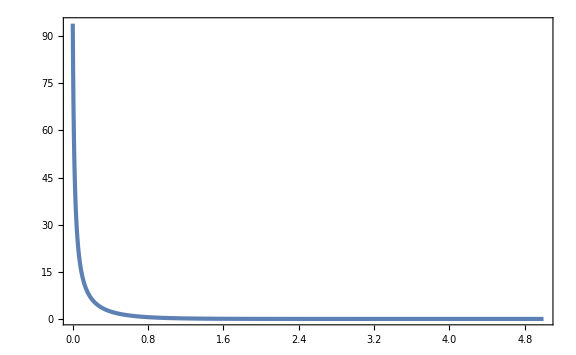

```mathematica
Plot[ηtrs[NN]/.{h->100},{NN,0,5},PlotRange->Full]
```

```mathematica
h^2/4(h+12)/(h-6)^2/.{h->-6}
```

3/8

```mathematica
ϵUSR[τ_]=ϵ0(τ/τ0)^6;
a[τ_]=-1/(τ H);
```

```mathematica
ζkUSR[τ_,k_]=(I H)/(2Sqrt[ϵUSR[τ]])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkUSRp[τ_,k_]=D[ζkUSR[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) τ0^3)/(2 √(k^3 ϵ0) τ^4)

```mathematica
ζkUSRs[τ_,k_]=Conjugate[ζkUSR[τ,k]]//Simplify
ζkUSRps[τ_,k_]=Conjugate[ζkUSRp[τ,k]]//Simplify
```

-(ⅇ^(ⅈ k τ) H (ⅈ+k τ) τ0^3)/(2 √(k^3 ϵ0) τ^3)

(ⅇ^(ⅈ k τ) H (3 ⅈ+k τ (3-ⅈ k τ)) τ0^3)/(2 √(k^3 ϵ0) τ^4)

```mathematica
PζUSR[τ_,k_]=ζkUSR[τ,k]ζkUSRs[τ,k]//Simplify
```

(H^2 (1+k^2 τ^2) τ0^6)/(4 k^3 ϵ0 τ^6)

```mathematica
ζkUSR[τ,p] ζkUSR[τ,k]^2 ζkUSRs[τp,p]ζkUSRs[τp,k]ζkUSRps[τp,k]//ExpToTrig//Expand//Im//Simplify
```

1/(64 k^6 p^3 ϵ0^3 τ^9 τp^10)H^6 τ0^18 ((3 p (-τ+τp)+k^5 τ^2 τp^3 (1+p^2 τ τp)-k^3 τp (1+p^2 τ τp) (6 τ^2-8 τ τp+τp^2)-2 k^4 p τ τp^2 (2 τ^2-3 τ τp+τp^2)-6 k (τ-τp+p^2 τ^2 τp-p^2 τ τp^2)+k^2 p (3 τ^3-15 τ^2 τp+16 τ τp^2-4 τp^3)) Cos[(2 k+p) (τ-τp)]+(3-6 k p (τ-τp)^2+3 p^2 τ τp+k^5 p τ^2 (τ-τp) τp^3-k^2 (1+p^2 τ τp) (3 τ^2-12 τ τp+4 τp^2)+k^3 p τp (-6 τ^3+14 τ^2 τp-9 τ τp^2+τp^3)+2 k^4 τ τp^2 (-τp+2 p^2 τ^2 τp+τ (2-p^2 τp^2))) Sin[(2 k+p) (τ-τp)])

```mathematica
Normal[Series[ζkUSR[τ,p] ζkUSR[τ,k]^2 ζkUSRs[τp,p]ζkUSRs[τp,k]ζkUSRps[τp,k]//ExpToTrig//Expand//Im//Simplify,{τ,0,-9},{τp,0,-7}]]
```

-(H^6 (k^3+p^3) τ0^18)/(64 k^6 p^3 ϵ0^3 τ^9 τp^7)

```mathematica
Integrate[a[τp]^2 ϵUSR[τp]ϵUSR'[τp]Normal[Series[ζkUSR[τ,p] ζkUSR[τ,k]^2 ζkUSRs[τp,p]ζkUSRs[τp,k]ζkUSRps[τp,k]//ExpToTrig//Expand//Im//Simplify,{τ,0,-9},{τp,0,-7}]]//Simplify,{τp,τ0,τ}]/PζUSR[τ,k]/PζUSR[τ,p]//Simplify
```

-((k^3+p^3) ϵ0 τ^3 (τ^3-τ0^3))/(2 k^3 (1+k^2 τ^2) (1+p^2 τ^2) τ0^6)

```mathematica
a[τ]^2 ϵUSR[τ]^2 ζkUSR[τ,p] ζkUSR[τ,k]^2 ζkUSRs[τ,p]ζkUSRs[τ,k]ζkUSRps[τ,k]/PζUSR[τ,k]/PζUSR[τ,p]//ExpToTrig//Expand//Im//Simplify
```

(ϵ0 τ^6)/(4 τ0^6)

```mathematica
a[τ]^2 ϵUSR[τ] ηUSR/2 ζkUSR[τ,p] ζkUSR[τ,k]^2 ζkUSRs[τ,p]ζkUSRs[τ,k]ζkUSRps[τ,k]/PζUSR[τ,k]/PζUSR[τ,p]//ExpToTrig//Expand//Im//Simplify
```

ηUSR/8

```mathematica
Integrate[a[τp]^2 ϵUSR[τp]^2 Normal[Series[ζkUSR[τ,p] ζkUSR[τ,k]^2 ζkUSRs[τp,p]ζkUSRps[τp,k]ζkUSRps[τp,k]//ExpToTrig//Expand//Im//Simplify,{τ,0,-9},{τp,0,-7}]],{τp,τ0,τ}]/PζUSR[τ,k]/PζUSR[τ,p]//Simplify
```

(p^3 ϵ0 τ^3 (τ^3-τ0^3))/(4 k^3 (1+k^2 τ^2) (1+p^2 τ^2) τ0^6)

```mathematica
a[τ]/H ϵUSR[τ]ζkUSR[τ,p] ζkUSR[τ,k]^2 ζkUSRs[τ,p]ζkUSRps[τ,k]ζkUSRps[τ,k]/PζUSR[τ,k]/PζUSR[τ,p]//ExpToTrig//Expand//Im//Simplify
```

(3+2 k^2 τ^2)/(2+2 k^2 τ^2)

```mathematica
(3/2-6/8)5/3 2
```

5/2

```mathematica
ζkSRform[τ_,k_]=(I H)/(2Sqrt[ϵ0])(τ0/τe)^3 1/k^(3/2)(Ak E^(-I k τ)(1+I k τ)-Bk E^(I k τ)(1-I k τ));
ζkSRformp[τ_,k_]=D[ζkSRform[τ,k], τ]//Simplify
```

(ⅈ ⅇ^(-ⅈ k τ) (Ak-Bk ⅇ^(2 ⅈ k τ)) H √(k/ϵ0) τ τ0^3)/(2 τe^3)

```mathematica
ζkSRforms[τ_,k_]=(-I H)/(2Sqrt[ϵ0])(τ0/τe)^3 1/k^(3/2)(Aks E^(I k τ)(1-I k τ)-Bks E^(-I k τ)(1+I k τ));
ζkSRformps[τ_,k_]=D[ζkSRforms[τ,k], τ]//Simplify
```

(ⅈ ⅇ^(-ⅈ k τ) (Bks-Aks ⅇ^(2 ⅈ k τ)) H √(k/ϵ0) τ τ0^3)/(2 τe^3)

```mathematica
ζkSRform[τe,k]ζkSRformps[τe,k]/.{Ak->1,Aks->1,Bk->0,Bks->0}//Im//Simplify
```

(H^2 τ0^6)/(4 ϵ0 τe^4)

```mathematica
Simplify[Normal[Series[ζkSRform[x τe,-xk/τe]ζkSRformps[τe,-xk/τe],{x,0,0},{xk,0,0}]]//Im//FullSimplify]
```

(H^2 τ0^6 (-Im[(Ak-Bk) (Aks-Bks)]+xk Re[(Ak-Bk) (Aks+Bks)]))/(4 xk ϵ0 τe^4)

```mathematica
vk[τ_,k_]=Ak/Sqrt[2k](1-I/(k τ))E^(-I k τ)+Bk/Sqrt[2k](1+I/(k τ))E^(I k τ);
vks[τ_,k_]=Aks/Sqrt[2k](1+I/(k τ))E^(I k τ)+Bks/Sqrt[2k](1-I/(k τ))E^(-I k τ);
```

```mathematica
D[D[vk[τ,k], τ], τ]+(k^2-2/τ^2)vk[τ,k]//Simplify
```

0

```mathematica
vk[τ,k]D[vks[τ,k], τ]-vks[τ,k]D[vk[τ,k], τ]//Simplify
```

ⅈ (Ak Aks-Bk Bks)

```mathematica
USR2SR=Solve[Simplify[{ζkUSR[τe,k]==ζkSRform[τe,k],ζkUSRp[τe,k]==ζkSRformp[τe,k]}(*,Assumptions->{ϵ0>0}*)],{Ak,Bk},Assumptions->{ϵ0>0}][[1]]//Simplify
```

{Ak→1-(3 ⅈ)/(2 k^3 τe^3)-(3 ⅈ)/(2 k τe),Bk→(3 ⅈ ⅇ^(-2 ⅈ k τe) (-ⅈ+k τe)^2)/(2 k^3 τe^3)}

```mathematica
Ak-(1+(3(1+k^2 τe^2))/(2I k^3 τe^3))/.USR2SR//Simplify
Bk-(3 E^(-2I k τe)(1+I k τe)^2)/(2I k^3 τe^3)/.USR2SR//Simplify
```

0

0

```mathematica
Normal[Series[Ak/.USR2SR,{k,0,1}]]
Normal[Series[Bk/.USR2SR,{k,0,1}]]
```

1-(3 ⅈ)/(2 k^3 τe^3)-(3 ⅈ)/(2 k τe)

-1-(3 ⅈ)/(2 k^3 τe^3)-(3 ⅈ)/(2 k τe)

```mathematica
Normal[Series[(Ak-Bk)Conjugate[Ak+Bk]/.USR2SR//FullSimplify,{k,0,-3}]]
```

(6 ⅈ)/(k^3 τe^3)

```mathematica
ζkSR[τ_,k_]=ζkSRform[τ,k]/.USR2SR//Simplify
ζkSRp[τ_,k_]=D[ζkSR[τ,k], τ]//Simplify
ζkSRs[τ_,k_]=Conjugate[ζkSR[τ,k]]//FullSimplify
ζkSRsp[τ_,k_]=Conjugate[ζkSRp[τ,k]]//FullSimplify
```

(ⅇ^(-ⅈ k (τ+2 τe)) H τ0^3 (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τe)^2-ⅇ^(2 ⅈ k τe) (-ⅈ+k τ) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3)))/(4 k^(9/2) √ϵ0 τe^6)

(ⅇ^(-ⅈ k (τ+2 τe)) H τ τ0^3 (3 ⅇ^(2 ⅈ k τ) (-ⅈ+k τe)^2+ⅇ^(2 ⅈ k τe) (3+3 k^2 τe^2+2 ⅈ k^3 τe^3)))/(4 k^(5/2) √ϵ0 τe^6)

(ⅇ^(ⅈ k (τ+2 τe)) H τ0^3 (3 ⅇ^(-2 ⅈ k τ) (1+ⅈ k τ) (ⅈ+k τe)^2-ⅇ^(-2 ⅈ k τe) (ⅈ+k τ) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe))))/(4 √(k^9 ϵ0) τe^6)

(ⅇ^(-ⅈ k τ) H τ τ0^3 (3 ⅇ^(2 ⅈ k τe) (ⅈ+k τe)^2+ⅇ^(2 ⅈ k τ) (3+k^2 τe^2 (3-2 ⅈ k τe))))/(4 √(k^5 ϵ0) τe^6)

```mathematica
Normal[Series[ζkSR[τ,k],{k,0,0}]]//Simplify
```

-(ⅈ H τ0^3 (τ^3-2 τe^3))/(2 √(k^3 ϵ0) τe^6)

```mathematica
Abs[Re[1/(H^2 x^2)ϵ0 (x/τ0)^6(ϵ0 (x/τ0)^6-3)ζkUSR[-x,k]^2 ζkUSRp[-x,k]/.{ϵ0->10^-2,τ0->-10^2,k->10^-1,H->1}]]/.{x->1}//N
Abs[Re[1/(H^2 x^2)ϵ0 (τe/τ0)^6(ϵ0 (τe/τ0)^6)ζkSR[-x,k]^2 ζkSRp[-x,k]/.{ϵ0->10^-2,τ0->-10^2,τe->-1,k->10^-1,H->1}]]/.{x->1}//N
```

2.38593×10^8

7.9531×10^-7

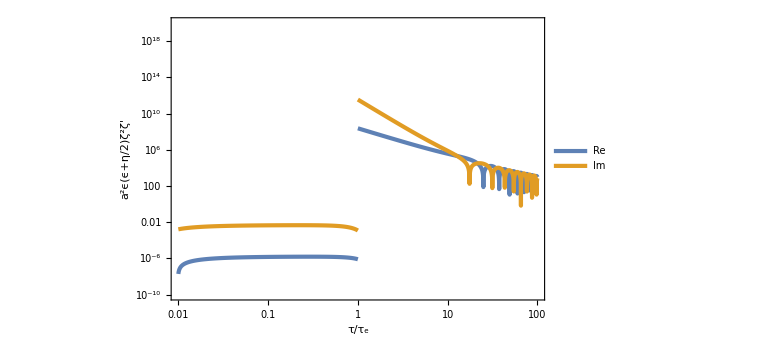

```mathematica
Show[LogLogPlot[{Abs[Re[1/(H^2 x^2)ϵ0 (x/τ0)^6(ϵ0 (x/τ0)^6-3)ζkUSR[-x,k]^2 ζkUSRp[-x,k]/.{ϵ0->10^-2,τ0->-10^2,k->10^-1,H->1}]],Abs[Im[1/(H^2 x^2)ϵ0 (x/τ0)^6(ϵ0 (x/τ0)^6-3)ζkUSR[-x,k]^2 ζkUSRp[-x,k]/.{ϵ0->10^-2,τ0->-10^2,k->10^-1,H->1}]]},{x,1,10^2},PlotRange->{{10^-2,10^2},{10^-10,10^20}},PlotLegends->Placed[{Re,Im},{0.2,0.8}],FrameLabel->{"τ/τ_e","a^2ϵ(ϵ+η/2)ζ^2ζ'"},WorkingPrecision->30],LogLogPlot[{Abs[Re[1/(H^2 x^2)ϵ0 (τe/τ0)^6(ϵ0 (τe/τ0)^6)ζkSR[-x,k]^2 ζkSRp[-x,k]/.{ϵ0->10^-2,τ0->-10^2,τe->-1,k->10^-1,H->1}]],Abs[Im[1/(H^2 x^2)ϵ0 (τe/τ0)^6(ϵ0 (τe/τ0)^6)ζkSR[-x,k]^2 ζkSRp[-x,k]/.{ϵ0->10^-2,τ0->-10^2,τe->-1,k->10^-1,H->1}]]},{x,10^-2,1}]]
```

```mathematica
Normal[Series[ζkSR[x τe,-xk/τe]ζkSRsp[τe,-xk/τe],{x,0,0},{xk,0,0}]]//Im//Simplify
```

(H^2 τ0^6)/(4 ϵ0 τe^4)

```mathematica
5/3 1/(τe^2 H^2)(τe/τ0)^6 ϵ0 Δηe Normal[Series[ζkSR[x τe,-xk/τe]ζkSRsp[τe,-xk/τe],{x,0,0},{xk,0,0}]]//Im//Simplify
```

(5 Δηe)/12

```mathematica
Pζ[τ_,k_]=ζkSRs[τ,k]ζkSR[τ,k]//Simplify
```

1/(16 k^9 ϵ0 τe^12)H^2 τ0^6 (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τe)^2-ⅇ^(2 ⅈ k τe) (-ⅈ+k τ) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3)) (3 ⅇ^(-2 ⅈ k τ) (1+ⅈ k τ) (ⅈ+k τe)^2-ⅇ^(-2 ⅈ k τe) (ⅈ+k τ) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)))

```mathematica
PSR[k_]=Normal[Series[Pζ[x τe,k],{x,0,0}]]//FullSimplify
```

(H^2 τ0^6 (9+18 k^2 τe^2+9 k^4 τe^4+2 k^6 τe^6-3 (3+k^4 τe^4) Cos[2 k τe]-6 k τe (3+2 k^2 τe^2+k^4 τe^4) Sin[2 k τe]))/(8 k^9 ϵ0 τe^12)

```mathematica
PSR[k]-H^2/(4ϵ0 k^3)(τ0/τe)^6(Ak-Bk)Conjugate[Ak-Bk]/.USR2SR//FullSimplify
```

0

```mathematica
Normal[Series[Ak/.USR2SR,{k,0,0}]]
```

1-(3 ⅈ)/(2 k^3 τe^3)-(3 ⅈ)/(2 k τe)

```mathematica
Normal[Series[(Ak-Bk)Conjugate[Ak-Bk]/.USR2SR//Simplify,{k,0,0}]]
Normal[Series[(Ak-Bk)Conjugate[Ak-Bk]/.USR2SR//Simplify,{k,∞,0}]]
```

4

1

```mathematica
k^3/(2 π^2)Normal[Series[PSR[k],{k,0,-3}]]
```

(H^2 τ0^6)/(2 π^2 ϵ0 τe^6)

```mathematica
PSR[1/(δ τe)]//Simplify
```

-(H^2 δ^3 τ0^6 (-2-9 δ^2-18 δ^4-9 δ^6+3 (δ^2+3 δ^6) Cos[2/δ]+6 (δ+2 δ^3+3 δ^5) Sin[2/δ]))/(8 ϵ0 τe^3)

```mathematica
k^3/(2 π^2)Normal[Series[PSR[1/(δ τe)]//Simplify,{δ,0,3}]]/.{δ->1/(k τe)}
```

(H^2 τ0^6)/(8 π^2 ϵ0 τe^6)

```mathematica
(k^3/(2 π^2)PSR[k])/(1/(2ϵ0)(τ0/τe)^6(H/(2π))^2)//Simplify
```

(9+18 k^2 τe^2+9 k^4 τe^4+2 k^6 τe^6-3 (3+k^4 τe^4) Cos[2 k τe]-6 k τe (3+2 k^2 τe^2+k^4 τe^4) Sin[2 k τe])/(2 k^6 τe^6)

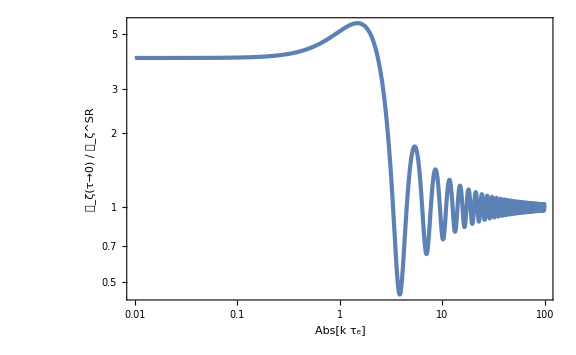

```mathematica
LogLogPlot[(k^3/(2 π^2)PSR[k])/(1/(2ϵ0)(τ0/τe)^6(H/(2π))^2)/.{τe->-1}//Simplify,{k,10^-2,10^2},FrameLabel->{Abs[k Subscript[τ, "e"]],Row[{Subscript[𝒫, ζ][τ->0]," / ", Subscript[𝒫, ζ]^SR}]},GridLines->{None,{1,4}}]
```

```mathematica
pktk[τ_,τp_,p_,k_]=ζkSR[τ,p]ζkSR[τ,k]ζkSR[τ,k]ζkSRs[τp,p]ζkSRs[τp,k]ζkSRsp[τp,k]//Simplify
```

1/(4096 k^16 p^9 ϵ0^3 τe^36)ⅇ^(-ⅈ (2 k (τ+τe)+p (τ-τp))) H^6 τ0^18 (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τe)^2+ⅇ^(2 ⅈ k τe) (-ⅈ+k τ) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3))^2 (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τe)^2-ⅇ^(2 ⅈ p τe) (-ⅈ+p τ) (-3 ⅈ-3 ⅈ p^2 τe^2+2 p^3 τe^3)) (3 ⅇ^(2 ⅈ k τe) (ⅈ+k τe)^2+ⅇ^(2 ⅈ k τp) (3+k^2 τe^2 (3-2 ⅈ k τe))) τp (3 ⅇ^(-2 ⅈ k τp) (ⅈ+k τe)^2 (1+ⅈ k τp)-ⅇ^(-2 ⅈ k τe) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (ⅈ+k τp)) (3 ⅇ^(-2 ⅈ p τp) (ⅈ+p τe)^2 (1+ⅈ p τp)-ⅇ^(-2 ⅈ p τe) (3 ⅈ+p^2 τe^2 (3 ⅈ+2 p τe)) (ⅈ+p τp))

```mathematica
Normal[Series[5/3(1/(τe^2 H^2)(τe/τ0)^6 ϵ0 Δηe pktk[x τe,τe,-xpk xk/τe,-xk/τe])/(Pζ[x τe,-xpk xk/τe]Pζ[x τe,-xk/τe]),{x,0,0},{xk,0,0}]]//Simplify//Expand//Im//Simplify
```

-(5 xpk^3 Δηe)/48

```mathematica
pktkim[p_,k_]=Normal[Series[pktk[x τe,τe,p,k],{x,0,0}]]//Simplify//ExpToTrig//Simplify//Expand//Im//Simplify
```

1/(64 k^12 p^6 ϵ0^3 τe^25)H^6 τ0^18 (-p τe Cos[p τe] ((-27 p^3-45 k^2 p^3 τe^2-36 k^4 p^3 τe^4-15 k^6 p^3 τe^6-4 k^8 p^3 τe^8-9 k^3 (3+2 p^2 τe^2)-3 k^5 τe^2 (3+2 p^2 τe^2)+k^9 τe^6 (3+2 p^2 τe^2)) Sin[k τe]^2+k τe (9+3 k^2 τe^2+k^4 τe^4) (3 p^3+3 k^2 p^3 τe^2+k^4 p^3 τe^4+k^3 (3+2 p^2 τe^2)) Sin[2 k τe])+((-27 p^3-45 k^2 p^3 τe^2-36 k^4 p^3 τe^4-15 k^6 p^3 τe^6-4 k^8 p^3 τe^8-9 k^3 (3+3 p^2 τe^2+p^4 τe^4)-3 k^5 τe^2 (3+3 p^2 τe^2+p^4 τe^4)+k^9 τe^6 (3+3 p^2 τe^2+p^4 τe^4)) Sin[k τe]^2+k τe (9+3 k^2 τe^2+k^4 τe^4) (3 p^3+3 k^2 p^3 τe^2+k^4 p^3 τe^4+k^3 (3+3 p^2 τe^2+p^4 τe^4)) Sin[2 k τe]) Sin[p τe]-k^2 τe^2 (9+3 k^2 τe^2+k^4 τe^4) Cos[k τe]^2 (-p (k+p) τe (-3 k p+3 p^2+k^2 (3+2 p^2 τe^2)) Cos[p τe]+(3 p^3+2 k^2 p^3 τe^2+k^3 (3+3 p^2 τe^2+p^4 τe^4)) Sin[p τe]))

```mathematica
fNL[p_,k_]=5/3(1/(τe^2 H^2)(τe/τ0)^6 ϵ0 Δηe pktkim[p,k])/(PSR[p]PSR[k])//Simplify
```

(5 p^3 Δηe τe^3 (-p τe Cos[p τe] ((-27 p^3-45 k^2 p^3 τe^2-36 k^4 p^3 τe^4-15 k^6 p^3 τe^6-4 k^8 p^3 τe^8-9 k^3 (3+2 p^2 τe^2)-3 k^5 τe^2 (3+2 p^2 τe^2)+k^9 τe^6 (3+2 p^2 τe^2)) Sin[k τe]^2+k τe (9+3 k^2 τe^2+k^4 τe^4) (3 p^3+3 k^2 p^3 τe^2+k^4 p^3 τe^4+k^3 (3+2 p^2 τe^2)) Sin[2 k τe])+((-27 p^3-45 k^2 p^3 τe^2-36 k^4 p^3 τe^4-15 k^6 p^3 τe^6-4 k^8 p^3 τe^8-9 k^3 (3+3 p^2 τe^2+p^4 τe^4)-3 k^5 τe^2 (3+3 p^2 τe^2+p^4 τe^4)+k^9 τe^6 (3+3 p^2 τe^2+p^4 τe^4)) Sin[k τe]^2+k τe (9+3 k^2 τe^2+k^4 τe^4) (3 p^3+3 k^2 p^3 τe^2+k^4 p^3 τe^4+k^3 (3+3 p^2 τe^2+p^4 τe^4)) Sin[2 k τe]) Sin[p τe]-k^2 τe^2 (9+3 k^2 τe^2+k^4 τe^4) Cos[k τe]^2 (-p (k+p) τe (-3 k p+3 p^2+k^2 (3+2 p^2 τe^2)) Cos[p τe]+(3 p^3+2 k^2 p^3 τe^2+k^3 (3+3 p^2 τe^2+p^4 τe^4)) Sin[p τe])))/(3 k^3 (9+18 k^2 τe^2+9 k^4 τe^4+2 k^6 τe^6-3 (3+k^4 τe^4) Cos[2 k τe]-6 k τe (3+2 k^2 τe^2+k^4 τe^4) Sin[2 k τe]) (9+18 p^2 τe^2+9 p^4 τe^4+2 p^6 τe^6-3 (3+p^4 τe^4) Cos[2 p τe]-6 p τe (3+2 p^2 τe^2+p^4 τe^4) Sin[2 p τe]))

```mathematica
Normal[Series[fNL[xp/τe,xk/τe],{xp,0,0},{xk,0,2}]]
```

(xk^2 Δηe)/36

```mathematica
nsm1[k_]=(k PSR'[k])/PSR[k]+3//Simplify
```

-(6 (3 (3+4 k^2 τe^2+k^4 τe^4)+(-9+6 k^2 τe^2+3 k^4 τe^4+2 k^6 τe^6) Cos[2 k τe]-2 k τe (9+3 k^2 τe^2+k^4 τe^4) Sin[2 k τe]))/(9+18 k^2 τe^2+9 k^4 τe^4+2 k^6 τe^6-3 (3+k^4 τe^4) Cos[2 k τe]-6 k τe (3+2 k^2 τe^2+k^4 τe^4) Sin[2 k τe])

```mathematica
Normal[Series[nsm1[xk/τe]//Simplify,{xk,0,2}]]
```

(4 xk^2)/5

```mathematica
5/12(2/(xe^2 τ0^2 H^2)xe^6 ϵ0 Δηe Im[pktk[xe τ0,xe τ0,p,k]//Expand]2)/(PUSR[xe,p]PUSR[xe,k])//Simplify
```

$Aborted

```mathematica
ζkSR2form[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^3 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ));
ζkSR2formp[τ_,k_]=D[ζkSR2form[τ,k], τ]//Simplify
```

(ⅈ ⅇ^(-ⅈ k τ) (Ck-Dk ⅇ^(2 ⅈ k τ)) H √(k/ϵSR) τ τs^3)/(2 τe^3)

```mathematica
USR2SR=Solve[{ζkUSR[τe,τs,k]==ζkSR2form[τe,k],ζkUSRp[τe,τs,k]==ζkSR2formp[τe,k]},{Ck,Dk}][[1]]//Simplify
```

{Ck→(ⅇ^(-ⅈ k (τe+4 τs)) √ϵSR (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(11/2) τe^3 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) τs^3),Dk→(ⅇ^(-2 ⅈ k (τe+τs)) (3 ⅇ^(2 ⅈ k τe) (3+3 k^2 τe^2-2 ⅈ k^3 τe^3) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^6 τe^3 τs^3)}

```mathematica
ζk[τ_,τs_,τe_,k_]=ζkSR2form[τ,k]/.USR2SR//Simplify
```

1/(8 k^(15/2) τe^6)ⅈ ⅇ^(-ⅈ k τ) H (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+3 k^2 τe^2-2 ⅈ k^3 τe^3) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(√ϵSR)+1/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe)ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))

```mathematica
ζks[τ_,τs_,τe_,k_]=Conjugate[ζk[τ,τs,τe,k]]//FullSimplify
ζksp[τ_,τs_,τe_,k_]=D[ζks[τ,τs,τe,k], τ]//Simplify
```

-1/(8 k^(15/2) τe^6)ⅈ ⅇ^(ⅈ k τ) H (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+1/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe)ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))

(ⅇ^(ⅈ k τ) H τ (9 ⅈ ⅇ^(-2 ⅈ k (τe-τs)) √(k ϵSR) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+9 ⅇ^(-2 ⅈ k (τe-τs)) k^(3/2) √ϵSR τe (-ⅈ+k τe)^2 (ⅈ+k τs)^2-3 ⅇ^(-2 ⅈ k (τ-τs)) (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (ⅈ+k τs)^2+3 ⅇ^(-2 ⅈ k (τ-τe)) (ⅈ+k τe)^2 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)+ⅈ √(k ϵSR) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs))+k^(3/2) √ϵSR τe (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs))))/(8 k^(11/2) √ϵSR τe^6 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe))

```mathematica
Pk[τ_,τs_,τe_,k_]=ζks[τ,τs,τe,k]ζk[τ,τs,τe,k]//Simplify
```

1/(64 k^15 τe^12)H^2 (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+3 k^2 τe^2-2 ⅈ k^3 τe^3) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(√ϵSR)+1/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe)ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))) (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+1/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe)ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))

```mathematica
PSR[p_]=Normal[Series[Pk[τ,τs,τe,p],{p,0,-3}]]
```

H^2/(4 p^3 ϵSR)

```mathematica
PUSR[xe_,τs_,k_]=Normal[Series[Pk[-xf/k,τs,xe τs,k],{xe,0,-6},{xf,0,0}]]//Simplify//ExpToTrig//FullSimplify
```

(H^2 (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6+3 (-3+7 k^4 τs^4) Cos[2 k τs]+6 k τs (-3-4 k^2 τs^2+k^4 τs^4) Sin[2 k τs]))/(2 k^9 xe^6 ϵSR τs^6)

```mathematica
calPk[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk[τ,τs,τe,k];
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

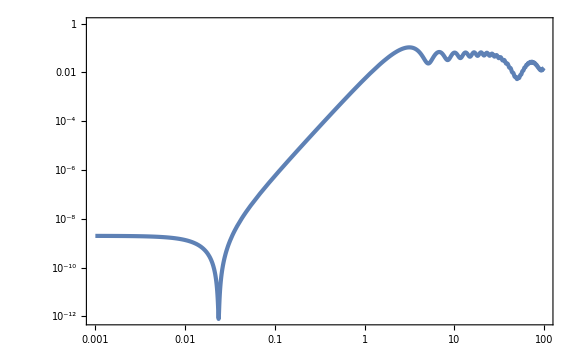

```mathematica
LogLogPlot[calPk[-10^-2,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30]
```

```mathematica
nsm1[τ_,τs_,τe_,k_]=k D[Log[calPk[τ,τs,τe,k]], k];
```

```mathematica
nsm1e[x_]=Normal[Series[nsm1[-xf/k,τs,xe τs,-x/τs],{xe,0,0},{xf,0,0}]]//Simplify//ExpToTrig//FullSimplify
```

(6 (-3 (3+4 x^2+x^4)+(9-6 x^2-15 x^4+2 x^6) Cos[2 x]+2 x (9+6 x^2-4 x^4) Sin[2 x]))/(9+18 x^2+9 x^4+2 x^6+3 (-3+7 x^4) Cos[2 x]+6 x (-3-4 x^2+x^4) Sin[2 x])

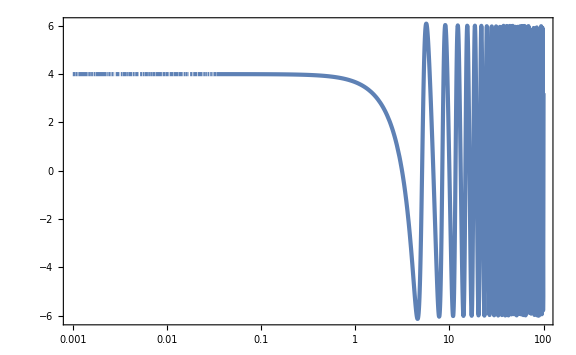

```mathematica
LogLinearPlot[nsm1e[x],{x,10^-3,10^2},WorkingPrecision->30]
```

```mathematica
pktk[τ_,τp_,τs_,τe_,p_,k_]=ζk[τ,τs,τe,p] ζk[τ,τs,τe,k]^2 ζks[τp,τs,τe,p]ζks[τp,τs,τe,k]ζksp[τp,τs,τe,k];
```

```mathematica
pktkeim[xe_,p_,k_]=Normal[Series[pktk[-xf/k,xe τs,τs,xe τs,p,k],{p,0,-3},{xe,0,-8},{xf,0,0}]]//Simplify//ExpToTrig//Expand//Im//Simplify
```

(H^6 (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6+3 (-3+7 k^4 τs^4) Cos[2 k τs]+6 k τs (-3-4 k^2 τs^2+k^4 τs^4) Sin[2 k τs]))/(240 k^7 p^3 xe^8 ϵSR^3 τs^2)

```mathematica
fNLpktke=Normal[Series[5/12(2/(xe^2 τs^2 H^2)xe^6 ϵSR Δηe pktkeim[xe,p,k]2)/(PSR[p]PUSR[xe,τs,k]),{xe,0,0}]]//FullSimplify
```

0

```mathematica
pktkeS[xe_,p_,k_]=Normal[Series[pktk[-xf/k,xe τs,τs,xe τs,p,k],{xf,0,0}]];
```

```mathematica
fNLpktkeS=Δηe(Normal[Series[5/12(2/(xe^2 τs^2 H^2)xe^6 ϵSR pktkeS[xe,x k,k]2)/(PUSR[xe,τs,x k]PUSR[xe,τs,k]),{xe,0,0},{x,0,0}]]//Simplify//ExpToTrig//Expand//Im//Simplify)
```

-(125 Δηe (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6+3 (-3+7 k^4 τs^4) Cos[2 k τs]+6 k τs (-3-4 k^2 τs^2+k^4 τs^4) Sin[2 k τs]))/(384 k^10 x τs^10)

```mathematica
pktksim[xe_,p_,k_]=Normal[Series[pktk[-xf/k,τs,τs,xe τs,p,k],{p,0,-3},{xe,0,-6},{xf,0,0}]]//Simplify//ExpToTrig//Expand//Simplify//Expand//Im//Simplify
```

1/(13305600 k^13 p^3 xe^15 ϵSR^3 τs^8)H^6 (-8419950-16839900 k^2 τs^2-10103940 k^2 xe^2 τs^2-6548850 k^4 τs^4-20207880 k^4 xe^2 τs^4-1403325 k^4 xe^3 τs^4-962280 k^4 xe^4 τs^4+623700 k^6 τs^6-7858620 k^6 xe^2 τs^6-3742200 k^6 xe^3 τs^6-1924560 k^6 xe^4 τs^6+944460 k^6 xe^6 τs^6+748440 k^8 xe^2 τs^8-2338875 k^8 xe^3 τs^8-748440 k^8 xe^4 τs^8+1888920 k^8 xe^6 τs^8+74844 k^8 xe^7 τs^8-145800 k^8 xe^8 τs^8+71280 k^10 xe^4 τs^10+1011780 k^10 xe^6 τs^10+199584 k^10 xe^7 τs^10-291600 k^10 xe^8 τs^10-12177 k^10 xe^9 τs^10+299640 k^12 xe^6 τs^12+124740 k^12 xe^7 τs^12-168840 k^12 xe^8 τs^12-32472 k^12 xe^9 τs^12-63120 k^14 xe^8 τs^14-20295 k^14 xe^9 τs^14-2 (-5613300-1122660 k^2 (5+6 xe^2) τs^2-26730 k^4 (-140+252 xe^2-105 xe^3+24 xe^4) τs^4+5940 k^6 (-105+756 xe^2+840 xe^3-108 xe^4+378 xe^5+176 xe^6) τs^6-270 k^8 xe^2 (2772-5775 xe-1584 xe^2-12936 xe^3-3872 xe^4+2178 xe^5+206 xe^6) τs^8-9 k^10 xe^3 (-46200+7920 xe-27720 xe^2+77440 xe^3+105336 xe^4+20040 xe^5+16665 xe^6) τs^10-6 k^12 xe^5 (-27720-19360 xe+21978 xe^2+28470 xe^3+30283 xe^4) τs^12+3 k^14 xe^7 (-18216-6680 xe+28853 xe^2) τs^14+6094 k^16 xe^9 τs^16) Cos[2 k τs]+3 (-935550-374220 k^2 (-5+3 xe^2) τs^2-13365 k^4 (-350-168 xe^2-175 xe^3+8 xe^4) τs^4+1980 k^6 (-315+2835 xe^2+1050 xe^3+108 xe^4+756 xe^5+193 xe^6) τs^6+9 k^8 xe^2 (-83160-259875 xe+59400 xe^2+147840 xe^3-84920 xe^4-46332 xe^5+1280 xe^6) τs^8-9 k^10 xe^4 (7920+166320 xe+212300 xe^2+41184 xe^3+2560 xe^4+18359 xe^5) τs^10-4 k^12 xe^6 (-63690-104247 xe+14400 xe^2+36718 xe^3) τs^12+3 k^14 xe^8 (2560+55077 xe) τs^14) Cos[4 k τs]+16839900 k τs Sin[2 k τs]+26195400 k^3 τs^3 Sin[2 k τs]+20207880 k^3 xe^2 τs^3 Sin[2 k τs]+4677750 k^3 xe^3 τs^3 Sin[2 k τs]+1871100 k^5 τs^5 Sin[2 k τs]+31434480 k^5 xe^2 τs^5 Sin[2 k τs]+7484400 k^5 xe^3 τs^5 Sin[2 k τs]+1924560 k^5 xe^4 τs^5 Sin[2 k τs]+2993760 k^5 xe^5 τs^5 Sin[2 k τs]+1247400 k^7 τs^7 Sin[2 k τs]+2245320 k^7 xe^2 τs^7 Sin[2 k τs]+1559250 k^7 xe^3 τs^7 Sin[2 k τs]+2993760 k^7 xe^4 τs^7 Sin[2 k τs]+2993760 k^7 xe^5 τs^7 Sin[2 k τs]-3136320 k^7 xe^6 τs^7 Sin[2 k τs]-833976 k^7 xe^7 τs^7 Sin[2 k τs]+1496880 k^9 xe^2 τs^9 Sin[2 k τs]+831600 k^9 xe^3 τs^9 Sin[2 k τs]+213840 k^9 xe^4 τs^9 Sin[2 k τs]-1995840 k^9 xe^5 τs^9 Sin[2 k τs]-4878720 k^9 xe^6 τs^9 Sin[2 k τs]-983664 k^9 xe^7 τs^9 Sin[2 k τs]+42120 k^9 xe^8 τs^9 Sin[2 k τs]-122562 k^9 xe^9 τs^9 Sin[2 k τs]+142560 k^11 xe^4 τs^11 Sin[2 k τs]+332640 k^11 xe^5 τs^11 Sin[2 k τs]-348480 k^11 xe^6 τs^11 Sin[2 k τs]+306504 k^11 xe^7 τs^11 Sin[2 k τs]+176400 k^11 xe^8 τs^11 Sin[2 k τs]+109692 k^11 xe^9 τs^11 Sin[2 k τs]-232320 k^13 xe^6 τs^13 Sin[2 k τs]-109296 k^13 xe^7 τs^13 Sin[2 k τs]+226440 k^13 xe^8 τs^13 Sin[2 k τs]+468798 k^13 xe^9 τs^13 Sin[2 k τs]+40080 k^15 xe^8 τs^15 Sin[2 k τs]+12188 k^15 xe^9 τs^15 Sin[2 k τs]-8419950 k τs Sin[4 k τs]-7484400 k^3 τs^3 Sin[4 k τs]-10103940 k^3 xe^2 τs^3 Sin[4 k τs]-2338875 k^3 xe^3 τs^3 Sin[4 k τs]+8419950 k^5 τs^5 Sin[4 k τs]-8981280 k^5 xe^2 τs^5 Sin[4 k τs]+4677750 k^5 xe^3 τs^5 Sin[4 k τs]-962280 k^5 xe^4 τs^5 Sin[4 k τs]-1496880 k^5 xe^5 τs^5 Sin[4 k τs]+10103940 k^7 xe^2 τs^7 Sin[4 k τs]+11694375 k^7 xe^3 τs^7 Sin[4 k τs]-855360 k^7 xe^4 τs^7 Sin[4 k τs]+2993760 k^7 xe^5 τs^7 Sin[4 k τs]+3439260 k^7 xe^6 τs^7 Sin[4 k τs]+416988 k^7 xe^7 τs^7 Sin[4 k τs]-1559250 k^9 xe^3 τs^9 Sin[4 k τs]+962280 k^9 xe^4 τs^9 Sin[4 k τs]+7484400 k^9 xe^5 τs^9 Sin[4 k τs]+3057120 k^9 xe^6 τs^9 Sin[4 k τs]-833976 k^9 xe^7 τs^9 Sin[4 k τs]+103680 k^9 xe^8 τs^9 Sin[4 k τs]+165231 k^9 xe^9 τs^9 Sin[4 k τs]-997920 k^11 xe^5 τs^11 Sin[4 k τs]-3439260 k^11 xe^6 τs^11 Sin[4 k τs]-2084940 k^11 xe^7 τs^11 Sin[4 k τs]+92160 k^11 xe^8 τs^11 Sin[4 k τs]-330462 k^11 xe^9 τs^11 Sin[4 k τs]+277992 k^13 xe^7 τs^13 Sin[4 k τs]-103680 k^13 xe^8 τs^13 Sin[4 k τs]-826155 k^13 xe^9 τs^13 Sin[4 k τs]+110154 k^15 xe^9 τs^15 Sin[4 k τs])

```mathematica
fNLpktks[x_]=Normal[Series[-5/12(2/(τs^2 H^2)ϵSR Δηe pktksim[xe,p,-x/τs]2)/(PSR[p]PUSR[xe,τs,-x/τs]),{xe,0,0}]]//Simplify
```

-((Δηe (-8419950-16839900 x^2-6548850 x^4+623700 x^6-10103940 x^2 xe^2-20207880 x^4 xe^2-7858620 x^6 xe^2+748440 x^8 xe^2-1403325 x^4 xe^3-3742200 x^6 xe^3-2338875 x^8 xe^3-962280 x^4 xe^4-1924560 x^6 xe^4-748440 x^8 xe^4+71280 x^10 xe^4+944460 x^6 xe^6+1888920 x^8 xe^6+1011780 x^10 xe^6+299640 x^12 xe^6+74844 x^8 xe^7+199584 x^10 xe^7+124740 x^12 xe^7-145800 x^8 xe^8-291600 x^10 xe^8-168840 x^12 xe^8-63120 x^14 xe^8-12177 x^10 xe^9-32472 x^12 xe^9-20295 x^14 xe^9-2 (-5613300+6094 x^16 xe^9-1122660 x^2 (5+6 xe^2)+3 x^14 xe^7 (-18216-6680 xe+28853 xe^2)-26730 x^4 (-140+252 xe^2-105 xe^3+24 xe^4)-6 x^12 xe^5 (-27720-19360 xe+21978 xe^2+28470 xe^3+30283 xe^4)+5940 x^6 (-105+756 xe^2+840 xe^3-108 xe^4+378 xe^5+176 xe^6)-270 x^8 xe^2 (2772-5775 xe-1584 xe^2-12936 xe^3-3872 xe^4+2178 xe^5+206 xe^6)-9 x^10 xe^3 (-46200+7920 xe-27720 xe^2+77440 xe^3+105336 xe^4+20040 xe^5+16665 xe^6)) Cos[2 x]+3 (-935550+3 x^14 xe^8 (2560+55077 xe)-374220 x^2 (-5+3 xe^2)-4 x^12 xe^6 (-63690-104247 xe+14400 xe^2+36718 xe^3)-13365 x^4 (-350-168 xe^2-175 xe^3+8 xe^4)-9 x^10 xe^4 (7920+166320 xe+212300 xe^2+41184 xe^3+2560 xe^4+18359 xe^5)+1980 x^6 (-315+2835 xe^2+1050 xe^3+108 xe^4+756 xe^5+193 xe^6)+9 x^8 xe^2 (-83160-259875 xe+59400 xe^2+147840 xe^3-84920 xe^4-46332 xe^5+1280 xe^6)) Cos[4 x]+16839900 x Sin[2 x]+26195400 x^3 Sin[2 x]+1871100 x^5 Sin[2 x]+1247400 x^7 Sin[2 x]+20207880 x^3 xe^2 Sin[2 x]+31434480 x^5 xe^2 Sin[2 x]+2245320 x^7 xe^2 Sin[2 x]+1496880 x^9 xe^2 Sin[2 x]+4677750 x^3 xe^3 Sin[2 x]+7484400 x^5 xe^3 Sin[2 x]+1559250 x^7 xe^3 Sin[2 x]+831600 x^9 xe^3 Sin[2 x]+1924560 x^5 xe^4 Sin[2 x]+2993760 x^7 xe^4 Sin[2 x]+213840 x^9 xe^4 Sin[2 x]+142560 x^11 xe^4 Sin[2 x]+2993760 x^5 xe^5 Sin[2 x]+2993760 x^7 xe^5 Sin[2 x]-1995840 x^9 xe^5 Sin[2 x]+332640 x^11 xe^5 Sin[2 x]-3136320 x^7 xe^6 Sin[2 x]-4878720 x^9 xe^6 Sin[2 x]-348480 x^11 xe^6 Sin[2 x]-232320 x^13 xe^6 Sin[2 x]-833976 x^7 xe^7 Sin[2 x]-983664 x^9 xe^7 Sin[2 x]+306504 x^11 xe^7 Sin[2 x]-109296 x^13 xe^7 Sin[2 x]+42120 x^9 xe^8 Sin[2 x]+176400 x^11 xe^8 Sin[2 x]+226440 x^13 xe^8 Sin[2 x]+40080 x^15 xe^8 Sin[2 x]-122562 x^9 xe^9 Sin[2 x]+109692 x^11 xe^9 Sin[2 x]+468798 x^13 xe^9 Sin[2 x]+12188 x^15 xe^9 Sin[2 x]-8419950 x Sin[4 x]-7484400 x^3 Sin[4 x]+8419950 x^5 Sin[4 x]-10103940 x^3 xe^2 Sin[4 x]-8981280 x^5 xe^2 Sin[4 x]+10103940 x^7 xe^2 Sin[4 x]-2338875 x^3 xe^3 Sin[4 x]+4677750 x^5 xe^3 Sin[4 x]+11694375 x^7 xe^3 Sin[4 x]-1559250 x^9 xe^3 Sin[4 x]-962280 x^5 xe^4 Sin[4 x]-855360 x^7 xe^4 Sin[4 x]+962280 x^9 xe^4 Sin[4 x]-1496880 x^5 xe^5 Sin[4 x]+2993760 x^7 xe^5 Sin[4 x]+7484400 x^9 xe^5 Sin[4 x]-997920 x^11 xe^5 Sin[4 x]+3439260 x^7 xe^6 Sin[4 x]+3057120 x^9 xe^6 Sin[4 x]-3439260 x^11 xe^6 Sin[4 x]+416988 x^7 xe^7 Sin[4 x]-833976 x^9 xe^7 Sin[4 x]-2084940 x^11 xe^7 Sin[4 x]+277992 x^13 xe^7 Sin[4 x]+103680 x^9 xe^8 Sin[4 x]+92160 x^11 xe^8 Sin[4 x]-103680 x^13 xe^8 Sin[4 x]+165231 x^9 xe^9 Sin[4 x]-330462 x^11 xe^9 Sin[4 x]-826155 x^13 xe^9 Sin[4 x]+110154 x^15 xe^9 Sin[4 x]))/(997920 x^4 xe^9 (9+18 x^2+9 x^4+2 x^6+3 (-3+7 x^4) Cos[2 x]+6 x (-3-4 x^2+x^4) Sin[2 x])))

```mathematica
Normal[Series[fNLpktks[x],{xe,0,-9}]]//Simplify
```

-(5 Δηe (x Cos[x]-Sin[x]) Sin[x])/(4 x^4 xe^9)

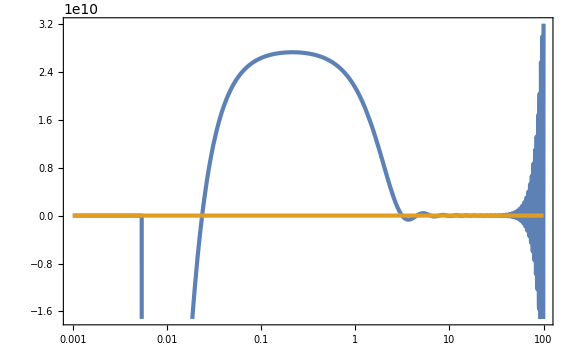

```mathematica
LogLinearPlot[{fNLpktks[x]/.{Δηe->6,xe->10^-lndt},-5/12 nsm1e[x]},{x,10^-3,10^2},WorkingPrecision->30]
```

## USR2SR smooth

```mathematica
$Assumptions={h<0,k>0,τe<0,τ0<0,τ<0,ϵ>0,ϵV>0,ϵe>0,h<0,H>0,xp>0,xk>0};
```

```mathematica
ϵUSR[τ_]=ϵe(τ/τe)^6;
```

```mathematica
ζkUSR[τ_,k_]=(I H)/(2Sqrt[ϵUSR[τ]])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkUSRp[τ_,k_]=D[ζkUSR[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) τe^3)/(2 √(k^3 ϵe) τ^4)

```mathematica
ζkUSRs[τ_,k_]=Conjugate[ζkUSR[τ,k]]//Simplify
ζkUSRsp[τ_,k_]=D[ζkUSRs[τ,k], τ]//Simplify
```

-(ⅇ^(ⅈ k τ) H (ⅈ+k τ) τe^3)/(2 √(k^3 ϵe) τ^3)

(ⅇ^(ⅈ k τ) H (3 ⅈ+3 k τ-ⅈ k^2 τ^2) τe^3)/(2 √(k^3 ϵe) τ^4)

```mathematica
ζkSRform[τ_,k_]=(I H)/(2Sqrt[ϵV])1/k^(3/2)(Ak E^(-I k τ)(1+I k τ)-Bk E^(I k τ)(1-I k τ));
ζkSRformp[τ_,k_]=D[ζkSRform[τ,k], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) (Ak-Bk ⅇ^(2 ⅈ k τ)) H √(k/ϵV) τ

```mathematica
ABsol=Solve[{ζkUSR[τe,k]==ζkSRform[τe,k],ζkUSRp[τe,k]==ζkSRformp[τe,k]}/.{ϵV->(h^2 ϵe)/36},{Ak,Bk}][[1]]//Simplify
```

{Ak→1/12 h (-2+(3 ⅈ)/(k^3 τe^3)+(3 ⅈ)/(k τe)),Bk→-(ⅈ ⅇ^(-2 ⅈ k τe) h (-ⅈ+k τe)^2)/(4 k^3 τe^3)}

```mathematica
ζkSR[τ_,k_]=ζkSRform[τ,k]/.ABsol/.{ϵV->(h^2 ϵe)/36}//Simplify
ζkSRp[τ_,k_]=D[ζkSR[τ,k], τ]//Simplify
```

-(ⅇ^(-ⅈ k (τ+2 τe)) H (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τe)^2+ⅇ^(2 ⅈ k τe) (-ⅈ+k τ) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3)))/(4 k^(9/2) √ϵe τe^3)

(ⅇ^(-ⅈ k (τ+2 τe)) H τ (3 ⅇ^(2 ⅈ k τ) (-ⅈ+k τe)^2+ⅇ^(2 ⅈ k τe) (3+3 k^2 τe^2+2 ⅈ k^3 τe^3)))/(4 k^(5/2) √ϵe τe^3)

```mathematica
ζkSRs[τ_,k_]=Conjugate[ζkSR[τ,k]]//FullSimplify
ζkSRsp[τ_,k_]=D[ζkSRs[τ,k], τ]//Simplify
```

-(ⅇ^(ⅈ k (τ+2 τe)) H (-3 ⅈ ⅇ^(-2 ⅈ k τ) (-ⅈ+k τ) (ⅈ+k τe)^2+ⅇ^(-2 ⅈ k τe) (ⅈ+k τ) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe))))/(4 √(k^9 ϵe) τe^3)

(ⅇ^(-ⅈ k τ) H τ (3 ⅇ^(2 ⅈ k τe) (ⅈ+k τe)^2+ⅇ^(2 ⅈ k τ) (3+3 k^2 τe^2-2 ⅈ k^3 τe^3)))/(4 √(k^5 ϵe) τe^3)

```mathematica
Pζ[τ_,k_]=ζkSR[τ,k]ζkSRs[τ,k]//Simplify
```

1/(16 k^9 ϵe τe^6)H^2 (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τe)^2+ⅇ^(2 ⅈ k τe) (-ⅈ+k τ) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3)) (-3 ⅈ ⅇ^(-2 ⅈ k τ) (-ⅈ+k τ) (ⅈ+k τe)^2+ⅇ^(-2 ⅈ k τe) (ⅈ+k τ) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)))

```mathematica
fNL[xp_,xk_]=1/(τe^2 H^2)ϵe (ζkSR[0,-xp xk/τe] ζkSR[0,-xk/τe]^2 ζkUSRs[τe,-xp xk/τe]ζkUSRs[τe,-xk/τe]ζkUSRsp[τe,-xk/τe])/(Pζ[0,-xp xk/τe]Pζ[0,-xk/τe])//ExpToTrig//Im//Simplify
```

1/4 Im[((-ⅈ+xk) (-3-3 ⅈ xk+xk^2) xp^3 (-ⅈ+xk xp) (xk (-3+3 ⅈ xk+xk^2) Cos[xk]-ⅈ (3 ⅈ+3 xk+xk^3) Sin[xk]))/((xk (-3-3 ⅈ xk+xk^2) Cos[xk]+ⅈ (-3 ⅈ+3 xk+xk^3) Sin[xk]) (xk xp (-3-3 ⅈ xk xp+xk^2 xp^2) Cos[xk xp]+(3+3 ⅈ xk xp+ⅈ xk^3 xp^3) Sin[xk xp]))]

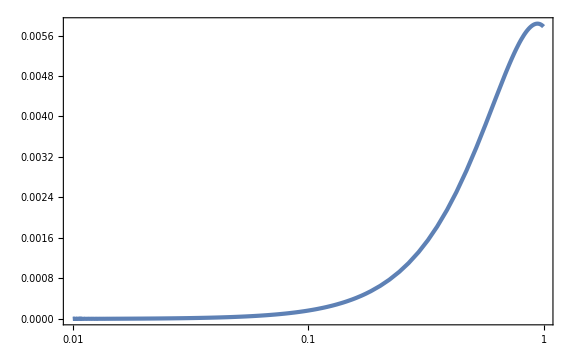

```mathematica
LogLinearPlot[fNL[0.01,xk],{xk,10^-2,1}]
```

```mathematica
Normal[Series[(ζkSR[x0 τe,-xk/τe]ζkUSRs[τe,-xk/τe])/Pζ[x0 τe,-xk/τe],{x0,0,0},{xk,0,4}]]//ExpToTrig//Im//FullSimplify
```

-xk^3/12

```mathematica
Ak=1+I h/(4 k^3 τe^3)(1+k^2 τe^2);
Bk=-I h(1+I k τe)^2 E^(-2I k τe)/(4 k^3 τe^3);
```

```mathematica
ζk[τ_,k_]=Ak H/Sqrt[4ϵ k^3](1+I k τ)E^(-I k τ)+Bk H/Sqrt[4ϵ k^3](1-I k τ)E^(I k τ);
```

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ]]//ExpToTrig//FullSimplify
```

(H ϵ (ⅇ^(-ⅈ k (τ-2 τe)) h (-ⅈ+k τ) (ⅈ+k τe)^2-ⅇ^(ⅈ k τ) (ⅈ+k τ) (h+h k^2 τe^2+4 ⅈ k^3 τe^3)))/(8 (k^3 ϵ)^(3/2) τe^3)

```mathematica
ζksp[τ_,k_]=D[ζks[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k (τ-2 τe)) H τ (4 ⅇ^(2 ⅈ k (τ-τe)) k^3 τe^3+h (1-ⅈ k τe) (ⅈ+k τe+ⅇ^(2 ⅈ k (τ-τe)) (-ⅈ+k τe))))/(8 k^(5/2) √ϵ τe^3)

```mathematica
Pζ[τ_,k_]=ζk[τ,k]ζks[τ,k]//Simplify
```

1/(64 k^9 ϵ τe^6)ⅇ^(-ⅈ k (τ+2 τe)) H^2 (ⅇ^(-ⅈ k (τ-2 τe)) h (-ⅈ+k τ) (ⅈ+k τe)^2-ⅇ^(ⅈ k τ) (ⅈ+k τ) (h+h k^2 τe^2+4 ⅈ k^3 τe^3)) (ⅇ^(2 ⅈ k τ) h (ⅈ+k τ) (-ⅈ+k τe)^2+ⅇ^(2 ⅈ k τe) (1+ⅈ k τ) (4 k^3 τe^3+ⅈ h (1+k^2 τe^2)))

```mathematica
1/(τe^2 H^2)ϵ Normal[Series[(ζk[0,-xp xk/τe] ζk[0,-xk/τe]^2 ζks[τe,-xp xk/τe]ζks[τe,-xk/τe]ζksp[τe,-xk/τe])/(Pζ[0,-xp xk/τe]Pζ[0,-xk/τe]),{xp,0,0},{xk,0,0}]]//Simplify//Im//Simplify
```

(3 (6+h))/(2 (-6+h)^2)

```mathematica
Im
```

## USR2SR num

```mathematica
$Assumptions={ϵ0>0,τ0<0,τe<0,τ<0,lnDt>0};
```

```mathematica
lndt=5;
```

```mathematica
dNs=2 10^-2;
η[τ_]=-6 (1-Tanh[Log[(τ0 10^-lnDt)/τ]/dN])/2//FullSimplify
```

3 (-1+Tanh[Log[(10^-lnDt τ0)/τ]/dN])

```mathematica
ηs[τ_]=η[τ]/.{τ0->-1,lnDt->lndt,dN->dNs}//Simplify
```

3 (-1+Tanh[50 Log[-1/(100000 τ)]])

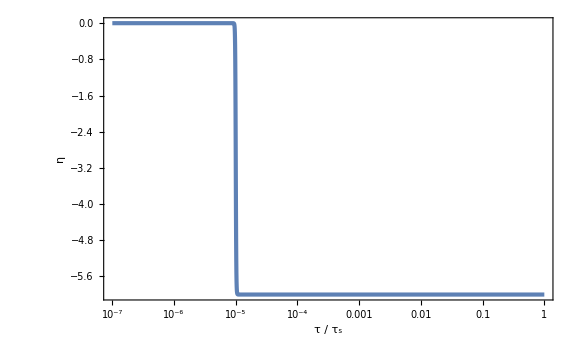

```mathematica
LogLinearPlot[ηs[-x],{x,10^(-2-lndt),1},PlotRange->Full,FrameLabel->{"τ / τ_s",η}]
```

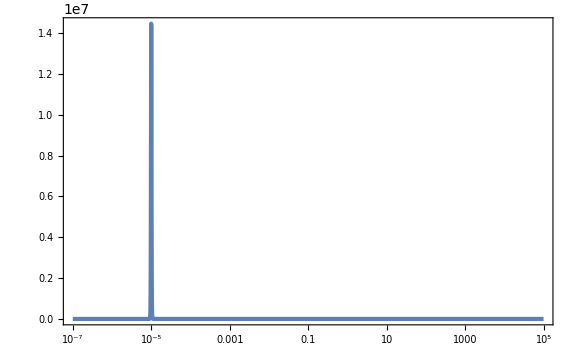

```mathematica
LogLinearPlot[ηs'[-x],{x,10^(-2-lndt),10^5},PlotRange->Full]
```

```mathematica
ηint[τ_]=Integrate[(-η[τ])/τ,τ]//Simplify
```

3 (Log[τ]+dN Log[Cosh[Log[(10^-lnDt τ0)/τ]/dN]])

```mathematica
ϵ[τ_]=ϵ0 Exp[ηint[τ]-ηint[τ0]]/.{τ0->-1,lnDt->lndt,dN->dNs,ϵ0->10^-2}//Simplify
```

-1/100 τ^3 Cosh[50 Log[-1/(100000 τ)]]^(3/50) Sech[50 Log[100000]]^(3/50)

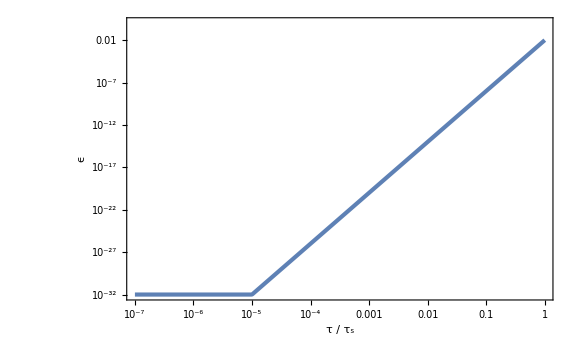

```mathematica
LogLogPlot[ϵ[-x],{x,10^(-2-lndt),1},WorkingPrecision->30,FrameLabel->{"τ / τ_s",ϵ},WorkingPrecision->30]
```

```mathematica
z[τ_]=-1/(τ H)Sqrt[2ϵ[τ]]/.{H->1}//Simplify
```

(√-τ Cosh[50 Log[-1/(100000 τ)]]^(3/100) Sech[50 Log[100000]]^(3/100))/(5 √2)

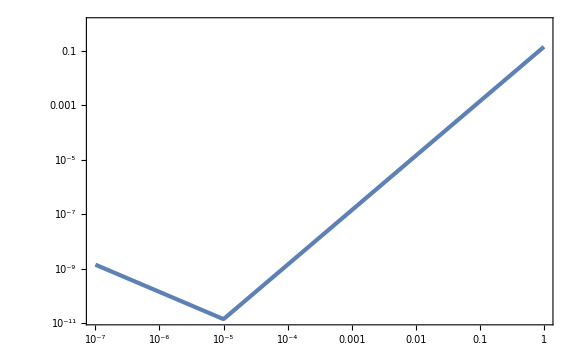

```mathematica
LogLogPlot[z[-x],{x,10^(-2-lndt),1},WorkingPrecision->30]
```

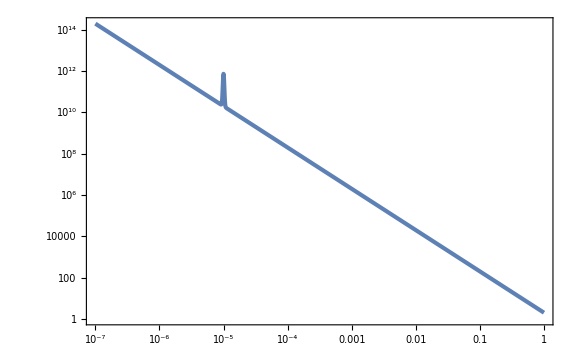

```mathematica
LogLogPlot[Abs[z''[-x]/z[-x]],{x,10^(-2-lndt),1},WorkingPrecision->30]
```

```mathematica
EoM=vk''[τ]+(k^2-z''[τ]/z[τ])vk[τ]==0//Simplify
```

(-299+4 k^2 τ^2+291 Tanh[50 Log[-1/(100000 τ)]]^2) vk[τ]+4 τ^2 vk''[τ]==0

```mathematica
vkform[τ_,k_]=1/Sqrt[2k](1-I/(k τ))E^(-I k τ);
vkformp[τ_,k_]=D[vkform[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) (ⅈ-k τ-ⅈ k^2 τ^2))/(√2 k^(3/2) τ^2)

```mathematica
ζk[τ_,k_]=(I H)/Sqrt[4ϵ0 k^3](τ0/τ)^3(1+I k τ)E^(-I k τ);
```

### kL = 100

```mathematica
kL=100;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==vkform[τ0,k],vk'[τ0]==vkformp[τ0,k]}/.{τ0->-1,k->kL},vk[τ],{τ,-1,-10^(-2-lndt)},WorkingPrecision->30,MaxSteps->10^5][[1]];
```

```mathematica
ζkL[τ_]=vkL[τ]/z[τ];
PζkL[τ_]=Norm[ζkL[τ]]^2;
```

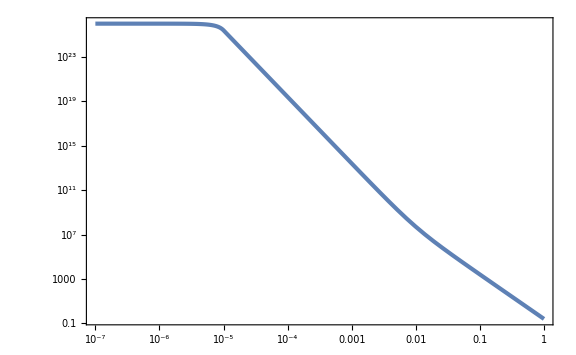

```mathematica
LogLogPlot[ PζkL[-x],{x,10^(-2-lndt),1}]
```

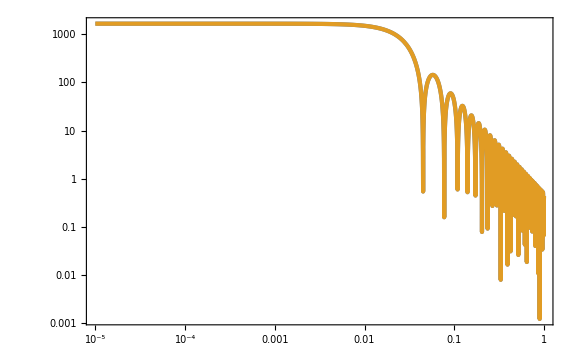

```mathematica
LogLogPlot[{Abs[Re[ζkL[-x]]],Abs[Re[ζk[-x,kL]]]/.{ϵ0->10^-2,τ0->-1,H->1}},{x,10^-lndt,1}]
```

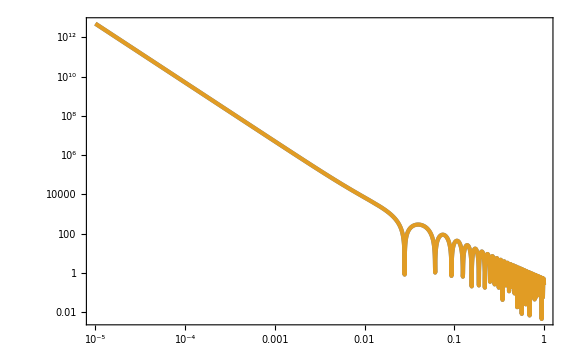

```mathematica
LogLogPlot[{Abs[Im[ζkL[-x]]],Abs[Im[ζk[-x,kL]]]/.{ϵ0->10^-2,τ0->-1,H->1}},{x,10^-lndt,1}]
```

```mathematica
AbsoluteTiming[kS=10^4;
τiS=Min[-10^2/kS,-10^(-lndt+1)];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==vkform[τi,k],vk'[τi]==vkformp[τi,k]}/.{τi->τiS,k->kS},vk[τ],{τ,τiS,-10^(-2-lndt)},WorkingPrecision->30,MaxSteps->10^6][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
fNL=-5/3 1/(PζkL[-10^(-2-lndt)]PζkS[-10^(-2-lndt)])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^(-2-lndt),τp]/.{H->1}],{τp,-10^(-lndt+1),-10^(-lndt-1)}(*,WorkingPrecision->30*),MaxRecursion->12]]
```

{0.326007,-0.00490625}

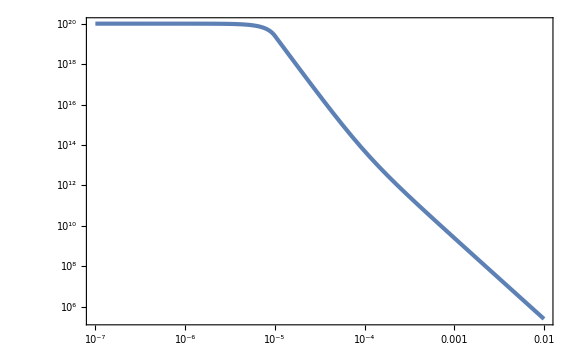

```mathematica
LogLogPlot[ PζkS[-x],{x,10^(-2-lndt),-τiS}]
```

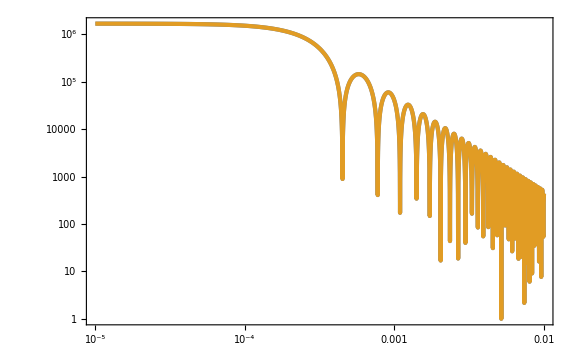

```mathematica
LogLogPlot[{Abs[Re[ζkS[-x]]],Abs[Re[ζk[-x,kS]]]/.{ϵ0->10^-2,τ0->-1,H->1}},{x,10^-lndt,-τiS}]
```

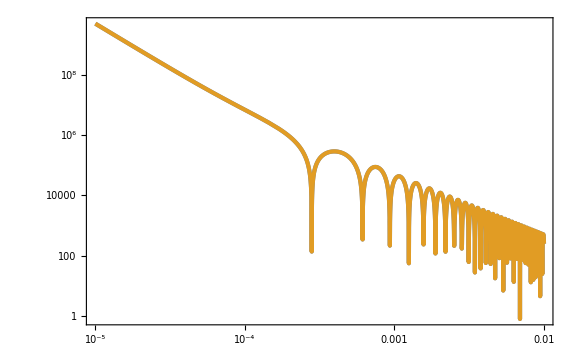

```mathematica
LogLogPlot[{Abs[Im[ζkS[-x]]],Abs[Im[ζk[-x,kS]]]/.{ϵ0->10^-2,τ0->-1,H->1}},{x,10^-lndt,-τiS}]
```

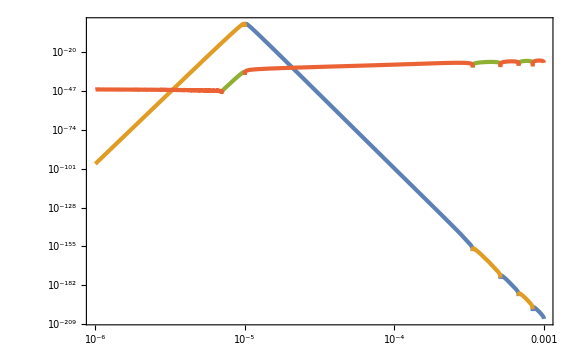

```mathematica
LogLogPlot[{-5/3 x/(PζkL[-10^(-2-lndt)]PζkS[-10^(-2-lndt)])Im[(ϵ[-x]ηs'[-x])/(x^2 H^2)pktk[-10^(-2-lndt),-x]/.{H->1}],+5/3 x/(PζkL[-10^(-2-lndt)]PζkS[-10^(-2-lndt)])Im[(ϵ[-x]ηs'[-x])/(x^2 H^2)pktk[-10^(-2-lndt),-x]/.{H->1}],-5/3 x/(PζkL[-10^(-2-lndt)]PζkS[-10^(-2-lndt)])Im[(2ϵ[-x]ϵ'[-x])/(x^2 H^2)pktk[-10^(-2-lndt),-x]/.{H->1}],+5/3 x/(PζkL[-10^(-2-lndt)]PζkS[-10^(-2-lndt)])Im[(2ϵ[-x]ϵ'[-x])/(x^2 H^2)pktk[-10^(-2-lndt),-x]/.{H->1}]},{x,10^(-1-lndt),10^-3}]
```

```mathematica
calPkfNLList=ParallelTable[kS=10^lnk;
τiS=Min[-10^2/kS,-10^(-lndt+1)];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==vkform[τi,k],vk'[τi]==vkformp[τi,k]}/.{τi->τiS,k->kS},vk[τ],{τ,τiS,-10^(-2-lndt)},WorkingPrecision->30,MaxSteps->10^6][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
fNL=-5/3 1/(PζkL[-10^(-2-lndt)]PζkS[-10^(-2-lndt)])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^(-2-lndt),τp]/.{H->1}],{τp,-10^(-lndt+1),-10^(-lndt-1)},MaxRecursion->12(*,WorkingPrecision->30*)];
{kS,calPζkS[-10^(-2-lndt)],fNL},{lnk,2,6,10^-2}];//AbsoluteTiming
```

{43.577,Null}

```mathematica
calPkList=Map[{#[[1]],#[[2]]}&,calPkfNLList];
fNLList=Map[{#[[1]],#[[3]]}&,calPkfNLList];
calPkint[k_]=Interpolation[calPkList][k];
nsm1[k_]=k D[Log[calPkint[k]], k];
```

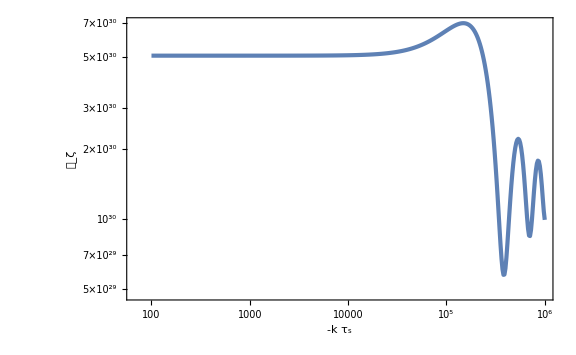

```mathematica
ListLogLogPlot[calPkList,FrameLabel->{-k Subscript[τ, s],Subscript[𝒫, ζ]}]
```

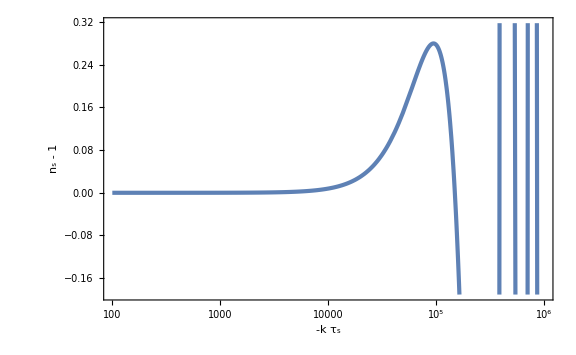

```mathematica
LogLinearPlot[nsm1[k],{k,10^2,10^6},FrameLabel->{-k Subscript[τ, s],"n_s - 1"}]
```

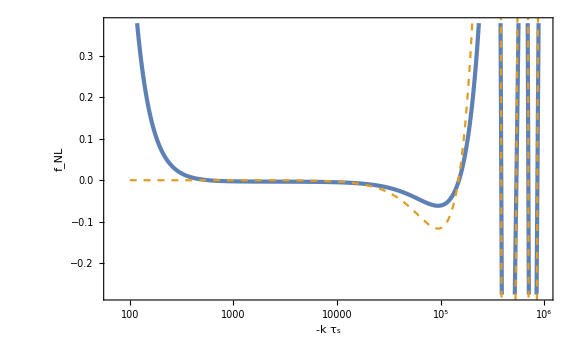

```mathematica
Show[ListLogLinearPlot[fNLList,FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}],LogLinearPlot[-5/12 nsm1[k],{k,10^2,10^6},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```

## USR2SR potential num

```mathematica
V0=2 10^-14;
β=10^-14;
δ1=10^-2;
γ=6 10^-21;
ϕ2=-1580282187/10000000000;
δ2=36/10 10^-8;
```

```mathematica
V[x_]=V0+β/2(x+δ1 Log[Cosh[x/δ1]])+γ/2(x-δ2 Log[Cosh[(ϕ2-x)/δ2]])//Simplify
```

(20000000+5000003 x+50000 Log[Cosh[100 x]]-(27 Log[Cosh[526760729/120+(250000000 x)/9]])/250000000)/1000000000000000000000

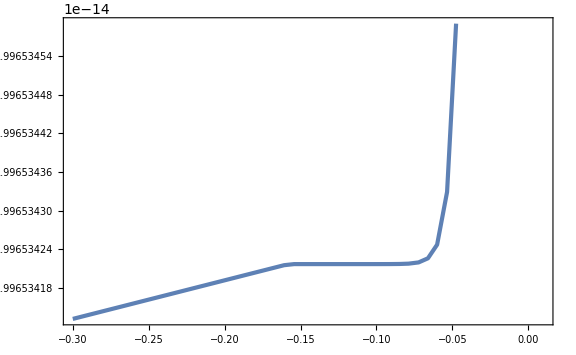

```mathematica
Plot[V[x],{x,-0.3,0.01},WorkingPrecision->30]
```

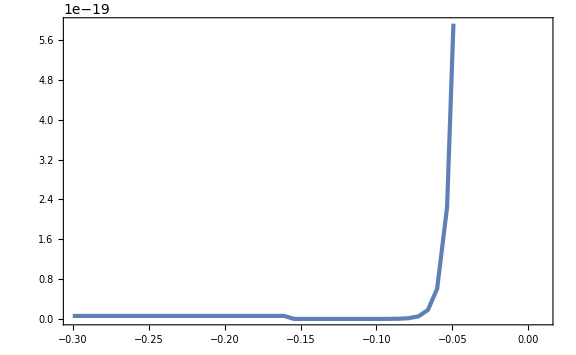

```mathematica
Plot[V'[x],{x,-0.3,0.01},WorkingPrecision->30]
```

```mathematica
H[x_,p_]=Sqrt[(V[x]+p^2/2)/3];
ϵH[x_,p_]=p^2/(2 H[x,p]^2);
ηH[x_,p_]=-2(3+V'[x]/(H[x,p]p)-ϵH[x,p]);
ηp[x_,p_]=-2 V''[x]/H[x,p]-(4ϵH[x,p]-ηH[x,p])V'[x]/p+2ϵH[x,p]ηH[x,p]H[x,p];
```

```mathematica
xi=5;
Hi=H[xi,0];
tf=45 Hi^-1;
```

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==xi,x'[0]==0,
NN'[t]==H[x[t],x'[t]],NN[0]==0,
τ'[t]==1/Exp[NN[t]],τ[tf]==0},{x[t],x'[t],NN[t],τ[t]},{t,0,tf},WorkingPrecision->30][[1]];//AbsoluteTiming
```

{210.908,Null}

```mathematica
xsol[t_]=x[t]/.bgsol;
psol[t_]=x'[t]/.bgsol;
Nsol[t_]=NN[t]/.bgsol;
τsol[t_]=τ[t]/.bgsol;
Hsol[t_]=H[xsol[t],psol[t]];
ϵsol[t_]=ϵH[xsol[t],psol[t]];
ηsol[t_]=ηH[xsol[t],psol[t]];
ηpsol[t_]=ηp[xsol[t],psol[t]];
```

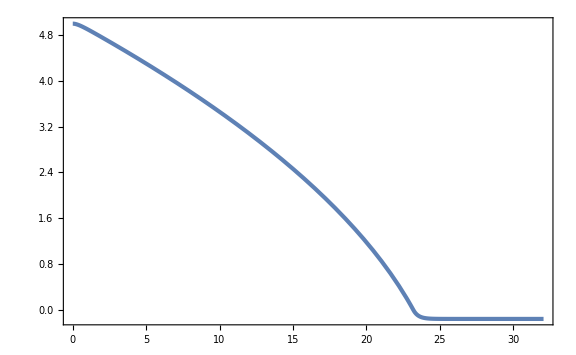

```mathematica
ParametricPlot[{Nsol[t],xsol[t]},{t,0,tf},PlotRange->Full,GridLines->{None,{ϕ2}}]
```

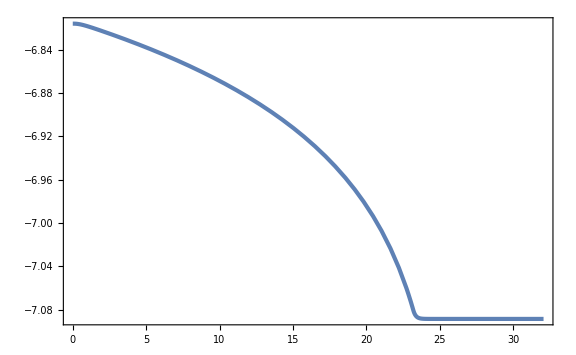

```mathematica
ParametricPlot[{Nsol[t],Log10[Hsol[t]]},{t,0,tf}]
```

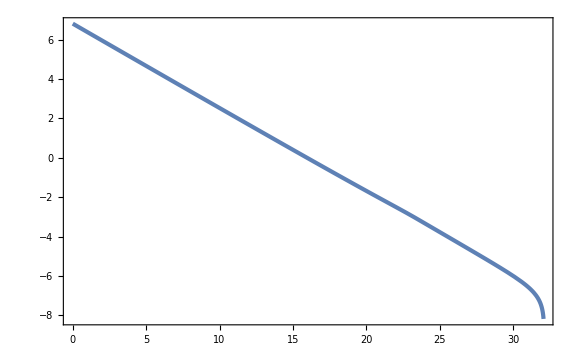

```mathematica
ParametricPlot[{Nsol[t],Log10[-τsol[t]]},{t,0,tf},PlotRange->Full]
```

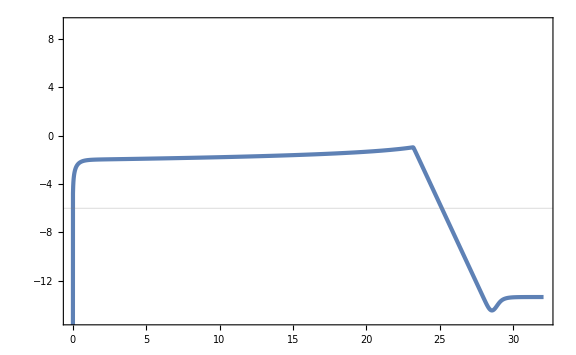

```mathematica
ParametricPlot[{{Nsol[t],Log10[ϵsol[t]]},{Nsol[t],ηsol[t]}},{t,0,tf},GridLines->{None,{-6}}]
```

General::munfl: (1.42494×10^-217)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Sech[1.43279×10^8] is too small to represent as a normalized machine number; precision may be lost.

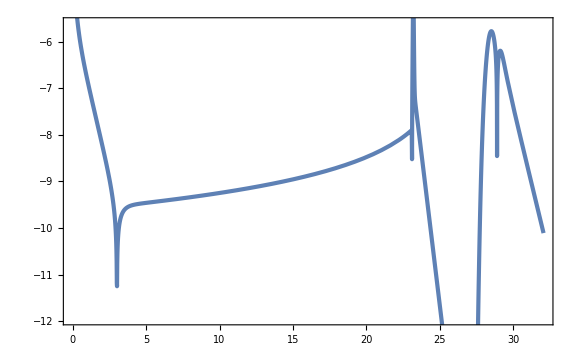

```mathematica
ParametricPlot[{Nsol[t],Log10[Abs[ηpsol[t]]]},{t,0,tf}]
```

```mathematica
Nsol[38 Hi^-1]
```

28.341422038957882138046112991

```mathematica
ts=t/.FindRoot[ηsol[t]==-5,{t,30 Hi^-1},WorkingPrecision->30]
te=t/.FindRoot[ηsol[t]==-5,{t,38 Hi^-1},WorkingPrecision->30]
```

InterpolatingFunction::dmval: Input value {-1.38704452525239079205241710843×10^9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-1.38704452525239079205241710843×10^9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {t} = {-1.38704452525239079205241710843×10^9}.

1.96444738297308055062932775073×10^8

2.47898190160422072372147882578×10^8

```mathematica
ηsol[ts]
ηsol[te]
```

-5.9987097021727055571106

-5.

General::munfl: (1.42494×10^-217)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Sech[1.43279×10^8] is too small to represent as a normalized machine number; precision may be lost.

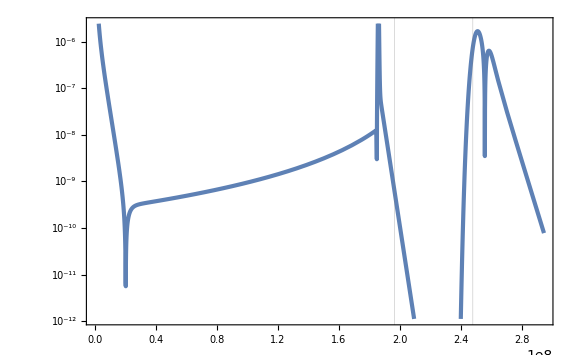

```mathematica
LogPlot[Abs[ηpsol[t]],{t,0,tf},GridLines->{{ts,te},None}]
```

```mathematica
Qkform[t_,k_]=(-Hsol[t] τsol[t])/Sqrt[2k] Exp[-I k τsol[t]];
Qkformp[t_,k_]=D[Qkform[t,k], t];
```

### kL = 10^-5

```mathematica
-10^2/τsol[0]
```

0.000015167030190255163964499857413

```mathematica
kL=2 10^-5;
tiL=t/.FindRoot[τsol[t]==-10^2/kL,{t,Hi^-1},WorkingPrecision->30]
-kL τsol[tiL]
```

InterpolatingFunction::dmval: Input value {-363278.487121285790046302175895} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.8256465059033519273015567131×10^6

100.

```mathematica
QkL[t_]=Qk[t]/.NDSolve[{Qk''[t]+3Hsol[t]Qk'[t]+((k/Exp[Nsol[t]])^2+V''[xsol[t]]+2((V'[xsol[t]]psol[t])/Hsol[t]+ϵsol[t]V[xsol[t]]))Qk[t]==0,Qk[ti]==Qkform[ti,k],Qk'[ti]==Qkformp[ti,k]}/.{ti->tiL,k->kL},Qk[t],{t,tiL,tf},WorkingPrecision->30][[1]];//AbsoluteTiming
```

NDSolve::precw: The precision of the differential equation ({{Qk[t] (Power[«2»]/2500000000+Plus[«2»]/1000000000000000000000+2 Plus[«2»])+√3 √(Times[«2»]+Times[«2»]) Qk'[t]+Qk''[t]==0,Qk[1.8256465059033519273015567131×10^6]==«61»-«60» ⅈ,Qk'[1.8256465059033519273015567131×10^6]==-0.00094067889508988854726760091-«79» ⅈ},«3»,{}}) is less than WorkingPrecision (30.).

{88.3477,Null}

```mathematica
ζkL[t_]=-Hsol[t] QkL[t]/psol[t];
PζkL[t_]=Norm[ζkL[t]]^2;
```

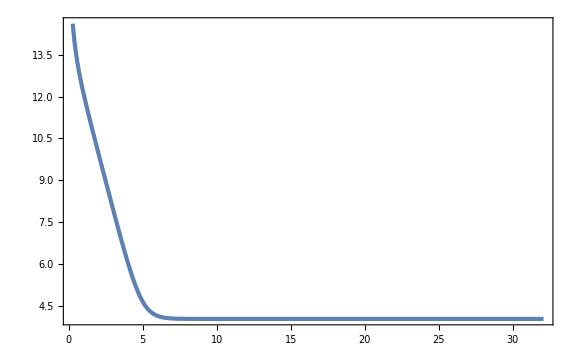

```mathematica
ParametricPlot[{Nsol[t],Log[PζkL[t]]},{t,tiL,tf},PlotRange->Full]
```

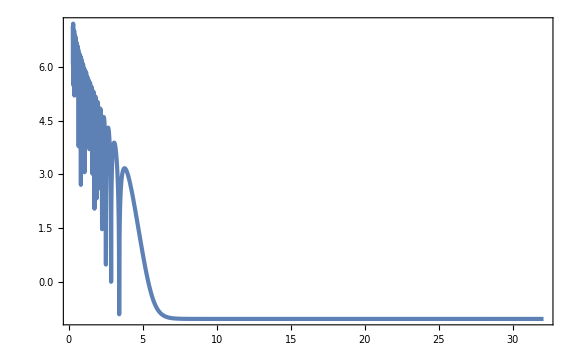

```mathematica
ParametricPlot[{Nsol[t],Log[Abs[Re[ζkL[t]]]]},{t,tiL,tf},PlotRange->Full]
```

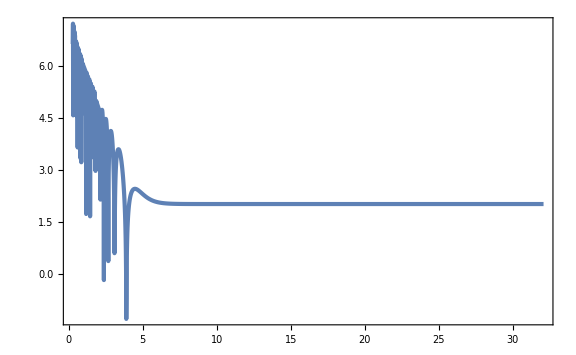

```mathematica
ParametricPlot[{Nsol[t],Log[Abs[Im[ζkL[t]]]]},{t,tiL,tf},PlotRange->Full]
```

```mathematica
AbsoluteTiming[kS=10^4;
tiS=Min[t/.FindRoot[τsol[t]==-10^2/kS,{t,Hi^-1},WorkingPrecision->30]//Quiet,ts-Hsol[ts]^-1];
QkS[t_]=Qk[t]/.NDSolve[{Qk''[t]+3Hsol[t]Qk'[t]+((k/Exp[Nsol[t]])^2+V''[xsol[t]]+2((V'[xsol[t]]psol[t])/Hsol[t]+ϵsol[t]V[xsol[t]]))Qk[t]==0,Qk[ti]==Qkform[ti,k],Qk'[ti]==Qkformp[ti,k]}/.{ti->tiS,k->kS},Qk[t],{t,tiS,tf},WorkingPrecision->30][[1]]//Quiet;
ζkS[t_]=-Hsol[t] QkS[t]/psol[t];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[t_,tp_]=ζkL[t]ζkS[t]ζkS[t]Conjugate[ζkL[tp]]Conjugate[ζkS[tp]]Conjugate[ζkS'[tp]];
{fNLs=-5/3 1/(PζkL[tf]PζkS[tf])NIntegrate[Im[Exp[3Nsol[tp]]ϵsol[tp]ηpsol[tp]pktk[tf,tp]],{tp,ts-Hsol[ts]^-1,ts+Hsol[ts]^-1},WorkingPrecision->30],fNLe=-5/3 1/(PζkL[tf]PζkS[tf])NIntegrate[Im[Exp[3Nsol[tp]]ϵsol[tp]ηpsol[tp]pktk[tf,tp]],{tp,te-Hsol[te]^-1,te+Hsol[te]^-1},WorkingPrecision->30]}]
```

NIntegrate::precw: The precision of the argument function (Im[Divide[(-1.5132905956614173698156571630 <<1>> + <<1>>) <<6>>, <<1>>]]) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tp near {tp} = {1.85959362465320982932826611408×10^8}. NIntegrate obtained -5.41724278858595525287943296059×10^-11 and 1.15822184230989589663789507478×10^-16 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (Im[Divide[(-1.5132905956614173698156571630 <<1>> + <<1>>) <<6>>, <<1>>]]) is less than WorkingPrecision (30.).

{9.65372,{0.74040123873958310307873320467,0.45959434344033845646383911372}}

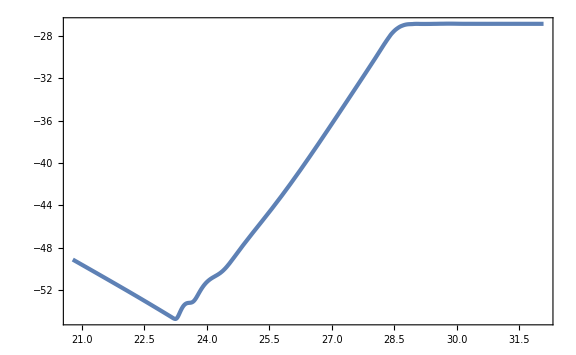

```mathematica
ParametricPlot[{Nsol[t],Log[PζkS[t]]},{t,tiS,tf},PlotRange->Full]
```

General::munfl: Sech[3.03405×10^7] is too small to represent as a normalized machine number; precision may be lost.

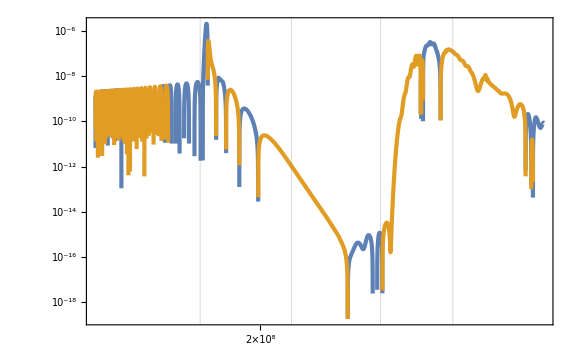

```mathematica
LogLogPlot[{-5/3 1/(PζkL[tf]PζkS[tf])Im[Exp[3Nsol[t]]ϵsol[t]ηpsol[t]pktk[tf,t]],+5/3 1/(PζkL[tf]PζkS[tf])Im[Exp[3Nsol[t]]ϵsol[t]ηpsol[t]pktk[tf,t]]},{t,tiS,tf},GridLines->{{ts-Hsol[ts]^-1,ts+Hsol[ts]^-1,te-Hsol[te]^-1,te+Hsol[te]^-1},None}]
```

```mathematica
calPkfNLList=(*Parallel*)Table[kS=10^lnk;
tiS=Min[t/.FindRoot[τsol[t]==-10^2/kS,{t,10 Hi^-1},WorkingPrecision->30]//Quiet,ts-Hsol[ts]^-1];
QkS[t_]=Qk[t]/.NDSolve[{Qk''[t]+3Hsol[t]Qk'[t]+((k/Exp[Nsol[t]])^2+V''[xsol[t]]+2((V'[xsol[t]]psol[t])/Hsol[t]+ϵsol[t]V[xsol[t]]))Qk[t]==0,Qk[ti]==Qkform[ti,k],Qk'[ti]==Qkformp[ti,k]}/.{ti->tiS,k->kS},Qk[t],{t,tiS,tf},WorkingPrecision->30][[1]]//Quiet;
ζkS[t_]=-Hsol[t] QkS[t]/psol[t];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[t_,tp_]=ζkL[t]ζkS[t]ζkS[t]Conjugate[ζkL[tp]]Conjugate[ζkS[tp]]Conjugate[ζkS'[tp]];
fNLs=-5/3 1/(PζkL[tf]PζkS[tf])NIntegrate[Im[Exp[3Nsol[tp]]ϵsol[tp]ηpsol[tp]pktk[tf,tp]],{tp,ts-Hsol[ts]^-1,ts+Hsol[ts]^-1}]//Quiet;fNLe=-5/3 1/(PζkL[tf]PζkS[tf])NIntegrate[Im[Exp[3Nsol[tp]]ϵsol[tp]ηpsol[tp]pktk[tf,tp]],{tp,te-Hsol[te]^-1,te+Hsol[te]^-1}]//Quiet;
{kS,calPζkS[tf],fNLs,fNLe},{lnk,-5,7(*,10^-2*)}];//AbsoluteTiming
```

{351.397,Null}

```mathematica
calPkList=Map[{#[[1]],#[[2]]}&,calPkfNLList];
fNLsList=Map[{#[[1]],#[[3]]}&,calPkfNLList];
fNLeList=Map[{#[[1]],#[[4]]}&,calPkfNLList];
fNLList=Map[{#[[1]],#[[3]]+#[[4]]}&,calPkfNLList];
calPkint[k_]=Interpolation[calPkList][k];
nsm1[k_]=k D[Log[calPkint[k]], k];
```

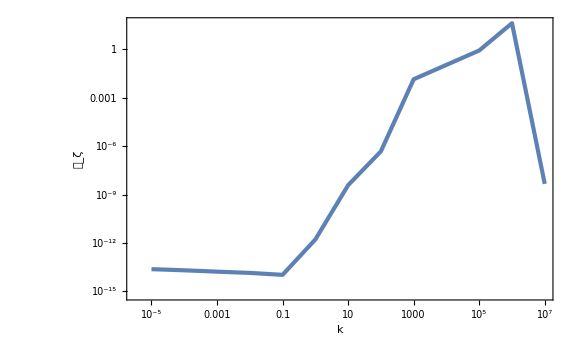

```mathematica
ListLogLogPlot[calPkList,FrameLabel->{k,Subscript[𝒫, ζ]}]
```

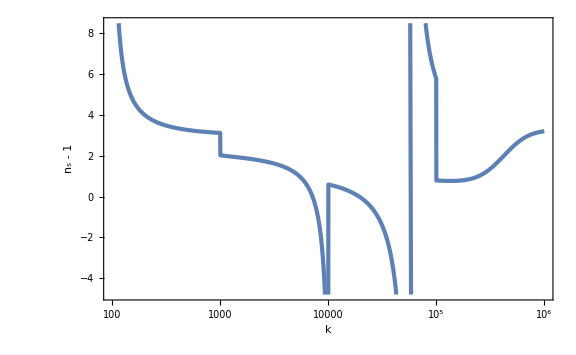

```mathematica
LogLinearPlot[nsm1[k],{k,10^2,10^6},FrameLabel->{k,"n_s - 1"}]
```

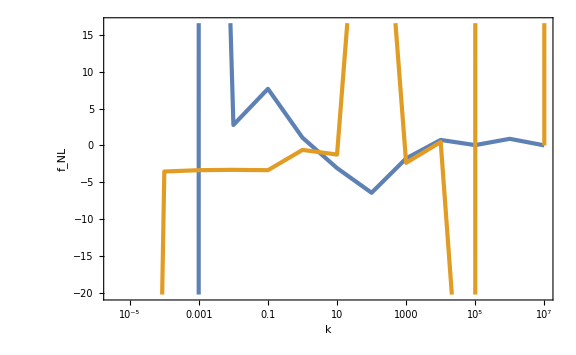

```mathematica
ListLogLinearPlot[{fNLsList,fNLeList},FrameLabel->{k,Subscript[f, NL]}]
```

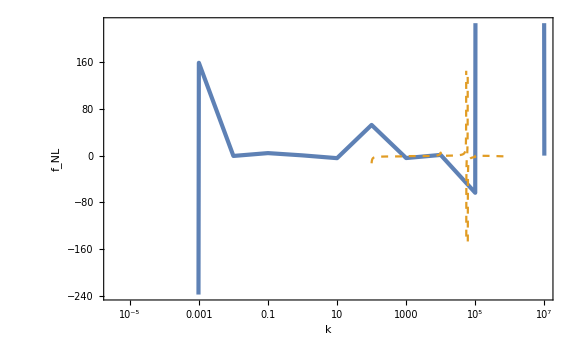

```mathematica
Show[ListLogLinearPlot[fNLList,FrameLabel->{k,Subscript[f, NL]}],LogLinearPlot[-5/12 nsm1[k],{k,10^2,10^6},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```

## SR2USR2SR sharp

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,H>0,k>0,p>0,xe>0};
```

```mathematica
Ak[k_]=1-(3(1+k^2 τs^2))/(2I k^3 τs^3);
Bk[k_]=-(3(1+I k τs)^2)/(2I k^3 τs^3)Exp[-2I k τs];
ζk[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak[k] E^(-I k τ)(1+I k τ)-Bk[k] E^(I k τ)(1-I k τ));
```

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//FullSimplify
```

-(ⅈ H (3 ⅇ^(-ⅈ k (τ-2 τs)) (-ⅈ+k τ) (ⅈ+k τs)^2+ⅇ^(ⅈ k τ) (1-ⅈ k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(4 √(k^9 ϵSR) τ^3)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//Simplify
```

1/(16 k^9 ϵSR τ^6)H^2 (3 ⅇ^(ⅈ k (τ-2 τs)) (ⅈ+k τ) (-ⅈ+k τs)^2+ⅇ^(-ⅈ k τ) (1+ⅈ k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(-ⅈ k (τ-2 τs)) (-ⅈ+k τ) (ⅈ+k τs)^2+ⅇ^(ⅈ k τ) (1-ⅈ k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs)))

```mathematica
PSR[p_]=Normal[Series[Pk[τ,p],{p,0,-3}]]
```

H^2/(4 p^3 ϵSR)

```mathematica
PUSR[x_,k_]=Normal[Series[Pk[x τs,k],{x,0,-6}]]//ExpToTrig//FullSimplify
```

(H^2 (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6+3 (-3+7 k^4 τs^4) Cos[2 k τs]+6 k τs (-3-4 k^2 τs^2+k^4 τs^4) Sin[2 k τs]))/(8 k^9 x^6 ϵSR τs^6)

```mathematica
calPk[τ_,k_]=k^3/(2 π^2)Pk[τ,k];
```

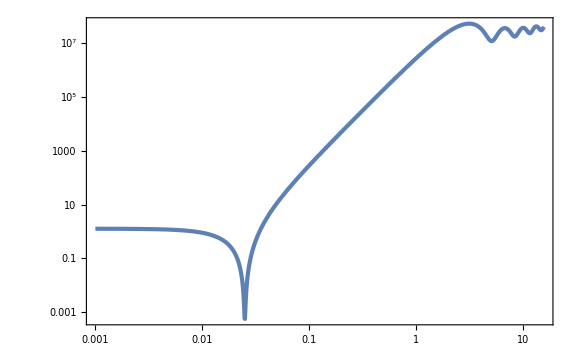

```mathematica
LogLogPlot[calPk[-10^-1.2,k]/.{ϵSR->10^-2,H->1,τs->-1},{k,10^-3,10^1.2}]
```

```mathematica
nsm1[τ_,k_]=k D[Log[calPk[τ,k]], k]//Simplify;
```

```mathematica
nsm1e[k_]=Normal[Series[nsm1[xe τs,k],{xe,0,0}]]//Simplify
```

(6 (9+18 ⅈ k τs-6 k^2 τs^2+12 ⅈ k^3 τs^3-15 k^4 τs^4-8 ⅈ k^5 τs^5+2 k^6 τs^6-6 ⅇ^(2 ⅈ k τs) (3+4 k^2 τs^2+k^4 τs^4)+ⅇ^(4 ⅈ k τs) (9-18 ⅈ k τs-6 k^2 τs^2-12 ⅈ k^3 τs^3-15 k^4 τs^4+8 ⅈ k^5 τs^5+2 k^6 τs^6)))/((3+3 k^2 τs^2+2 ⅈ k^3 τs^3+3 ⅇ^(2 ⅈ k τs) (ⅈ+k τs)^2) (3 (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (3+3 k^2 τs^2-2 ⅈ k^3 τs^3)))

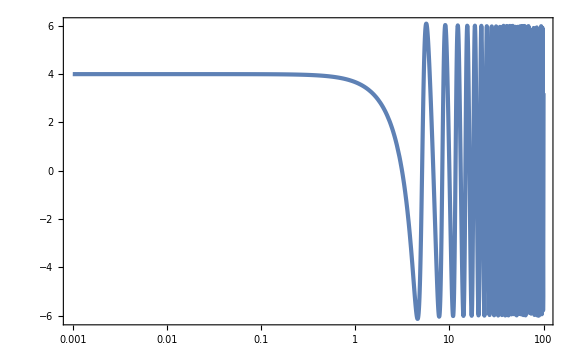

```mathematica
LogLinearPlot[nsm1e[k]/.{τs->-1},{k,10^-3,10^2},WorkingPrecision->30]
```

```mathematica
pktk[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,p]ζks[τp,k]D[ζks[τp,k], τp]//Simplify
```

1/(4096 k^18 p^9 ϵSR^3 τ^9 τp^10)ⅇ^(-ⅈ (2 k+p) (τ+τp)) H^6 (3 (1+ⅈ k τp) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (ⅈ+k τp) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (-3 ⅈ (-3-3 ⅈ k τp+k^2 τp^2) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (-3+3 ⅈ k τp+k^2 τp^2) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (-3 (-ⅈ+p τp) (ⅈ+p τs)^2+ⅇ^(2 ⅈ p (τp-τs)) (ⅈ+p τp) (3+3 p^2 τs^2+2 ⅈ p^3 τs^3)) (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τs)^2+ⅇ^(2 ⅈ p τs) (-ⅈ+p τ) (3 ⅈ+3 ⅈ p^2 τs^2+2 p^3 τs^3))

```mathematica
pktkeim[xe_,p_,k_]=Normal[Series[pktk[xe τs,xe τs,p,k],{p,0,-3},{xe,0,-6}]]//ExpToTrig//Simplify//Im//Simplify
```

1/(128 k^9 p^3 xe^10 ϵSR^3 τs^4)H^6 ((1+k^2 xe^2 τs^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6)+(-9-9 k^2 xe^2 τs^2+3 k^4 (7+4 xe^3) τs^4+k^6 xe^2 (21+16 xe) τs^6-4 k^8 xe^3 τs^8) Cos[2 k τs]+2 k τs (-9-3 k^2 (4+3 xe^2+xe^3) τs^2+3 k^4 (1-4 xe^2) τs^4+k^6 xe^2 (3+7 xe) τs^6) Sin[2 k τs])

```mathematica
Normal[Series[5/12(2/(xe^2 τs^2 H^2)xe^6 ϵSR Δηe pktkeim[xe,p,k]2)/(PSR[p]PUSR[xe,k]),{xe,0,0}]]
```

(5 Δηe)/12

```mathematica
pktksim[xe_,p_,k_]=Normal[Series[pktk[xe τs,τs,p,k],{p,0,-3},{xe,0,-6}]]//ExpToTrig//Expand//Im//FullSimplify
```

1/(128 k^9 p^3 xe^6 ϵSR^3 τs^4)H^6 (3 (3+4 k^2 τs^2+k^4 τs^4)+(-9+6 k^2 τs^2+15 k^4 τs^4-2 k^6 τs^6) Cos[2 k τs]+2 k τs (-9-6 k^2 τs^2+4 k^4 τs^4) Sin[2 k τs])

```mathematica
fNLpktks[x_]=Normal[Series[5/12(2/(τs^2 H^2)ϵSR Δηe pktksim[xe,p,k]2)/(PSR[p]PUSR[xe,k]),{xe,0,0}]]/.{k->x/τs}//Simplify
```

(5 Δηe (3 (3+4 x^2+x^4)+(-9+6 x^2+15 x^4-2 x^6) Cos[2 x]+2 x (-9-6 x^2+4 x^4) Sin[2 x]))/(12 (9+18 x^2+9 x^4+2 x^6+3 (-3+7 x^4) Cos[2 x]+6 x (-3-4 x^2+x^4) Sin[2 x]))

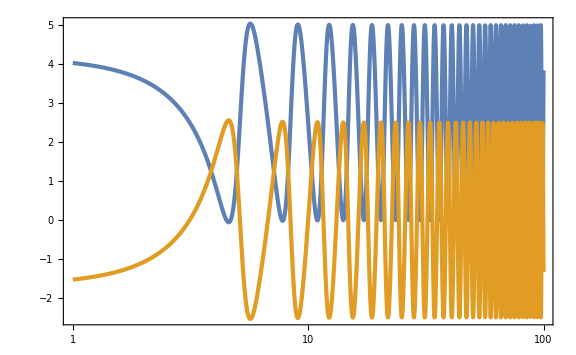

```mathematica
LogLinearPlot[{fNLpktks[x]+5/2/.{Δηe->-6},-5/12 nsm1e[x]/.{τs->-1}},{x,10^0,10^2},WorkingPrecision->30]
```

```mathematica
kktp[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,k]ζks[τp,k]D[ζks[τp,p], τp]//Simplify
```

1/(4096 k^18 p^9 ϵSR^3 τ^9 τp^10)ⅇ^(-ⅈ (2 k+p) (τ+τp)) H^6 (3 (1+ⅈ k τp) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (ⅈ+k τp) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (3 (-3-3 ⅈ p τp+p^2 τp^2) (ⅈ+p τs)^2+ⅇ^(2 ⅈ p (τp-τs)) (-3+3 ⅈ p τp+p^2 τp^2) (3+3 p^2 τs^2+2 ⅈ p^3 τs^3)) (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τs)^2+ⅇ^(2 ⅈ p τs) (-ⅈ+p τ) (3 ⅈ+3 ⅈ p^2 τs^2+2 p^3 τs^3))

```mathematica
kktpeim[xe_,p_,k_]=Normal[Series[kktp[xe τs,xe τs,p,k],{p,0,-3},{x,0,-6}]]//ExpToTrig//Simplify//Im//Simplify
```

0

```mathematica
kktpsim[xe_,p_,k_]=Normal[Series[kktp[xe τs,τs,p,k],{p,0,-3},{x,0,-6}]]//ExpToTrig//Simplify//Im//Simplify
```

0

## SR2USR2SR sharp well after trs.

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,Csc[2k τs]∈Reals,Csc[4k τs]∈Reals};
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ

```mathematica
Normal[Series[ζkSR1[τ,k]Conjugate[ζkSR1[τp,k]]-Conjugate[ζkSR1[τ,k]]ζkSR1[τp,k],{k,0,0}]]
```

-(ⅈ H^2 (τ^3-τp^3))/(6 ϵSR)

```mathematica
Normal[Series[ζkSR1p[τ,k],{k,0,1}]]
```

(ⅈ H √k τ)/(2 √ϵSR)

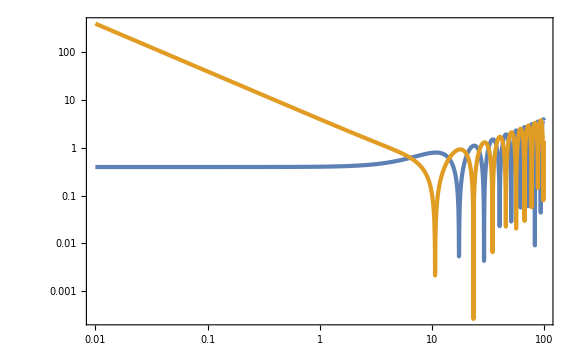

```mathematica
LogLogPlot[{Abs[Re[1/(H^2 x^2)ϵSR^2 ζkSR1[-x,k]^2 ζkSR1p[-x,k]/.{ϵSR->10^-2,τ0->-10^2,k->10^-1,H->1}]],Abs[Im[1/(H^2 x^2)ϵSR^2 ζkSR1[-x,k]^2 ζkSR1p[-x,k]/.{ϵSR->10^-2,τ0->-10^2,k->10^-1,H->1}]]},{x,10^-2,10^2}]
```

```mathematica
ζkUSRform[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak E^(-I k τ)(1+I k τ)-Bk E^(I k τ)(1-I k τ));
ζkUSRformp[τ_,k_]=D[ζkUSRform[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (Bk ⅇ^(2 ⅈ k τ) (3 ⅈ+3 k τ-ⅈ k^2 τ^2)+Ak (-3 ⅈ+3 k τ+ⅈ k^2 τ^2)) τs^3)/(2 √(k^3 ϵSR) τ^4)

```mathematica
SR2USR=Simplify[Solve[{ζkSR1[τs,k]==ζkUSRform[τs,k],ζkSR1p[τs,k]==ζkUSRformp[τs,k]}//Simplify,{Ak,Bk},Assumptions->{ϵSR>0}][[1]],Assumptions->{ϵSR>0}]
```

{Ak→1+(3 ⅈ)/(2 k^3 τs^3)+(3 ⅈ)/(2 k τs),Bk→-(3 ⅈ ⅇ^(-2 ⅈ k τs) (-ⅈ+k τs)^2)/(2 k^3 τs^3)}

```mathematica
ζkUSR[τ_,τs_,k_]=ζkUSRform[τ,k]/.SR2USR//Simplify
ζkUSRp[τ_,τs_,k_]=D[ζkUSR[τ,τs,k], τ]//Simplify
```

(ⅇ^(-ⅈ k (τ+2 τs)) H (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τs)^2-ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^3)

(ⅇ^(-ⅈ k (τ+2 τs)) H (-3 ⅇ^(2 ⅈ k τ) (-3+3 ⅈ k τ+k^2 τ^2) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^4)

```mathematica
ζkSR2form[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^3 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ));
ζkSR2formp[τ_,k_]=D[ζkSR2form[τ,k], τ]//Simplify
```

(ⅈ ⅇ^(-ⅈ k τ) (Ck-Dk ⅇ^(2 ⅈ k τ)) H √(k/ϵSR) τ τs^3)/(2 τe^3)

```mathematica
USR2SR=Solve[{ζkUSR[τe,τs,k]==ζkSR2form[τe,k],ζkUSRp[τe,τs,k]==ζkSR2formp[τe,k]},{Ck,Dk}][[1]]//Simplify
```

{Ck→(ⅇ^(-ⅈ k (τe+4 τs)) √ϵSR (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(11/2) τe^3 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) τs^3),Dk→(ⅇ^(-2 ⅈ k (τe+τs)) (3 ⅇ^(2 ⅈ k τe) (3+3 k^2 τe^2-2 ⅈ k^3 τe^3) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^6 τe^3 τs^3)}

```mathematica
ζk[τ_,τs_,τe_,k_]=ζkSR2form[τ,k]/.USR2SR//Simplify
```

1/(8 k^(15/2) τe^6)ⅈ ⅇ^(-ⅈ k τ) H (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+3 k^2 τe^2-2 ⅈ k^3 τe^3) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(√ϵSR)+1/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe)ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))

```mathematica
ζks[τ_,τs_,τe_,k_]=Conjugate[ζk[τ,τs,τe,k]]//FullSimplify
ζksp[τ_,τs_,τe_,k_]=D[ζks[τ,τs,τe,k], τ]//Simplify
```

-1/(8 k^(15/2) τe^6)ⅈ ⅇ^(ⅈ k τ) H (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+1/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe)ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))

(ⅇ^(ⅈ k τ) H τ (9 ⅈ ⅇ^(-2 ⅈ k (τe-τs)) √(k ϵSR) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+9 ⅇ^(-2 ⅈ k (τe-τs)) k^(3/2) √ϵSR τe (-ⅈ+k τe)^2 (ⅈ+k τs)^2-3 ⅇ^(-2 ⅈ k (τ-τs)) (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (ⅈ+k τs)^2+3 ⅇ^(-2 ⅈ k (τ-τe)) (ⅈ+k τe)^2 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)+ⅈ √(k ϵSR) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs))+k^(3/2) √ϵSR τe (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs))))/(8 k^(11/2) √ϵSR τe^6 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe))

```mathematica
Pk[τ_,τs_,τe_,k_]=ζks[τ,τs,τe,k]ζk[τ,τs,τe,k]//Simplify
```

1/(64 k^15 τe^12)H^2 (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+3 k^2 τe^2-2 ⅈ k^3 τe^3) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(√ϵSR)+1/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe)ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))) (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+1/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe)ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))

```mathematica
PSR[p_]=Normal[Series[Pk[τ,τs,τe,p],{p,0,-3}]]
```

H^2/(4 p^3 ϵSR)

```mathematica
PUSR[xe_,τs_,k_]=Normal[Series[Pk[-xf/k,τs,xe τs,k],{xe,0,-6},{xf,0,0}]]//Simplify//ExpToTrig//FullSimplify
```

(H^2 (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6+3 (-3+7 k^4 τs^4) Cos[2 k τs]+6 k τs (-3-4 k^2 τs^2+k^4 τs^4) Sin[2 k τs]))/(2 k^9 xe^6 ϵSR τs^6)

```mathematica
calPk[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk[τ,τs,τe,k];
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
LogLogPlot[calPk[-10^-2,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30]
```

-Graphics-

```mathematica
nsm1[τ_,τs_,τe_,k_]=k D[Log[calPk[τ,τs,τe,k]], k];
```

```mathematica
nsm1e[x_]=Normal[Series[nsm1[-xf/k,τs,xe τs,-x/τs],{xe,0,0},{xf,0,0}]]//Simplify//ExpToTrig//FullSimplify
```

(6 (-3 (3+4 x^2+x^4)+(9-6 x^2-15 x^4+2 x^6) Cos[2 x]+2 x (9+6 x^2-4 x^4) Sin[2 x]))/(9+18 x^2+9 x^4+2 x^6+3 (-3+7 x^4) Cos[2 x]+6 x (-3-4 x^2+x^4) Sin[2 x])

```mathematica
LogLinearPlot[nsm1e[x],{x,10^-3,10^2},WorkingPrecision->30]
```

-Graphics-

```mathematica
pktk[τ_,τp_,τs_,τe_,p_,k_]=ζk[τ,τs,τe,p] ζk[τ,τs,τe,k]^2 ζks[τp,τs,τe,p]ζks[τp,τs,τe,k]ζksp[τp,τs,τe,k];
```

```mathematica
pktkeim[xe_,p_,k_]=Normal[Series[pktk[-xf/k,xe τs,τs,xe τs,p,k],{p,0,-3},{xe,0,-8},{xf,0,0}]]//Simplify//ExpToTrig//Expand//Im//Simplify
```

(H^6 (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6+3 (-3+7 k^4 τs^4) Cos[2 k τs]+6 k τs (-3-4 k^2 τs^2+k^4 τs^4) Sin[2 k τs]))/(240 k^7 p^3 xe^8 ϵSR^3 τs^2)

```mathematica
fNLpktke=Normal[Series[5/12(2/(xe^2 τs^2 H^2)xe^6 ϵSR Δηe pktkeim[xe,p,k]2)/(PSR[p]PUSR[xe,τs,k]),{xe,0,0}]]//FullSimplify
```

0

```mathematica
pktkeS[xe_,p_,k_]=Normal[Series[pktk[-xf/k,xe τs,τs,xe τs,p,k],{xf,0,0}]];
```

```mathematica
fNLpktkeS=Δηe(Normal[Series[5/12(2/(xe^2 τs^2 H^2)xe^6 ϵSR pktkeS[xe,x k,k]2)/(PUSR[xe,τs,x k]PUSR[xe,τs,k]),{xe,0,0},{x,0,0}]]//Simplify//ExpToTrig//Expand//Im//Simplify)
```

-(125 Δηe (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6+3 (-3+7 k^4 τs^4) Cos[2 k τs]+6 k τs (-3-4 k^2 τs^2+k^4 τs^4) Sin[2 k τs]))/(384 k^10 x τs^10)

```mathematica
pktksim[xe_,p_,k_]=Normal[Series[pktk[-xf/k,τs,τs,xe τs,p,k],{p,0,-3},{xe,0,-6},{xf,0,0}]]//Simplify//ExpToTrig//Expand//Simplify//Expand//Im//Simplify
```

1/(13305600 k^13 p^3 xe^15 ϵSR^3 τs^8)H^6 (-8419950-16839900 k^2 τs^2-10103940 k^2 xe^2 τs^2-6548850 k^4 τs^4-20207880 k^4 xe^2 τs^4-1403325 k^4 xe^3 τs^4-962280 k^4 xe^4 τs^4+623700 k^6 τs^6-7858620 k^6 xe^2 τs^6-3742200 k^6 xe^3 τs^6-1924560 k^6 xe^4 τs^6+944460 k^6 xe^6 τs^6+748440 k^8 xe^2 τs^8-2338875 k^8 xe^3 τs^8-748440 k^8 xe^4 τs^8+1888920 k^8 xe^6 τs^8+74844 k^8 xe^7 τs^8-145800 k^8 xe^8 τs^8+71280 k^10 xe^4 τs^10+1011780 k^10 xe^6 τs^10+199584 k^10 xe^7 τs^10-291600 k^10 xe^8 τs^10-12177 k^10 xe^9 τs^10+299640 k^12 xe^6 τs^12+124740 k^12 xe^7 τs^12-168840 k^12 xe^8 τs^12-32472 k^12 xe^9 τs^12-63120 k^14 xe^8 τs^14-20295 k^14 xe^9 τs^14-2 (-5613300-1122660 k^2 (5+6 xe^2) τs^2-26730 k^4 (-140+252 xe^2-105 xe^3+24 xe^4) τs^4+5940 k^6 (-105+756 xe^2+840 xe^3-108 xe^4+378 xe^5+176 xe^6) τs^6-270 k^8 xe^2 (2772-5775 xe-1584 xe^2-12936 xe^3-3872 xe^4+2178 xe^5+206 xe^6) τs^8-9 k^10 xe^3 (-46200+7920 xe-27720 xe^2+77440 xe^3+105336 xe^4+20040 xe^5+16665 xe^6) τs^10-6 k^12 xe^5 (-27720-19360 xe+21978 xe^2+28470 xe^3+30283 xe^4) τs^12+3 k^14 xe^7 (-18216-6680 xe+28853 xe^2) τs^14+6094 k^16 xe^9 τs^16) Cos[2 k τs]+3 (-935550-374220 k^2 (-5+3 xe^2) τs^2-13365 k^4 (-350-168 xe^2-175 xe^3+8 xe^4) τs^4+1980 k^6 (-315+2835 xe^2+1050 xe^3+108 xe^4+756 xe^5+193 xe^6) τs^6+9 k^8 xe^2 (-83160-259875 xe+59400 xe^2+147840 xe^3-84920 xe^4-46332 xe^5+1280 xe^6) τs^8-9 k^10 xe^4 (7920+166320 xe+212300 xe^2+41184 xe^3+2560 xe^4+18359 xe^5) τs^10-4 k^12 xe^6 (-63690-104247 xe+14400 xe^2+36718 xe^3) τs^12+3 k^14 xe^8 (2560+55077 xe) τs^14) Cos[4 k τs]+16839900 k τs Sin[2 k τs]+26195400 k^3 τs^3 Sin[2 k τs]+20207880 k^3 xe^2 τs^3 Sin[2 k τs]+4677750 k^3 xe^3 τs^3 Sin[2 k τs]+1871100 k^5 τs^5 Sin[2 k τs]+31434480 k^5 xe^2 τs^5 Sin[2 k τs]+7484400 k^5 xe^3 τs^5 Sin[2 k τs]+1924560 k^5 xe^4 τs^5 Sin[2 k τs]+2993760 k^5 xe^5 τs^5 Sin[2 k τs]+1247400 k^7 τs^7 Sin[2 k τs]+2245320 k^7 xe^2 τs^7 Sin[2 k τs]+1559250 k^7 xe^3 τs^7 Sin[2 k τs]+2993760 k^7 xe^4 τs^7 Sin[2 k τs]+2993760 k^7 xe^5 τs^7 Sin[2 k τs]-3136320 k^7 xe^6 τs^7 Sin[2 k τs]-833976 k^7 xe^7 τs^7 Sin[2 k τs]+1496880 k^9 xe^2 τs^9 Sin[2 k τs]+831600 k^9 xe^3 τs^9 Sin[2 k τs]+213840 k^9 xe^4 τs^9 Sin[2 k τs]-1995840 k^9 xe^5 τs^9 Sin[2 k τs]-4878720 k^9 xe^6 τs^9 Sin[2 k τs]-983664 k^9 xe^7 τs^9 Sin[2 k τs]+42120 k^9 xe^8 τs^9 Sin[2 k τs]-122562 k^9 xe^9 τs^9 Sin[2 k τs]+142560 k^11 xe^4 τs^11 Sin[2 k τs]+332640 k^11 xe^5 τs^11 Sin[2 k τs]-348480 k^11 xe^6 τs^11 Sin[2 k τs]+306504 k^11 xe^7 τs^11 Sin[2 k τs]+176400 k^11 xe^8 τs^11 Sin[2 k τs]+109692 k^11 xe^9 τs^11 Sin[2 k τs]-232320 k^13 xe^6 τs^13 Sin[2 k τs]-109296 k^13 xe^7 τs^13 Sin[2 k τs]+226440 k^13 xe^8 τs^13 Sin[2 k τs]+468798 k^13 xe^9 τs^13 Sin[2 k τs]+40080 k^15 xe^8 τs^15 Sin[2 k τs]+12188 k^15 xe^9 τs^15 Sin[2 k τs]-8419950 k τs Sin[4 k τs]-7484400 k^3 τs^3 Sin[4 k τs]-10103940 k^3 xe^2 τs^3 Sin[4 k τs]-2338875 k^3 xe^3 τs^3 Sin[4 k τs]+8419950 k^5 τs^5 Sin[4 k τs]-8981280 k^5 xe^2 τs^5 Sin[4 k τs]+4677750 k^5 xe^3 τs^5 Sin[4 k τs]-962280 k^5 xe^4 τs^5 Sin[4 k τs]-1496880 k^5 xe^5 τs^5 Sin[4 k τs]+10103940 k^7 xe^2 τs^7 Sin[4 k τs]+11694375 k^7 xe^3 τs^7 Sin[4 k τs]-855360 k^7 xe^4 τs^7 Sin[4 k τs]+2993760 k^7 xe^5 τs^7 Sin[4 k τs]+3439260 k^7 xe^6 τs^7 Sin[4 k τs]+416988 k^7 xe^7 τs^7 Sin[4 k τs]-1559250 k^9 xe^3 τs^9 Sin[4 k τs]+962280 k^9 xe^4 τs^9 Sin[4 k τs]+7484400 k^9 xe^5 τs^9 Sin[4 k τs]+3057120 k^9 xe^6 τs^9 Sin[4 k τs]-833976 k^9 xe^7 τs^9 Sin[4 k τs]+103680 k^9 xe^8 τs^9 Sin[4 k τs]+165231 k^9 xe^9 τs^9 Sin[4 k τs]-997920 k^11 xe^5 τs^11 Sin[4 k τs]-3439260 k^11 xe^6 τs^11 Sin[4 k τs]-2084940 k^11 xe^7 τs^11 Sin[4 k τs]+92160 k^11 xe^8 τs^11 Sin[4 k τs]-330462 k^11 xe^9 τs^11 Sin[4 k τs]+277992 k^13 xe^7 τs^13 Sin[4 k τs]-103680 k^13 xe^8 τs^13 Sin[4 k τs]-826155 k^13 xe^9 τs^13 Sin[4 k τs]+110154 k^15 xe^9 τs^15 Sin[4 k τs])

```mathematica
fNLpktks[x_]=Normal[Series[-5/12(2/(τs^2 H^2)ϵSR Δηe pktksim[xe,p,-x/τs]2)/(PSR[p]PUSR[xe,τs,-x/τs]),{xe,0,0}]]//Simplify
```

-((Δηe (-8419950-16839900 x^2-6548850 x^4+623700 x^6-10103940 x^2 xe^2-20207880 x^4 xe^2-7858620 x^6 xe^2+748440 x^8 xe^2-1403325 x^4 xe^3-3742200 x^6 xe^3-2338875 x^8 xe^3-962280 x^4 xe^4-1924560 x^6 xe^4-748440 x^8 xe^4+71280 x^10 xe^4+944460 x^6 xe^6+1888920 x^8 xe^6+1011780 x^10 xe^6+299640 x^12 xe^6+74844 x^8 xe^7+199584 x^10 xe^7+124740 x^12 xe^7-145800 x^8 xe^8-291600 x^10 xe^8-168840 x^12 xe^8-63120 x^14 xe^8-12177 x^10 xe^9-32472 x^12 xe^9-20295 x^14 xe^9-2 (-5613300+6094 x^16 xe^9-1122660 x^2 (5+6 xe^2)+3 x^14 xe^7 (-18216-6680 xe+28853 xe^2)-26730 x^4 (-140+252 xe^2-105 xe^3+24 xe^4)-6 x^12 xe^5 (-27720-19360 xe+21978 xe^2+28470 xe^3+30283 xe^4)+5940 x^6 (-105+756 xe^2+840 xe^3-108 xe^4+378 xe^5+176 xe^6)-270 x^8 xe^2 (2772-5775 xe-1584 xe^2-12936 xe^3-3872 xe^4+2178 xe^5+206 xe^6)-9 x^10 xe^3 (-46200+7920 xe-27720 xe^2+77440 xe^3+105336 xe^4+20040 xe^5+16665 xe^6)) Cos[2 x]+3 (-935550+3 x^14 xe^8 (2560+55077 xe)-374220 x^2 (-5+3 xe^2)-4 x^12 xe^6 (-63690-104247 xe+14400 xe^2+36718 xe^3)-13365 x^4 (-350-168 xe^2-175 xe^3+8 xe^4)-9 x^10 xe^4 (7920+166320 xe+212300 xe^2+41184 xe^3+2560 xe^4+18359 xe^5)+1980 x^6 (-315+2835 xe^2+1050 xe^3+108 xe^4+756 xe^5+193 xe^6)+9 x^8 xe^2 (-83160-259875 xe+59400 xe^2+147840 xe^3-84920 xe^4-46332 xe^5+1280 xe^6)) Cos[4 x]+16839900 x Sin[2 x]+26195400 x^3 Sin[2 x]+1871100 x^5 Sin[2 x]+1247400 x^7 Sin[2 x]+20207880 x^3 xe^2 Sin[2 x]+31434480 x^5 xe^2 Sin[2 x]+2245320 x^7 xe^2 Sin[2 x]+1496880 x^9 xe^2 Sin[2 x]+4677750 x^3 xe^3 Sin[2 x]+7484400 x^5 xe^3 Sin[2 x]+1559250 x^7 xe^3 Sin[2 x]+831600 x^9 xe^3 Sin[2 x]+1924560 x^5 xe^4 Sin[2 x]+2993760 x^7 xe^4 Sin[2 x]+213840 x^9 xe^4 Sin[2 x]+142560 x^11 xe^4 Sin[2 x]+2993760 x^5 xe^5 Sin[2 x]+2993760 x^7 xe^5 Sin[2 x]-1995840 x^9 xe^5 Sin[2 x]+332640 x^11 xe^5 Sin[2 x]-3136320 x^7 xe^6 Sin[2 x]-4878720 x^9 xe^6 Sin[2 x]-348480 x^11 xe^6 Sin[2 x]-232320 x^13 xe^6 Sin[2 x]-833976 x^7 xe^7 Sin[2 x]-983664 x^9 xe^7 Sin[2 x]+306504 x^11 xe^7 Sin[2 x]-109296 x^13 xe^7 Sin[2 x]+42120 x^9 xe^8 Sin[2 x]+176400 x^11 xe^8 Sin[2 x]+226440 x^13 xe^8 Sin[2 x]+40080 x^15 xe^8 Sin[2 x]-122562 x^9 xe^9 Sin[2 x]+109692 x^11 xe^9 Sin[2 x]+468798 x^13 xe^9 Sin[2 x]+12188 x^15 xe^9 Sin[2 x]-8419950 x Sin[4 x]-7484400 x^3 Sin[4 x]+8419950 x^5 Sin[4 x]-10103940 x^3 xe^2 Sin[4 x]-8981280 x^5 xe^2 Sin[4 x]+10103940 x^7 xe^2 Sin[4 x]-2338875 x^3 xe^3 Sin[4 x]+4677750 x^5 xe^3 Sin[4 x]+11694375 x^7 xe^3 Sin[4 x]-1559250 x^9 xe^3 Sin[4 x]-962280 x^5 xe^4 Sin[4 x]-855360 x^7 xe^4 Sin[4 x]+962280 x^9 xe^4 Sin[4 x]-1496880 x^5 xe^5 Sin[4 x]+2993760 x^7 xe^5 Sin[4 x]+7484400 x^9 xe^5 Sin[4 x]-997920 x^11 xe^5 Sin[4 x]+3439260 x^7 xe^6 Sin[4 x]+3057120 x^9 xe^6 Sin[4 x]-3439260 x^11 xe^6 Sin[4 x]+416988 x^7 xe^7 Sin[4 x]-833976 x^9 xe^7 Sin[4 x]-2084940 x^11 xe^7 Sin[4 x]+277992 x^13 xe^7 Sin[4 x]+103680 x^9 xe^8 Sin[4 x]+92160 x^11 xe^8 Sin[4 x]-103680 x^13 xe^8 Sin[4 x]+165231 x^9 xe^9 Sin[4 x]-330462 x^11 xe^9 Sin[4 x]-826155 x^13 xe^9 Sin[4 x]+110154 x^15 xe^9 Sin[4 x]))/(997920 x^4 xe^9 (9+18 x^2+9 x^4+2 x^6+3 (-3+7 x^4) Cos[2 x]+6 x (-3-4 x^2+x^4) Sin[2 x])))

```mathematica
Normal[Series[fNLpktks[x],{xe,0,-9}]]//Simplify
```

-(5 Δηe (x Cos[x]-Sin[x]) Sin[x])/(4 x^4 xe^9)

```mathematica
LogLinearPlot[{fNLpktks[x]/.{Δηe->6,xe->10^-lndt},-5/12 nsm1e[x]},{x,10^-3,10^2},WorkingPrecision->30]
```

-Graphics-

## SR2USR2SR sharp specific value

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,H>0,k>0,p>0,xe>0};
```

```mathematica
Ak[k_]=1-(3(1+k^2 τs^2))/(2I k^3 τs^3);
Bk[k_]=-(3(1+I k τs)^2)/(2I k^3 τs^3)Exp[-2I k τs];
ζk[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak[k] E^(-I k τ)(1+I k τ)-Bk[k] E^(I k τ)(1-I k τ));
```

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//FullSimplify
```

-(ⅈ H (3 ⅇ^(-ⅈ k (τ-2 τs)) (-ⅈ+k τ) (ⅈ+k τs)^2+ⅇ^(ⅈ k τ) (1-ⅈ k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(4 √(k^9 ϵSR) τ^3)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//ExpToTrig//Expand//Simplify
```

1/(8 k^9 ϵSR τ^6)H^2 ((1+k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6)-3 (3-3 k^2 τ (τ-4 τs)+k^4 (16 τ-7 τs) τs^3+k^6 τ (7 τ-4 τs) τs^4) Cos[2 k (τ-τs)]+6 k (3 τs+4 k^2 τs^3-k^4 τs^5+k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)+τ (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)])

```mathematica
calPk[τ_,k_]=k^3/(2 π^2)Pk[τ,k];
```

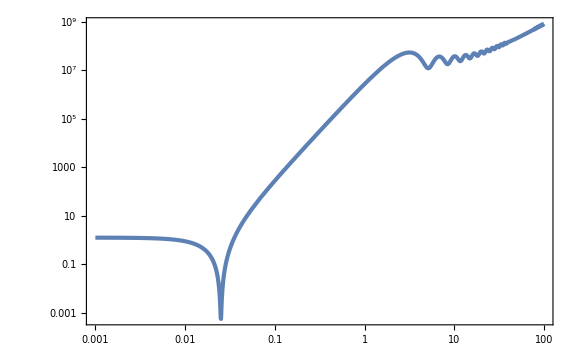

```mathematica
LogLogPlot[calPk[-10^(-12/10),k]/.{ϵSR->10^-2,H->1,τs->-1},{k,10^-3,10^2},WorkingPrecision->30]
```

```mathematica
nsm1[τ_,k_]=k D[Log[calPk[τ,k]], k]//Simplify;
```

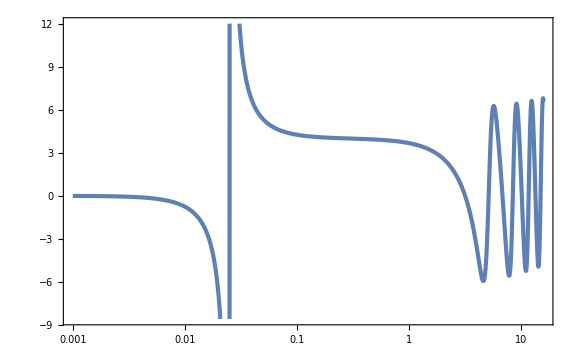

```mathematica
LogLinearPlot[nsm1[-10^(-12/10),k]/.{τs->-1},{k,10^-3,10^(12/10)},WorkingPrecision->30]
```

```mathematica
pktk[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,p]ζks[τp,k]D[ζks[τp,k], τp]//Simplify
```

1/(4096 k^18 p^9 ϵSR^3 τ^9 τp^10)ⅇ^(-ⅈ (2 k+p) (τ+τp)) H^6 (3 (1+ⅈ k τp) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (ⅈ+k τp) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (-3 ⅈ (-3-3 ⅈ k τp+k^2 τp^2) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (-3+3 ⅈ k τp+k^2 τp^2) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (-3 (-ⅈ+p τp) (ⅈ+p τs)^2+ⅇ^(2 ⅈ p (τp-τs)) (ⅈ+p τp) (3+3 p^2 τs^2+2 ⅈ p^3 τs^3)) (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τs)^2+ⅇ^(2 ⅈ p τs) (-ⅈ+p τ) (3 ⅈ+3 ⅈ p^2 τs^2+2 p^3 τs^3))

```mathematica
fNLe[p_,k_]=5/3 1/(xe^2 τs^2 H^2)(xe^6 ϵSR Δηe Im[pktk[xe τs,xe τs,p,k]])/(Pk[xe τs,p]Pk[xe τs,k]);
```

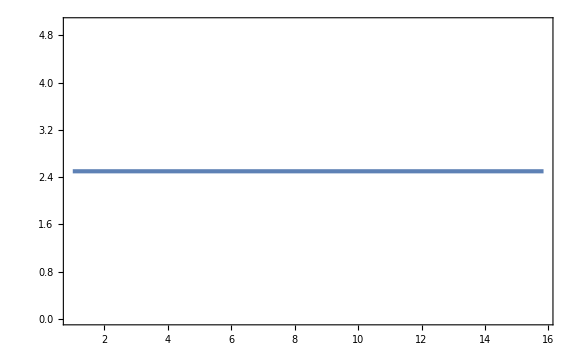

```mathematica
Plot[fNLe[10^-3,k]/.{xe->10^(-12/10),τs->-1,H->1,ϵSR->10^-2,Δηe->6},{k,1,10^(12/10)},WorkingPrecision->30]
```

```mathematica
fNLs[p_,k_]=-5/3 1/(τs^2 H^2)(ϵSR Δηe Im[pktk[xe τs,τs,p,k]])/(Pk[xe τs,p]Pk[xe τs,k]);
```

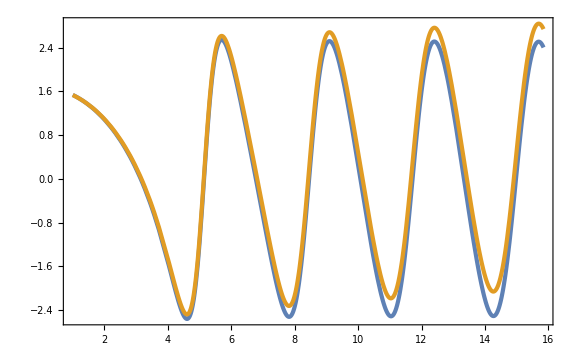

```mathematica
Plot[{fNLs[10^-3,k]/.{xe->10^(-12/10),τs->-1,H->1,ϵSR->10^-2,Δηe->6},5/12 nsm1[-10^(-12/10),k]/.{τs->-1}},{k,1,10^(12/10)},WorkingPrecision->30]
```

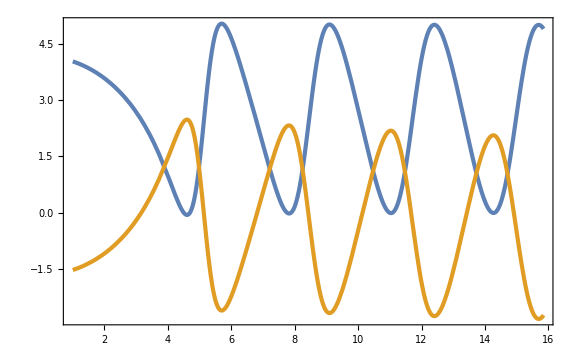

```mathematica
Plot[{fNLe[10^-3,k]+fNLs[10^-3,k]/.{xe->10^(-12/10),τs->-1,H->1,ϵSR->10^-2,Δηe->6},-5/12 nsm1[-10^(-12/10),k]/.{τs->-1}},{k,1,10^(12/10)},WorkingPrecision->30]
```

## SR2USR2SR sharp well after trs. specific value

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0};
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify
```

-(ⅇ^(ⅈ k τ) H (ⅈ+k τ))/(2 √(k^3 ϵSR))

-1/2 ⅈ ⅇ^(ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkUSRform[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak E^(-I k τ)(1+I k τ)-Bk E^(I k τ)(1-I k τ));
ζkUSRformp[τ_,k_]=D[ζkUSRform[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (Bk ⅇ^(2 ⅈ k τ) (3 ⅈ+3 k τ-ⅈ k^2 τ^2)+Ak (-3 ⅈ+3 k τ+ⅈ k^2 τ^2)) τs^3)/(2 √(k^3 ϵSR) τ^4)

```mathematica
SR2USR=Simplify[Solve[{ζkSR1[τs,k]==ζkUSRform[τs,k],ζkSR1p[τs,k]==ζkUSRformp[τs,k]}//Simplify,{Ak,Bk},Assumptions->{ϵSR>0}][[1]],Assumptions->{ϵSR>0}]
```

{Ak→1+(3 ⅈ)/(2 k^3 τs^3)+(3 ⅈ)/(2 k τs),Bk→-(3 ⅈ ⅇ^(-2 ⅈ k τs) (-ⅈ+k τs)^2)/(2 k^3 τs^3)}

```mathematica
SR2USR//FullSimplify//TeXForm
```

\left\{\text{Ak}\to 1+\frac{3 i \left(k^2 \text{$\tau $s}^2+1\right)}{2 k^3 \text{$\tau $s}^3},\text{Bk}\to
   -\frac{3 i e^{-2 i k \text{$\tau $s}} (k \text{$\tau $s}-i)^2}{2 k^3 \text{$\tau $s}^3}\right\}

```mathematica
ζkUSR[τ_,τs_,k_]=ζkUSRform[τ,k]/.SR2USR//Simplify
ζkUSRp[τ_,τs_,k_]=D[ζkUSR[τ,τs,k], τ]//Simplify
```

(ⅇ^(-ⅈ k (τ+2 τs)) H (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τs)^2-ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^3)

(ⅇ^(-ⅈ k (τ+2 τs)) H (-3 ⅇ^(2 ⅈ k τ) (-3+3 ⅈ k τ+k^2 τ^2) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^4)

```mathematica
ζkSR2form[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^3 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ));
ζkSR2formp[τ_,k_]=D[ζkSR2form[τ,k], τ]//Simplify
```

(ⅈ ⅇ^(-ⅈ k τ) (Ck-Dk ⅇ^(2 ⅈ k τ)) H √(k/ϵSR) τ τs^3)/(2 τe^3)

```mathematica
USR2SR=Solve[{ζkUSR[τe,τs,k]==ζkSR2form[τe,k],ζkUSRp[τe,τs,k]==ζkSR2formp[τe,k]},{Ck,Dk}][[1]]//FullSimplify
```

{Ck→(ⅇ^(-ⅈ k (τe+4 τs)) √ϵSR (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ+k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(4 k^(11/2) τe^3 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) τs^3),Dk→(ⅇ^(-2 ⅈ k (τe+τs)) (3 ⅇ^(2 ⅈ k τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(4 k^6 τe^3 τs^3)}

```mathematica
USR2SR//TeXForm
```

\left\{\text{Ck}\to \frac{\sqrt{\text{$\epsilon $SR}} (1+i k \text{$\tau $e}) e^{-i k (\text{$\tau $e}+4
   \text{$\tau $s})} \left(\left(k^2 \text{$\tau $e}^2 (2 k \text{$\tau $e}-3 i)-3 i\right) \left(k^2
   \text{$\tau $s}^2 (2 k \text{$\tau $s}+3 i)+3 i\right) e^{i k (\text{$\tau $e}+4 \text{$\tau $s})}-9 (k
   \text{$\tau $e}+i)^2 (k \text{$\tau $s}-i)^2 e^{i k (3 \text{$\tau $e}+2 \text{$\tau $s})}\right)}{4
   k^{11/2} \text{$\tau $e}^3 \text{$\tau $s}^3 \left(\sqrt{k \text{$\epsilon $SR}}+i \text{$\tau $e} \sqrt{k^3
   \text{$\epsilon $SR}}\right)},\text{Dk}\to \frac{e^{-2 i k (\text{$\tau $e}+\text{$\tau $s})} \left(3 e^{2 i
   k \text{$\tau $e}} \left(3+k^2 \text{$\tau $e}^2 (3-2 i k \text{$\tau $e})\right) (k \text{$\tau $s}-i)^2+3
   i (k \text{$\tau $e}-i)^2 e^{2 i k \text{$\tau $s}} \left(k^2 \text{$\tau $s}^2 (2 k \text{$\tau $s}+3 i)+3
   i\right)\right)}{4 k^6 \text{$\tau $e}^3 \text{$\tau $s}^3}\right\}

```mathematica
ζkSR2[τ_,τs_,τe_,k_]=ζkSR2form[τ,k]/.USR2SR//Simplify
ζkSR2p[τ_,τs_,τe_,k_]=D[ζkSR2[τ,τs,τe,k], τ]//Simplify
```

1/(8 k^(15/2) τe^6)ⅈ ⅇ^(-ⅈ k τ) H (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ+k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe))

(ⅇ^(-ⅈ k τ) H τ (-9 ⅈ ⅇ^(2 ⅈ k (τe-τs)) √(k ϵSR) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+9 ⅇ^(2 ⅈ k (τe-τs)) k^(3/2) √ϵSR τe (ⅈ+k τe)^2 (-ⅈ+k τs)^2-3 ⅈ ⅇ^(2 ⅈ k (τ-τs)) (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+√(k ϵSR) (3+3 k^2 τe^2+2 ⅈ k^3 τe^3) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)+3 ⅇ^(2 ⅈ k (τ-τe)) (-ⅈ+k τe)^2 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))+k^(3/2) √ϵSR τe (3 ⅈ-k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(8 k^(11/2) √ϵSR τe^6 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe))

```mathematica
ζkSR2s[τ_,τs_,τe_,k_]=Conjugate[ζkSR2[τ,τs,τe,k]//ExpToTrig]//FullSimplify
ζkSR2sp[τ_,τs_,τe_,k_]=D[ζkSR2s[τ,τs,τe,k], τ]//Simplify
```

-1/(8 k^(15/2) τe^6)ⅈ ⅇ^(ⅈ k τ) H (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe))

(ⅇ^(ⅈ k τ) H τ (9 ⅈ ⅇ^(-2 ⅈ k (τe-τs)) √(k ϵSR) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+9 ⅇ^(-2 ⅈ k (τe-τs)) k^(3/2) √ϵSR τe (-ⅈ+k τe)^2 (ⅈ+k τs)^2-3 ⅇ^(-2 ⅈ k (τ-τs)) (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (ⅈ+k τs)^2+3 ⅇ^(-2 ⅈ k (τ-τe)) (ⅈ+k τe)^2 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)+ⅈ √(k ϵSR) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs))+k^(3/2) √ϵSR τe (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs))))/(8 k^(11/2) √ϵSR τe^6 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe))

```mathematica
Pk[τ_,τs_,τe_,k_]=ζkSR2s[τ,τs,τe,k]ζkSR2[τ,τs,τe,k]//Simplify
```

1/(64 k^15 τe^12)H^2 (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe)) (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ+k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe))

```mathematica
calPk[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk[τ,τs,τe,k];
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
Hs
```

π/(25000 √10)

```mathematica
lndt//FullSimplify
```

1+Log[5]/(6 Log[10])

```mathematica
-10^-lndt//N
```

-0.0764724

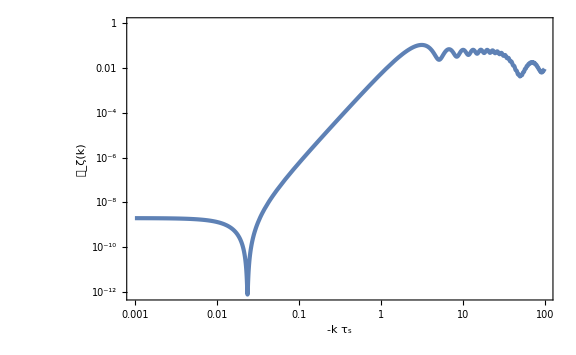

```mathematica
LogLogPlot[calPk[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

```mathematica
nsm1[τ_,τs_,τe_,k_]=k D[Log[calPk[τ,τs,τe,k]], k];
```

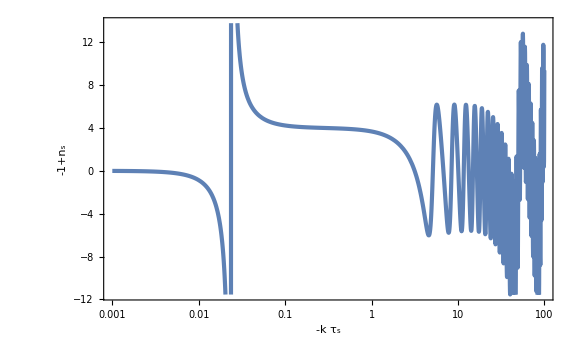

```mathematica
LogLinearPlot[nsm1[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[n, "s"]-1}]
```

```mathematica
pktke[τ_,τs_,τe_,p_,k_]=ζkSR2[τ,τs,τe,p] ζkSR2[τ,τs,τe,k]^2 ζkSR2s[τe,τs,τe,p]ζkSR2s[τe,τs,τe,k]ζkSR2sp[τe,τs,τe,k];
```

```mathematica
fNLpktke[τ_,τs_,τe_,p_,k_]=-Im[5/3(1/(τe^2 H^2)ϵSR (τe/τs)^6 Δηe pktke[τ,τs,τe,p,k])/(Pk[τ,τs,τe,p]Pk[τ,τs,τe,k])];
```

```mathematica
pktks[τ_,τs_,τe_,p_,k_]=ζkSR2[τ,τs,τe,p] ζkSR2[τ,τs,τe,k]^2 ζkSR1s[τs,p]ζkSR1s[τs,k]ζkSR1sp[τs,k];
```

```mathematica
fNLpktks[τ_,τs_,τe_,p_,k_]=-Im[5/3(1/(τs^2 H^2)ϵSR Δηs pktks[τ,τs,τe,p,k])/(Pk[τ,τs,τe,p]Pk[τ,τs,τe,k])];
```

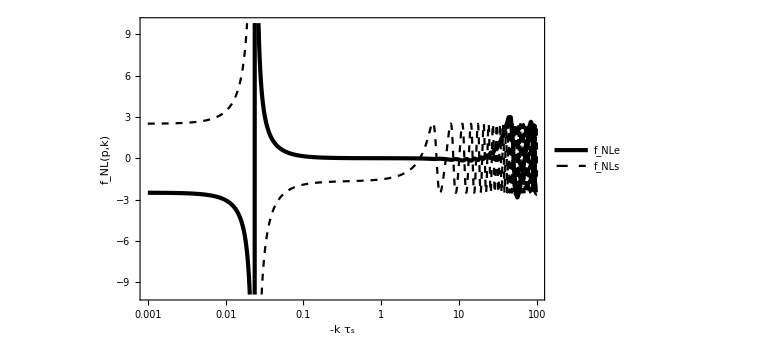

```mathematica
LogLinearPlot[{fNLpktke[0,-1,-10^-lndt,10^-3,k]/.{ϵSR->10^-2,Δηe->6},fNLpktks[0,-1,-10^-lndt,10^-3,k]/.{ϵSR->10^-2,Δηs->-6}},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],p==0.001}},PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NLe],Subscript[f, NLs]},LegendLayout->"Row"],{0.7,0.15}]]
```

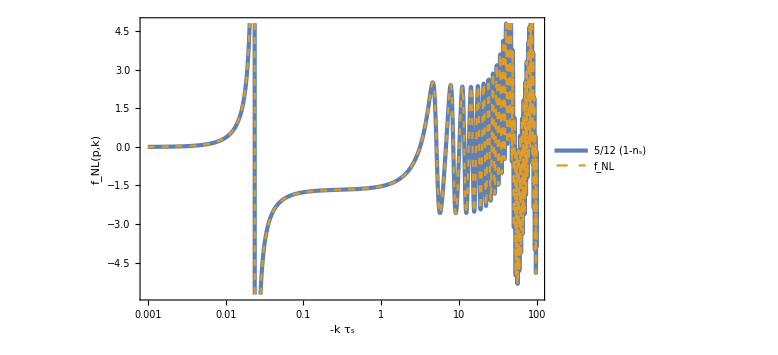

```mathematica
LogLinearPlot[{-5/12 nsm1[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},fNLpktke[0,-1,-10^-lndt,10^-3,k]+fNLpktks[0,-1,-10^-lndt,10^-3,k]/.{ϵSR->10^-2,Δηe->6,Δηs->-6}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],p==0.001}},PlotLegends->Placed[LineLegend[{5/12(1-Subscript[n, "s"]),Subscript[f, NL]},LegendLayout->"Row"],{0.62,0.15}]]
```

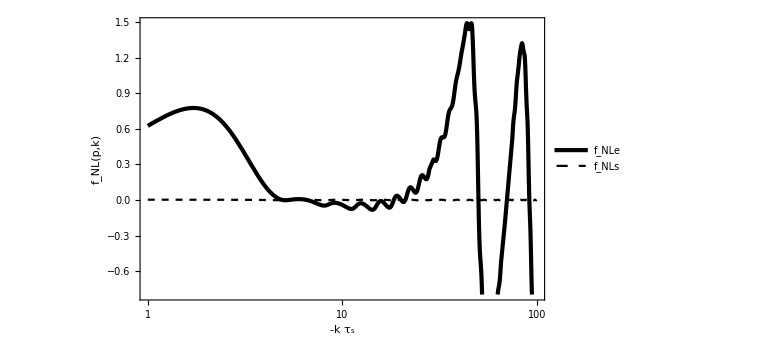

```mathematica
LogLinearPlot[{fNLpktke[0,-1,-10^-lndt,1,k]/.{ϵSR->10^-2,Δηe->6},fNLpktks[0,-1,-10^-lndt,1,k]/.{ϵSR->10^-2,Δηs->-6}},{k,1,10^2},WorkingPrecision->30,FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],p==1}},PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NLe],Subscript[f, NLs]},LegendLayout->"Row"],{0.3,0.15}],GridLines->{{1/10^-lndt},None}]
```

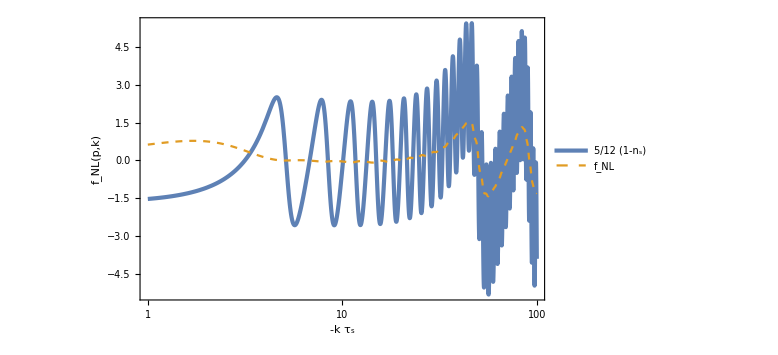

```mathematica
LogLinearPlot[{-5/12 nsm1[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},fNLpktke[0,-1,-10^-lndt,1,k]+fNLpktks[0,-1,-10^-lndt,1,k]/.{ϵSR->10^-2,Δηe->6,Δηs->-6}},{k,1,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],p==1}},PlotLegends->Placed[LineLegend[{5/12(1-Subscript[n, "s"]),Subscript[f, NL]},LegendLayout->"Row"],{0.35,0.15}]]
```

## SR2USR

```mathematica
$Assumptions={ϵ0>0,τ0<0,τs<0,τ<0};
```

```mathematica
η[τ_]=-6 (1-Tanh[Log[τ/τs]/(5 10^-2)])/2//Simplify
```

3 (-1+Tanh[20 Log[τ/τs]])

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];lndt//N
```

1.1165

```mathematica
Log10[(10^-2/(2 10^-9))^(1/4)]//N
```

1.67474

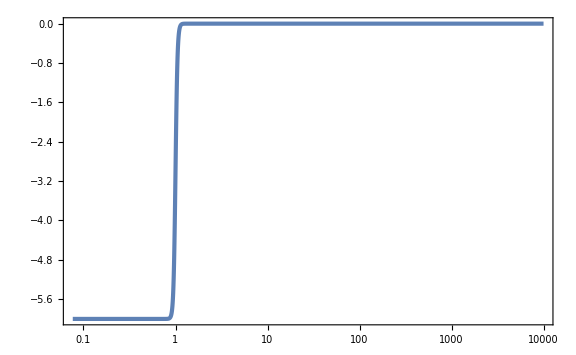

```mathematica
LogLinearPlot[η[-x]/.{τs->-1},{x,10^-lndt,10^4}]
```

```mathematica
ηint[τ_]=Integrate[-η[τ]/τ,τ]//Simplify
```

6 Log[τ]-3/20 Log[τ^40+τs^40]

```mathematica
ϵ[τ_]=ϵ0 Exp[ηint[τ]-ηint[τ0]]//Simplify
```

(ϵ0 τ^6 ((τ0^40+τs^40)/(τ^40+τs^40))^(3/20))/τ0^6

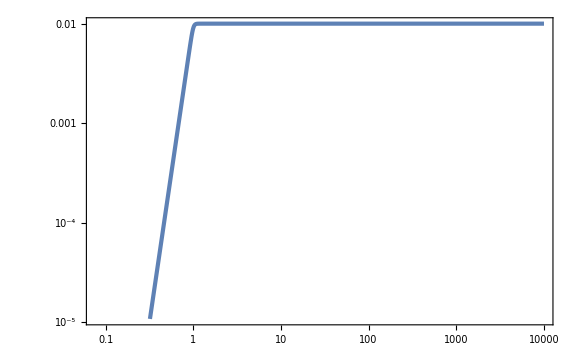

```mathematica
LogLogPlot[ϵ[-x]/.{τs->-1,τ0->-10^4,ϵ0->10^-2},{x,10^-lndt,10^4}]
```

```mathematica
z[τ_]=-1/(τ H)Sqrt[2ϵ[τ]]/.{H->1}//Simplify
```

-(√2 √ϵ0 τ^2 ((τ0^40+τs^40)/(τ^40+τs^40))^(3/40))/τ0^3

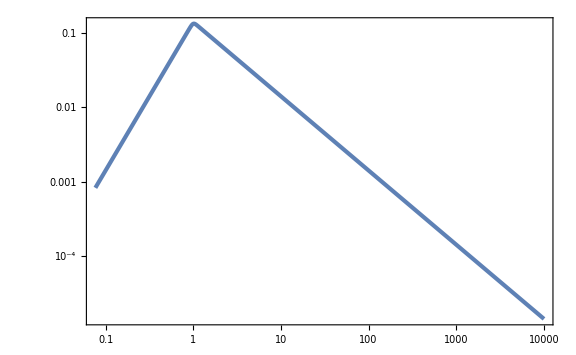

```mathematica
LogLogPlot[z[-x]/.{τs->-1,τ0->-10^4,ϵ0->10^-2},{x,10^-lndt,10^4}]
```

```mathematica
EoM=vk''[τ]+(k^2-z''[τ]/z[τ])vk[τ]==0//Simplify
```

((-2 τ^80+k^2 τ^82+125 τ^40 τs^40+2 k^2 τ^42 τs^40-2 τs^80+k^2 τ^2 τs^80) vk[τ])/(τ^2 (τ^40+τs^40)^2)+vk''[τ]==0

```mathematica
kL=3 10^-3;
kS=8.5;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->-10^4,k->kL},vk[τ],{τ,-10^4,-10^-lndt}(*,WorkingPrecision->30,MaxSteps->10^6*)][[1]];//AbsoluteTiming
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->-10,k->kS},vk[τ],{τ,-10,-10^-lndt}(*,WorkingPrecision->20,MaxSteps->10^5*)][[1]];//AbsoluteTiming
```

{0.006995,Null}

{0.003034,Null}

```mathematica
ζkL[τ_]=vkL[τ]/z[τ]/.{τs->-1,τ0->-10^4,ϵ0->10^-2};
ζkS[τ_]=vkS[τ]/z[τ]/.{τs->-1,τ0->-10,ϵ0->10^-2};
PζkL[τ_]=Norm[ζkL[τ]]^2;
PζkS[τ_]=Norm[ζkS[τ]]^2;
```

```mathematica
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
```

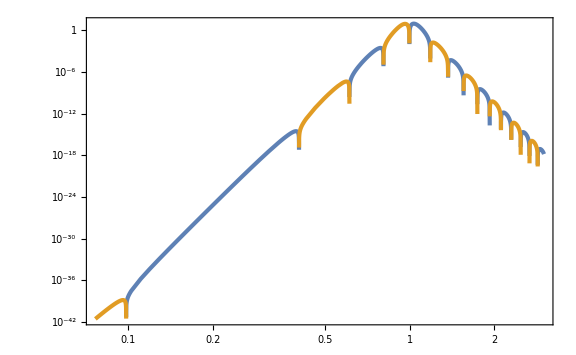

```mathematica
LogLogPlot[{5/12 1/(PζkL[-10^-lndt]PζkS[-10^-lndt])2Im[2/τp^2(ϵ[-τp]η'[-τp]/.{τs->-1,τ0->-10^4,ϵ0->10^-2})pktk[-10^-lndt,-τp]],-5/12 1/(PζkL[-10^-lndt]PζkS[-10^-lndt])2Im[2/τp^2(ϵ[-τp]η'[-τp]/.{τs->-1,τ0->-10^4,ϵ0->10^-2})pktk[-10^-lndt,-τp]]},{τp,10^-lndt,3}]
```

```mathematica
5/12 1/(PζkL[-10^-lndt]PζkS[-10^-lndt])2NIntegrate[Im[2/τp^2(ϵ[τp]η'[τp]/.{τs->-1,τ0->-10^4,ϵ0->10^-2})pktk[-10^-lndt,τp]],{τp,-10,-10^-lndt}]
```

0.0775123

## SR2USR sharp well after trs. specific value

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,η<0};
```

```mathematica
ζkSR[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSRp[τ_,k_]=D[ζkSR[τ,k], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkSRs[τ_,k_]=Conjugate[ζkSR[τ,k]]//Simplify
ζkSRsp[τ_,k_]=D[ζkSRs[τ,k], τ]//Simplify
```

-(ⅇ^(ⅈ k τ) H (ⅈ+k τ))/(2 √(k^3 ϵSR))

-1/2 ⅈ ⅇ^(ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkUSRform[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak E^(-I k τ)(1+I k τ)-Bk E^(I k τ)(1-I k τ));
ζkUSRformp[τ_,k_]=D[ζkUSRform[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (Bk ⅇ^(2 ⅈ k τ) (3 ⅈ+3 k τ-ⅈ k^2 τ^2)+Ak (-3 ⅈ+3 k τ+ⅈ k^2 τ^2)) τs^3)/(2 √(k^3 ϵSR) τ^4)

```mathematica
SR2USR=Simplify[Solve[{ζkSR[τs,k]==ζkUSRform[τs,k],ζkSRp[τs,k]==ζkUSRformp[τs,k]}//Simplify,{Ak,Bk},Assumptions->{ϵSR>0}][[1]],Assumptions->{ϵSR>0}]
```

{Ak→1+(3 ⅈ)/(2 k^3 τs^3)+(3 ⅈ)/(2 k τs),Bk→-(3 ⅈ ⅇ^(-2 ⅈ k τs) (-ⅈ+k τs)^2)/(2 k^3 τs^3)}

```mathematica
SR2USR//FullSimplify//TeXForm
```

\left\{\text{Ak}\to 1+\frac{3 i \left(k^2 \text{$\tau $s}^2+1\right)}{2 k^3 \text{$\tau $s}^3},\text{Bk}\to
   -\frac{3 i e^{-2 i k \text{$\tau $s}} (k \text{$\tau $s}-i)^2}{2 k^3 \text{$\tau $s}^3}\right\}

```mathematica
ζkUSR[τ_,τs_,k_]=ζkUSRform[τ,k]/.SR2USR//Simplify
ζkUSRp[τ_,τs_,k_]=D[ζkUSR[τ,τs,k], τ]//Simplify
```

(ⅇ^(-ⅈ k (τ+2 τs)) H (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τs)^2-ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^3)

(ⅇ^(-ⅈ k (τ+2 τs)) H (-3 ⅇ^(2 ⅈ k τ) (-3+3 ⅈ k τ+k^2 τ^2) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^4)

```mathematica
ζkUSRs[τ_,τs_,k_]=Conjugate[ζkUSR[τ,τs,k]]//ExpToTrig//FullSimplify
ζkUSRps[τ_,τs_,k_]=D[ζkUSRs[τ,τs,k], τ]//Simplify
```

(ⅇ^(ⅈ k (τ+2 τs)) H (-3 ⅈ ⅇ^(-2 ⅈ k τ) (-ⅈ+k τ) (ⅈ+k τs)^2-ⅇ^(-2 ⅈ k τs) (ⅈ+k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(4 √(k^9 ϵSR) τ^3)

(ⅇ^(-ⅈ k τ) H (-3 ⅇ^(2 ⅈ k τs) (-3-3 ⅈ k τ+k^2 τ^2) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k τ) (3 ⅈ+3 k τ-ⅈ k^2 τ^2) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 √(k^9 ϵSR) τ^4)

```mathematica
Pk[τ_,τs_,k_]=ζkUSRs[τ,τs,k]ζkUSR[τ,τs,k]//Simplify
```

1/(16 k^9 ϵSR τ^6)H^2 (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τs)^2-ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)) (-3 ⅈ ⅇ^(-2 ⅈ k τ) (-ⅈ+k τ) (ⅈ+k τs)^2-ⅇ^(-2 ⅈ k τs) (ⅈ+k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs)))

```mathematica
calPk[τ_,τs_,k_]=k^3/(2 π^2)Pk[τ,τs,k];
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
Hs
```

π/(25000 √10)

```mathematica
lndt//FullSimplify
```

1+Log[5]/(6 Log[10])

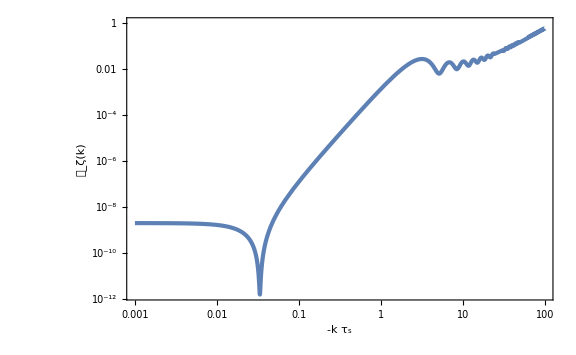

```mathematica
LogLogPlot[calPk[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

```mathematica
nsm1[τ_,τs_,k_]=k D[Log[calPk[τ,τs,k]], k];
```

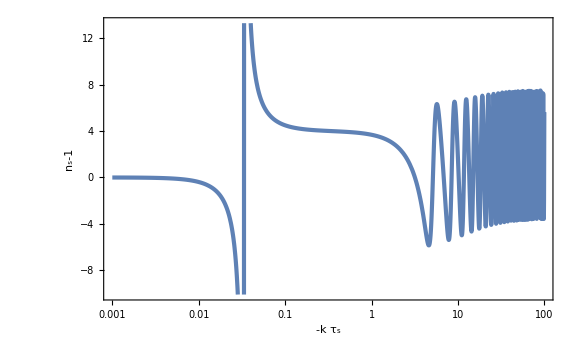

```mathematica
LogLinearPlot[nsm1[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Row[{Subscript[n, "s"],-1}]}]
```

```mathematica
pktks[τ_,τs_,p_,k_]=ζkUSR[τ,τs,p] ζkUSR[τ,τs,k]^2 ζkUSRs[τs,τs,p]ζkUSRs[τs,τs,k]ζkUSRps[τs,τs,k];
```

```mathematica
fNLpktks[τ_,τs_,p_,k_]=-Im[5/3(1/(τs^2 H^2)ϵSR Δηs pktks[τ,τs,p,k])/(Pk[τ,τs,p]Pk[τ,τs,k])];
```

```mathematica
ktkI[τ_,τs_,k_]=ζkUSR[τ,τs,k]ζkUSRps[τ,τs,k]//ExpToTrig//Expand//Im//Simplify
ktkR[τ_,τs_,k_]=ζkUSR[τ,τs,k]ζkUSRps[τ,τs,k]//ExpToTrig//Expand//Re//Simplify
```

(H^2 τs^6)/(4 ϵSR τ^4)

1/(8 k^9 ϵSR τ^7)H^2 (-((3+2 k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6))+3 (9-12 k^2 τ (τ-3 τs)+2 k^8 τ^3 τs^5-4 k^6 τ τs^3 (2 τ^2-7 τ τs+3 τs^2)-3 k^4 (2 τ^3 τs-16 τ τs^3+7 τs^4)) Cos[2 k (τ-τs)]+3 k (6 τs (-3-4 k^2 τs^2+k^4 τs^4)-8 k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)-6 τ (-3+7 k^4 τs^4)+k^2 τ^3 (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)])

```mathematica
fNLpktkη[τ_,τs_,p_,k_]=5/3 1/(τ^2 H^2)ϵSR(τ/τs)^6 η ktkI[τ,τs,k]//Simplify
```

(5 η)/12

```mathematica
fNLpktkH[τ_,τs_,p_,k_]=-5/3 1/(τ H^2)ϵSR(τ/τs)^6 (2ktkI[τ,τs,k]ktkR[τ,τs,k])/Pk[τ,τs,k]//Simplify
```

(5 (-((3+2 k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6))+3 (9-12 k^2 τ (τ-3 τs)+2 k^8 τ^3 τs^5-4 k^6 τ τs^3 (2 τ^2-7 τ τs+3 τs^2)-3 k^4 (2 τ^3 τs-16 τ τs^3+7 τs^4)) Cos[2 k (τ-τs)]+3 k (6 τs (-3-4 k^2 τs^2+k^4 τs^4)-8 k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)-6 τ (-3+7 k^4 τs^4)+k^2 τ^3 (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)]))/(3 (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τs)^2-ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(-2 ⅈ k τ) (1+ⅈ k τ) (ⅈ+k τs)^2+ⅇ^(-2 ⅈ k τs) (ⅈ+k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))

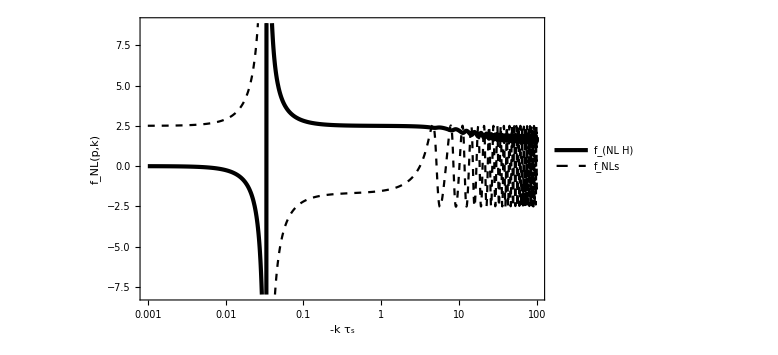

```mathematica
LogLinearPlot[{fNLpktkH[-10^-lndt,-1,10^-3,k]/.{H->Hs},fNLpktks[-10^-lndt,-1,10^-3,k]/.{Δηs->-6}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}},GridLines->{None,{-5/2}},FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],Row[{p==0.001,", ",τ==Subscript[τ, "e"]}]}},PlotLegends->Placed[LineLegend[{Subscript[f, Row[{NL," ",H}]],Subscript[f, NLs]},LegendLayout->"Row"],{0.7,0.15}]]
```

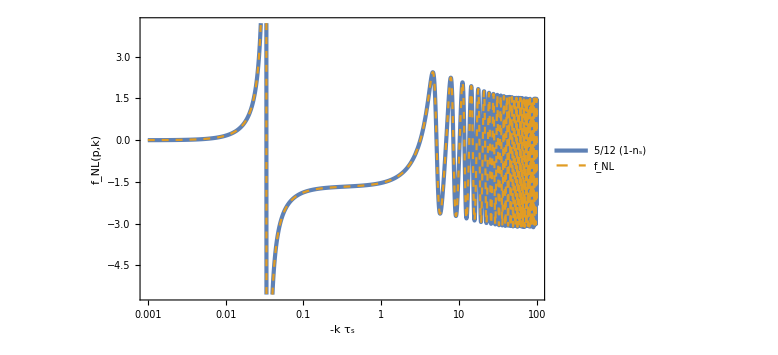

```mathematica
LogLinearPlot[{-5/12 nsm1[-10^-lndt,-1,k]/.{H->Hs},fNLpktks[-10^-lndt,-1,10^-3,k]+fNLpktkη[-10^-lndt,-1,10^-3,k]+fNLpktkH[-10^-lndt,-1,10^-3,k]/.{Δηs->-6,η->-6,H->Hs}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],Row[{p==0.001,", ",τ==Subscript[τ, "e"]}]}},PlotLegends->Placed[LineLegend[{5/12(1-Subscript[n, "s"]),Subscript[f, NL]},LegendLayout->"Row"],{0.67,0.15}]]
```

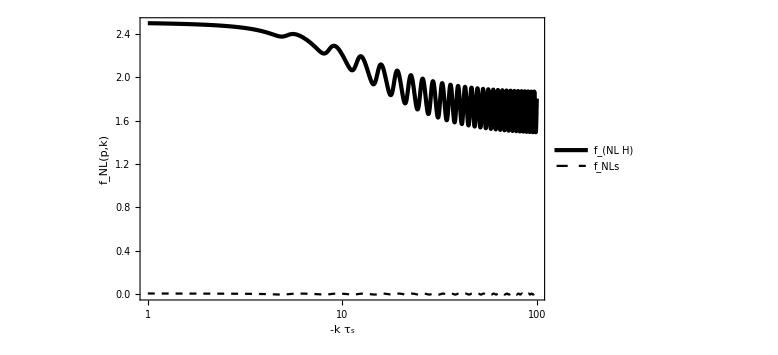

```mathematica
LogLinearPlot[{fNLpktkH[-10^-lndt,-1,1,k]/.{H->Hs},fNLpktks[-10^-lndt,-1,1,k]/.{Δηs->-6}},{k,1,10^2},WorkingPrecision->30,PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}},GridLines->{None,{-5/2}},FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],Row[{p==1,", ",τ==Subscript[τ, "e"]}]}},PlotLegends->Placed[LineLegend[{Subscript[f, Row[{NL," ",H}]],Subscript[f, NLs]},LegendLayout->"Row"],{0.7,0.15}]]
```

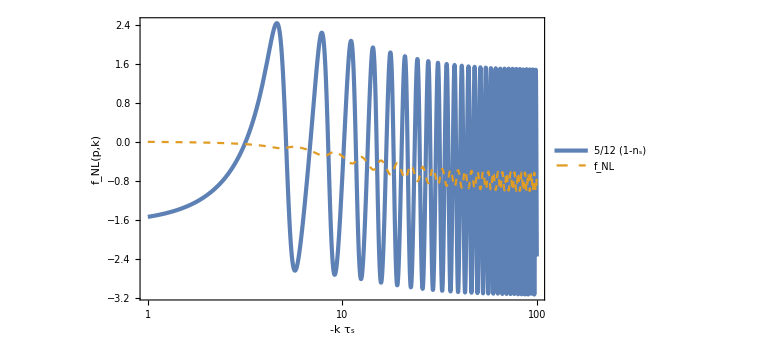

```mathematica
LogLinearPlot[{-5/12 nsm1[-10^-lndt,-1,k]/.{H->Hs},fNLpktks[-10^-lndt,-1,1,k]+fNLpktkη[-10^-lndt,-1,1,k]+fNLpktkH[-10^-lndt,-1,1,k]/.{Δηs->-6,η->-6,H->Hs}},{k,1,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],Row[{p==1,", ",τ==Subscript[τ, "e"]}]}},PlotLegends->Placed[LineLegend[{5/12(1-Subscript[n, "s"]),Subscript[f, NL]}],{0.2,0.2}]]
```

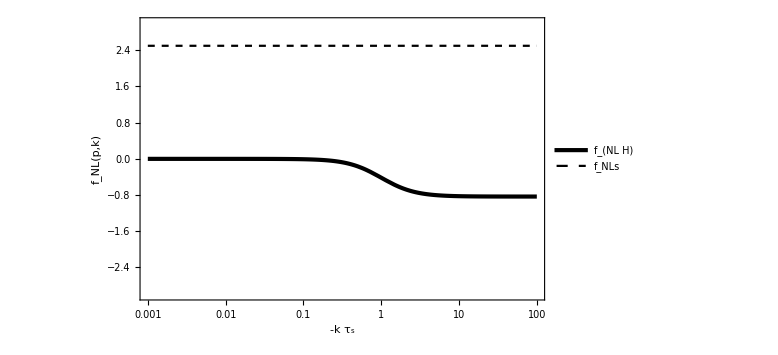

```mathematica
LogLinearPlot[{fNLpktkH[-1,-1,10^-3,k]/.{H->Hs},fNLpktks[-1,-1,10^-3,k]/.{Δηs->-6}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}},GridLines->{None,{-5/2}},FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],Row[{p==0.001,", ",τ==Subscript[τ, "s"]}]}},PlotLegends->Placed[LineLegend[{Subscript[f, Row[{NL," ",H}]],Subscript[f, NLs]},LegendLayout->"Row"],{0.7,0.15}],PlotRange->{-3,3}]
```

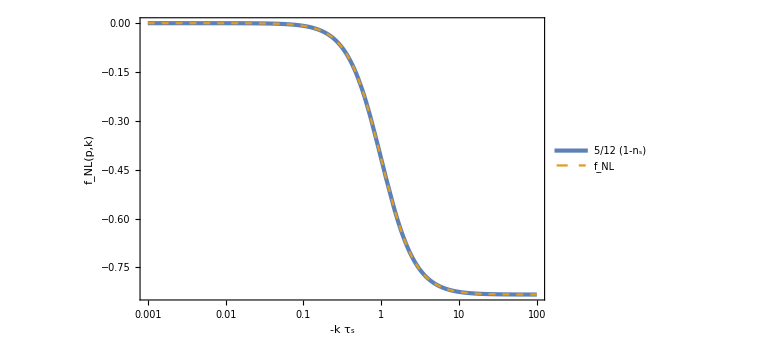

```mathematica
LogLinearPlot[{-5/12 nsm1[-1,-1,k]/.{H->Hs},fNLpktks[-1,-1,10^-3,k]+fNLpktkη[-1,-1,10^-3,k]+fNLpktkH[-1,-1,10^-3,k]/.{Δηs->-6,η->-6,H->Hs}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],Row[{p==0.001,", ",τ==Subscript[τ, "s"]}]}},PlotLegends->Placed[LineLegend[{5/12(1-Subscript[n, "s"]),Subscript[f, NL]},LegendLayout->"Row"],{0.35,0.15}]]
```

```mathematica
Pxp[τ_,τs_,k_]=Re[ζkUSRs[τ,τs,k]ζkUSRp[τ,τs,k]//ExpToTrig//Expand]//Simplify
```

1/(8 k^9 ϵSR τ^7)H^2 (-((3+2 k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6))+3 (9-12 k^2 τ (τ-3 τs)+2 k^8 τ^3 τs^5-4 k^6 τ τs^3 (2 τ^2-7 τ τs+3 τs^2)-3 k^4 (2 τ^3 τs-16 τ τs^3+7 τs^4)) Cos[2 k (τ-τs)]+3 k (6 τs (-3-4 k^2 τs^2+k^4 τs^4)-8 k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)-6 τ (-3+7 k^4 τs^4)+k^2 τ^3 (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)])

```mathematica
Pp[τ_,τs_,k_]=ζkUSRps[τ,τs,k]ζkUSRp[τ,τs,k]//ExpToTrig//Expand//Simplify
```

1/(8 k^9 ϵSR τ^8)H^2 ((9+3 k^2 τ^2+k^4 τ^4) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6)+3 (-27+9 k^2 τ (5 τ-12 τs)+k^8 τ^3 (7 τ-12 τs) τs^4+3 k^6 τ τs^3 (16 τ^2-35 τ τs+12 τs^2)-3 k^4 (τ^4-12 τ^3 τs+48 τ τs^3-21 τs^4)) Cos[2 k (τ-τs)]-6 k (9 τs (-3-4 k^2 τs^2+k^4 τs^4)-15 k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)+k^4 τ^4 τs (-3-4 k^2 τs^2+k^4 τs^4)-9 τ (-3+7 k^4 τs^4)+3 k^2 τ^3 (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)])

```mathematica
calPxp[τ_,τs_,k_]=k^3/(2 π^2)Pxp[τ,τs,k];
calPp[τ_,τs_,k_]=k^3/(2 π^2)Pp[τ,τs,k];
```

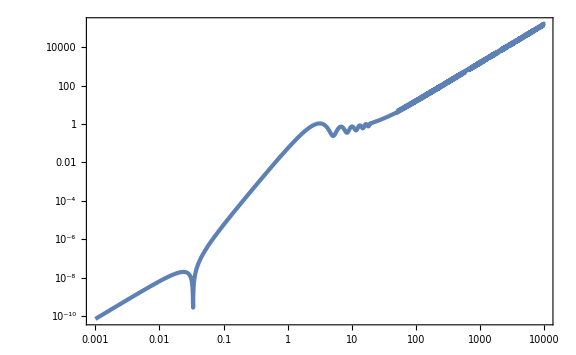

```mathematica
LogLogPlot[Abs[calPxp[-10^-lndt,-1,k]/.{H->Hs,ϵSR->10^-2}],{k,10^-3,10^4},WorkingPrecision->30]
```

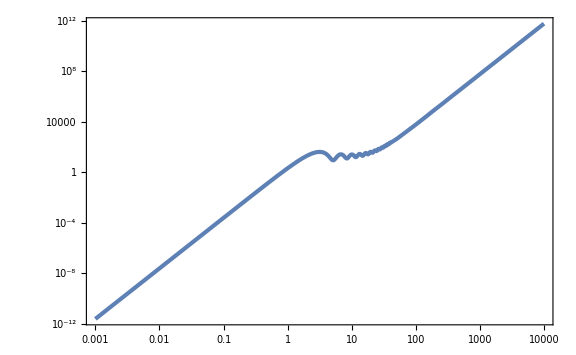

```mathematica
LogLogPlot[calPp[-10^-lndt,-1,k]/.{H->Hs,ϵSR->10^-2},{k,10^-3,10^4},WorkingPrecision->30]
```

```mathematica
nsxp[τ_,τs_,k_]=k/calPxp[τ,τs,k] D[calPxp[τ,τs,k], k]//Simplify;
nsp[τ_,τs_,k_]=k/calPp[τ,τs,k] D[calPp[τ,τs,k], k]//Simplify;
```

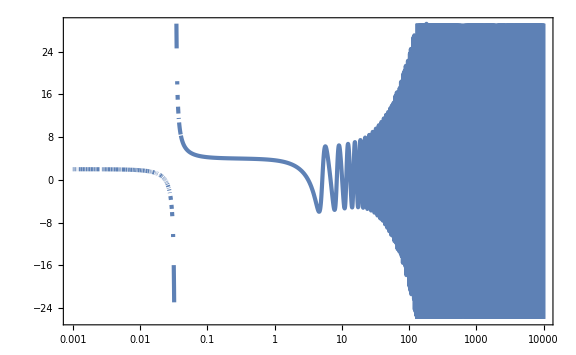

```mathematica
LogLinearPlot[nsxp[-10^-lndt,-1,k],{k,10^-3,10^4},WorkingPrecision->30]
```

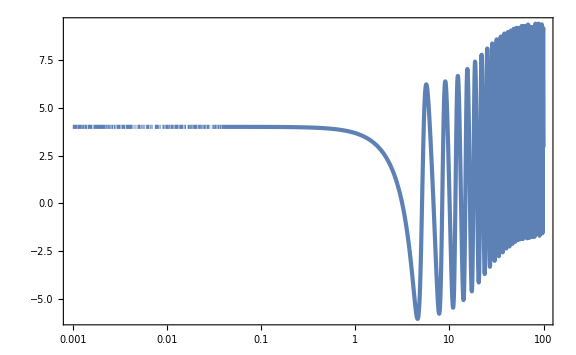

```mathematica
LogLinearPlot[nsp[-10^-lndt,-1,k],{k,10^-3,10^2},WorkingPrecision->30,PlotRange->Full]
```

```mathematica
fNLxpbulks[τ_,τs_,k_]=-5/6 1/(τs^2 H^2)ϵSR Δηs 1/Pxp[τ,τs,k](Re[ζkUSRp[τ,τs,k]ζkUSRps[τs,τs,k]]Im[ζkUSR[τ,τs,k]ζkUSRs[τs,τs,k]]
+Im[ζkUSRp[τ,τs,k]ζkUSRps[τs,τs,k]]Re[ζkUSR[τ,τs,k]ζkUSRs[τs,τs,k]]
+Im[ζkUSR[τ,τs,k]ζkUSRps[τs,τs,k]]Re[ζkUSRp[τ,τs,k]ζkUSRs[τs,τs,k]]
+Re[ζkUSR[τ,τs,k]ζkUSRps[τs,τs,k]]Im[ζkUSRp[τ,τs,k]ζkUSRs[τs,τs,k]])//Simplify;
```

```mathematica
Im[ζkUSRp[τ,τs,k]ζkUSRs[τ,τs,k]//ExpToTrig//Expand]//Simplify
```

-(H^2 τs^6)/(4 ϵSR τ^4)

```mathematica
fNLxpη[τ_,τs_,k_]=5/6 1/(τ^2 H^2)ϵSR (τ/τs)^6 η 1/Pxp[τ,τs,k](Simplify[Im[ζkUSR[τ,τs,k]ζkUSRps[τ,τs,k]//ExpToTrig//Expand]]Simplify[Re[ζkUSRp[τ,τs,k]ζkUSRs[τ,τs,k]//ExpToTrig//Expand]]
+Simplify[Re[ζkUSR[τ,τs,k]ζkUSRps[τ,τs,k]//ExpToTrig//Expand]]Simplify[Im[ζkUSRp[τ,τs,k]ζkUSRs[τ,τs,k]//ExpToTrig//Expand]])
```

0

```mathematica
fNLxpH[τ_,τs_,k_]=-5/3 1/(τ H^2)ϵSR (τ/τs)^6(Simplify[Im[ζkUSR[τ,τs,k]ζkUSRps[τ,τs,k]//ExpToTrig//Expand]]Pp[τ,τs,k])/Pxp[τ,τs,k]//Simplify
```

-((5 ((9+3 k^2 τ^2+k^4 τ^4) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6)+3 (-27+9 k^2 τ (5 τ-12 τs)+k^8 τ^3 (7 τ-12 τs) τs^4+3 k^6 τ τs^3 (16 τ^2-35 τ τs+12 τs^2)-3 k^4 (τ^4-12 τ^3 τs+48 τ τs^3-21 τs^4)) Cos[2 k (τ-τs)]-6 k (9 τs (-3-4 k^2 τs^2+k^4 τs^4)-15 k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)+k^4 τ^4 τs (-3-4 k^2 τs^2+k^4 τs^4)-9 τ (-3+7 k^4 τs^4)+3 k^2 τ^3 (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)]))/(12 (-((3+2 k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6))+3 (9-12 k^2 τ (τ-3 τs)+2 k^8 τ^3 τs^5-4 k^6 τ τs^3 (2 τ^2-7 τ τs+3 τs^2)-3 k^4 (2 τ^3 τs-16 τ τs^3+7 τs^4)) Cos[2 k (τ-τs)]+3 k (6 τs (-3-4 k^2 τs^2+k^4 τs^4)-8 k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)-6 τ (-3+7 k^4 τs^4)+k^2 τ^3 (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)])))

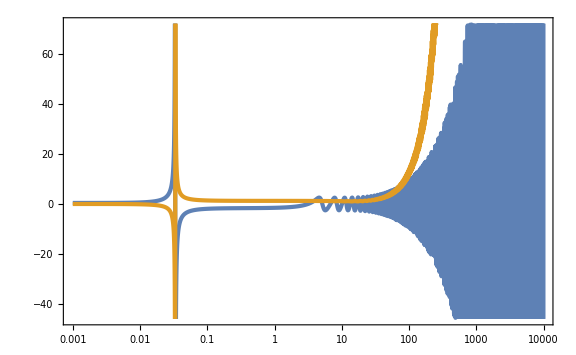

```mathematica
LogLinearPlot[{fNLxpbulks[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs,Δηs->-6},fNLxpH[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}},{k,10^-3,10^4},WorkingPrecision->30]
```

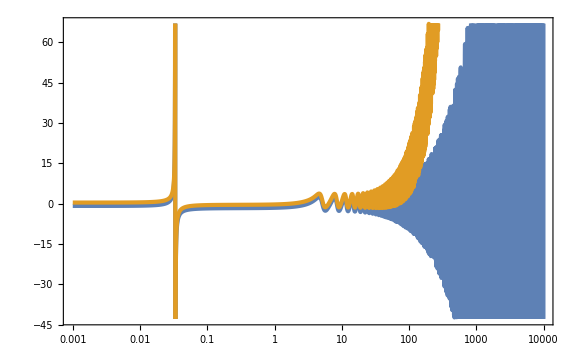

```mathematica
LogLinearPlot[{-5/12 nsxp[-10^-lndt,-1,k],fNLxpbulks[-10^-lndt,-1,k]+fNLxpH[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs,Δηs->-6}},{k,10^-3,10^4},WorkingPrecision->30]
```

```mathematica
fNLpbulks[τ_,τs_,k_]=-5/3 1/(τs^2 H^2)ϵSR Δηs 1/Pp[τ,τs,k](Im[ζkUSRp[τ,τs,k]ζkUSRs[τs,τs,k]]Re[ζkUSRp[τ,τs,k]ζkUSRps[τs,τs,k]]
+Re[ζkUSRp[τ,τs,k]ζkUSRs[τs,τs,k]]Im[ζkUSRp[τ,τs,k]ζkUSRps[τs,τs,k]])//Simplify;
```

```mathematica
fNLpη[τ_,τs_,k_]=5/3 1/(τ^2 H^2)ϵSR (τ/τs)^6 η Im[ζkUSRp[τ,τs,k]ζkUSRs[τ,τs,k]//ExpToTrig//Expand]//Simplify
```

-(5 η)/12

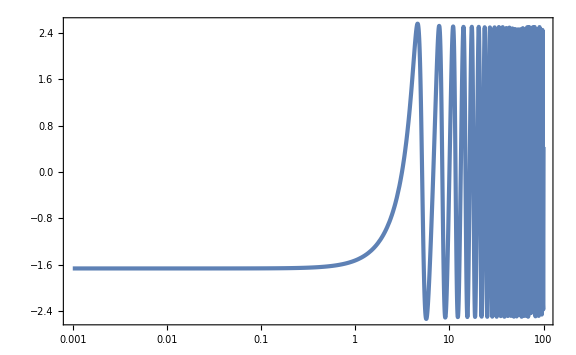

```mathematica
LogLinearPlot[fNLpbulks[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs,Δηs->-6},{k,10^-3,10^2},WorkingPrecision->30,GridLines->{None,{5/2}}]
```

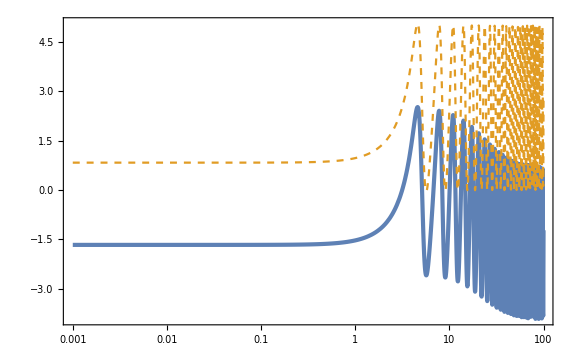

```mathematica
LogLinearPlot[{-5/12 nsp[-10^-lndt,-1,k],fNLpbulks[-10^-lndt,-1,k]+5/2/.{ϵSR->10^-2,H->Hs,Δηs->-6}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed}]
```

## SR2USR2SR num

```mathematica
$Assumptions={ϵ0>0,τ0<0,τi<0,τs<0,τ<0,lnDt>0};
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];lndt//N
```

1.1165

```mathematica
dNs=(*5 *)2 10^-2;
η[τ_]=-6 (1-Tanh[Log[τ/τs]/dN])/2(1-Tanh[Log[(τs 10^-lnDt)/τ]/dN])/2//FullSimplify
```

-3/2 (-1+Tanh[Log[τ/τs]/dN]) (-1+Tanh[Log[(10^-lnDt τs)/τ]/dN])

```mathematica
ηs[τ_]=η[τ]/.{τs->-1,lnDt->lndt,dN->dNs}//Simplify
```

-3/2 (-1+Tanh[50 Log[-1/(10 5^(1/6) τ)]]) (-1+Tanh[50 Log[-τ]])

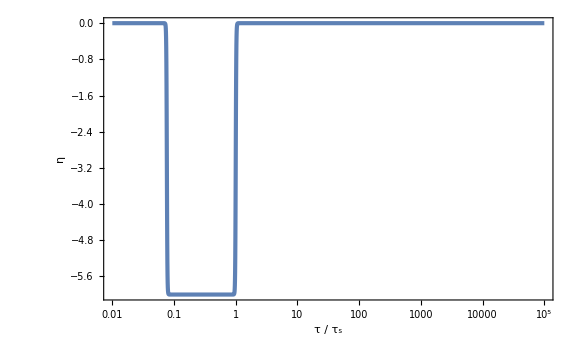

```mathematica
LogLinearPlot[ηs[-x],{x,10^-2,10^5},PlotRange->Full,FrameLabel->{"τ / τ_s",η}]
```

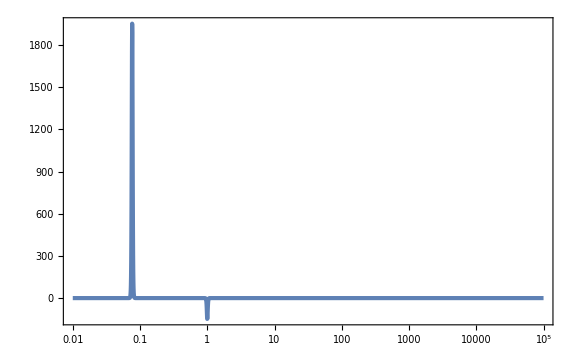

```mathematica
LogLinearPlot[ηs'[-x],{x,10^-2,10^5},PlotRange->Full]
```

```mathematica
ηint[τ_]=Integrate[(-η[τ])/τ,τ]//Simplify
```

-3/2 dN (1+Coth[(lnDt Log[10])/dN]) (Log[Cosh[Log[τ/τs]/dN]]-Log[Cosh[Log[(10^-lnDt τs)/τ]/dN]])

```mathematica
ϵ[τ_]=ϵ0 Exp[ηint[τ]-ηint[τ0]]/.{τs->-1,lnDt->lndt,dN->dNs,τ0->-10^5,ϵ0->10^-2}//Simplify
```

1/100 (Cosh[50 Log[100000]] Sech[25/3 (Log[5]+6 Log[1000000])])^(3/100 (1+Coth[50 Log[10 5^(1/6)]])) (Cosh[50 Log[-1/(10 5^(1/6) τ)]] Sech[50 Log[-τ]])^(3/100 (1+Coth[50 Log[10 5^(1/6)]]))

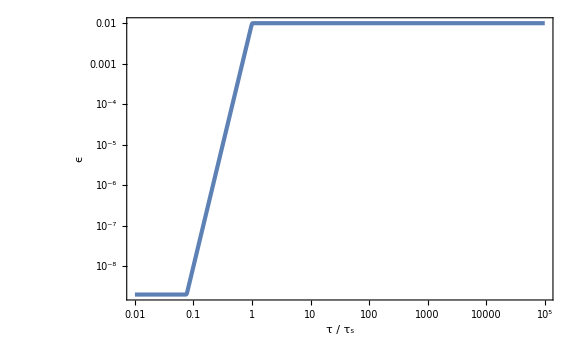

```mathematica
LogLogPlot[ϵ[-x],{x,10^-2,10^5},WorkingPrecision->30,FrameLabel->{"τ / τ_s",ϵ},WorkingPrecision->30]
```

```mathematica
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[2]]
z[τ_]=-1/(τ H)Sqrt[2ϵ[τ]]/.{H->Hs}//Simplify
```

π/(25000 √10)

-1/(π τ)5000 √5 (Cosh[50 Log[100000]] Sech[25/3 (Log[5]+6 Log[1000000])])^(3/200 (1+Coth[50 Log[10 5^(1/6)]])) (Cosh[50 Log[-1/(10 5^(1/6) τ)]] Sech[50 Log[-τ]])^(3/200 (1+Coth[50 Log[10 5^(1/6)]]))

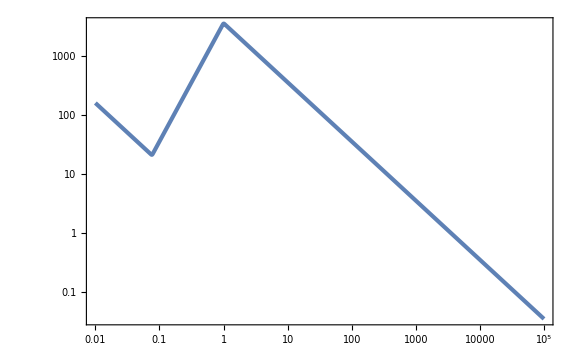

```mathematica
LogLogPlot[z[-x],{x,10^-2,10^5},WorkingPrecision->30]
```

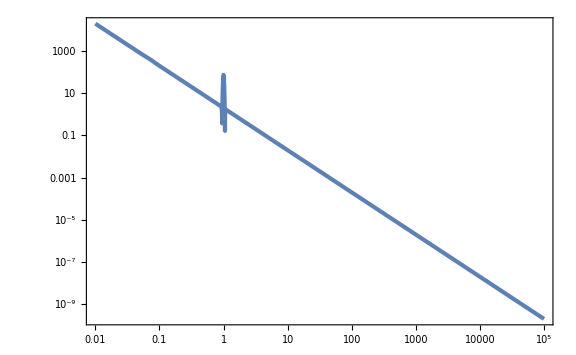

```mathematica
LogLogPlot[Abs[z''[-x]/z[-x]],{x,10^-2,10^5},WorkingPrecision->30]
```

```mathematica
EoM=vk''[τ]+(k^2-z''[τ]/z[τ])vk[τ]==0//Simplify
```

(-632+16 k^2 τ^2-600 Coth[50 Log[10 5^(1/6)]]+600 (1+Coth[50 Log[10 5^(1/6)]]) Sech[50 Log[-τ]]^2+(591+582 Coth[50 Log[10 5^(1/6)]]-9 Coth[50 Log[10 5^(1/6)]]^2) Tanh[50 Log[-1/(10 5^(1/6) τ)]]^2-36 Tanh[50 Log[-τ]]-36 Coth[50 Log[10 5^(1/6)]] Tanh[50 Log[-τ]]-9 Tanh[50 Log[-τ]]^2-18 Coth[50 Log[10 5^(1/6)]] Tanh[50 Log[-τ]]^2-9 Coth[50 Log[10 5^(1/6)]]^2 Tanh[50 Log[-τ]]^2-18 (1+Coth[50 Log[10 5^(1/6)]]) Tanh[50 Log[-1/(10 5^(1/6) τ)]] (2+(1+Coth[50 Log[10 5^(1/6)]]) Tanh[50 Log[-τ]])) vk[τ]+16 τ^2 vk''[τ]==0

```mathematica
vkform[τ_,k_]=1/Sqrt[2k](1-I/(k τ))E^(-I k τ);
vkformp[τ_,k_]=D[vkform[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) (ⅈ-k τ-ⅈ k^2 τ^2))/(√2 k^(3/2) τ^2)

```mathematica
Ak[k_]=1-(3(1+k^2 τs^2))/(2I k^3 τs^3);
Bk[k_]=-(3(1+I k τs)^2)/(2I k^3 τs^3)Exp[-2I k τs];
ζk[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak[k] E^(-I k τ)(1+I k τ)-Bk[k] E^(I k τ)(1-I k τ))/.{ϵSR->10^-2,τs->-1,H->Hs};
```

### kL = 1e-3

```mathematica
kL=10^-3;
τiL=-10^2/kL;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==vkform[τi,k],vk'[τi]==vkformp[τi,k]}/.{τi->τiL,k->kL},vk[τ],{τ,τiL,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
```

```mathematica
ζkL[τ_]=vkL[τ]/z[τ];
PζkL[τ_]=Norm[ζkL[τ]]^2;
```

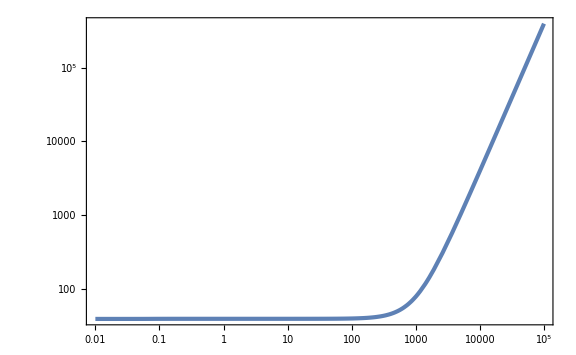

```mathematica
LogLogPlot[ PζkL[-x],{x,10^-2,10^5}]
```

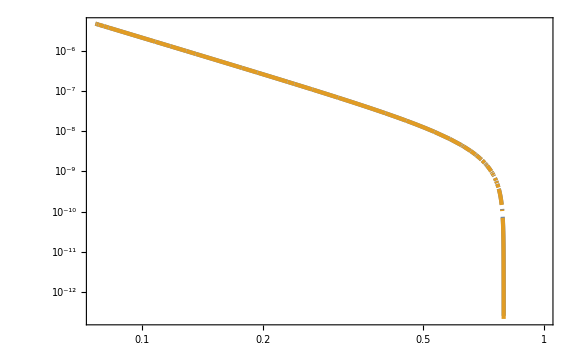

```mathematica
LogLogPlot[{Re[ζkL[-x]],Re[ζk[-x,kL]]},{x,10^-lndt,1},WorkingPrecision->30]
```

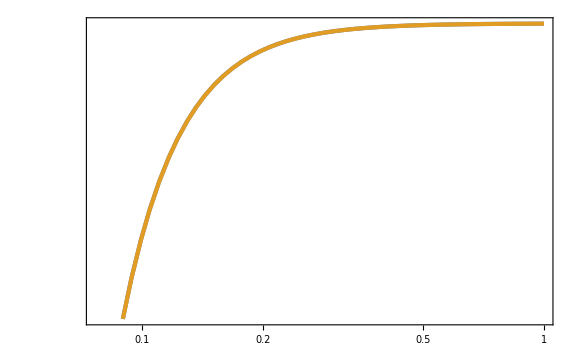

```mathematica
LogLogPlot[{Im[ζkL[-x]],Im[ζk[-x,kL]]},{x,10^-lndt,1},WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[kS=10^1;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==vkform[τi,k],vk'[τi]==vkformp[τi,k]}/.{τi->τiS,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
{fNLs=-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3,-1/3}(*,WorkingPrecision->30,MaxRecursion->12*)],
fNLe=-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3 10^-lndt,-10^-2}(*,WorkingPrecision->30,MaxRecursion->12*)]}]
```

{0.607884,{-0.21311,-0.104203}}

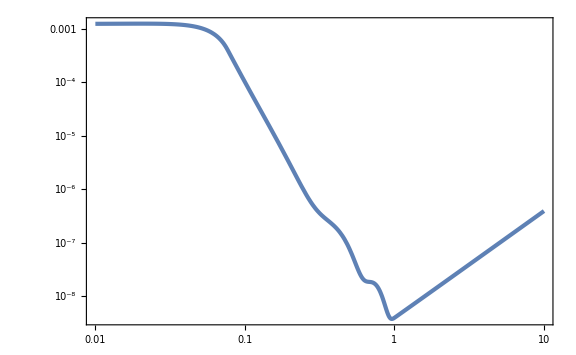

```mathematica
LogLogPlot[ PζkS[-x],{x,10^-2,-τiS}]
```

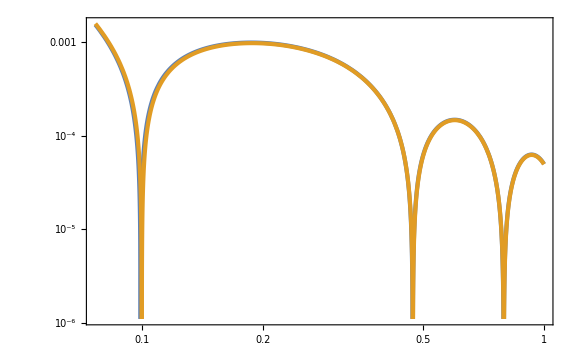

```mathematica
LogLogPlot[{Abs[Re[ζkS[-x]]],Abs[Re[ζk[-x,kS]]]},{x,10^-lndt,1},WorkingPrecision->30]
```

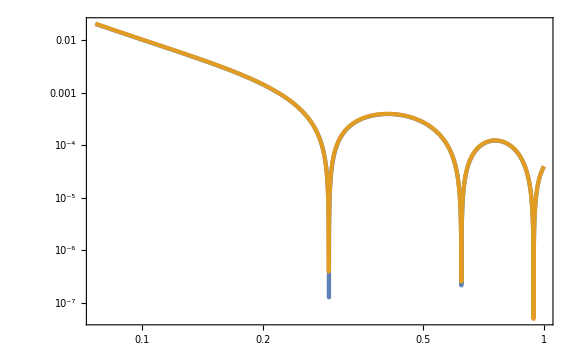

```mathematica
LogLogPlot[{Abs[Im[ζkS[-x]]],Abs[Im[ζk[-x,kS]]]},{x,10^-lndt,1},WorkingPrecision->30]
```

```mathematica
Im[(1/(H^2 τiS^2)ϵ[τiS]η[τiS]ζkS[τiS]Conjugate[ζkS'[τiS]])/(ζkS[-10^-2]Conjugate[ζkS[-10^-2]])/.{H->Hs,τs->-1,dN->dNs,lnDt->lndt}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 5 Sech[50 Log[10]] Sinh[50 Log[1/(100 5^(1/6))]]+5 Cosh[50 Log[1/(100 5^(1/6))]] Sech[50 Log[10]] Tanh[50 Log[10]].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1+Tanh[50 Log[10]].

0.

```mathematica
calPkfNLList=ParallelTable[kS=10^lnk;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==vkform[τi,k],vk'[τi]==vkformp[τi,k]}/.{τi->τiS,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
fNLs=-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3,-1/3}(*,WorkingPrecision->30*)]//Quiet;
fNLe=-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3 10^-lndt,-10^-2}(*,WorkingPrecision->30*)]//Quiet;
{kS,calPζkS[-10^-2],fNLs,fNLe},{lnk,-3,2,10^-2}];//AbsoluteTiming
```

{87.3653,Null}

```mathematica
calPkList=Map[{#[[1]],#[[2]]}&,calPkfNLList];
fNLsList=Map[{#[[1]],#[[3]]}&,calPkfNLList];
fNLeList=Map[{#[[1]],#[[4]]}&,calPkfNLList];
fNLList=Map[{#[[1]],#[[3]]+#[[4]]}&,calPkfNLList];
calPkint[k_]=Interpolation[calPkList][k];
nsm1[k_]=k D[Log[calPkint[k]], k];
```

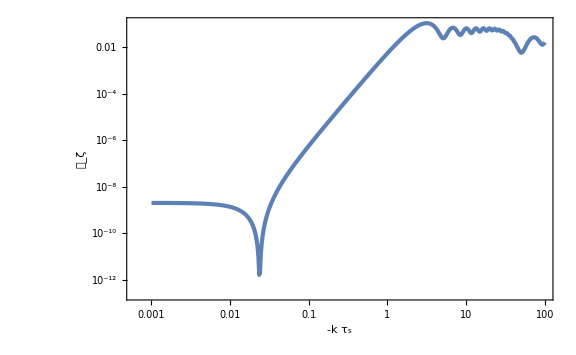

```mathematica
ListLogLogPlot[calPkList,FrameLabel->{-k Subscript[τ, s],Subscript[𝒫, ζ]}]
```

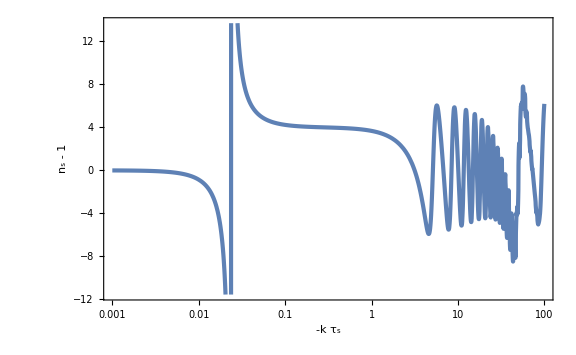

```mathematica
LogLinearPlot[nsm1[k],{k,10^-3,10^2},FrameLabel->{-k Subscript[τ, s],"n_s - 1"}]
```

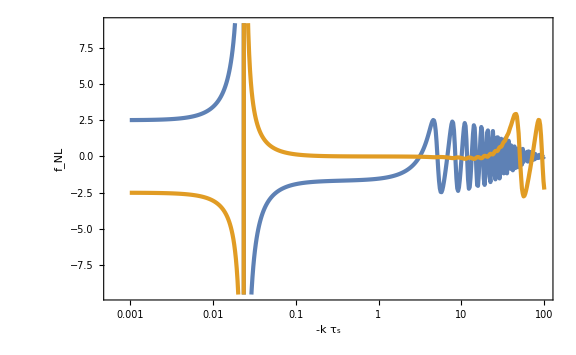

```mathematica
ListLogLinearPlot[{fNLsList,fNLeList},FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}]
```

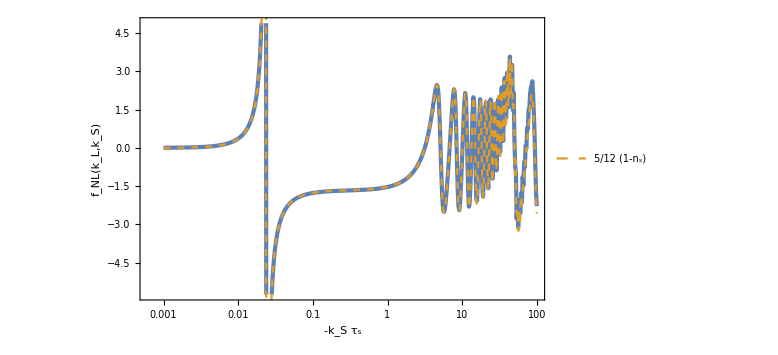

```mathematica
Show[ListLogLinearPlot[fNLList,FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Subscript[k, "L"]==0.001}}],LogLinearPlot[-5/12 nsm1[k],{k,10^-3,10^2},PlotStyle->{Color[2],Dashed},PlotRange->Full,PlotLegends->Placed[{5/12(1-Subscript[n, "s"])},{0.8,0.15}]]]
```

### kL = 5

```mathematica
kL=5;
τiL=-10^2/kL;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==vkform[τi,k],vk'[τi]==vkformp[τi,k]}/.{τi->τiL,k->kL},vk[τ],{τ,τiL,-10^-2},WorkingPrecision->30][[1]];
```

```mathematica
ζkL[τ_]=vkL[τ]/z[τ];
PζkL[τ_]=Norm[ζkL[τ]]^2;
```

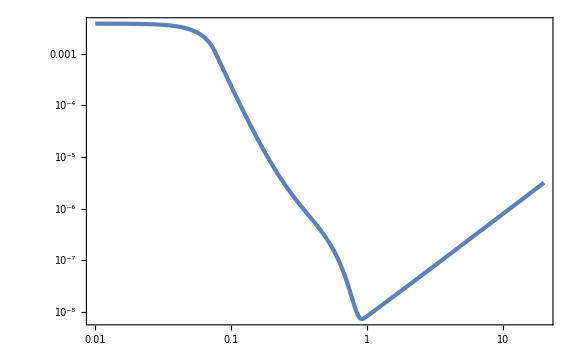

```mathematica
LogLogPlot[ PζkL[-x],{x,10^-2,-τiL}]
```

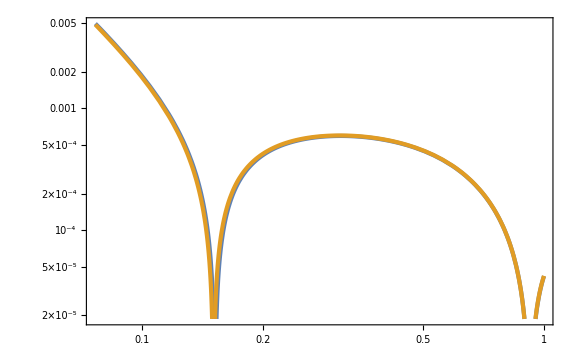

```mathematica
LogLogPlot[{Abs[Re[ζkL[-x]]],Abs[Re[ζk[-x,kL]]]},{x,10^-lndt,1},WorkingPrecision->30]
```

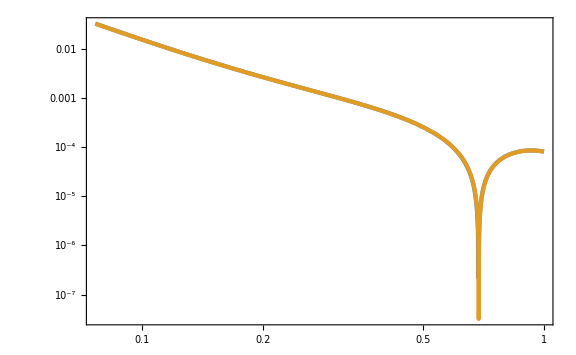

```mathematica
LogLogPlot[{Abs[Im[ζkL[-x]]],Abs[Im[ζk[-x,kL]]]},{x,10^-lndt,1},WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[kS=20;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==vkform[τi,k],vk'[τi]==vkformp[τi,k]}/.{τi->τiS,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
{fNLs=-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3,-1/3}(*,WorkingPrecision->30,MaxRecursion->12*)],
fNLe=-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3 10^-lndt,-10^-2}(*,WorkingPrecision->30,MaxRecursion->12*)]}]
```

{0.517674,{-0.00213568,0.0458343}}

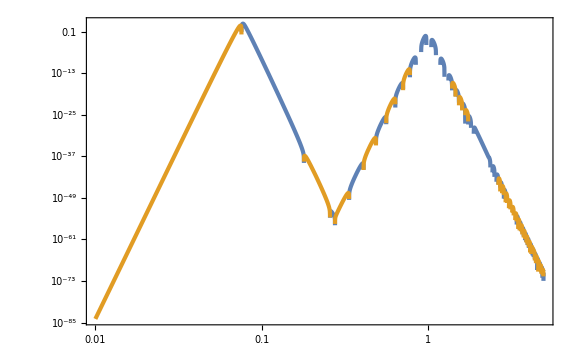

```mathematica
LogLogPlot[{-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])Im[(ϵ[-x]ηs'[-x])/(x^2 H^2)pktk[-10^-2,-x]/.{H->Hs}],+5/3 1/(PζkL[-10^-2]PζkS[-10^-2])Im[(ϵ[-x]ηs'[-x])/(x^2 H^2)pktk[-10^-2,-x]/.{H->Hs}]},{x,10^-2,-τiS},WorkingPrecision->30]
```

```mathematica
calPkfNLList=ParallelTable[kS=10^lnk;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==vkform[τi,k],vk'[τi]==vkformp[τi,k]}/.{τi->τiS,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
fNLs=-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3,-1/3}(*,WorkingPrecision->30*)]//Quiet;
fNLe=-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]ηs'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3 10^-lndt,-10^-2}(*,WorkingPrecision->30*)]//Quiet;
{kS,calPζkS[-10^-2],fNLs,fNLe},{lnk,Log10[5],2,10^-3}];//AbsoluteTiming
```

{149.065,Null}

```mathematica
calPkList=Map[{#[[1]],#[[2]]}&,calPkfNLList];
fNLsList=Map[{#[[1]],#[[3]]}&,calPkfNLList];
fNLeList=Map[{#[[1]],#[[4]]}&,calPkfNLList];
fNLList=Map[{#[[1]],#[[3]]+#[[4]]}&,calPkfNLList];
calPkint[k_]=Interpolation[calPkList][k];
nsm1[k_]=k D[Log[calPkint[k]], k];
```

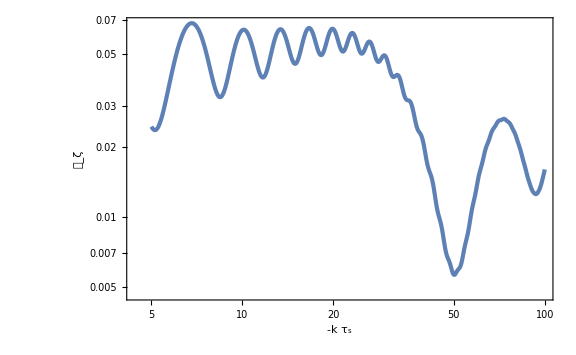

```mathematica
ListLogLogPlot[calPkList,FrameLabel->{-k Subscript[τ, s],Subscript[𝒫, ζ]}]
```

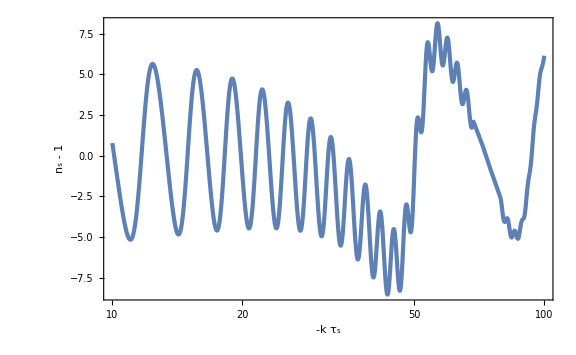

```mathematica
LogLinearPlot[nsm1[k],{k,10,10^2},FrameLabel->{-k Subscript[τ, s],"n_s - 1"}]
```

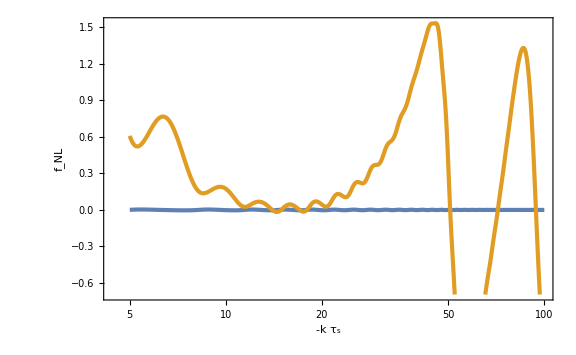

```mathematica
ListLogLinearPlot[{fNLsList,fNLeList},FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}]
```

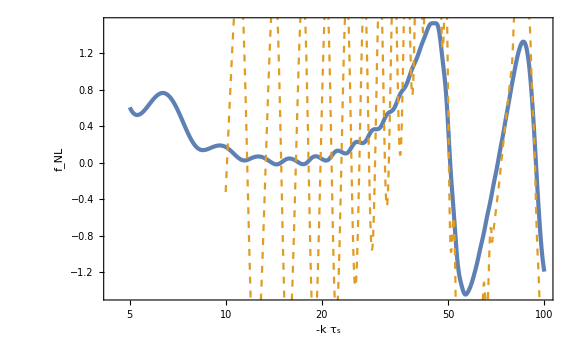

```mathematica
Show[ListLogLinearPlot[fNLList,FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}],LogLinearPlot[-5/12 nsm1[k],{k,10,10^2},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```

```mathematica
heff=((1.5/(4dNs))^-3+6^-3)^(1/3)
```

0.168468

```mathematica
fNLPHM=5/2 heff^2/(heff+1)^2
```

0.0519684

## SR2USR2SR num ボツ

```mathematica
$Assumptions={ϵ0>0,τ0<0,τi<0,τs<0,τ<0,lnDt>0};
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];lndt//N
```

1.1165

```mathematica
dN=5 10^-2;
ηs[τ_]=-6 (1-Tanh[Log[τ/τs]/dN])/2/.{τs->-1}//FullSimplify
ηe[τ_]=-6(1-Tanh[Log[(τs 10^-lnDt)/τ]/dN])/2/.{τs->-1,lnDt->lndt}//FullSimplify
ηsp[τ_]=ηs'[τ]//Simplify
ηep[τ_]=ηe'[τ]//Simplify
```

-6/(1+τ^40)

3 (-1+Tanh[20 Log[-1/(10 5^(1/6) τ)]])

(240 τ^39)/((1+τ^40)^2)

-(60 Sech[20 Log[-1/(10 5^(1/6) τ)]]^2)/τ

```mathematica
τsm=τ/.Solve[Log[τ/τs]/dN==10/.{τs->-1},τ][[1]];
τsp=τ/.Solve[Log[τ/τs]/dN==-10/.{τs->-1},τ][[1]];
τem=τ/.Solve[Log[(τs 10^-lnDt)/τ]/dN==-10/.{τs->-1,lnDt->lndt},τ][[1]];
τep=τ/.Solve[Log[(τs 10^-lnDt)/τ]/dN==10/.{τs->-1,lnDt->lndt},τ][[1]];
τsm//N
τsp//N
τem//N
τep//N
```

-1.64872

-0.606531

-0.126082

-0.0463829

```mathematica
Clear[η,ηp]
η[τ_]:=ηs[τ]/;(τsm<τ<τsp)
η[τ_]:=ηe[τ]/;(τem<τ<τep)
η[τ_]:=-6/;(τsp<=τ<=τem)
η[τ_]:=0/;(τ<=τsm||τ>=τep)
ηp[τ_]:=ηsp[τ]/;(τsm<τ<τsp)
ηp[τ_]:=ηep[τ]/;(τem<τ<τep)
ηp[τ_]:=0/;!((τsm<τ<τsp)||(τem<τ<τep))
```

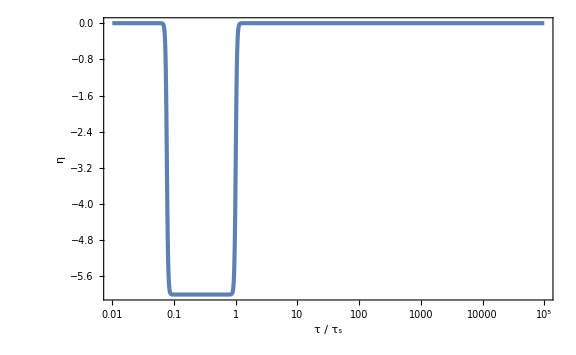

```mathematica
LogLinearPlot[η[-x],{x,10^-2,10^5},PlotRange->Full,FrameLabel->{"τ / τ_s",η}]
```

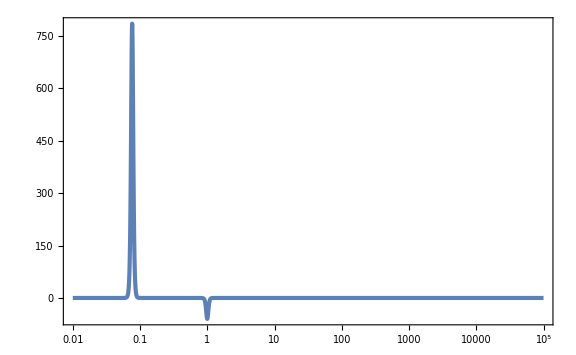

```mathematica
LogLinearPlot[ηp[-x],{x,10^-2,10^5},PlotRange->Full]
```

```mathematica
ηsint[τ_]=Integrate[-ηs[τ]/τ,τ]//Simplify
ηeint[τ_]=Integrate[-ηe[τ]/τ,τ]//Simplify
ηUSRint[τ_]=Integrate[6/τ,τ]//Simplify
```

6 (Log[τ]-1/40 Log[1+τ^40])

3 Log[τ]+3/20 Log[Cosh[20 Log[-1/(10 5^(1/6) τ)]]]

6 Log[τ]

```mathematica
ηint1[τ_]=ηsint[τ]-ηsint[τsm]//Simplify
ηint2[τ_]=ηUSRint[τ]-ηUSRint[τsp]+ηsint[τsp]-ηsint[τsm]//Simplify
ηint3[τ_]=ηeint[τ]-ηeint[τem]+ηUSRint[τem]-ηUSRint[τsp]+ηsint[τsp]-ηsint[τsm]//Simplify//Re
ηint4=ηeint[τep]-ηeint[τem]+ηUSRint[τem]-ηUSRint[τsp]+ηsint[τsp]-ηsint[τsm]//Simplify
```

3/20 (-20+Log[1+ⅇ^20]+40 Log[-τ]-Log[1+τ^40])

6 Log[-τ]

-3/2-Log[5000000]/2+Re[3 Log[τ]+3/20 Log[ⅇ^20 Cosh[20 Log[-1/(10 5^(1/6) τ)]] Sech[10]]]

-Log[5000000]

```mathematica
Clear[ηint]
ηint[τ_]:=0/;τ<=τsm
ηint[τ_]:=ηint1[τ]/;τsm<τ<τsp
ηint[τ_]:=ηint2[τ]/;τsp<=τ<=τem
ηint[τ_]:=ηint3[τ]/;τem<τ<τep
ηint[τ_]:=ηint4/;τep<=τ
```

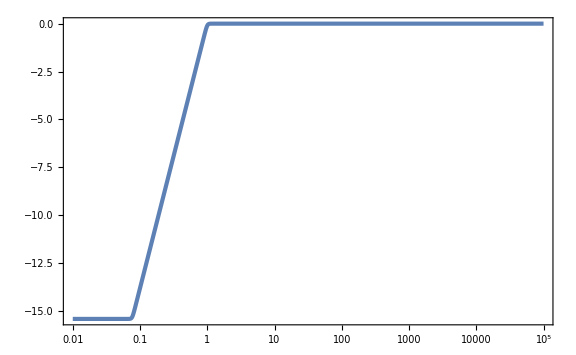

```mathematica
LogLinearPlot[ηint[-x],{x,10^-2,10^5}]
```

```mathematica
ϵ1[τ_]=ϵ0 Exp[ηint1[τ]]/.{ϵ0->10^-2}//Simplify
ϵ2[τ_]=ϵ0 Exp[ηint2[τ]]/.{ϵ0->10^-2}//Simplify
ϵ3[τ_]=ϵ0 Exp[ηint3[τ]]/.{ϵ0->10^-2}//Simplify
ϵ4=ϵ0 Exp[ηint4]/.{ϵ0->10^-2}//Simplify
```

((1+ⅇ^20)^(3/20) τ^6)/(100 ⅇ^3 (1+τ^40)^(3/20))

τ^6/100

-(ⅇ^(3/2) τ^3 Cosh[20 Log[-1/(10 5^(1/6) τ)]]^(3/20) Sech[10]^(3/20))/(100000 √5)

1/500000000

```mathematica
Clear[ϵ]
ϵ[τ_]:=(ϵ0/.{ϵ0->10^-2})/;τ<=τsm
ϵ[τ_]:=ϵ1[τ]/;τsm<τ<τsp
ϵ[τ_]:=ϵ2[τ]/;τsp<=τ<=τem
ϵ[τ_]:=ϵ3[τ]/;τem<τ<τep
ϵ[τ_]:=ϵ4/;τep<=τ
```

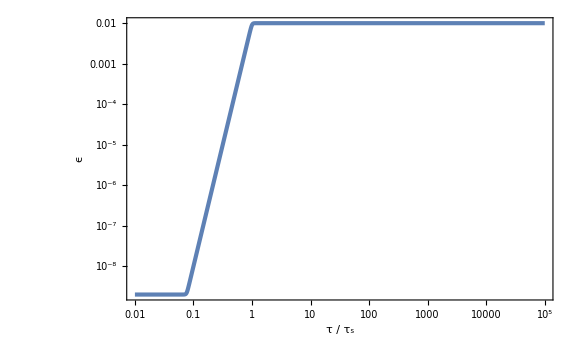

```mathematica
LogLogPlot[ϵ[-x],{x,10^-2,10^5},WorkingPrecision->30,FrameLabel->{"τ / τ_s",ϵ}]
```

```mathematica
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[2]]
z0[τ_]=-1/(τ H)Sqrt[2ϵ0]/.{ϵ0->10^-2,H->Hs}//Simplify;
z1[τ_]=-1/(τ H)Sqrt[2ϵ1[τ]]/.{H->Hs}//Simplify;
z2[τ_]=-1/(τ H)Sqrt[2ϵ2[τ]]/.{H->Hs}//Simplify;
z3[τ_]=-1/(τ H)Sqrt[2ϵ3[τ]]/.{H->Hs}//Simplify;
z4[τ_]=-1/(τ H)Sqrt[2ϵ4]/.{H->Hs}//Simplify;
```

π/(25000 √10)

```mathematica
Clear[z]
z[τ_]:=z0[τ]/;τ<=τsm
z[τ_]:=z1[τ]/;τsm<τ<τsp
z[τ_]:=z2[τ]/;τsp<=τ<=τem
z[τ_]:=z3[τ]/;τem<τ<τep
z[τ_]:=z4[τ]/;τep<=τ
```

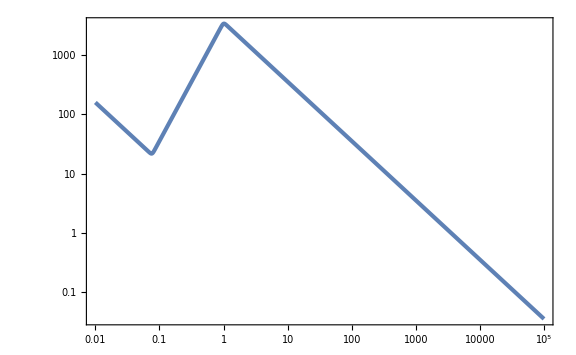

```mathematica
LogLogPlot[z[-x],{x,10^-2,10^5},WorkingPrecision->30]
```

```mathematica
zpp0[τ_]=z0''[τ]//Simplify;
zpp1[τ_]=z1''[τ]//Simplify;
zpp2[τ_]=z2''[τ]//Simplify;
zpp3[τ_]=z3''[τ];
zpp4[τ_]=z4''[τ]//Simplify;
```

```mathematica
Clear[zpp]
zpp[τ_]:=zpp0[τ]/;τ<=τsm
zpp[τ_]:=zpp1[τ]/;τsm<τ<τsp
zpp[τ_]:=zpp2[τ]/;τsp<=τ<=τem
zpp[τ_]:=zpp3[τ]/;τem<τ<τep
zpp[τ_]:=zpp4[τ]/;τep<=τ
```

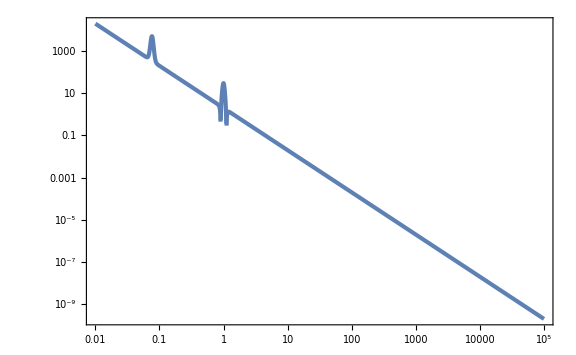

```mathematica
LogLogPlot[Abs[zpp[-x]/z[-x]],{x,10^-2,10^5},WorkingPrecision->30]
```

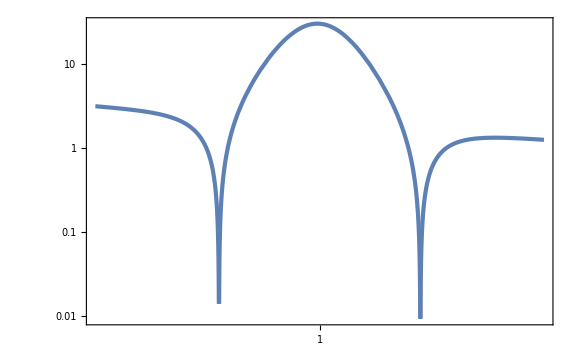

```mathematica
LogLogPlot[Abs[zpp[-x]/z[-x]],{x,10^-0.1,10^0.1},WorkingPrecision->30,PlotRange->Full]
```

```mathematica
EoM=vk''[τ]+(k^2-zpp[τ]/z[τ])vk[τ]==0//Simplify
```

vk[τ] (k^2-zpp[τ]/z[τ])+vk''[τ]==0

### kL = 1e-3

```mathematica
kL=10^-3;
τiL=-10^2/kL;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==1/Sqrt[2k],vk'[τi]==-I Sqrt[k/2]}/.{τi->τiL,k->kL},vk[τ],{τ,τiL,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
```

```mathematica
ζkL[τ_]=vkL[τ]/z[τ];
PζkL[τ_]=Norm[ζkL[τ]]^2;
```

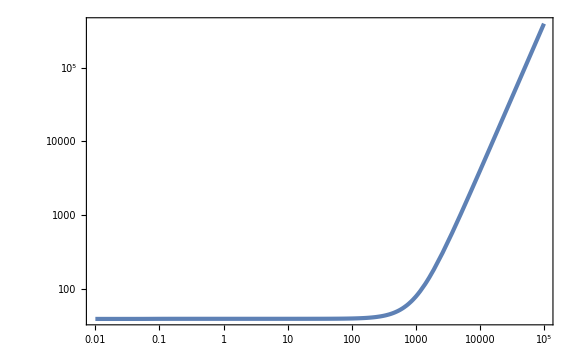

```mathematica
LogLogPlot[PζkL[-x],{x,10^-2,10^5}]
```

```mathematica
AbsoluteTiming[kS=10^1;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τ0->τiS,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
(*{fNLs=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,τsm,τsp},WorkingPrecision->30,MaxRecursion->12],
fNLe=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,τem,τep},WorkingPrecision->30,MaxRecursion->12]}*)
fNL=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3,-10^-2},WorkingPrecision->30,MaxRecursion->15]]
```

NIntegrate::precw: The precision of the argument function (Im[((4.4024498666482342928580505328×10^6-1.06690167037495808438403477×10^6 ⅈ) «4» η'[τp])/(τp^2 Conjugate[z[τp]]^2)]) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in τp near {τp} = {-0.084383730135628347911387033035496318634186101798413489616637060453306482191557232}. NIntegrate obtained 0.13116257512096395655445244831849766049843459801555876042533018437182006582077601 and 0.18608694436090565671520712800295296847865341796677568163246491892300171722154899 for the integral and error estimates.

{6.33589,4.872207484526397364746180222}

```mathematica
calPkfNLList=ParallelTable[kS=10^lnk;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τ0->τiS,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
(*fNLs=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,τsm,τsp}(*,WorkingPrecision->30*)]//Quiet;
fNLe=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,τem,τep}(*,WorkingPrecision->30*)]//Quiet;*)
fNL=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3,-10^-2},WorkingPrecision->30,MaxRecursion->15]//Quiet;
{kS,calPζkS[-10^-2],(*fNLs,fNLe*)fNL},{lnk,-3,2,10^-2}];//AbsoluteTiming
```

{509.98,Null}

```mathematica
calPkList=Map[{#[[1]],#[[2]]}&,calPkfNLList];(*
fNLsList=Map[{#[[1]],#[[3]]}&,calPkfNLList];
fNLeList=Map[{#[[1]],#[[4]]}&,calPkfNLList];*)
fNLList=Map[{#[[1]],#[[3]](*+#[[4]]*)}&,calPkfNLList];
calPkint[k_]=Interpolation[calPkList][k];
nsm1[k_]=k D[Log[calPkint[k]], k];
```

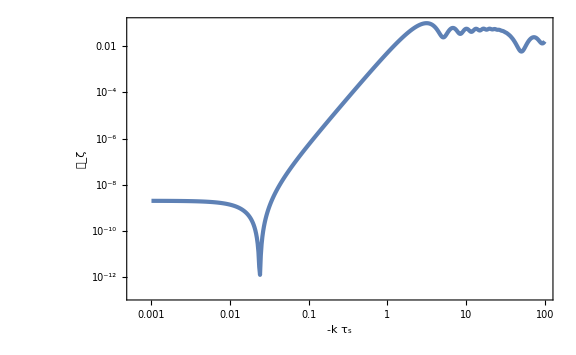

```mathematica
ListLogLogPlot[calPkList,FrameLabel->{-k Subscript[τ, s],Subscript[𝒫, ζ]}]
```

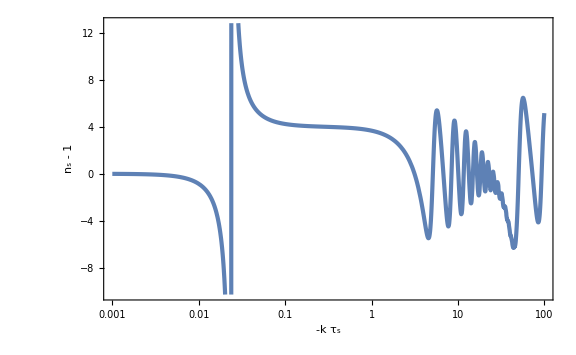

```mathematica
LogLinearPlot[nsm1[k],{k,10^-3,10^2},FrameLabel->{-k Subscript[τ, s],"n_s - 1"}]
```

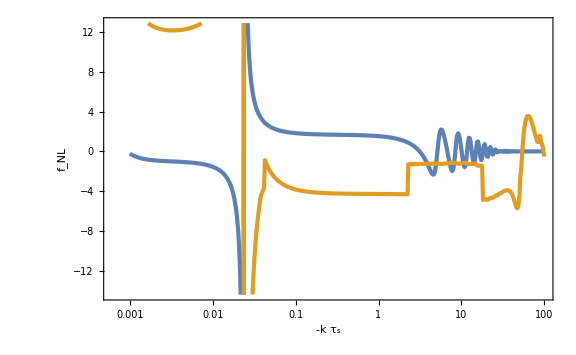

```mathematica
(*ListLogLinearPlot[{fNLsList,fNLeList},FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}]*)
```

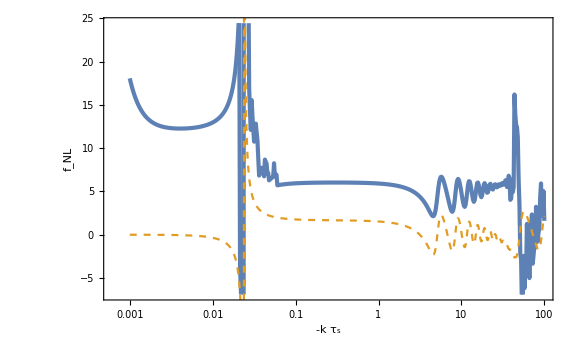

```mathematica
Show[ListLogLinearPlot[fNLList,FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}],LogLinearPlot[5/12 nsm1[k],{k,10^-3,10^2},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```

### kL = 10

```mathematica
kL=10;
τiL=-10^2/kL;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==1/Sqrt[2k],vk'[τi]==-I Sqrt[k/2]}/.{τs->-1,τi->τiL,lnDt->lndt,k->kL},vk[τ],{τ,τiL,-10^-2},WorkingPrecision->30][[1]];
```

```mathematica
ζkL[τ_]=vkL[τ]/z[τ]/.{τs->-1,τ0->-10^5,lnDt->lndt,ϵ0->10^-2};
PζkL[τ_]=Norm[ζkL[τ]]^2;
```

```mathematica
calPkfNLList=ParallelTable[kS=10^lnk;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->τiS,lnDt->lndt,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ]/.{τs->-1,τ0->-10^5,lnDt->lndt,ϵ0->10^-2};
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
fNLs=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[((ϵ[τp]η'[τp])/(τp^2 H^2)/.{τs->-1,τ0->-10^5,lnDt->lndt,ϵ0->10^-2,H->Hs})pktk[-10^-2,τp]],{τp,-3,(*-10^-2*)-1/3},WorkingPrecision->30]//Quiet;
fNLe=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[((ϵ[τp]η'[τp])/(τp^2 H^2)/.{τs->-1,τ0->-10^5,lnDt->lndt,ϵ0->10^-2,H->Hs})pktk[-10^-2,τp]],{τp,-3 10^-lndt,-10^-2},WorkingPrecision->30]//Quiet;
{kS,calPζkS[-10^-2],fNLs,fNLe},{lnk,1,2,10^-2}];//AbsoluteTiming
```

{44.9342,Null}

```mathematica
calPkList=Map[{#[[1]],#[[2]]}&,calPkfNLList];
fNLsList=Map[{#[[1]],#[[3]]}&,calPkfNLList];
fNLeList=Map[{#[[1]],#[[4]]}&,calPkfNLList];
fNLList=Map[{#[[1]],#[[3]]+#[[4]]}&,calPkfNLList];
calPkint[k_]=Interpolation[calPkList][k];
nsm1[k_]=k D[Log[calPkint[k]], k];
```

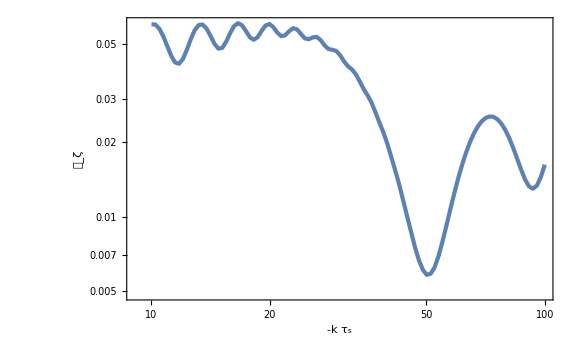

```mathematica
ListLogLogPlot[calPkList,FrameLabel->{-k Subscript[τ, s],Subscript[𝒫, ζ]}]
```

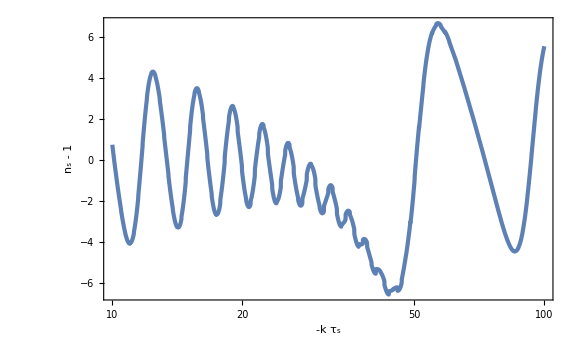

```mathematica
LogLinearPlot[nsm1[k],{k,10,10^2},FrameLabel->{-k Subscript[τ, s],"n_s - 1"}]
```

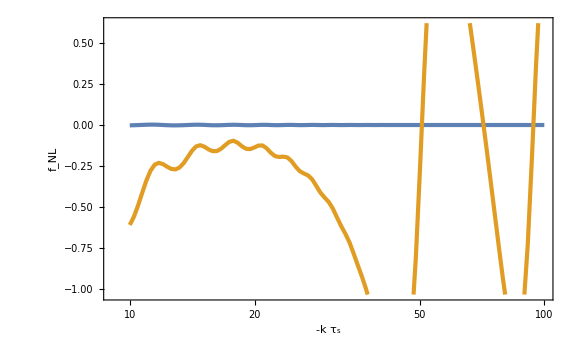

```mathematica
ListLogLinearPlot[{fNLsList,fNLeList},FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}]
```

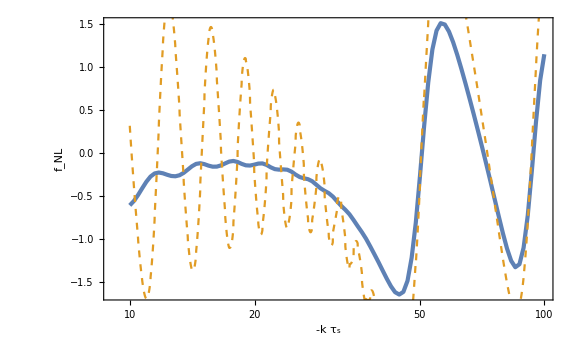

```mathematica
Show[ListLogLinearPlot[fNLList,FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}],LogLinearPlot[5/12 nsm1[k],{k,10,10^2},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```

## Schwinger--Keldysh

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0};
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify
```

-(ⅇ^(ⅈ k τ) H (ⅈ+k τ))/(2 √(k^3 ϵSR))

-1/2 ⅈ ⅇ^(ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkUSRform[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak E^(-I k τ)(1+I k τ)-Bk E^(I k τ)(1-I k τ));
ζkUSRformp[τ_,k_]=D[ζkUSRform[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (Bk ⅇ^(2 ⅈ k τ) (3 ⅈ+3 k τ-ⅈ k^2 τ^2)+Ak (-3 ⅈ+3 k τ+ⅈ k^2 τ^2)) τs^3)/(2 √(k^3 ϵSR) τ^4)

```mathematica
SR2USR=Simplify[Solve[{ζkSR1[τs,k]==ζkUSRform[τs,k],ζkSR1p[τs,k]==ζkUSRformp[τs,k]}//Simplify,{Ak,Bk},Assumptions->{ϵSR>0}][[1]],Assumptions->{ϵSR>0}]
```

{Ak→1+(3 ⅈ)/(2 k^3 τs^3)+(3 ⅈ)/(2 k τs),Bk→-(3 ⅈ ⅇ^(-2 ⅈ k τs) (-ⅈ+k τs)^2)/(2 k^3 τs^3)}

```mathematica
ζkUSR[τ_,τs_,k_]=ζkUSRform[τ,k]/.SR2USR//Simplify
ζkUSRp[τ_,τs_,k_]=D[ζkUSR[τ,τs,k], τ]//Simplify
```

(ⅇ^(-ⅈ k (τ+2 τs)) H (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τs)^2-ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^3)

(ⅇ^(-ⅈ k (τ+2 τs)) H (-3 ⅇ^(2 ⅈ k τ) (-3+3 ⅈ k τ+k^2 τ^2) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^4)

```mathematica
ζkUSRs[τ_,τs_,k_]=Conjugate[ζkUSR[τ,τs,k]//ExpToTrig//Expand]//FullSimplify
ζkUSRsp[τ_,τs_,k_]=D[ζkUSRs[τ,τs,k], τ]//Simplify
```

-(ⅇ^(ⅈ k τs) H (k (τ (-3 ⅈ-3 k τs+k^3 τs^3)+τs (3 ⅈ+k τs (3+ⅈ k τs))) Cos[k (τ-τs)]+(3 ⅈ+k τs (3+k (-k τs^2+τ (3 ⅈ+k τs (3+ⅈ k τs))))) Sin[k (τ-τs)]))/(2 √(k^9 ϵSR) τ^3)

1/(2 √(k^9 ϵSR) τ^4)ⅇ^(ⅈ k τs) H (k (3 τs (3 ⅈ+3 k τs+ⅈ k^2 τs^2)-ⅈ k^2 τ^2 τs (3-3 ⅈ k τs+k^2 τs^2)+3 τ (-3 ⅈ-3 k τs+k^3 τs^3)) Cos[k (τ-τs)]+(9 ⅈ-3 ⅈ k^2 τ (τ-3 τs)+9 k τs+3 ⅈ k^4 τ τs^3+k^5 τ^2 τs^3-3 k^3 τs (τ^2-3 τ τs+τs^2)) Sin[k (τ-τs)])

```mathematica
ζkSR2form[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^3 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ));
ζkSR2formp[τ_,k_]=D[ζkSR2form[τ,k], τ]//Simplify
```

(ⅈ ⅇ^(-ⅈ k τ) (Ck-Dk ⅇ^(2 ⅈ k τ)) H √(k/ϵSR) τ τs^3)/(2 τe^3)

```mathematica
USR2SR=Solve[{ζkUSR[τe,τs,k]==ζkSR2form[τe,k],ζkUSRp[τe,τs,k]==ζkSR2formp[τe,k]},{Ck,Dk}][[1]]//FullSimplify
```

{Ck→(ⅇ^(-ⅈ k (τe+4 τs)) √ϵSR (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ+k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(4 k^(11/2) τe^3 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) τs^3),Dk→(ⅇ^(-2 ⅈ k (τe+τs)) (3 ⅇ^(2 ⅈ k τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(4 k^6 τe^3 τs^3)}

```mathematica
ζkSR2[τ_,τs_,τe_,k_]=ζkSR2form[τ,k]/.USR2SR//Simplify
ζkSR2p[τ_,τs_,τe_,k_]=D[ζkSR2[τ,τs,τe,k], τ]//Simplify
```

1/(8 k^(15/2) τe^6)ⅈ ⅇ^(-ⅈ k τ) H (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ+k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe))

(ⅇ^(-ⅈ k τ) H τ (-9 ⅈ ⅇ^(2 ⅈ k (τe-τs)) √(k ϵSR) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+9 ⅇ^(2 ⅈ k (τe-τs)) k^(3/2) √ϵSR τe (ⅈ+k τe)^2 (-ⅈ+k τs)^2-3 ⅈ ⅇ^(2 ⅈ k (τ-τs)) (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+√(k ϵSR) (3+3 k^2 τe^2+2 ⅈ k^3 τe^3) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)+3 ⅇ^(2 ⅈ k (τ-τe)) (-ⅈ+k τe)^2 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))+k^(3/2) √ϵSR τe (3 ⅈ-k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(8 k^(11/2) √ϵSR τe^6 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe))

```mathematica
ζkSR2s[τ_,τs_,τe_,k_]=Conjugate[ζkSR2[τ,τs,τe,k]//ExpToTrig]//FullSimplify
ζkSR2sp[τ_,τs_,τe_,k_]=D[ζkSR2s[τ,τs,τe,k], τ]//Simplify
```

-1/(8 k^(15/2) τe^6)ⅈ ⅇ^(ⅈ k τ) H (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe))

(ⅇ^(ⅈ k τ) H τ (9 ⅈ ⅇ^(-2 ⅈ k (τe-τs)) √(k ϵSR) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+9 ⅇ^(-2 ⅈ k (τe-τs)) k^(3/2) √ϵSR τe (-ⅈ+k τe)^2 (ⅈ+k τs)^2-3 ⅇ^(-2 ⅈ k (τ-τs)) (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (ⅈ+k τs)^2+3 ⅇ^(-2 ⅈ k (τ-τe)) (ⅈ+k τe)^2 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)+ⅈ √(k ϵSR) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs))+k^(3/2) √ϵSR τe (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs))))/(8 k^(11/2) √ϵSR τe^6 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe))

```mathematica
PkSR2[τ_,τs_,τe_,k_]=ζkSR2s[τ,τs,τe,k]ζkSR2[τ,τs,τe,k]//Simplify
```

1/(64 k^15 τe^12)H^2 (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe)) (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ+k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe))

```mathematica
calPkSR2[τ_,τs_,τe_,k_]=k^3/(2 π^2)PkSR2[τ,τs,τe,k];
calPkSR2p[τ_,τs_,τe_,k_]=D[calPkSR2[τ,τs,τe,k], τ];
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)]//FullSimplify;lndt
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];Hs
```

1+Log[5]/(6 Log[10])

π/(25000 √10)

```mathematica
lndt//N
```

1.1165

```mathematica
10^lndt
```

10 5^(1/6)

```mathematica
10^(6lndt)//N
```

5.×10^6

```mathematica
LogLogPlot[calPkSR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

-Graphics-

```mathematica
nsm1SR2[τ_,τs_,τe_,k_]=k D[Log[calPkSR2[τ,τs,τe,k]], k];
```

```mathematica
LogLinearPlot[nsm1SR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[n, "s"]-1}]
```

-Graphics-

```mathematica
PkUSR[τ_,τs_,k_]=ζkUSRs[τ,τs,k]ζkUSR[τ,τs,k]//Simplify;
PkUSRp[τ_,τs_,k_]=D[PkUSR[τ,τs,k], τ]//Simplify;
calPkUSR[τ_,τs_,k_]=k^3/(2 π^2)PkUSR[τ,τs,k];
calPkUSRp[τ_,τs_,k_]=D[calPkUSR[τ,τs,k], τ];
nsm1USR[τ_,τs_,k_]=k/calPkUSR[τ,τs,k] D[calPkUSR[τ,τs,k], k]//Simplify;
```

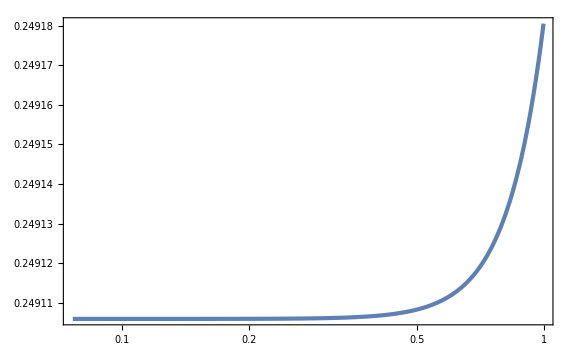

```mathematica
LogLinearPlot[1/(τp^2 H^2)ϵSR(τp/τs)^6 Im[ζkSR2[0,τs,τe,k]ζkUSRp[-τp,τs,k]]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},{τp,10^-lndt,1},WorkingPrecision->30,PlotRange->Full]
```

```mathematica
AbsoluteTiming[GCC21[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2[τ,τs,τe,k]ζkSR1s[τp,k]]//Simplify;
GCC2U[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2[τ,τs,τe,k]ζkUSRs[τp,τs,k]]//Simplify;
GCC22[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2[τ,τs,τe,k]ζkSR2s[τp,τs,τe,k]]//Simplify;
GCCU1[τ_,τp_,τs_,k_]=Re[ζkUSR[τ,τs,k]ζkSR1s[τp,k]]//Simplify;
GCCUU[τ_,τp_,τs_,k_]=Re[ζkUSR[τ,τs,k]ζkUSRs[τp,τs,k]]//Simplify;
GCD21[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2[τ,τs,τe,k]ζkSR1s[τp,k]]//Simplify;
GCD2U[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2[τ,τs,τe,k]ζkUSRs[τp,τs,k]]//Simplify;
GCD22[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2[τ,τs,τe,k]ζkSR2s[τp,τs,τe,k]]//Simplify;
GCDU1[τ_,τp_,τs_,k_]=2I Im[ζkUSR[τ,τs,k]ζkSR1s[τp,k]]//Simplify;
GCDUU[τ_,τp_,τs_,k_]=2I Im[ζkUSR[τ,τs,k]ζkUSRs[τp,τs,k]]//Simplify;
GCc21[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2[τ,τs,τe,k]ζkSR1sp[τp,k]]//Simplify;
GCc2U[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2[τ,τs,τe,k]ζkUSRsp[τp,τs,k]]//Simplify;
GCc22[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2[τ,τs,τe,k]ζkSR2sp[τp,τs,τe,k]]//Simplify;
GCcU1[τ_,τp_,τs_,k_]=Re[ζkUSR[τ,τs,k]ζkSR1sp[τp,k]]//Simplify;
GCcUU[τ_,τp_,τs_,k_]=Re[ζkUSR[τ,τs,k]ζkUSRsp[τp,τs,k]]//Simplify;
GcC21[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2p[τ,τs,τe,k]ζkSR1s[τp,k]]//Simplify;
GcC2U[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2p[τ,τs,τe,k]ζkUSRs[τp,τs,k]]//Simplify;
GcC22[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2p[τ,τs,τe,k]ζkSR2s[τp,τs,τe,k]]//Simplify;
GcCU1[τ_,τp_,τs_,k_]=Re[ζkUSRp[τ,τs,k]ζkSR1s[τp,k]]//Simplify;
GcCUU[τ_,τp_,τs_,k_]=Re[ζkUSRp[τ,τs,k]ζkUSRs[τp,τs,k]]//Simplify;
GCd21[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2[τ,τs,τe,k]ζkSR1sp[τp,k]]//Simplify;
GCd2U[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2[τ,τs,τe,k]ζkUSRsp[τp,τs,k]]//Simplify;
GCd22[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2[τ,τs,τe,k]ζkSR2sp[τp,τs,τe,k]]//Simplify;
GCdU1[τ_,τp_,τs_,k_]=2I Im[ζkUSR[τ,τs,k]ζkSR1sp[τp,k]]//Simplify;
GCdUU[τ_,τp_,τs_,k_]=2I Im[ζkUSR[τ,τs,k]ζkUSRsp[τp,τs,k]]//Simplify;
GcD21[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2p[τ,τs,τe,k]ζkSR1s[τp,k]]//Simplify;
GcD2U[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2p[τ,τs,τe,k]ζkUSRs[τp,τs,k]]//Simplify;
GcD22[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2p[τ,τs,τe,k]ζkSR2s[τp,τs,τe,k]]//Simplify;
GcDU1[τ_,τp_,τs_,k_]=2I Im[ζkUSRp[τ,τs,k]ζkSR1s[τp,k]]//Simplify;
GcDUU[τ_,τp_,τs_,k_]=2I Im[ζkUSRp[τ,τs,k]ζkUSRs[τp,τs,k]]//Simplify;
Gcc21[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2p[τ,τs,τe,k]ζkSR1sp[τp,k]]//Simplify;
Gcc2U[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2p[τ,τs,τe,k]ζkUSRsp[τp,τs,k]]//Simplify;
Gcc22[τ_,τp_,τs_,τe_,k_]=Re[ζkSR2p[τ,τs,τe,k]ζkSR2sp[τp,τs,τe,k]]//Simplify;
GccU1[τ_,τp_,τs_,k_]=Re[ζkUSRp[τ,τs,k]ζkSR1sp[τp,k]]//Simplify;
GccUU[τ_,τp_,τs_,k_]=Re[ζkUSRp[τ,τs,k]ζkUSRsp[τp,τs,k]]//Simplify;
Gcd21[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2p[τ,τs,τe,k]ζkSR1sp[τp,k]]//Simplify;
Gcd2U[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2p[τ,τs,τe,k]ζkUSRsp[τp,τs,k]]//Simplify;
Gcd22[τ_,τp_,τs_,τe_,k_]=2I Im[ζkSR2p[τ,τs,τe,k]ζkSR2sp[τp,τs,τe,k]]//Simplify;
GcdU1[τ_,τp_,τs_,k_]=2I Im[ζkUSRp[τ,τs,k]ζkSR1sp[τp,k]]//Simplify;
GcdUU[τ_,τp_,τs_,k_]=2I Im[ζkUSRp[τ,τs,k]ζkUSRsp[τp,τs,k]]//Simplify;]
```

{55.0919,Null}

```mathematica
N[calPkUSR[τs,τs,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
N[calPkUSR[τe,τs,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
```

2.000002×10^-9

1.99642788684575582503502702402×10^-9+0. ⅈ

```mathematica
N[(-2I)/(τs^2 H^2)ϵSR(τs/τs)^6 GCd2U[0,τs,τs,τe,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
N[(-2I)/(τe^2 H^2)ϵSR(τe/τs)^6 GCd2U[0,τe,τs,τe,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
```

0.999702023121048247204725122104

0.999999999025327420880707302571

```mathematica
N[-I/(τs^2 H^2)ϵSR(τs/τs)^6 GCd2U[0,τs,τs,τe,k]calPkUSR[τs,τs,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
N[-I/(τe^2 H^2)ϵSR(τe/τs)^6 GCd2U[0,τe,τs,τe,k]calPkUSR[τe,τs,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
```

9.99703022823071368252972326829×10^-10

9.9821394244994615376869737549×10^-10+0. ⅈ

```mathematica
N[-I/(τs^2 H^2)ϵSR(τs/τs)^6 Δηs GCd2U[0,τs,τs,τe,k]calPkUSR[τs,τs,k]+-I/(τe^2 H^2)ϵSR(τe/τs)^6 Δηe GCd2U[0,τe,τs,τe,k]calPkUSR[τe,τs,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs,Δηs->-6,Δηe->6},30]
```

-8.93448223875128690564970803291×10^-12+0. ⅈ

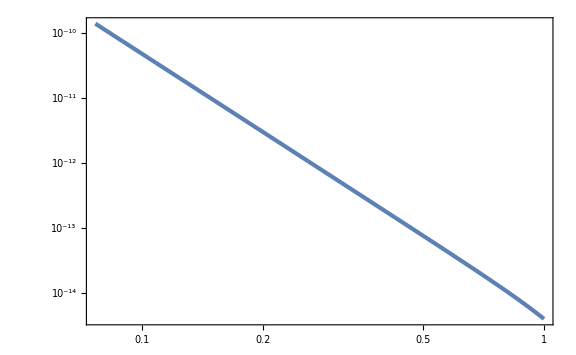

```mathematica
LogLogPlot[{Abs[calPkUSRp[-x,τs,k]/.{τs->-1,k->10^-3,ϵSR->10^-2,H->Hs}]},{x,10^-lndt,1},WorkingPrecision->30,PlotRange->Full]
```

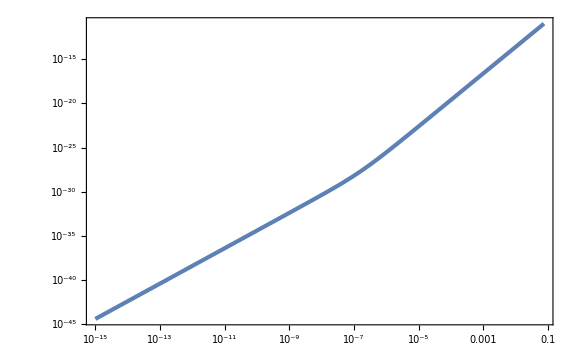

```mathematica
LogLogPlot[{Abs[x calPkSR2p[-x,τs,τe,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs}]},{x,10^-15,10^-lndt},WorkingPrecision->30,PlotRange->Full]
```

```mathematica
N[-I/(τs^2 H^2)ϵSR(τs/τs)^6 GCD2U[0,τs,τs,τe,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
N[-I/(τe^2 H^2)ϵSR(τe/τs)^6 GCD2U[0,τe,τs,τe,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
```

-745.189252086301834221219642755

-0.0127454081814086069741618811037

```mathematica
N[-I/(τs^2 H^2)ϵSR(τs/τs)^6 GCD2U[0,τs,τs,τe,k]/.{τs->-1,τe->-10^-lndt,k->10^-4,ϵSR->10^-2,H->Hs},30]
N[-I/(τe^2 H^2)ϵSR(τe/τs)^6 GCD2U[0,τe,τs,τe,k]/.{τs->-1,τe->-10^-lndt,k->10^-4,ϵSR->10^-2,H->Hs},30]
```

-745.189325095793592481054412998

-0.0127454081887876312983546041021

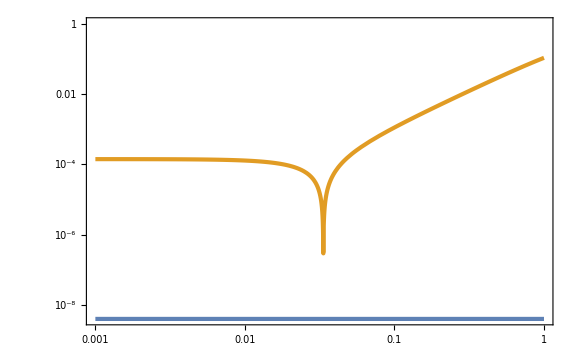

```mathematica
LogLogPlot[{Abs[calPkUSRp[τs,τs,k]/k^2/.{τs->-1,τe->-10^-lndt,ϵSR->10^-2,H->Hs}],Abs[calPkUSRp[τe,τs,k]/k^2/.{τs->-1,τe->-10^-lndt,ϵSR->10^-2,H->Hs}]},{k,10^-3,1},WorkingPrecision->30]
```

```mathematica
N[-I/(τs^2 H^2)ϵSR(τs/τs)^6 GCD2U[0,τs,τs,τe,k]calPkUSRp[τs,τs,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
N[-I/(τe^2 H^2)ϵSR(τe/τs)^6 GCD2U[0,τe,τs,τe,k]calPkUSRp[τe,τs,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs},30]
```

2.98075700834520733688487857102×10^-12

1.78725462506676068747879183345×10^-12+0. ⅈ

```mathematica
N[-I/(τs^2 H^2)ϵSR(τs/τs)^6 Δηs GCD2U[0,τs,τs,τe,k]calPkUSRp[τs,τs,k]+-I/(τe^2 H^2)ϵSR(τe/τs)^6 Δηe GCD2U[0,τe,τs,τe,k]calPkUSRp[τe,τs,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs,Δηs->-6,Δηe->6},30]
```

-7.16101429967067989643652042541×10^-12+0. ⅈ

```mathematica
N[-I/(τs^2 H^2)ϵSR(τs/τs)^6 Δηs GCD2U[0,τs,τs,τe,k]calPkUSRp[τs,τs,k]+-I/(τe^2 H^2)ϵSR(τe/τs)^6 Δηe GCD2U[0,τe,τs,τe,k]calPkUSRp[τe,τs,k]/.{τs->-1,τe->-10^-lndt,k->10^-4,ϵSR->10^-2,H->Hs,Δηs->-6,Δηe->6},30]
```

-7.15151812737530430155405748166×10^-14+0. ⅈ

```mathematica
N[τ H calPkSR2p[τ,τs,τe,k]/.{τs->-1,τe->-10^-lndt,k->10^-3,ϵSR->10^-2,H->Hs,τ->10^-10},30]
```

1.58290347851047297554666970439×10^-39+0. ⅈ

```mathematica
fNLbulks1SR2[τ_,τs_,τe_,k_,p_]=5/12 2 I/(τs^2 H^2)ϵSR Δηs 1/(PkSR2[τ,τs,τe,k]PkSR2[τ,τs,τe,p])GCC21[τ,τs,τs,τe,p](GCc21[τ,τs,τs,τe,k]GCD21[τ,τs,τs,τe,k]);
fNLbulks2SR2[τ_,τs_,τe_,k_,p_]=5/12 2 I/(τs^2 H^2)ϵSR Δηs 1/(PkSR2[τ,τs,τe,k]PkSR2[τ,τs,τe,p])GCC21[τ,τs,τs,τe,p](GCd21[τ,τs,τs,τe,k]GCC21[τ,τs,τs,τe,k]);
fNLbulke1SR2[τ_,τs_,τe_,k_,p_]=5/12 2 I/(τe^2 H^2)ϵSR(τe/τs)^6 Δηe 1/(PkSR2[τ,τs,τe,k]PkSR2[τ,τs,τe,p])GCC2U[τ,τe,τs,τe,p](GCc2U[τ,τe,τs,τe,k]GCD2U[τ,τe,τs,τe,k]);
fNLbulke2SR2[τ_,τs_,τe_,k_,p_]=5/12 2 I/(τe^2 H^2)ϵSR(τe/τs)^6 Δηe 1/(PkSR2[τ,τs,τe,k]PkSR2[τ,τs,τe,p])GCC2U[τ,τe,τs,τe,p](GCd2U[τ,τe,τs,τe,k]GCC2U[τ,τe,τs,τe,k]);
fNLHSR2[τ_,τs_,τe_,k_,p_]=5/12 4 I/(τ H^2)ϵSR(τe/τs)^6  (GCd22[τ,τ,τs,τe,k]GCc22[τ,τ,τs,τe,k])/PkSR2[τ,τs,τe,k];
```

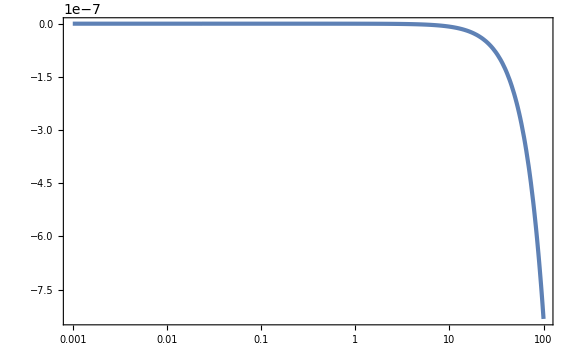

```mathematica
LogLinearPlot[fNLHSR2[-10^-5,-1,-10^-lndt,k,10^-3]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30,PlotRange->Full]
```

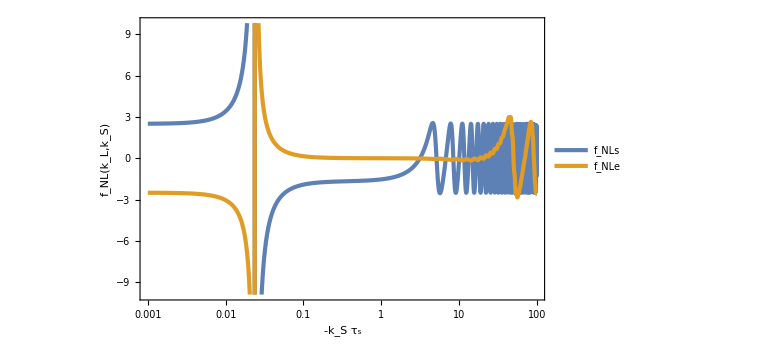

```mathematica
LogLinearPlot[{fNLbulks1SR2[0,-1,-10^-lndt,k,10^-3]+fNLbulks2SR2[0,-1,-10^-lndt,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηs->-6},fNLbulke1SR2[0,-1,-10^-lndt,k,10^-3]+fNLbulke2SR2[0,-1,-10^-lndt,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηe->6}},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],-Subscript[k, "L"] Subscript[τ, "s"]==0.001}},PlotLegends->Placed[LineLegend[{Subscript[f, NLs],Subscript[f, NLe]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->"Row"],{0.7,0.9}]]
```

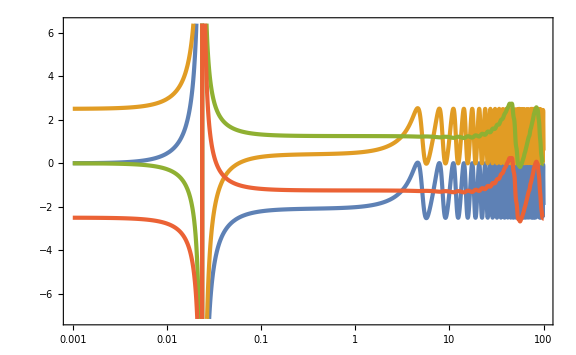

```mathematica
LogLinearPlot[{fNLbulks1SR2[0,-1,-10^-lndt,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηs->-6},fNLbulks2SR2[0,-1,-10^-lndt,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηs->-6},fNLbulke1SR2[0,-1,-10^-lndt,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηe->6},fNLbulke2SR2[0,-1,-10^-lndt,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηe->6}},{k,10^-3,10^2},WorkingPrecision->30]
```

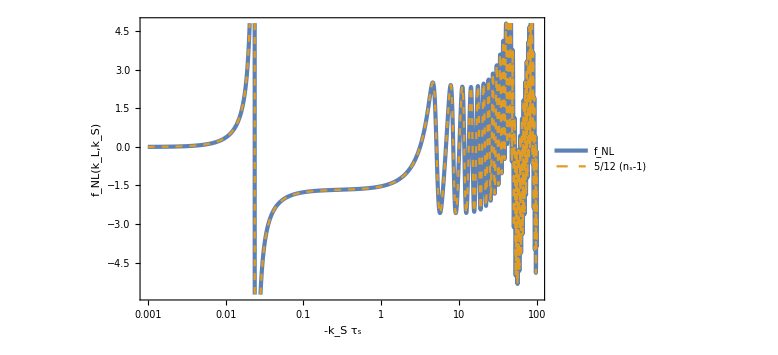

```mathematica
LogLinearPlot[{-5/12 nsm1SR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2},fNLbulksSR2[0,-1,-10^-lndt,k,10^-3]+fNLbulkeSR2[0,-1,-10^-lndt,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηs->-6,Δηe->6}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],-Subscript[k, "L"] Subscript[τ, "s"]==0.001}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(Subscript[n, "s"]-1)},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.15,0.2}]]
```

```mathematica
fNLbulkUSR[τ_,τs_,k_,p_]=5/12 2 I/(τs^2 H^2)ϵSR Δηs (GCcU1[τ,τs,τs,k]GCDU1[τ,τs,τs,k]+GCdU1[τ,τs,τs,k]GCCU1[τ,τs,τs,k])/PkUSR[τ,τs,k](*5/12 2 I/(τs^2 H^2)ϵSR Δηs 1/(PkUSR[τ,τs,k]PkUSR[τ,τs,p])GCCU1[τ,τs,τs,p](GCcU1[τ,τs,τs,k]GCDU1[τ,τs,τs,k]+GCdU1[τ,τs,τs,k]GCCU1[τ,τs,τs,k])*);fNLηUSR[τ_,τs_,k_,p_]=5/12 η(*-5/122 I/(τ^2 H^2)ϵSR(τ/τs)^6 η 1/(PkUSR[τ,τs,k]PkUSR[τ,τs,p])GCCUU[τ,τ,τs,p](GCcUU[τ,τ,τs,k]GCDUU[τ,τ,τs,k]+GCdUU[τ,τ,τs,k]GCCUU[τ,τ,τs,k])*);
fNLHUSR[τ_,τs_,k_,p_]=5/12 4 I/(τ H^2)ϵSR(τ/τs)^6  (GCdUU[τ,τ,τs,k]GCcUU[τ,τ,τs,k])/PkUSR[τ,τs,k](*5/12 4 I/(τ H^2)ϵSR(τ/τs)^6  1/(PkUSR[τ,τs,k]PkUSR[τ,τs,p])GCCUU[τ,τ,τs,p]GCdUU[τ,τ,τs,k]GCcUU[τ,τ,τs,k]*);
```

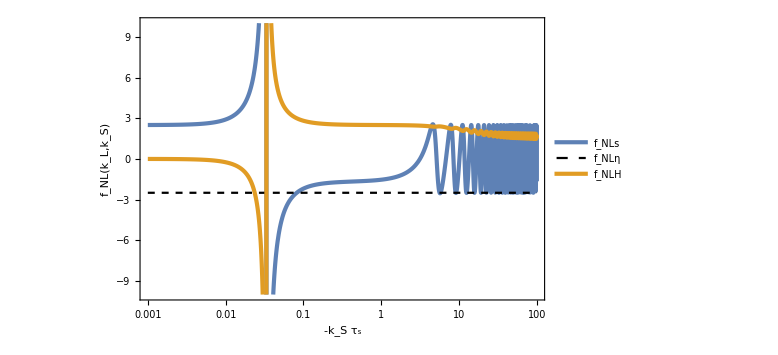

```mathematica
LogLinearPlot[{fNLbulkUSR[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηs->-6},fNLηUSR[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs,η->-6},fNLHUSR[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{{Color[1],AbsoluteThickness[3]},{Black,Dashed},{Color[2],AbsoluteThickness[3]}},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],-Subscript[k, "L"] Subscript[τ, "s"]==0.001}},PlotLegends->Placed[LineLegend[{Subscript[f, NLs],Subscript[f, NLη],Subscript[f, NLH]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->"Row"],{0.7,0.9}]]
```

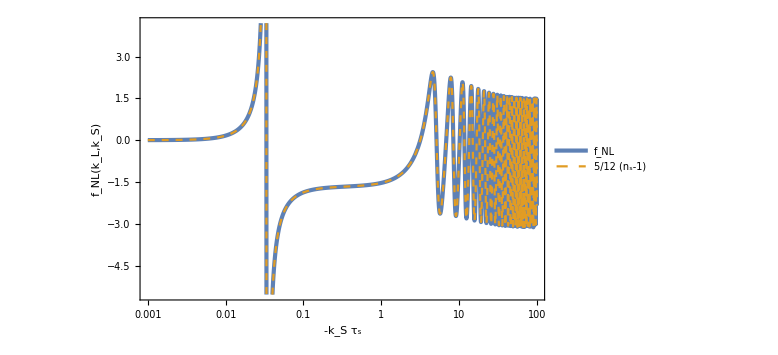

```mathematica
LogLinearPlot[{fNLbulkUSR[-10^-lndt,-1,k,10^-3]+fNLηUSR[-10^-lndt,-1,k,10^-3]+fNLHUSR[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηs->-6,η->-6},-5/12 nsm1USR[-10^-lndt,-1,k]},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],-Subscript[k, "L"] Subscript[τ, "s"]==0.001}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(Subscript[n, "s"]-1)},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.15,0.2}]]
```

```mathematica
fNLpCR[τ_,τs_,k_,p_]=-1/2 5/12 D[(PkUSR[τ,τs,k]nsm1USR[τ,τs,k]), τ]/PkUSRp[τ,τs,k];
```

```mathematica
LogLinearPlot[fNLpCR[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30]
```

-Graphics-

```mathematica
fNLpbulk[τ_,τs_,k_,p_]=5/12 I/(τs^2 H^2)ϵSR Δηs 1/(PkUSR[τ,τs,p]PkUSRp[τ,τs,k])GCCU1[τ,τs,τs,p](GCcU1[τ,τs,τs,k]GcDU1[τ,τs,τs,k]+GccU1[τ,τs,τs,k]GCDU1[τ,τs,τs,k]+GCdU1[τ,τs,τs,k]GcCU1[τ,τs,τs,k]+GcdU1[τ,τs,τs,k]GCCU1[τ,τs,τs,k]);
fNLpB1[τ_,τs_,k_,p_]=5/12 2(9I)/(τ^3 H^2) 1/(PkUSR[τ,τs,p]PkUSRp[τ,τs,k])GCCUU[τ,τ,τs,p]GCCUU[τ,τ,τs,k]GcDUU[τ,τ,τs,k];
fNLpB2[τ_,τs_,k_,p_]=5/12 2(k^2 I)/(τ H^2)1/(PkUSR[τ,τs,p]PkUSRp[τ,τs,k])GCCUU[τ,τ,τs,p]GCCUU[τ,τ,τs,k]GcDUU[τ,τ,τs,k];
fNLpBϵ1[τ_,τs_,k_,p_]=-5/12 2(k^2 I)/(τ H^2)ϵSR(τ/τs)^6 1/(PkUSR[τ,τs,p]PkUSRp[τ,τs,k])GCCUU[τ,τ,τs,p]GCCUU[τ,τ,τs,k]GcDUU[τ,τ,τs,k];
fNLpBϵ2[τ_,τs_,k_,p_]=5/12 2 I/(τ H^2)ϵSR(τ/τs)^6 1/(PkUSR[τ,τs,p]PkUSRp[τ,τs,k])GCCUU[τ,τ,τs,p]GCdUU[τ,τ,τs,k]GccUU[τ,τ,τs,k];
fNLpBη[τ_,τs_,k_,p_]=-5/12 I/(τ^2 H^2)ϵSR(τ/τs)^6 η 1/(PkUSR[τ,τs,p]PkUSRp[τ,τs,k])GCCUU[τ,τ,τs,p](GcCUU[τ,τ,τs,k]GCdUU[τ,τ,τs,k](*+GCcUU[τ,τ,τs,k]GcDUU[τ,τ,τs,k]*));
```

```mathematica
LogLinearPlot[{fNLpbulk[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηs->-6},fNLpBϵ1[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs},fNLpBϵ2[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs},fNLpBη[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs,η->-6}},{k,10^-3,10^2},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLinearPlot[{fNLpCR[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs},fNLpbulk[-10^-lndt,-1,k,10^-3]+fNLpBϵ1[-10^-lndt,-1,k,10^-3]+fNLpBϵ2[-10^-lndt,-1,k,10^-3]+fNLpBη[-10^-lndt,-1,k,10^-3]/.{ϵSR->10^-2,H->Hs,Δηs->-6,η->-6}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed}]
```

-Graphics-

```mathematica
GRxp[τe_,τs_,k_]=Im[ζkUSR[τe,τs,k]ζkSR1sp[τs,k]//ExpToTrig//Expand]//Simplify
GSpx[τe_,τs_,k_]=Re[ζkUSRp[τe,τs,k]ζkSR1s[τs,k]//ExpToTrig//Expand]//Simplify
GRpx[τe_,τs_,k_]=Im[ζkUSRp[τe,τs,k]ζkSR1s[τs,k]//ExpToTrig//Expand]//Simplify
GSxp[τe_,τs_,k_]=Re[ζkUSR[τe,τs,k]ζkSR1sp[τs,k]//ExpToTrig//Expand]//Simplify
GRxx[τe_,τs_,k_]=Im[ζkUSR[τe,τs,k]ζkSR1s[τs,k]//ExpToTrig//Expand]//Simplify
GSxx[τe_,τs_,k_]=Re[ζkUSR[τe,τs,k]ζkSR1s[τs,k]//ExpToTrig//Expand]//Simplify
GRpp[τe_,τs_,k_]=Im[ζkUSRp[τe,τs,k]ζkSR1sp[τs,k]//ExpToTrig//Expand]//Simplify
GSpp[τe_,τs_,k_]=Re[ζkUSRp[τe,τs,k]ζkSR1sp[τs,k]//ExpToTrig//Expand]//Simplify
```

(H^2 τs^2 (k (3 τs+τe (-3+k^2 τs^2)) Cos[k (τe-τs)]+(3+k^2 (3 τe-τs) τs) Sin[k (τe-τs)]))/(4 k^3 ϵSR τe^3)

-1/(4 k^6 ϵSR τe^4)H^2 (-k (-3 τs (3+4 k^2 τs^2)+k^2 τe^2 τs (3+4 k^2 τs^2)+τe (9+9 k^2 τs^2-3 k^4 τs^4)) Cos[k (τe-τs)]+(9+k^6 τe^2 τs^4-3 k^4 τs^2 (τe^2-4 τe τs+τs^2)+k^2 (-3 τe^2+9 τe τs+9 τs^2)) Sin[k (τe-τs)])

-(H^2 τs^3 (k (3 τe-3 τs+k^2 τe^2 τs) Cos[k (τe-τs)]+(-3+k^2 τe (τe-3 τs)) Sin[k (τe-τs)]))/(4 k^3 ϵSR τe^4)

(H^2 τs (k (-3 τe+3 τs+k^2 τs^3) Cos[k (τe-τs)]+(3+3 k^2 τe τs+k^4 τe τs^3) Sin[k (τe-τs)]))/(4 k^4 ϵSR τe^3)

-(H^2 τs^3 (-k (τe-τs) Cos[k (τe-τs)]+(1+k^2 τe τs) Sin[k (τe-τs)]))/(4 k^3 ϵSR τe^3)

(H^2 (k (τs (3+4 k^2 τs^2)+τe (-3-3 k^2 τs^2+k^4 τs^4)) Cos[k (τe-τs)]+(3+k^4 (4 τe-τs) τs^3+3 k^2 τs (τe+τs)) Sin[k (τe-τs)]))/(4 k^6 ϵSR τe^3)

-(H^2 τs^2 (-3 k (τe-τs) (3+k^2 τe τs) Cos[k (τe-τs)]+(9+k^4 τe^2 τs^2-3 k^2 (τe^2-3 τe τs+τs^2)) Sin[k (τe-τs)]))/(4 k^3 ϵSR τe^4)

(H^2 τs (k (9 τe-3 τs (3+k^2 τs^2)+k^2 τe^2 τs (3+k^2 τs^2)) Cos[k (τe-τs)]-3 (3-k^2 τe (τe-3 τs)+k^4 τe τs^3) Sin[k (τe-τs)]))/(4 k^4 ϵSR τe^4)

```mathematica
PxpRUSR[τ_,τs_,k_]=Re[ζkUSR[τ,τs,k]ζkUSRsp[τ,τs,k]//ExpToTrig//Expand]//Simplify

PxpIUSR[τ_,τs_,k_]=Im[ζkUSR[τ,τs,k]ζkUSRsp[τ,τs,k]//ExpToTrig//Expand]//Simplify
calPxpRUSR[τ_,τs_,k_]=k^3/(2 π^2)PxpRUSR[τ,τs,k];
PpUSR[τ_,τs_,k_]=ζkUSRp[τ,τs,k]ζkUSRsp[τ,τs,k]//Simplify
calPpUSR[τ_,τs_,k_]=k^3/(2 π^2)PpUSR[τ,τs,k];
```

1/(8 k^9 ϵSR τ^7)H^2 (-((3+2 k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6))+3 (9-12 k^2 τ (τ-3 τs)+2 k^8 τ^3 τs^5-4 k^6 τ τs^3 (2 τ^2-7 τ τs+3 τs^2)-3 k^4 (2 τ^3 τs-16 τ τs^3+7 τs^4)) Cos[2 k (τ-τs)]+3 k (6 τs (-3-4 k^2 τs^2+k^4 τs^4)-8 k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)-6 τ (-3+7 k^4 τs^4)+k^2 τ^3 (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)])

(H^2 τs^6)/(4 ϵSR τ^4)

1/(8 k^9 ϵSR τ^8)ⅇ^(-ⅈ k (τ+τs)) H^2 (-3 ⅇ^(2 ⅈ k τ) (-3+3 ⅈ k τ+k^2 τ^2) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)) (k (3 τs (3 ⅈ+3 k τs+ⅈ k^2 τs^2)-ⅈ k^2 τ^2 τs (3-3 ⅈ k τs+k^2 τs^2)+3 τ (-3 ⅈ-3 k τs+k^3 τs^3)) Cos[k (τ-τs)]+(9 ⅈ-3 ⅈ k^2 τ (τ-3 τs)+9 k τs+3 ⅈ k^4 τ τs^3+k^5 τ^2 τs^3-3 k^3 τs (τ^2-3 τ τs+τs^2)) Sin[k (τ-τs)])

```mathematica
LogLogPlot[{Abs[calPxpRUSR[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}],calPpUSR[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}},{k,10^-3,10^4},WorkingPrecision->30]
```

-Graphics-

```mathematica
nsxpUSR[τ_,τs_,k_]=k/calPxpRUSR[τ,τs,k] D[calPxpRUSR[τ,τs,k], k]//Simplify;
nspUSR[τ_,τs_,k_]=k/calPpUSR[τ,τs,k] D[calPpUSR[τ,τs,k], k]//Simplify;
```

```mathematica
fNLbulksUSR[τ_,τs_,k_]=-5/6 1/(τs^2 H^2)ϵSR Δηs (GRpx[τ,τs,k]GSxp[τ,τs,k]+GRxp[τ,τs,k]GSpx[τ,τs,k]+GRxx[τ,τs,k]GSpp[τ,τs,k]+GRpp[τ,τs,k]GSxx[τ,τs,k])/PxpRUSR[τ,τs,k]//Simplify
```

(5 Δηs (3 (3+2 k^2 τ^2) (3+4 k^2 τs^2+k^4 τs^4)+(-27+8 k^8 τ^2 τs^5 (-τ+τs)+18 k^2 (2 τ^2-6 τ τs+τs^2)-6 k^6 τs^3 (-2 τ^3+10 τ^2 τs-8 τ τs^2+τs^3)+3 k^4 τs (6 τ^3-8 τ^2 τs-24 τ τs^2+15 τs^3)) Cos[2 k (τ-τs)]+k (6 τs (9+6 k^2 τs^2-4 k^4 τs^4)+8 k^2 τ^2 τs (-9-6 k^2 τs^2+4 k^4 τs^4)-6 τ (9-6 k^2 τs^2-15 k^4 τs^4+2 k^6 τs^6)+k^2 τ^3 (9-6 k^2 τs^2-15 k^4 τs^4+2 k^6 τs^6)) Sin[2 k (τ-τs)]))/(12 (-((3+2 k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6))+3 (9-12 k^2 τ (τ-3 τs)+2 k^8 τ^3 τs^5-4 k^6 τ τs^3 (2 τ^2-7 τ τs+3 τs^2)-3 k^4 (2 τ^3 τs-16 τ τs^3+7 τs^4)) Cos[2 k (τ-τs)]+3 k (6 τs (-3-4 k^2 τs^2+k^4 τs^4)-8 k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)-6 τ (-3+7 k^4 τs^4)+k^2 τ^3 (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)]))

```mathematica
fNLHUSR[τ_,τs_,k_]=-5/3 1/(τ H^2)ϵSR (τ/τs)^6(PxpIUSR[τ,τs,k]PpUSR[τ,τs,k])/PxpRUSR[τ,τs,k]//Simplify
```

-((5 ⅇ^(-ⅈ k (τ+τs)) (-3 ⅇ^(2 ⅈ k τ) (-3+3 ⅈ k τ+k^2 τ^2) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)) (k (3 τs (3 ⅈ+3 k τs+ⅈ k^2 τs^2)-ⅈ k^2 τ^2 τs (3-3 ⅈ k τs+k^2 τs^2)+3 τ (-3 ⅈ-3 k τs+k^3 τs^3)) Cos[k (τ-τs)]+(9 ⅈ-3 ⅈ k^2 τ (τ-3 τs)+9 k τs+3 ⅈ k^4 τ τs^3+k^5 τ^2 τs^3-3 k^3 τs (τ^2-3 τ τs+τs^2)) Sin[k (τ-τs)]))/(12 (-((3+2 k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6))+3 (9-12 k^2 τ (τ-3 τs)+2 k^8 τ^3 τs^5-4 k^6 τ τs^3 (2 τ^2-7 τ τs+3 τs^2)-3 k^4 (2 τ^3 τs-16 τ τs^3+7 τs^4)) Cos[2 k (τ-τs)]+3 k (6 τs (-3-4 k^2 τs^2+k^4 τs^4)-8 k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)-6 τ (-3+7 k^4 τs^4)+k^2 τ^3 (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)])))

```mathematica
LogLinearPlot[{fNLbulksUSR[-10^-lndt,-1,k]/.{Δηs->-6},fNLHUSR[-10^-lndt,-1,k]},{k,10^-3,10^2},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLinearPlot[{-5/12 nsxpUSR[-10^-lndt,-1,k],fNLbulksUSR[-10^-lndt,-1,k]-5/4+fNLHUSR[-10^-lndt,-1,k]/.{Δηs->-6}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed}]
```

-Graphics-

## One-loop

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,q>0,xe>0,x>0};
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify
```

-(ⅇ^(ⅈ k τ) H (ⅈ+k τ))/(2 √(k^3 ϵSR))

-1/2 ⅈ ⅇ^(ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkUSRform[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak E^(-I k τ)(1+I k τ)-Bk E^(I k τ)(1-I k τ));
ζkUSRformp[τ_,k_]=D[ζkUSRform[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (Bk ⅇ^(2 ⅈ k τ) (3 ⅈ+3 k τ-ⅈ k^2 τ^2)+Ak (-3 ⅈ+3 k τ+ⅈ k^2 τ^2)) τs^3)/(2 √(k^3 ϵSR) τ^4)

```mathematica
SR2USR=Simplify[Solve[{ζkSR1[τs,k]==ζkUSRform[τs,k],ζkSR1p[τs,k]==ζkUSRformp[τs,k]}//Simplify,{Ak,Bk},Assumptions->{ϵSR>0}][[1]],Assumptions->{ϵSR>0}]
```

{Ak→1+(3 ⅈ)/(2 k^3 τs^3)+(3 ⅈ)/(2 k τs),Bk→-(3 ⅈ ⅇ^(-2 ⅈ k τs) (-ⅈ+k τs)^2)/(2 k^3 τs^3)}

```mathematica
ζkUSR[τ_,τs_,k_]=ζkUSRform[τ,k]/.SR2USR//Simplify
ζkUSRp[τ_,τs_,k_]=D[ζkUSR[τ,τs,k], τ]//Simplify
```

(ⅇ^(-ⅈ k (τ+2 τs)) H (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τs)^2-ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^3)

(ⅇ^(-ⅈ k (τ+2 τs)) H (-3 ⅇ^(2 ⅈ k τ) (-3+3 ⅈ k τ+k^2 τ^2) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-3 ⅈ+3 k τ+ⅈ k^2 τ^2) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 k^(9/2) √ϵSR τ^4)

```mathematica
ζkUSRs[τ_,τs_,k_]=Conjugate[ζkUSR[τ,τs,k]//ExpToTrig]//FullSimplify
ζkUSRsp[τ_,τs_,k_]=D[ζkUSRs[τ,τs,k], τ]//Simplify
```

(ⅇ^(ⅈ k (τ+2 τs)) H (-3 ⅈ ⅇ^(-2 ⅈ k τ) (-ⅈ+k τ) (ⅈ+k τs)^2-ⅇ^(-2 ⅈ k τs) (ⅈ+k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(4 √(k^9 ϵSR) τ^3)

(ⅇ^(-ⅈ k τ) H (-3 ⅇ^(2 ⅈ k τs) (-3-3 ⅈ k τ+k^2 τ^2) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k τ) (3 ⅈ+3 k τ-ⅈ k^2 τ^2) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)))/(4 √(k^9 ϵSR) τ^4)

```mathematica
ζkSR2form[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^3 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ));
ζkSR2formp[τ_,k_]=D[ζkSR2form[τ,k], τ]//Simplify
```

(ⅈ ⅇ^(-ⅈ k τ) (Ck-Dk ⅇ^(2 ⅈ k τ)) H √(k/ϵSR) τ τs^3)/(2 τe^3)

```mathematica
USR2SR=Solve[{ζkUSR[τe,τs,k]==ζkSR2form[τe,k],ζkUSRp[τe,τs,k]==ζkSR2formp[τe,k]},{Ck,Dk}][[1]]//FullSimplify
```

{Ck→(ⅇ^(-ⅈ k (τe+4 τs)) √ϵSR (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ+k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(4 k^(11/2) τe^3 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) τs^3),Dk→(ⅇ^(-2 ⅈ k (τe+τs)) (3 ⅇ^(2 ⅈ k τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(4 k^6 τe^3 τs^3)}

```mathematica
ζkSR2[τ_,τs_,τe_,k_]=ζkSR2form[τ,k]/.USR2SR//Simplify
ζkSR2p[τ_,τs_,τe_,k_]=D[ζkSR2[τ,τs,τe,k], τ]//Simplify
```

1/(8 k^(15/2) τe^6)ⅈ ⅇ^(-ⅈ k τ) H (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ+k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe))

1/(8 k^(11/2) √ϵSR τe^6 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe))ⅇ^(-ⅈ k τ) H τ (-9 ⅈ ⅇ^(2 ⅈ k (τe-τs)) √(k ϵSR) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+9 ⅇ^(2 ⅈ k (τe-τs)) k^(3/2) √ϵSR τe (ⅈ+k τe)^2 (-ⅈ+k τs)^2-3 ⅈ ⅇ^(2 ⅈ k (τ-τs)) (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+√(k ϵSR) (3+3 k^2 τe^2+2 ⅈ k^3 τe^3) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)+3 ⅇ^(2 ⅈ k (τ-τe)) (-ⅈ+k τe)^2 (√(k ϵSR)+ⅈ √(k^3 ϵSR) τe) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))+k^(3/2) √ϵSR τe (3 ⅈ-k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs)))

```mathematica
ζkSR2s[τ_,τs_,τe_,k_]=Conjugate[ζkSR2[τ,τs,τe,k]//ExpToTrig]//FullSimplify
ζkSR2sp[τ_,τs_,τe_,k_]=D[ζkSR2s[τ,τs,τe,k], τ]//Simplify
```

-1/(8 k^(15/2) τe^6)ⅈ ⅇ^(ⅈ k τ) H (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe))

1/(8 k^(11/2) √ϵSR τe^6 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe))ⅇ^(ⅈ k τ) H τ (9 ⅈ ⅇ^(-2 ⅈ k (τe-τs)) √(k ϵSR) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+9 ⅇ^(-2 ⅈ k (τe-τs)) k^(3/2) √ϵSR τe (-ⅈ+k τe)^2 (ⅈ+k τs)^2-3 ⅇ^(-2 ⅈ k (τ-τs)) (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τe^2+2 k^3 τe^3) (ⅈ+k τs)^2+3 ⅇ^(-2 ⅈ k (τ-τe)) (ⅈ+k τe)^2 (√(k ϵSR)-ⅈ √(k^3 ϵSR) τe) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)+ⅈ √(k ϵSR) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs))+k^(3/2) √ϵSR τe (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (3 ⅈ-k^2 τs^2 (-3 ⅈ+2 k τs)))

```mathematica
PkSR2[τ_,τs_,τe_,k_]=ζkSR2s[τ,τs,τe,k]ζkSR2[τ,τs,τe,k]//Simplify
```

1/(64 k^15 τe^12)H^2 (-(ⅇ^(-2 ⅈ k (τ-τe-τs)) (1+ⅈ k τ) (3 ⅇ^(-2 ⅈ k τe) (3+k^2 τe^2 (3+2 ⅈ k τe)) (ⅈ+k τs)^2-3 ⅈ ⅇ^(-2 ⅈ k τs) (ⅈ+k τe)^2 (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(ⅈ k (τe+4 τs)) √k (1-ⅈ k τ) (1-ⅈ k τe) (-9 ⅇ^(-ⅈ k (3 τe+2 τs)) (-ⅈ+k τe)^2 (ⅈ+k τs)^2+ⅇ^(-ⅈ k (τe+4 τs)) (3 ⅈ+k^2 τe^2 (3 ⅈ+2 k τe)) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(√(k ϵSR)-ⅈ √(k^3 ϵSR) τe)) (-(ⅇ^(2 ⅈ k (τ-τe-τs)) (1-ⅈ k τ) (3 ⅇ^(2 ⅈ k τe) (3+k^2 τe^2 (3-2 ⅈ k τe)) (-ⅈ+k τs)^2+3 ⅈ ⅇ^(2 ⅈ k τs) (-ⅈ+k τe)^2 (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√ϵSR)+(ⅇ^(-ⅈ k (τe+4 τs)) √k (1+ⅈ k τ) (1+ⅈ k τe) (-9 ⅇ^(ⅈ k (3 τe+2 τs)) (ⅈ+k τe)^2 (-ⅈ+k τs)^2+ⅇ^(ⅈ k (τe+4 τs)) (-3 ⅈ+k^2 τe^2 (-3 ⅈ+2 k τe)) (3 ⅈ+k^2 τs^2 (3 ⅈ+2 k τs))))/(√(k ϵSR)+ⅈ √(k^3 ϵSR) τe))

```mathematica
calPkSR2[τ_,τs_,τe_,k_]=k^3/(2 π^2)PkSR2[τ,τs,τe,k];
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
Hs
```

π/(25000 √10)

```mathematica
lndt//FullSimplify
```

1+Log[5]/(6 Log[10])

```mathematica
LogLogPlot[calPkSR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

-Graphics-

```mathematica
nsm1SR2[τ_,τs_,τe_,k_]=k D[Log[calPkSR2[τ,τs,τe,k]], k];
```

```mathematica
LogLinearPlot[nsm1SR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[n, "s"]-1}]
```

-Graphics-

```mathematica
PkUSR[τ_,τs_,k_]=ζkUSR[τ,τs,k]ζkUSRs[τ,τs,k]//Simplify
calPkUSR[τ_,τs_,k_]=k^3/(2 π^2)PkUSR[τ,τs,k]//Simplify
```

1/(16 k^9 ϵSR τ^6)H^2 (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τs)^2-ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)) (-3 ⅈ ⅇ^(-2 ⅈ k τ) (-ⅈ+k τ) (ⅈ+k τs)^2-ⅇ^(-2 ⅈ k τs) (ⅈ+k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs)))

1/(32 k^6 π^2 ϵSR τ^6)H^2 (3 ⅈ ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-ⅈ+k τs)^2-ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)) (-3 ⅈ ⅇ^(-2 ⅈ k τ) (-ⅈ+k τ) (ⅈ+k τs)^2-ⅇ^(-2 ⅈ k τs) (ⅈ+k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs)))

```mathematica
nsm1USR[τ_,τs_,k_]=k D[Log[calPkUSR[τ,τs,k]], k]//Simplify
```

(6 ⅇ^(4 ⅈ k τ) (-ⅈ+k τs) (9 ⅈ+9 k (2 τ-τs)+2 k^7 τ^2 (τ-τs) τs^4-3 ⅈ k^2 (4 τ^2-6 τ τs-τs^2)-ⅈ k^6 τ τs^3 (5 τ^2-8 τ τs+4 τs^2)+k^5 τs^2 (-3 τ^3+14 τ^2 τs-12 τ τs^2+2 τs^3)-3 ⅈ k^4 τs (τ^3+2 τ^2 τs-6 τ τs^2+2 τs^3)-3 k^3 (τ^3-4 τ^2 τs-2 τ τs^2+3 τs^3))-6 ⅇ^(4 ⅈ k τs) (ⅈ+k τs) (9 ⅈ+9 k (-2 τ+τs)+2 k^7 τ^2 τs^4 (-τ+τs)-3 ⅈ k^2 (4 τ^2-6 τ τs-τs^2)-ⅈ k^6 τ τs^3 (5 τ^2-8 τ τs+4 τs^2)+k^5 τs^2 (3 τ^3-14 τ^2 τs+12 τ τs^2-2 τs^3)-3 ⅈ k^4 τs (τ^3+2 τ^2 τs-6 τ τs^2+2 τs^3)+3 k^3 (τ^3-4 τ^2 τs-2 τ τs^2+3 τs^3))+4 ⅇ^(2 ⅈ k (τ+τs)) (-27+2 k^8 τ^2 τs^6-18 k^2 (τ^2+2 τs^2)-9 k^4 (2 τ^2 τs^2+τs^4)))/((3 ⅇ^(2 ⅈ k τs) (1+ⅈ k τ) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k τ) (ⅈ+k τ) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)))

```mathematica
LogLogPlot[calPkUSR[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[Abs[nsm1USR[-10^-lndt,-1,k]calPkUSR[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}],{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLinearPlot[nsm1USR[-10^-lndt,-1,k],{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
PkSR1[τ_,k_]=ζkSR1[τ,k]ζkSR1s[τ,k]//Simplify
calPkSR1[τ_,k_]=k^3/(2 π^2)PkSR1[τ,k]//Simplify
```

(H^2 (1+k^2 τ^2))/(4 k^3 ϵSR)

(H^2 (1+k^2 τ^2))/(8 π^2 ϵSR)

```mathematica
nsm1SR1[τ_,k_]=k D[Log[calPkSR1[τ,k]], k]//Simplify
```

(2 k^2 τ^2)/(1+k^2 τ^2)

```mathematica
LogLogPlot[calPkSR1[-1,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[Abs[nsm1SR1[-1,k]calPkSR1[-1,k]/.{ϵSR->10^-2,H->Hs}],{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLinearPlot[nsm1SR1[-1,k],{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
PxpSR1[τ_,k_]=ζkSR1[τ,k]ζkSR1sp[τ,k]+ζkSR1s[τ,k]ζkSR1p[τ,k]//Simplify
calPxpSR1[τ_,k_]=k^3/(2 π^2)PxpSR1[τ,k]//Simplify
```

(H^2 τ)/(2 k ϵSR)

(H^2 k^2 τ)/(4 π^2 ϵSR)

```mathematica
nsm1xpSR1[τ_,k_]=k D[Log[calPxpSR1[τ,k]], k]//Simplify
```

2

```mathematica
LogLogPlot[-calPxpSR1[-1,k]/.{ϵSR->10^-2,H->Hs},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[Abs[nsm1xpSR1[-1,k]calPxpSR1[-1,k]/.{ϵSR->10^-2,H->Hs}],{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLinearPlot[nsm1xpSR1[-1,k],{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
Re[(ζkSR2[0,-1,-10^-lndt,k]ζkSR1sp[-1,k])/PkSR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs,k->10}]//N
Im[(ζkSR2[0,-1,-10^-lndt,k]ζkSR1sp[-1,k])/PkSR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs,k->10}]//N
Re[(ζkSR2[0,-1,-10^-lndt,k]ζkUSRsp[-10^-lndt,-1,k])/PkSR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs,k->10}]//N
Im[(ζkSR2[0,-1,-10^-lndt,k]ζkUSRsp[-10^-lndt,-1,k])/PkSR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs,k->10}]//N
Re[(ζkSR2[0,-1,-10^-lndt,p]ζkUSRsp[-10^-lndt,-1,p])/PkSR2[0,-1,-10^-lndt,p]/.{ϵSR->10^-2,H->Hs,p->10^-3}]//N
Im[(ζkSR2[0,-1,-10^-lndt,p]ζkUSRsp[-10^-lndt,-1,p])/PkSR2[0,-1,-10^-lndt,p]/.{ϵSR->10^-2,H->Hs,p->10^-3}]//N
```

0.0136148

-0.011232

19.9678

0.824668

-1.3486×10^-11

6.33324×10^-12

```mathematica
CISspkkpkk[τ_,τs_,τe_,p_,k_]=2^2 p^3/(2 π^2)k^3/(2 π^2)-6/(τs^2 H^2)ϵSR (-1/(τs H)ϵSR/H)ζkSR2[τ,τs,τe,p]^2 ζkSR1s[τs,p]ζkSR1[τs,k]ζkSR1p[τs,k]ζkSR1s[τs,p]ζkSR1sp[τs,k]ζkSR1sp[τs,k]//Simplify
CISspkkkkp[τ_,τs_,τe_,p_,k_]=2^3 p^3/(2 π^2)k^3/(2 π^2)-6/(τs^2 H^2)ϵSR (-1/(τs H)ϵSR/H)ζkSR2[τ,τs,τe,p]^2 ζkSR1s[τs,p]ζkSR1[τs,k]ζkSR1p[τs,k]ζkSR1s[τs,k]ζkSR1sp[τs,k]ζkSR1sp[τs,p]//Simplify
CISskkppkk[τ_,τs_,τe_,p_,k_]=2 p^3/(2 π^2)k^3/(2 π^2)-6/(τs^2 H^2)ϵSR (-1/(τs H)ϵSR/H)ζkSR2[τ,τs,τe,p]^2 ζkSR1[τs,k]ζkSR1[τs,k]ζkSR1sp[τs,p]ζkSR1s[τs,p]ζkSR1sp[τs,k]ζkSR1sp[τs,k]//Simplify
CISskkpkkp[τ_,τs_,τe_,p_,k_]=2^2 p^3/(2 π^2)k^3/(2 π^2)-6/(τs^2 H^2)ϵSR (-1/(τs H)ϵSR/H)ζkSR2[τ,τs,τe,p]^2 ζkSR1[τs,k]ζkSR1[τs,k]ζkSR1sp[τs,p]ζkSR1s[τs,k]ζkSR1sp[τs,k]ζkSR1sp[τs,p]//Simplify
```

-1/(2048 p^15 π^4 ϵSR τe^12)3 ⅇ^(-2 ⅈ p (τ-τs)) H^4 k^3 (1+ⅈ k τs) (ⅈ+p τs)^2 ((ⅇ^(2 ⅈ p (τ-τe-τs)) (1-ⅈ p τ) (3 ⅇ^(2 ⅈ p τe) (3+p^2 τe^2 (3-2 ⅈ p τe)) (-ⅈ+p τs)^2+3 ⅈ ⅇ^(2 ⅈ p τs) (-ⅈ+p τe)^2 (3 ⅈ+p^2 τs^2 (3 ⅈ+2 p τs))))/(√ϵSR)-1/(√(p ϵSR)+ⅈ √(p^3 ϵSR) τe)ⅇ^(-ⅈ p (τe+4 τs)) √p (1+ⅈ p τ) (1+ⅈ p τe) (-9 ⅇ^(ⅈ p (3 τe+2 τs)) (ⅈ+p τe)^2 (-ⅈ+p τs)^2+ⅇ^(ⅈ p (τe+4 τs)) (-3 ⅈ+p^2 τe^2 (-3 ⅈ+2 p τe)) (3 ⅈ+p^2 τs^2 (3 ⅈ+2 p τs))))^2

-1/(1024 p^13 π^4 ϵSR τe^12)3 ⅇ^(-2 ⅈ p (τ-τs)) H^4 k (1+ⅈ k τs) (ⅈ+k τs) (ⅈ+p τs) ((ⅇ^(2 ⅈ p (τ-τe-τs)) (1-ⅈ p τ) (3 ⅇ^(2 ⅈ p τe) (3+p^2 τe^2 (3-2 ⅈ p τe)) (-ⅈ+p τs)^2+3 ⅈ ⅇ^(2 ⅈ p τs) (-ⅈ+p τe)^2 (3 ⅈ+p^2 τs^2 (3 ⅈ+2 p τs))))/(√ϵSR)-1/(√(p ϵSR)+ⅈ √(p^3 ϵSR) τe)ⅇ^(-ⅈ p (τe+4 τs)) √p (1+ⅈ p τ) (1+ⅈ p τe) (-9 ⅇ^(ⅈ p (3 τe+2 τs)) (ⅈ+p τe)^2 (-ⅈ+p τs)^2+ⅇ^(ⅈ p (τe+4 τs)) (-3 ⅈ+p^2 τe^2 (-3 ⅈ+2 p τe)) (3 ⅈ+p^2 τs^2 (3 ⅈ+2 p τs))))^2

-1/(4096 p^13 π^4 ϵSR τe^12)3 ⅈ ⅇ^(-2 ⅈ p (τ-τs)) H^4 k (1+ⅈ k τs)^2 (ⅈ+p τs) ((ⅇ^(2 ⅈ p (τ-τe-τs)) (1-ⅈ p τ) (3 ⅇ^(2 ⅈ p τe) (3+p^2 τe^2 (3-2 ⅈ p τe)) (-ⅈ+p τs)^2+3 ⅈ ⅇ^(2 ⅈ p τs) (-ⅈ+p τe)^2 (3 ⅈ+p^2 τs^2 (3 ⅈ+2 p τs))))/(√ϵSR)-1/(√(p ϵSR)+ⅈ √(p^3 ϵSR) τe)ⅇ^(-ⅈ p (τe+4 τs)) √p (1+ⅈ p τ) (1+ⅈ p τe) (-9 ⅇ^(ⅈ p (3 τe+2 τs)) (ⅈ+p τe)^2 (-ⅈ+p τs)^2+ⅇ^(ⅈ p (τe+4 τs)) (-3 ⅈ+p^2 τe^2 (-3 ⅈ+2 p τe)) (3 ⅈ+p^2 τs^2 (3 ⅈ+2 p τs))))^2

-1/(2048 k p^11 π^4 ϵSR τe^12)3 ⅈ ⅇ^(-2 ⅈ p (τ-τs)) H^4 (1+ⅈ k τs)^2 (ⅈ+k τs) ((ⅇ^(2 ⅈ p (τ-τe-τs)) (1-ⅈ p τ) (3 ⅇ^(2 ⅈ p τe) (3+p^2 τe^2 (3-2 ⅈ p τe)) (-ⅈ+p τs)^2+3 ⅈ ⅇ^(2 ⅈ p τs) (-ⅈ+p τe)^2 (3 ⅈ+p^2 τs^2 (3 ⅈ+2 p τs))))/(√ϵSR)-1/(√(p ϵSR)+ⅈ √(p^3 ϵSR) τe)ⅇ^(-ⅈ p (τe+4 τs)) √p (1+ⅈ p τ) (1+ⅈ p τe) (-9 ⅇ^(ⅈ p (3 τe+2 τs)) (ⅈ+p τe)^2 (-ⅈ+p τs)^2+ⅇ^(ⅈ p (τe+4 τs)) (-3 ⅈ+p^2 τe^2 (-3 ⅈ+2 p τe)) (3 ⅈ+p^2 τs^2 (3 ⅈ+2 p τs))))^2

```mathematica
CISspkkpkkII[τ_,τs_,τe_,p_,k_]=p^3/(2 π^2)k^3/(2 π^2)-6/(τs^2 H^2)ϵSR (-1/(τs H)ϵSR/H)Im[ζkSR2[τ,τs,τe,p]ζkSR1s[τs,p]]Im[ζkSR2[τ,τs,τe,p]ζkSR1[τs,k]ζkSR1p[τs,k]ζkSR1s[τs,p]ζkSR1sp[τs,k]ζkSR1sp[τs,k]];
CISskkppkkII[τ_,τs_,τe_,p_,k_]=p^3/(2 π^2)k^3/(2 π^2)-6/(τs^2 H^2)ϵSR (-1/(τs H)ϵSR/H)Im[ζkSR2[τ,τs,τe,p]ζkSR1sp[τs,p]]Im[ζkSR2[τ,τs,τe,p]ζkSR1[τs,k]ζkSR1[τs,k]ζkSR1s[τs,p]ζkSR1sp[τs,k]ζkSR1sp[τs,k]];
```

```mathematica
LogLogPlot[{Re[CISspkkpkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}],-Re[CISspkkpkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{Re[CISspkkkkp[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}],-Re[CISspkkkkp[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{Re[CISskkppkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}],-Re[CISskkppkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{Re[CISskkpkkp[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}],-Re[CISskkpkkp[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{Re[(CISspkkpkk[0,-1,-10^-lndt,10^-3,k]+CISskkppkk[0,-1,-10^-lndt,10^-3,k]+CISspkkkkp[0,-1,-10^-lndt,10^-3,k])/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{CISspkkpkkII[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs},-CISspkkpkkII[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs},Abs[nsm1xpSR1[-1,k]calPxpSR1[-1,k]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{CISskkppkkII[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs},-CISskkppkkII[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs},nsm1SR1[-1,k]calPkSR1[-1,k]/.{ϵSR->10^-2,H->Hs}},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
CISeBpkkpkk[τ_,τs_,τe_,p_,k_]=2^3 p^3/(2 π^2)k^3/(2 π^2)6/(τe^2 H^2)ϵSR(τe/τs)^6 3/(τs^2 H^2)ϵSR ζkSR2[τ,τs,τe,p]^2 ζkUSRs[τe,τs,p]ζkUSR[τe,τs,k]ζkUSRp[τe,τs,k]ζkSR1s[τs,p]ζkSR1s[τs,k]ζkSR1sp[τs,k];
CISeηpkkpkk[τ_,τs_,τe_,p_,k_]=-2^3 p^3/(2 π^2)k^3/(2 π^2)6/(τe^2 H^2)ϵSR(τe/τs)^6 3/(τe^2 H^2)ϵSR(τe/τs)^6 ζkSR2[τ,τs,τe,p]^2 ζkUSRs[τe,τs,p]ζkUSR[τe,τs,k]ζkUSRp[τe,τs,k]ζkUSRs[τe,τs,p]ζkUSRs[τe,τs,k]ζkUSRsp[τe,τs,k];
CISeηpkkkkp[τ_,τs_,τe_,p_,k_]=-2^3 p^3/(2 π^2)k^3/(2 π^2)6/(τe^2 H^2)ϵSR(τe/τs)^6 3/(τe^2 H^2)ϵSR(τe/τs)^6 ζkSR2[τ,τs,τe,p]^2 ζkUSRs[τe,τs,p]ζkUSR[τe,τs,k]ζkUSRp[τe,τs,k]ζkUSRs[τe,τs,k]ζkUSRs[τe,τs,k]ζkUSRsp[τe,τs,p];
CISeHpkkpkk[τ_,τs_,τe_,p_,k_]=2^2 p^3/(2 π^2)k^3/(2 π^2)6/(τe^2 H^2)ϵSR(τe/τs)^6 (-1/(τe H))ϵSR(τe/τs)^6 1/H ζkSR2[τ,τs,τe,p]^2 ζkUSRs[τe,τs,p]ζkUSR[τe,τs,k]ζkUSRp[τe,τs,k]ζkUSRs[τe,τs,p]ζkUSRsp[τe,τs,k]ζkUSRsp[τe,τs,k];
```

```mathematica
LogLogPlot[{Re[CISeBpkkpkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}],-Re[CISeBpkkpkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{Re[CISeηpkkpkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}],-Re[CISeηpkkpkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{Re[CISeηpkkkkp[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}],-Re[CISeηpkkkkp[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{Re[CISeHpkkpkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}],-Re[CISeHpkkpkk[0,-1,-10^-lndt,10^-3,k]/calPkSR2[0,-1,-10^-lndt,10^-3]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
LogLogPlot[{Abs[Re[1/calPkSR2[0,-1,-10^-lndt,10^-3](CISspkkpkk[0,-1,-10^-lndt,10^-3,k]+CISeBpkkpkk[0,-1,-10^-lndt,10^-3,k]+CISeηpkkpkk[0,-1,-10^-lndt,10^-3,k]+CISeHpkkpkk[0,-1,-10^-lndt,10^-3,k])/.{ϵSR->10^-2,H->Hs}]],Abs[nsm1USR[-10^-lndt,-1,k]calPkUSR[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}]},{k,10^-3,100},WorkingPrecision->30]
```

-Graphics-

```mathematica
pktke[τ_,τs_,τe_,p_,k_]=ζkSR2[τ,τs,τe,p] ζkSR2[τ,τs,τe,k]^2 ζkSR2s[τe,τs,τe,p]ζkSR2s[τe,τs,τe,k]ζkSR2sp[τe,τs,τe,k];
```

```mathematica
fNLpktke[τ_,τs_,τe_,p_,k_]=-Im[5/3(1/(τe^2 H^2)ϵSR (τe/τs)^6 Δηe pktke[τ,τs,τe,p,k])/(Pk[τ,τs,τe,p]Pk[τ,τs,τe,k])];
```

```mathematica
pktks[τ_,τs_,τe_,p_,k_]=ζkSR2[τ,τs,τe,p] ζkSR2[τ,τs,τe,k]^2 ζkSR1s[τs,p]ζkSR1s[τs,k]ζkSR1sp[τs,k];
```

```mathematica
fNLpktks[τ_,τs_,τe_,p_,k_]=-Im[5/3(1/(τs^2 H^2)ϵSR Δηs pktks[τ,τs,τe,p,k])/(Pk[τ,τs,τe,p]Pk[τ,τs,τe,k])];
```

```mathematica
LogLinearPlot[{fNLpktke[0,-1,-10^-lndt,10^-3,k]/.{ϵSR->10^-2,Δηe->6},fNLpktks[0,-1,-10^-lndt,10^-3,k]/.{ϵSR->10^-2,Δηs->-6}},{k,10^-3,10^2},WorkingPrecision->30,FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],p==0.001}},PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NLe],Subscript[f, NLs]},LegendLayout->"Row"],{0.7,0.15}]]
```

-Graphics-

```mathematica
LogLinearPlot[{-5/12 nsm1[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs},fNLpktke[0,-1,-10^-lndt,10^-3,k]+fNLpktks[0,-1,-10^-lndt,10^-3,k]/.{ϵSR->10^-2,Δηe->6,Δηs->-6}},{k,10^-3,10^2},WorkingPrecision->30,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][p,k],None},{-k Subscript[τ, "s"],p==0.001}},PlotLegends->Placed[LineLegend[{5/12(1-Subscript[n, "s"]),Subscript[f, NL]},LegendLayout->"Row"],{0.62,0.15}]]
```

-Graphics-

## Const Roll

## SR2CR2SR sharp well after trs. specific value

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,β<0};
```

```mathematica
vkform[τ_]=Sqrt[-k τ]HankelH1[ν,-k τ];
```

```mathematica
vkform''[τ]+(k^2-(ν^2-1/4)/τ^2)vkform[τ]//FullSimplify
```

0

```mathematica
vkform[τ]/.{ν->3/2}//FunctionExpand
```

-(ⅇ^(-ⅈ k τ) √(2/π) (-ⅈ+k τ))/(k τ)

#### power

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify
```

-(ⅇ^(ⅈ k τ) H (ⅈ+k τ))/(2 √(k^3 ϵSR))

-1/2 ⅈ ⅇ^(ⅈ k τ) H √(k/ϵSR) τ

```mathematica
ζkCRform[τ_,k_,β_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-β(Ak Sqrt[-k τ]HankelH1[Abs[3/2+β],-k τ]+Bk Sqrt[-k τ]HankelH2[Abs[3/2+β],-k τ])//Simplify
ζkCRformp[τ_,k_,β_]=D[ζkCRform[τ,k,β], τ]//Simplify
```

-(H τ √(-(k τ)/ϵSR) (τs/τ)^-β (Ak HankelH1[Abs[3/2+β],-k τ]+Bk HankelH2[Abs[3/2+β],-k τ]))/(√2)

-1/(2 √2 √(-k ϵSR τ))H k τ (τs/τ)^-β (Ak k τ HankelH1[-1+Abs[3/2+β],-k τ]-Ak (3+2 β) HankelH1[Abs[3/2+β],-k τ]-Ak k τ HankelH1[1+Abs[3/2+β],-k τ]+Bk k τ HankelH2[-1+Abs[3/2+β],-k τ]-3 Bk HankelH2[Abs[3/2+β],-k τ]-2 Bk β HankelH2[Abs[3/2+β],-k τ]-Bk k τ HankelH2[1+Abs[3/2+β],-k τ])

```mathematica
SR2CR15=Solve[{ζkSR1[τs,k]==ζkCRform[τs,k,-1/5],ζkSR1p[τs,k]==ζkCRformp[τs,k,-1/5]}//Simplify,{Ak,Bk}][[1]]//Simplify;
SR2CR12=Solve[{ζkSR1[τs,k]==ζkCRform[τs,k,-1/2],ζkSR1p[τs,k]==ζkCRformp[τs,k,-1/2]}//Simplify,{Ak,Bk}][[1]]//Simplify;
SR2CR1=Solve[{ζkSR1[τs,k]==ζkCRform[τs,k,-1],ζkSR1p[τs,k]==ζkCRformp[τs,k,-1]}//Simplify,{Ak,Bk}][[1]]//Simplify;
SR2CR32=Solve[{ζkSR1[τs,k]==ζkCRform[τs,k,-3/2],ζkSR1p[τs,k]==ζkCRformp[τs,k,-3/2]}//Simplify,{Ak,Bk}][[1]]//Simplify;
SR2CR2=Solve[{ζkSR1[τs,k]==ζkCRform[τs,k,-2],ζkSR1p[τs,k]==ζkCRformp[τs,k,-2]}//Simplify,{Ak,Bk}][[1]]//Simplify;
SR2CR52=Solve[{ζkSR1[τs,k]==ζkCRform[τs,k,-5/2],ζkSR1p[τs,k]==ζkCRformp[τs,k,-5/2]}//Simplify,{Ak,Bk}][[1]]//Simplify;
SR2CR3=Solve[{ζkSR1[τs,k]==ζkCRform[τs,k,-3],ζkSR1p[τs,k]==ζkCRformp[τs,k,-3]}//Simplify,{Ak,Bk}][[1]]//Simplify;
```

```mathematica
ζkCR15[τ_,τs_,k_]=ζkCRform[τ,k,-1/5]/.SR2CR15//Simplify;
ζkCRp15[τ_,τs_,k_]=D[ζkCR15[τ,τs,k], τ]//Simplify;
ζkCR12[τ_,τs_,k_]=ζkCRform[τ,k,-1/2]/.SR2CR12//Simplify;
ζkCRp12[τ_,τs_,k_]=D[ζkCR12[τ,τs,k], τ]//Simplify;
ζkCR1[τ_,τs_,k_]=ζkCRform[τ,k,-1]/.SR2CR1//Simplify;
ζkCRp1[τ_,τs_,k_]=D[ζkCR1[τ,τs,k], τ]//Simplify;
ζkCR32[τ_,τs_,k_]=ζkCRform[τ,k,-3/2]/.SR2CR32//Simplify;
ζkCRp32[τ_,τs_,k_]=D[ζkCR32[τ,τs,k], τ]//Simplify;
ζkCR2[τ_,τs_,k_]=ζkCRform[τ,k,-2]/.SR2CR2//Simplify;
ζkCRp2[τ_,τs_,k_]=D[ζkCR2[τ,τs,k], τ]//Simplify;
ζkCR52[τ_,τs_,k_]=ζkCRform[τ,k,-5/2]/.SR2CR52//Simplify;
ζkCRp52[τ_,τs_,k_]=D[ζkCR52[τ,τs,k], τ]//Simplify;
ζkCR3[τ_,τs_,k_]=ζkCRform[τ,k,-3]/.SR2CR3//Simplify;
ζkCRp3[τ_,τs_,k_]=D[ζkCR3[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkSR2form[τ_,k_,β_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^-β 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ));
ζkSR2formp[τ_,k_,β_]=D[ζkSR2form[τ,k,β], τ]//Simplify
```

1/2 ⅈ ⅇ^(-ⅈ k τ) (Ck-Dk ⅇ^(2 ⅈ k τ)) H √(k/ϵSR) τ (τs/τe)^-β

```mathematica
Conjugate[ζkSR2form[0,k,β]]ζkSR2form[0,k,β]//Simplify
```

((Ck-Dk) H^2 (τs/τe)^(-2 β) (Conjugate[Ck]-Conjugate[Dk]))/(4 k^3 ϵSR)

```mathematica
CR2SR15=Solve[{ζkCR15[τe,τs,k]==ζkSR2form[τe,k,-1/5],ζkCRp15[τe,τs,k]==ζkSR2formp[τe,k,-1/5]},{Ck,Dk}][[1]]//Simplify;//AbsoluteTiming
CR2SR12=Solve[{ζkCR12[τe,τs,k]==ζkSR2form[τe,k,-1/2],ζkCRp12[τe,τs,k]==ζkSR2formp[τe,k,-1/2]},{Ck,Dk}][[1]]//Simplify;//AbsoluteTiming
CR2SR1=Solve[{ζkCR1[τe,τs,k]==ζkSR2form[τe,k,-1],ζkCRp1[τe,τs,k]==ζkSR2formp[τe,k,-1]},{Ck,Dk}][[1]]//Simplify;//AbsoluteTiming
CR2SR32=Solve[{ζkCR32[τe,τs,k]==ζkSR2form[τe,k,-3/2],ζkCRp32[τe,τs,k]==ζkSR2formp[τe,k,-3/2]},{Ck,Dk}][[1]]//Simplify;//AbsoluteTiming
CR2SR2=Solve[{ζkCR2[τe,τs,k]==ζkSR2form[τe,k,-2],ζkCRp2[τe,τs,k]==ζkSR2formp[τe,k,-2]},{Ck,Dk}][[1]]//Simplify;//AbsoluteTiming
CR2SR52=Solve[{ζkCR52[τe,τs,k]==ζkSR2form[τe,k,-5/2],ζkCRp52[τe,τs,k]==ζkSR2formp[τe,k,-5/2]},{Ck,Dk}][[1]]//Simplify;//AbsoluteTiming
CR2SR3=Solve[{ζkCR3[τe,τs,k]==ζkSR2form[τe,k,-3],ζkCRp3[τe,τs,k]==ζkSR2formp[τe,k,-3]},{Ck,Dk}][[1]]//Simplify;//AbsoluteTiming
```

{13.9843,Null}

{15.1199,Null}

{10.851,Null}

{3.89924,Null}

{12.5062,Null}

{14.3203,Null}

{12.461,Null}

```mathematica
ζkSR215[τ_,τs_,τe_,k_]=ζkSR2form[τ,k,-1/5]/.CR2SR15//Simplify;
ζkSR2p15[τ_,τs_,τe_,k_]=D[ζkSR215[τ,τs,τe,k], τ]//Simplify;
ζkSR212[τ_,τs_,τe_,k_]=ζkSR2form[τ,k,-1/2]/.CR2SR12//Simplify;
ζkSR2p12[τ_,τs_,τe_,k_]=D[ζkSR212[τ,τs,τe,k], τ]//Simplify;
ζkSR21[τ_,τs_,τe_,k_]=ζkSR2form[τ,k,-1]/.CR2SR1//Simplify;
ζkSR2p1[τ_,τs_,τe_,k_]=D[ζkSR21[τ,τs,τe,k], τ]//Simplify;
ζkSR232[τ_,τs_,τe_,k_]=ζkSR2form[τ,k,-3/2]/.CR2SR32//Simplify;
ζkSR2p32[τ_,τs_,τe_,k_]=D[ζkSR232[τ,τs,τe,k], τ]//Simplify;
ζkSR22[τ_,τs_,τe_,k_]=ζkSR2form[τ,k,-2]/.CR2SR2//Simplify;
ζkSR2p2[τ_,τs_,τe_,k_]=D[ζkSR22[τ,τs,τe,k], τ]//Simplify;
ζkSR252[τ_,τs_,τe_,k_]=ζkSR2form[τ,k,-5/2]/.CR2SR52//Simplify;
ζkSR2p52[τ_,τs_,τe_,k_]=D[ζkSR252[τ,τs,τe,k], τ]//Simplify;
ζkSR23[τ_,τs_,τe_,k_]=ζkSR2form[τ,k,-3]/.CR2SR3//Simplify;
ζkSR2p3[τ_,τs_,τe_,k_]=D[ζkSR23[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
ζkSR2s15[τ_,τs_,τe_,k_]=Conjugate[ζkSR215[τ,τs,τe,k]]//Simplify;//AbsoluteTiming
ζkSR2sp15[τ_,τs_,τe_,k_]=D[ζkSR2s15[τ,τs,τe,k], τ]//Simplify;//AbsoluteTiming
ζkSR2s12[τ_,τs_,τe_,k_]=Conjugate[ζkSR212[τ,τs,τe,k]]//Simplify;//AbsoluteTiming
ζkSR2sp12[τ_,τs_,τe_,k_]=D[ζkSR2s12[τ,τs,τe,k], τ]//Simplify;//AbsoluteTiming
ζkSR2s1[τ_,τs_,τe_,k_]=Conjugate[ζkSR21[τ,τs,τe,k]]//Simplify;//AbsoluteTiming
ζkSR2sp1[τ_,τs_,τe_,k_]=D[ζkSR2s1[τ,τs,τe,k], τ]//Simplify;//AbsoluteTiming
ζkSR2s32[τ_,τs_,τe_,k_]=Conjugate[ζkSR232[τ,τs,τe,k]]//Simplify;//AbsoluteTiming
ζkSR2sp32[τ_,τs_,τe_,k_]=D[ζkSR2s32[τ,τs,τe,k], τ]//Simplify;//AbsoluteTiming
ζkSR2s2[τ_,τs_,τe_,k_]=Conjugate[ζkSR22[τ,τs,τe,k]]//Simplify;//AbsoluteTiming
ζkSR2sp2[τ_,τs_,τe_,k_]=D[ζkSR2s2[τ,τs,τe,k], τ]//Simplify;//AbsoluteTiming
ζkSR2s52[τ_,τs_,τe_,k_]=Conjugate[ζkSR252[τ,τs,τe,k]]//Simplify;//AbsoluteTiming
ζkSR2sp52[τ_,τs_,τe_,k_]=D[ζkSR2s52[τ,τs,τe,k], τ]//Simplify;//AbsoluteTiming
ζkSR2s3[τ_,τs_,τe_,k_]=Conjugate[ζkSR23[τ,τs,τe,k]]//Simplify;//AbsoluteTiming
ζkSR2sp3[τ_,τs_,τe_,k_]=D[ζkSR2s3[τ,τs,τe,k], τ]//Simplify;//AbsoluteTiming
```

{2.37796,Null}

{7.40239,Null}

{0.080183,Null}

{6.27062,Null}

{1.89328,Null}

{33.7373,Null}

{0.099472,Null}

{0.358204,Null}

{2.20225,Null}

{44.4909,Null}

{0.443478,Null}

{9.33508,Null}

{3.44467,Null}

{43.9914,Null}

```mathematica
Pk15[τ_,τs_,τe_,k_]=ζkSR2s15[τ,τs,τe,k]ζkSR215[τ,τs,τe,k]//Simplify;
Pk12[τ_,τs_,τe_,k_]=ζkSR2s12[τ,τs,τe,k]ζkSR212[τ,τs,τe,k]//Simplify;
Pk1[τ_,τs_,τe_,k_]=ζkSR2s1[τ,τs,τe,k]ζkSR21[τ,τs,τe,k]//Simplify;
Pk32[τ_,τs_,τe_,k_]=ζkSR2s32[τ,τs,τe,k]ζkSR232[τ,τs,τe,k]//Simplify;
Pk2[τ_,τs_,τe_,k_]=ζkSR2s2[τ,τs,τe,k]ζkSR22[τ,τs,τe,k]//Simplify;
Pk52[τ_,τs_,τe_,k_]=ζkSR2s52[τ,τs,τe,k]ζkSR252[τ,τs,τe,k]//Simplify;
Pk3[τ_,τs_,τe_,k_]=ζkSR2s3[τ,τs,τe,k]ζkSR23[τ,τs,τe,k]//Simplify;
```

```mathematica
calPk15[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk15[τ,τs,τe,k];
calPk12[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk12[τ,τs,τe,k];
calPk1[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk1[τ,τs,τe,k];
calPk32[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk32[τ,τs,τe,k];
calPk2[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk2[τ,τs,τe,k];
calPk52[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk52[τ,τs,τe,k];
calPk3[τ_,τs_,τe_,k_]=k^3/(2 π^2)Pk3[τ,τs,τe,k];
```

```mathematica
lndt15=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->-1/5};
lndt12=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->-1/2};
lndt1=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->-1};
lndt32=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->-3/2};
lndt2=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->-2};
lndt52=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->-5/2};
lndt3=Log10[(10^-2/(2 10^-9))^(-1/(2β))]/.{β->-3};
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
10^lndt15//N
```

5.59017×10^16

```mathematica
N[(Conjugate[Ck]-Conjugate[Dk])(Ck-Dk)/.CR2SR12/.{τs->-1,τe->-10^-lndt12,k->10^10},30]
```

1.00017095278293273349200890566+0. ⅈ

```mathematica
calPk15List=ParallelTable[{10^lnk,Block[{$MaxExtraPrecision=100},N[Re[calPk15[0,-1,-10^-lndt15,10^lnk]/.{ϵSR->10^-2,H->Hs}],30]]},{lnk,-4,8,10^-2}];//AbsoluteTiming
calPk12List=ParallelTable[{10^lnk,N[Re[calPk12[0,-1,-10^-lndt12,10^lnk]/.{ϵSR->10^-2,H->Hs}],30]},{lnk,-4,8,10^-2}];//AbsoluteTiming
calPk1List=ParallelTable[{10^lnk,N[Re[calPk1[0,-1,-10^-lndt1,10^lnk]/.{ϵSR->10^-2,H->Hs}],30]},{lnk,-4,8,10^-2}];//AbsoluteTiming
calPk32List=ParallelTable[{10^lnk,N[Re[calPk32[0,-1,-10^-lndt32,10^lnk]/.{ϵSR->10^-2,H->Hs}],30]},{lnk,-4,8,10^-2}];//AbsoluteTiming
calPk2List=ParallelTable[{10^lnk,N[Re[calPk2[0,-1,-10^-lndt2,10^lnk]/.{ϵSR->10^-2,H->Hs}],30]},{lnk,-4,8,10^-2}];//AbsoluteTiming
calPk52List=ParallelTable[{10^lnk,N[Re[calPk52[0,-1,-10^-lndt52,10^lnk]/.{ϵSR->10^-2,H->Hs}],30]},{lnk,-4,8,10^-2}];//AbsoluteTiming
calPk3List=ParallelTable[{10^lnk,N[Re[calPk3[0,-1,-10^-lndt3,10^lnk]/.{ϵSR->10^-2,H->Hs}],30]},{lnk,-4,8,10^-2}];//AbsoluteTiming
```

{31.4557,Null}

{17.2314,Null}

{10.0899,Null}

{6.85679,Null}

{9.41618,Null}

{17.2208,Null}

{8.79109,Null}

```mathematica
ListLogLogPlot[{calPk15List,calPk12List,calPk1List,calPk32List,calPk2List,calPk52List,calPk3List},FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]},GridLines->{{1},None},PlotLegends->Placed[LineLegend[{β==-1/5,-1/2,-1,-3/2,-2,-5/2,-3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Row",2}],{0.7,0.15}]]
```

-Graphics-

#### βs = -1

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,β<0};
```

```mathematica
βs=-1;
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify;
```

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify;
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify;
```

```mathematica
ζkCRform[τ_,τs_,k_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-βs(Ak Sqrt[-k τ]HankelH1[Abs[3/2+βs],-k τ]+Bk Sqrt[-k τ]HankelH2[Abs[3/2+βs],-k τ])//FullSimplify;
ζkCRformp[τ_,τs_,k_]=D[ζkCRform[τ,τs,k], τ]//FullSimplify;
```

```mathematica
SR2CR=Solve[{ζkSR1[τs,k]==ζkCRform[τs,τs,k],ζkSR1p[τs,k]==ζkCRformp[τs,τs,k]},{Ak,Bk}][[1]]//FullSimplify;
```

```mathematica
ζkCR[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.SR2CR//Simplify;
ζkCRp[τ_,τs_,k_]=D[ζkCR[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRsub[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.{Ak->1/Sqrt[2k] Sqrt[π/2],Bk->0};
ζkCRpsub[τ_,τs_,k_]=D[ζkCRsub[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkSR2form[τ_,τs_,τe_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^-βs 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ));
ζkSR2formp[τ_,τs_,τe_,k_]=D[ζkSR2form[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
CR2SR=Solve[{ζkCR[τe,τs,k]==ζkSR2form[τe,τs,τe,k],ζkCRp[τe,τs,k]==ζkSR2formp[τe,τs,τe,k]},{Ck,Dk}][[1]]//Simplify;
```

```mathematica
ζkSR2[τ_,τs_,τe_,k_]=ζkSR2form[τ,τs,τe,k]/.CR2SR//Simplify;
ζkSR2p[τ_,τs_,τe_,k_]=D[ζkSR2[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
ζkSR2s[τ_,τs_,τe_,k_]=Conjugate[ζkSR2[τ,τs,τe,k]]//Simplify;
ζkSR2sp[τ_,τs_,τe_,k_]=D[ζkSR2s[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
CR2SRsub=Solve[{ζkCRsub[τe,τs,k]==ζkSR2form[τe,τs,τe,k],ζkCRpsub[τe,τs,k]==ζkSR2formp[τe,τs,τe,k]},{Ck,Dk}][[1]]//Simplify;
```

```mathematica
ζkSR2sub[τ_,τs_,τe_,k_]=ζkSR2form[τ,τs,τe,k]/.CR2SRsub//Simplify;
ζkSR2psub[τ_,τs_,τe_,k_]=D[ζkSR2sub[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
ζkSR2ssub[τ_,τs_,τe_,k_]=Conjugate[ζkSR2sub[τ,τs,τe,k]]//Simplify;
ζkSR2spsub[τ_,τs_,τe_,k_]=D[ζkSR2ssub[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2βs))];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
Hs
```

π/(25000 √10)

```mathematica
lndt//FullSimplify
lndt//N
```

Log[5000000]/Log[100]

3.34949

```mathematica
10^-lndt//N
```

0.000447214

```mathematica
ζkSR2F[k_]=ζkSR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sF[k_]=Conjugate[ζkSR2F[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2E[k_]=ζkSR2[-10^-lndt,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sE[k_]=Conjugate[ζkSR2E[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2spE[k_]=D[(ζkSR2s[τ,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
ζkSR1S[k_]=ζkSR1[-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR1sS[k_]=Conjugate[ζkSR1S[k]]//Simplify//FunctionExpand//Simplify;
ζkSR1spS[k_]=D[(ζkSR1s[τ,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify), τ]/.{τ->-1}//Simplify;
```

```mathematica
ζkSR2Fsub[k_]=ζkSR2sub[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sFsub[k_]=Conjugate[ζkSR2Fsub[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2Esub[k_]=ζkSR2sub[-10^-lndt,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sEsub[k_]=Conjugate[ζkSR2Esub[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2spEsub[k_]=D[(ζkSR2ssub[τ,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
```

```mathematica
PkF[k_]=ζkSR2F[k]ζkSR2sF[k]//Simplify;

PkFsub[k_]=ζkSR2Fsub[k]ζkSR2sFsub[k]//Simplify;
calPkF[k_]=k^3/(2 π^2)PkF[k]//Simplify;
calPkFsub[k_]=k^3/(2 π^2)PkFsub[k]//Simplify;
```

```mathematica
LogLogPlot[{calPkF[k],calPkFsub[k]},{k,10^-3,10^(lndt+2)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

-Graphics-

```mathematica
nsm1F[k_]=k D[Log[calPkF[k]], k]//Simplify;
nsm1Fsub[k_]=k D[Log[calPkFsub[k]], k]//Simplify;
```

```mathematica
LogLinearPlot[{nsm1F[k],nsm1Fsub[k]},{k,10^-3,10^9},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[n, "s"]-1}]
```

-Graphics-

```mathematica
fNLbulks[p_,k_]=-5/3 1/(τs^2 H^2)ϵSR Δηs (Re[ζkSR2F[p]ζkSR1sS[p]](Re[ζkSR2F[k]ζkSR1sS[k]]Im[ζkSR2F[k]ζkSR1spS[k]]+Im[ζkSR2F[k]ζkSR1sS[k]]Re[ζkSR2F[k]ζkSR1spS[k]]))/Re[PkF[p]PkF[k]]/.{τs->-1,H->Hs,ϵSR->10^-2,Δηs->2βs};
fNLbulke[p_,k_]=-5/3 1/(τe^2 H^2)ϵSR(τe/τs)^(-2βs) Δηe (Re[ζkSR2F[p]ζkSR2sE[p]](Re[ζkSR2F[k]ζkSR2sE[k]]Im[ζkSR2F[k]ζkSR2spE[k]]+Im[ζkSR2F[k]ζkSR2sE[k]]Re[ζkSR2F[k]ζkSR2spE[k]]))/Re[PkF[p]PkF[k]]/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
```

```mathematica
fNLbulksub[p_,k_]=-5/3 1/(τe^2 H^2)ϵSR(τe/τs)^(-2βs) Δηe 1/Re[PkFsub[p]PkFsub[k]] Re[ζkSR2Fsub[p]ζkSR2sEsub[p]](Re[ζkSR2Fsub[k]ζkSR2sEsub[k]]Im[ζkSR2Fsub[k]ζkSR2spEsub[k]]+Im[ζkSR2Fsub[k]ζkSR2sEsub[k]]Re[ζkSR2Fsub[k]ζkSR2spEsub[k]])/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
```

```mathematica
fNLm3eList=ParallelTable[{10^lnk,N[fNLbulke[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
fNLm3sList=ParallelTable[{10^lnk,N[fNLbulks[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
```

{1.86785,Null}

{0.390293,Null}

```mathematica
ListLogLinearPlot[{fNLm3sList,fNLm3eList},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotStyle->{{Color[2],Dashed},{Color[1],AbsoluteThickness[3]}},PlotLegends->Placed[LineLegend[{Subscript[f, NLs],Subscript[f, NLe]},LegendLayout->"Row"],{0.7,0.9}]]
```

-Graphics-

```mathematica
nsm1FList=ParallelTable[{10^lnk,N[-5/12 nsm1F[10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
```

{0.249238,Null}

```mathematica
fNLm3List=Table[{fNLm3eList[[i,1]],fNLm3eList[[i,2]]+fNLm3sList[[i,2]]},{i,Length[fNLm3eList]}];
```

```mathematica
ListLogLinearPlot[{fNLm3List,nsm1FList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LegendLayout->"Row"],{0.35,0.85}]]
```

-Graphics-

```mathematica
fNLsubList=Table[{k,N[fNLbulksub[10^(lndt-1),10^lndt k],30]},{k,95,105,10^-2}];
nsm1FsubList=Table[{k,N[-5/12 nsm1Fsub[10^lndt k],30]},{k,95,105,10^-2}];
```

```mathematica
ListPlot[{fNLsubList,nsm1FsubList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "e"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "e"]==0.1}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->"Row"*)],{0.12,0.85}]]
```

-Graphics-

#### βs = -3/2

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,β<0};
```

```mathematica
βs=-3/2;
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify;
```

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify;
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify;
```

```mathematica
ζkCRform[τ_,τs_,k_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-βs(Ak Sqrt[-k τ]HankelH1[Abs[3/2+βs],-k τ]+Bk Sqrt[-k τ]HankelH2[Abs[3/2+βs],-k τ])//FullSimplify;
ζkCRformp[τ_,τs_,k_]=D[ζkCRform[τ,τs,k], τ]//FullSimplify;
```

```mathematica
SR2CR=Solve[{ζkSR1[τs,k]==ζkCRform[τs,τs,k],ζkSR1p[τs,k]==ζkCRformp[τs,τs,k]},{Ak,Bk}][[1]]//FullSimplify;
```

```mathematica
ζkCR[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.SR2CR//Simplify;
ζkCRp[τ_,τs_,k_]=D[ζkCR[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRsub[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.{Ak->1/Sqrt[2k] Sqrt[π/2],Bk->0};
ζkCRpsub[τ_,τs_,k_]=D[ζkCRsub[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkSR2form[τ_,τs_,τe_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^-βs 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ));
ζkSR2formp[τ_,τs_,τe_,k_]=D[ζkSR2form[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
CR2SR=Solve[{ζkCR[τe,τs,k]==ζkSR2form[τe,τs,τe,k],ζkCRp[τe,τs,k]==ζkSR2formp[τe,τs,τe,k]},{Ck,Dk}][[1]]//Simplify;
```

```mathematica
ζkSR2[τ_,τs_,τe_,k_]=ζkSR2form[τ,τs,τe,k]/.CR2SR//Simplify;
ζkSR2p[τ_,τs_,τe_,k_]=D[ζkSR2[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
ζkSR2s[τ_,τs_,τe_,k_]=Conjugate[ζkSR2[τ,τs,τe,k]]//Simplify;
ζkSR2sp[τ_,τs_,τe_,k_]=D[ζkSR2s[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
CR2SRsub=Solve[{ζkCRsub[τe,τs,k]==ζkSR2form[τe,τs,τe,k],ζkCRpsub[τe,τs,k]==ζkSR2formp[τe,τs,τe,k]},{Ck,Dk}][[1]]//Simplify;
```

```mathematica
ζkSR2sub[τ_,τs_,τe_,k_]=ζkSR2form[τ,τs,τe,k]/.CR2SRsub//Simplify;
ζkSR2psub[τ_,τs_,τe_,k_]=D[ζkSR2sub[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
ζkSR2ssub[τ_,τs_,τe_,k_]=Conjugate[ζkSR2sub[τ,τs,τe,k]]//Simplify;
ζkSR2spsub[τ_,τs_,τe_,k_]=D[ζkSR2ssub[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2βs))];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
Hs
```

π/(25000 √10)

```mathematica
lndt//FullSimplify
lndt//N
```

Log[5000000]/Log[1000]

2.23299

```mathematica
10^-lndt//N
```

0.00584804

```mathematica
ζkSR2F[k_]=ζkSR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sF[k_]=Conjugate[ζkSR2F[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2E[k_]=ζkSR2[-10^-lndt,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sE[k_]=Conjugate[ζkSR2E[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2spE[k_]=D[(ζkSR2s[τ,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
ζkSR1S[k_]=ζkSR1[-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR1sS[k_]=Conjugate[ζkSR1S[k]]//Simplify//FunctionExpand//Simplify;
ζkSR1spS[k_]=D[(ζkSR1s[τ,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify), τ]/.{τ->-1}//Simplify;
```

```mathematica
ζkSR2Fsub[k_]=ζkSR2sub[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sFsub[k_]=Conjugate[ζkSR2Fsub[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2Esub[k_]=ζkSR2sub[-10^-lndt,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sEsub[k_]=Conjugate[ζkSR2Esub[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2spEsub[k_]=D[(ζkSR2ssub[τ,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
```

```mathematica
PkF[k_]=ζkSR2F[k]ζkSR2sF[k]//Simplify;

PkFsub[k_]=ζkSR2Fsub[k]ζkSR2sFsub[k]//Simplify;
calPkF[k_]=k^3/(2 π^2)PkF[k]//Simplify;
calPkFsub[k_]=k^3/(2 π^2)PkFsub[k]//Simplify;
```

```mathematica
LogLogPlot[{calPkF[k],calPkFsub[k]},{k,10^-3,10^(lndt+2)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

-Graphics-

```mathematica
nsm1F[k_]=k D[Log[calPkF[k]], k]//Simplify;
nsm1Fsub[k_]=k D[Log[calPkFsub[k]], k]//Simplify;
```

```mathematica
LogLinearPlot[{nsm1F[k],nsm1Fsub[k]},{k,10^-3,10^9},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[n, "s"]-1}]
```

-Graphics-

```mathematica
fNLbulks[p_,k_]=-5/3 1/(τs^2 H^2)ϵSR Δηs (Re[ζkSR2F[p]ζkSR1sS[p]](Re[ζkSR2F[k]ζkSR1sS[k]]Im[ζkSR2F[k]ζkSR1spS[k]]+Im[ζkSR2F[k]ζkSR1sS[k]]Re[ζkSR2F[k]ζkSR1spS[k]]))/Re[PkF[p]PkF[k]]/.{τs->-1,H->Hs,ϵSR->10^-2,Δηs->2βs};
fNLbulke[p_,k_]=-5/3 1/(τe^2 H^2)ϵSR(τe/τs)^(-2βs) Δηe (Re[ζkSR2F[p]ζkSR2sE[p]](Re[ζkSR2F[k]ζkSR2sE[k]]Im[ζkSR2F[k]ζkSR2spE[k]]+Im[ζkSR2F[k]ζkSR2sE[k]]Re[ζkSR2F[k]ζkSR2spE[k]]))/Re[PkF[p]PkF[k]]/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
```

```mathematica
fNLbulksub[p_,k_]=-5/3 1/(τe^2 H^2)ϵSR(τe/τs)^(-2βs) Δηe 1/Re[PkFsub[p]PkFsub[k]] Re[ζkSR2Fsub[p]ζkSR2sEsub[p]](Re[ζkSR2Fsub[k]ζkSR2sEsub[k]]Im[ζkSR2Fsub[k]ζkSR2spEsub[k]]+Im[ζkSR2Fsub[k]ζkSR2sEsub[k]]Re[ζkSR2Fsub[k]ζkSR2spEsub[k]])/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
```

```mathematica
fNLm3eList=ParallelTable[{10^lnk,N[fNLbulke[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
fNLm3sList=ParallelTable[{10^lnk,N[fNLbulks[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
```

{4.06544,Null}

{2.14012,Null}

```mathematica
ListLogLinearPlot[{fNLm3sList,fNLm3eList},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotStyle->{{Color[2],Dashed},{Color[1],AbsoluteThickness[3]}},PlotLegends->Placed[LineLegend[{Subscript[f, NLs],Subscript[f, NLe]},LegendLayout->"Row"],{0.7,0.9}]]
```

-Graphics-

```mathematica
nsm1FList=ParallelTable[{10^lnk,N[-5/12 nsm1F[10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
```

{2.41554,Null}

```mathematica
fNLm3List=Table[{fNLm3eList[[i,1]],fNLm3eList[[i,2]]+fNLm3sList[[i,2]]},{i,Length[fNLm3eList]}];
```

```mathematica
ListLogLinearPlot[{fNLm3List,nsm1FList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])}(*,LegendLayout->"Row"*)],{0.2,0.3}]]
```

-Graphics-

```mathematica
fNLsubList=Table[{k,N[fNLbulksub[10^(lndt-1),10^lndt k],30]},{k,95,105,10^-2}];
nsm1FsubList=Table[{k,N[-5/12 nsm1Fsub[10^lndt k],30]},{k,95,105,10^-2}];
```

```mathematica
ListPlot[{fNLsubList,nsm1FsubList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "e"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "e"]==0.1}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->"Row"*)],{0.12,0.85}]]
```

-Graphics-

#### βs = -3

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,β<0};
```

```mathematica
βs=-3;
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify;
```

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify;
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify;
```

```mathematica
ζkCRform[τ_,τs_,k_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-βs(Ak Sqrt[-k τ]HankelH1[Abs[3/2+βs],-k τ]+Bk Sqrt[-k τ]HankelH2[Abs[3/2+βs],-k τ])//FullSimplify;
ζkCRformp[τ_,τs_,k_]=D[ζkCRform[τ,τs,k], τ]//FullSimplify;
```

```mathematica
SR2CR=Solve[{ζkSR1[τs,k]==ζkCRform[τs,τs,k],ζkSR1p[τs,k]==ζkCRformp[τs,τs,k]},{Ak,Bk}][[1]]//FullSimplify;
```

```mathematica
ζkCR[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.SR2CR//Simplify;
ζkCRp[τ_,τs_,k_]=D[ζkCR[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRsub[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.{Ak->1/Sqrt[2k] Sqrt[π/2],Bk->0};
ζkCRpsub[τ_,τs_,k_]=D[ζkCRsub[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkSR2form[τ_,τs_,τe_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^-βs 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ));
ζkSR2formp[τ_,τs_,τe_,k_]=D[ζkSR2form[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
CR2SR=Solve[{ζkCR[τe,τs,k]==ζkSR2form[τe,τs,τe,k],ζkCRp[τe,τs,k]==ζkSR2formp[τe,τs,τe,k]},{Ck,Dk}][[1]]//Simplify;
```

```mathematica
ζkSR2[τ_,τs_,τe_,k_]=ζkSR2form[τ,τs,τe,k]/.CR2SR//Simplify;
ζkSR2p[τ_,τs_,τe_,k_]=D[ζkSR2[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
ζkSR2s[τ_,τs_,τe_,k_]=Conjugate[ζkSR2[τ,τs,τe,k]]//Simplify;
ζkSR2sp[τ_,τs_,τe_,k_]=D[ζkSR2s[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
CR2SRsub=Solve[{ζkCRsub[τe,τs,k]==ζkSR2form[τe,τs,τe,k],ζkCRpsub[τe,τs,k]==ζkSR2formp[τe,τs,τe,k]},{Ck,Dk}][[1]]//Simplify;
```

```mathematica
ζkSR2sub[τ_,τs_,τe_,k_]=ζkSR2form[τ,τs,τe,k]/.CR2SRsub//Simplify;
ζkSR2psub[τ_,τs_,τe_,k_]=D[ζkSR2sub[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
ζkSR2ssub[τ_,τs_,τe_,k_]=Conjugate[ζkSR2sub[τ,τs,τe,k]]//Simplify;
ζkSR2spsub[τ_,τs_,τe_,k_]=D[ζkSR2ssub[τ,τs,τe,k], τ]//Simplify;
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2βs))];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
Hs
```

π/(25000 √10)

```mathematica
lndt//FullSimplify
lndt//N
```

1+Log[5]/(6 Log[10])

1.1165

```mathematica
10^-lndt//N
```

0.0764724

```mathematica
ζkSR2F[k_]=ζkSR2[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sF[k_]=Conjugate[ζkSR2F[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2E[k_]=ζkSR2[-10^-lndt,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sE[k_]=Conjugate[ζkSR2E[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2spE[k_]=D[(ζkSR2s[τ,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
ζkSR1S[k_]=ζkSR1[-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR1sS[k_]=Conjugate[ζkSR1S[k]]//Simplify//FunctionExpand//Simplify;
ζkSR1spS[k_]=D[(ζkSR1s[τ,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify), τ]/.{τ->-1}//Simplify;
```

```mathematica
ζkSR2Fsub[k_]=ζkSR2sub[0,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sFsub[k_]=Conjugate[ζkSR2Fsub[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2Esub[k_]=ζkSR2sub[-10^-lndt,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify;
ζkSR2sEsub[k_]=Conjugate[ζkSR2Esub[k]]//Simplify//FunctionExpand//Simplify;
ζkSR2spEsub[k_]=D[(ζkSR2ssub[τ,-1,-10^-lndt,k]/.{ϵSR->10^-2,H->Hs}//Simplify//FunctionExpand//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
```

```mathematica
PkF[k_]=ζkSR2F[k]ζkSR2sF[k]//Simplify;

PkFsub[k_]=ζkSR2Fsub[k]ζkSR2sFsub[k]//Simplify;
calPkF[k_]=k^3/(2 π^2)PkF[k]//Simplify;
calPkFsub[k_]=k^3/(2 π^2)PkFsub[k]//Simplify;
```

```mathematica
LogLogPlot[{calPkF[k],calPkFsub[k]},{k,10^-3,10^(lndt+2)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

-Graphics-

```mathematica
nsm1F[k_]=k D[Log[calPkF[k]], k]//Simplify;
nsm1Fsub[k_]=k D[Log[calPkFsub[k]], k]//Simplify;
```

```mathematica
LogLinearPlot[{nsm1F[k],nsm1Fsub[k]},{k,10^-3,10^(lndt+3)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[n, "s"]-1}]
```

-Graphics-

```mathematica
Im[ζkSR2[τ,τs,τe,k]ζkSR2s[τf,τs,τe,k]]/.{H->Hs,p->10^-3,k->1,ϵSR->10^-2,τ->-10^-5,τf->-10^-10,τs->-1,τe->-10^-lndt}//N
```

3.88679×10^-14

```mathematica
N[1/(τf^3 H^3)H 1/Re[PkF[p]PkF[k]] Re[ζkSR2[τ,τs,τe,p]ζkSR2s[τf,τs,τe,p]]Re[ζkSR2[τ,τs,τe,k]ζkSR2s[τf,τs,τe,k]]Im[ζkSR2[τf,τs,τe,k]ζkSR2s[τ,τs,τe,k]]/.{H->Hs,p->10^-3,k->1,ϵSR->10^-2,τ->-10^-5,τf->-10^-10,τs->-1,τe->-10^-lndt},30]
```

4.16666666682865226938743403381×10^22

```mathematica
N[1/(τi^3 H^3)H 1/Re[PkF[p]PkF[k]] Re[ζkSR2[τ,τs,τe,p]ζkSR1s[τi,p]]Re[ζkSR2[τ,τs,τe,k]ζkSR1s[τi,k]]Im[ζkSR2[τ,τs,τe,k]ζkSR1s[τi,k]]/.{H->Hs,p->10^-3,k->1,ϵSR->10^-2,τ->-10^-5,τi->-10^10,τs->-1,τe->-10^-lndt},30]
```

0.00233967680421968640627622560455

```mathematica
N[1/(τi H)1/H k^2/Re[PkF[p]PkF[k]] Re[ζkSR2[τ,τs,τe,p]ζkSR1s[τi,p]]Re[ζkSR2[τ,τs,τe,k]ζkSR1s[τi,k]]Im[ζkSR2[τ,τs,τe,k]ζkSR1s[τi,k]]/.{H->Hs,p->10^-3,k->1,ϵSR->10^-2,τ->-10^-5,τi->-10^10,τs->-1,τe->-10^-lndt},30]
```

2.33967680421968640627622560455×10^17

```mathematica
N[τi H 1/H^3 (p^2 k^2)/Re[PkF[p]PkF[k]] Re[ζkSR2[τ,τs,τe,p]ζkSR1s[τi,p]]Re[ζkSR2[τ,τs,τe,k]ζkSR1s[τi,k]]Im[ζkSR2[τ,τs,τe,k]ζkSR1s[τi,k]]/.{H->Hs,p->10^-3,k->1,ϵSR->10^-2,τ->-10^-5,τi->-10^10,τs->-1,τe->-10^-lndt},30]
```

2.33967680421968640627622560455×10^31

```mathematica
fNLbulks[p_,k_]=-5/3 1/(τs^2 H^2)ϵSR Δηs (Re[ζkSR2F[p]ζkSR1sS[p]](Re[ζkSR2F[k]ζkSR1sS[k]]Im[ζkSR2F[k]ζkSR1spS[k]]+Im[ζkSR2F[k]ζkSR1sS[k]]Re[ζkSR2F[k]ζkSR1spS[k]]))/Re[PkF[p]PkF[k]]/.{τs->-1,H->Hs,ϵSR->10^-2,Δηs->2βs};
fNLbulke[p_,k_]=-5/3 1/(τe^2 H^2)ϵSR(τe/τs)^(-2βs) Δηe (Re[ζkSR2F[p]ζkSR2sE[p]](Re[ζkSR2F[k]ζkSR2sE[k]]Im[ζkSR2F[k]ζkSR2spE[k]]+Im[ζkSR2F[k]ζkSR2sE[k]]Re[ζkSR2F[k]ζkSR2spE[k]]))/Re[PkF[p]PkF[k]]/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
```

```mathematica
fNLbulksub[p_,k_]=-5/3 1/(τe^2 H^2)ϵSR(τe/τs)^(-2βs) Δηe 1/Re[PkFsub[p]PkFsub[k]] Re[ζkSR2Fsub[p]ζkSR2sEsub[p]](Re[ζkSR2Fsub[k]ζkSR2sEsub[k]]Im[ζkSR2Fsub[k]ζkSR2spEsub[k]]+Im[ζkSR2Fsub[k]ζkSR2sEsub[k]]Re[ζkSR2Fsub[k]ζkSR2spEsub[k]])/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
```

```mathematica
fNLm3eList=ParallelTable[{10^lnk,N[fNLbulke[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
fNLm3sList=ParallelTable[{10^lnk,N[fNLbulks[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
```

{1.11222,Null}

{0.769471,Null}

```mathematica
ListLogLinearPlot[{fNLm3sList,fNLm3eList},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotStyle->{{Color[2],Dashed},{Color[1],AbsoluteThickness[3]}},PlotLegends->Placed[LineLegend[{Subscript[f, NLs],Subscript[f, NLe]},LegendLayout->"Row"],{0.7,0.9}]]
```

-Graphics-

```mathematica
nsm1FList=ParallelTable[{10^lnk,N[-5/12 nsm1F[10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
```

{0.434651,Null}

```mathematica
fNLm3List=Table[{fNLm3eList[[i,1]],fNLm3eList[[i,2]]+fNLm3sList[[i,2]]},{i,Length[fNLm3eList]}];
```

```mathematica
ListLogLinearPlot[{fNLm3List,nsm1FList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->"Row"*)],{0.5,0.2}]]
```

-Graphics-

```mathematica
fNLsubList=Table[{k,N[fNLbulksub[10^(lndt-1),10^lndt k],30]},{k,95,105,10^-2}];
nsm1FsubList=Table[{k,N[-5/12 nsm1Fsub[10^lndt k],30]},{k,95,105,10^-2}];
```

```mathematica
ListPlot[{fNLsubList,nsm1FsubList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "e"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "e"]==0.1}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->"Row"*)],{0.12,0.85}]]
```

-Graphics-

#### various β

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,β<0};
```

```mathematica
fNLList=ParallelTable[lndt=Log10[(10^-2/(2 10^-9))^(-1/(2βs))];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
ζkCRform[τ_,k_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-βs(Ak Sqrt[-k τ]HankelH1[Abs[3/2+βs],-k τ]+Bk Sqrt[-k τ]HankelH2[Abs[3/2+βs],-k τ])/.{τs->-1,H->Hs,ϵSR->10^-2}//Simplify;
ζkCRsub[τ_,k_]=ζkCRform[τ,k]/.{Ak->1/Sqrt[2k] Sqrt[π/2],Bk->0};
ζkCRpsub[τ_,k_]=D[ζkCRsub[τ,k], τ]//Simplify;
ζkSR2form[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^-βs 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ))/.{τs->-1,τe->-10^-lndt,H->Hs,ϵSR->10^-2};
ζkSR2formp[τ_,k_]=D[ζkSR2form[τ,k], τ]//Simplify;
CR2SRsub=Solve[{ζkCRsub[-10^-lndt,k]==ζkSR2form[-10^-lndt,k],ζkCRpsub[-10^-lndt,k]==ζkSR2formp[-10^-lndt,k]},{Ck,Dk}][[1]];
ζkSR2sub[τ_,k_]=ζkSR2form[τ,k]/.CR2SRsub//Simplify;
ζkSR2psub[τ_,k_]=ζkSR2formp[τ,k]/.CR2SRsub//Simplify;
ζkSR2ssub[τ_,k_]=Conjugate[ζkSR2sub[τ,k]]//Simplify;
ζkSR2spsub[τ_,k_]=Conjugate[ζkSR2psub[τ,k]]//Simplify;
ζkSR2Fsub[k_]=ζkSR2sub[0,k]//Simplify;
ζkSR2sFsub[k_]=ζkSR2ssub[0,k]//Simplify;
ζkSR2Esub[k_]=ζkSR2sub[-10^-lndt,k]//Simplify;
ζkSR2sEsub[k_]=ζkSR2ssub[-10^-lndt,k]//Simplify;
ζkSR2spEsub[k_]=ζkSR2spsub[-10^-lndt,k]//Simplify;
PkFsub[k_]=ζkSR2Fsub[k]ζkSR2sFsub[k]//Simplify;
nsm1Fsub[k_]=3+(2k)/PkFsub[k] Re[ζkSR2sFsub[k]ζkSR2Fsub'[k]]//Simplify;
fNLbulksub[p_,k_]=-5/3 1/(τe^2 H^2)ϵSR(τe/τs)^(-2βs) Δηe 1/Re[PkFsub[p]PkFsub[k]] Re[ζkSR2Fsub[p]ζkSR2sEsub[p]](Re[ζkSR2Fsub[k]ζkSR2sEsub[k]]Im[ζkSR2Fsub[k]ζkSR2spEsub[k]]+Im[ζkSR2Fsub[k]ζkSR2sEsub[k]]Re[ζkSR2Fsub[k]ζkSR2spEsub[k]])/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
{βs,N[fNLbulksub[10^(lndt-1),97.5 10^lndt],30],Re[N[-5/12 nsm1Fsub[97.5 10^lndt],30]]}
(*fNLsubList=Table[{k,N[fNLbulksub[10^(lndt-1),10^lndt k],30]},{k,95,105,10^-2}];
nsm1FsubList=Table[{k,N[-5/12 nsm1Fsub[10^lndt k],30]},{k,95,105,10^-2}];
ListPlot[{fNLsubList,nsm1FsubList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "e"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "e"]==0.1}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->"Row"*)],{0.12,0.85}]]*)(*,{βs,-3,-1/5,10^-1}*),{βs,-3,-1/5,10^-1}];//AbsoluteTiming
```

{13.9483,Null}

```mathematica
fNLvsβ=Map[{#[[1]],#[[2]]}&,fNLList];
nsvsβ=Map[{#[[1]],#[[3]]}&,fNLList];
```

```mathematica
ListPlot[{fNLvsβ,nsvsβ},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{β,Row[{-Subscript[k, "L"] Subscript[τ, "e"]==0.1,",   ",-Subscript[k, "S"] Subscript[τ, "e"]==97.5}]}},PlotLegends->Placed[{Subscript[f, NL],-5/12(1-Subscript[n, "s"])},{0.8,0.8}]]
```

-Graphics-

```mathematica
βs=-3;
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2βs))];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
ζkCRform[τ_,k_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-βs(Ak Sqrt[-k τ]HankelH1[Abs[3/2+βs],-k τ]+Bk Sqrt[-k τ]HankelH2[Abs[3/2+βs],-k τ])/.{τs->-1,H->Hs,ϵSR->10^-2}//Simplify;
ζkCRsub[τ_,k_]=ζkCRform[τ,k]/.{Ak->1/Sqrt[2k] Sqrt[π/2],Bk->0};
ζkCRpsub[τ_,k_]=D[ζkCRsub[τ,k], τ]//Simplify;
ζkSR2form[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τe)^-βs 1/k^(3/2)(Ck E^(-I k τ)(1+I k τ)-Dk E^(I k τ)(1-I k τ))/.{τs->-1,τe->-10^-lndt,H->Hs,ϵSR->10^-2};
ζkSR2formp[τ_,k_]=D[ζkSR2form[τ,k], τ]//Simplify;
CR2SRsub=Solve[{ζkCRsub[-10^-lndt,k]==ζkSR2form[-10^-lndt,k],ζkCRpsub[-10^-lndt,k]==ζkSR2formp[-10^-lndt,k]},{Ck,Dk}][[1]];
ζkSR2sub[τ_,k_]=ζkSR2form[τ,k]/.CR2SRsub//Simplify;
ζkSR2psub[τ_,k_]=ζkSR2formp[τ,k]/.CR2SRsub//Simplify;
ζkSR2ssub[τ_,k_]=Conjugate[ζkSR2sub[τ,k]]//Simplify;
ζkSR2spsub[τ_,k_]=Conjugate[ζkSR2psub[τ,k]]//Simplify;
ζkSR2Fsub[k_]=ζkSR2sub[0,k]//Simplify;
ζkSR2sFsub[k_]=ζkSR2ssub[0,k]//Simplify;
ζkSR2Esub[k_]=ζkSR2sub[-10^-lndt,k]//Simplify;
ζkSR2sEsub[k_]=ζkSR2ssub[-10^-lndt,k]//Simplify;
ζkSR2spEsub[k_]=ζkSR2spsub[-10^-lndt,k]//Simplify;
PkFsub[k_]=ζkSR2Fsub[k]ζkSR2sFsub[k]//Simplify;
nsm1Fsub[k_]=3+(2k)/PkFsub[k] Re[ζkSR2sFsub[k]ζkSR2Fsub'[k]]//Simplify;
fNLbulksub[p_,k_]=-5/3 1/(τe^2 H^2)ϵSR(τe/τs)^(-2βs) Δηe 1/Re[PkFsub[p]PkFsub[k]] Re[ζkSR2Fsub[p]ζkSR2sEsub[p]](Re[ζkSR2Fsub[k]ζkSR2sEsub[k]]Im[ζkSR2Fsub[k]ζkSR2spEsub[k]]+Im[ζkSR2Fsub[k]ζkSR2sEsub[k]]Re[ζkSR2Fsub[k]ζkSR2spEsub[k]])/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
fNLsubList=Table[{k,N[fNLbulksub[10^(lndt-1),10^lndt k],30]},{k,95,105,10^-2}];
nsm1FsubList=Table[{k,N[-5/12 nsm1Fsub[10^lndt k],30]},{k,95,105,10^-2}];
ListPlot[{fNLsubList,nsm1FsubList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "e"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "e"]==0.1}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->"Row"*)],{0.12,0.85}]]
```

-Graphics-

## SR2CR sharp well after trs. specific value

#### βs = -1

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,β<0};
```

```mathematica
βs=-1;
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify;
```

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify;
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify;
```

```mathematica
ζkCRform[τ_,τs_,k_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-βs(Ak Sqrt[-k τ]HankelH1[Abs[3/2+βs],-k τ]+Bk Sqrt[-k τ]HankelH2[Abs[3/2+βs],-k τ])//FullSimplify;
ζkCRformp[τ_,τs_,k_]=D[ζkCRform[τ,τs,k], τ]//FullSimplify;
```

```mathematica
SR2CR=Solve[{ζkSR1[τs,k]==ζkCRform[τs,τs,k],ζkSR1p[τs,k]==ζkCRformp[τs,τs,k]},{Ak,Bk}][[1]]//FullSimplify;
```

```mathematica
ζkCR[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.SR2CR//FunctionExpand//Simplify;
ζkCRp[τ_,τs_,k_]=D[ζkCR[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRs[τ_,τs_,k_]=Conjugate[ζkCR[τ,τs,k]//ExpToTrig]//FullSimplify;
ζkCRsp[τ_,τs_,k_]=D[ζkCRs[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRsub[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.{Ak->1/Sqrt[2k] Sqrt[π/2],Bk->0}//FunctionExpand//Simplify;
ζkCRpsub[τ_,τs_,k_]=D[ζkCRsub[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRssub[τ_,τs_,k_]=Conjugate[ζkCRsub[τ,τs,k]]//Simplify;
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2βs))];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
Hs
```

π/(25000 √10)

```mathematica
lndt//FullSimplify
lndt//N
```

Log[5000000]/Log[100]

3.34949

```mathematica
10^-lndt//N
```

0.000447214

```mathematica
ζkCRE[k_]=ζkCR[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify;
ζkCRsE[k_]=Conjugate[ζkCRE[k]//ExpToTrig]//FullSimplify;
ζkCRspE[k_]=D[(ζkCRs[τ,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
ζkSR1S[k_]=ζkSR1[-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify;
ζkSR1sS[k_]=Conjugate[ζkSR1S[k]]//Simplify;
ζkSR1spS[k_]=D[(ζkSR1s[τ,k]/.{ϵSR->10^-2,H->Hs}//Simplify), τ]/.{τ->-1}//Simplify;
```

```mathematica
ζkCREsub[k_]=ζkCRsub[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify;
ζkCRsEsub[k_]=Conjugate[ζkCREsub[k]]//Simplify;
ζkCRspEsub[k_]=D[(ζkCRssub[τ,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
```

```mathematica
PkE[k_]=ζkCRE[k]ζkCRsE[k]//Simplify;

PkEsub[k_]=ζkCREsub[k]ζkCRsEsub[k]//Simplify;
calPkE[k_]=k^3/(2 π^2)PkE[k]//Simplify;
calPkEsub[k_]=k^3/(2 π^2)PkEsub[k]//Simplify;
```

```mathematica
LogLogPlot[{calPkE[k],calPkEsub[k]},{k,10^-3,10^(lndt+2)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

-Graphics-

```mathematica
nsm1E[k_]=k D[Log[calPkE[k]], k]//Simplify;
nsm1Esub[k_]=k D[Log[calPkEsub[k]], k]//Simplify;
```

```mathematica
LogLinearPlot[{nsm1E[k],nsm1Esub[k]},{k,10^-3,10^(lndt+2)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[n, "s"]-1}]
```

-Graphics-

```mathematica
Im[ζkCR[τ,τs,k]ζkCRsp[τ,τs,k]//ExpToTrig//Expand]//FullSimplify
```

(H^2 τs^2)/(4 ϵSR)

```mathematica
fNLbulks[p_,k_]=-5/3 1/(τs^2 H^2)ϵSR Δηs (Re[ζkCRE[p]ζkSR1sS[p]](Re[ζkCRE[k]ζkSR1sS[k]]Im[ζkCRE[k]ζkSR1spS[k]]+Im[ζkCRE[k]ζkSR1sS[k]]Re[ζkCRE[k]ζkSR1spS[k]]))/Re[PkE[p]PkE[k]]/.{τs->-1,H->Hs,ϵSR->10^-2,Δηs->2βs};
fNLη=5/12 2βs;
fNLH[p_,k_]=-5/6 τe Re[ζkCRE[k]ζkCRspE[k]]/Re[PkE[k]]/.{τe->-10^-lndt};
(*-10/3 1/(τe H^2)ϵSR(τe/τs)^(-2βs)(Re[ζkCRE[k]ζkCRspE[k]]Im[ζkCRE[k]ζkCRspE[k]])/Re[PkE[k]]/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};*)
```

```mathematica
fNLHsub[p_,k_]=-10/3 1/(τe H^2)ϵSR(τe/τs)^(-2βs)(Re[ζkCREsub[k]ζkCRspEsub[k]]Im[ζkCREsub[k]ζkCRspEsub[k]])/Re[PkEsub[k]]/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
```

```mathematica
fNLm3sList=ParallelTable[{10^lnk,N[fNLbulks[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
fNLm3HList=ParallelTable[{10^lnk,N[fNLH[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
fNLm3ηList=Table[{10^lnk,fNLη},{lnk,-3,lndt+2,10^-2}];
```

{1.53685,Null}

{0.163142,Null}

```mathematica
ListLogLinearPlot[{fNLm3sList,fNLm3HList,fNLm3ηList},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotStyle->{{Color[2],Dashed},{Color[1],AbsoluteThickness[3]},{Black,Dotted}},PlotLegends->Placed[LineLegend[{Subscript[f, NLs],Subscript[f, Row[{"NL",H}]],Subscript[f, NLη]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->"Row"],{0.7,0.9}]]
```

-Graphics-

```mathematica
nsm1EList=ParallelTable[{10^lnk,N[-5/12 nsm1E[10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
```

{0.180851,Null}

```mathematica
fNLm3List=Table[{fNLm3sList[[i,1]],fNLm3sList[[i,2]]+fNLm3HList[[i,2]]+fNLη},{i,Length[fNLm3sList]}];
```

```mathematica
ListLogLinearPlot[{fNLm3List,nsm1EList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])}(*,LegendLayout->"Row"*)],{0.2,0.3}]]
```

-Graphics-

```mathematica
fNLsubList=Table[{k,N[fNLHsub[10^(lndt-1),10^lndt k],30]+fNLη},{k,10^-1,10,10^-2}];
nsm1EsubList=Table[{k,N[-5/12 nsm1Esub[10^lndt k],30]},{k,10^-1,10,10^-2}];
```

```mathematica
ListPlot[{fNLsubList,nsm1EsubList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "e"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "e"]==0.1}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->"Row"*)],{0.3,0.15}]]
```

-Graphics-

#### βs = -3/2

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,β<0};
```

```mathematica
βs=-3/2;
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify;
```

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify;
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify;
```

```mathematica
ζkCRform[τ_,τs_,k_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-βs(Ak Sqrt[-k τ]HankelH1[Abs[3/2+βs],-k τ]+Bk Sqrt[-k τ]HankelH2[Abs[3/2+βs],-k τ])//FullSimplify;
ζkCRformp[τ_,τs_,k_]=D[ζkCRform[τ,τs,k], τ]//FullSimplify;
ζkCRforms[τ_,τs_,k_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-βs(Aks Sqrt[-k τ]HankelH2[Abs[3/2+βs],-k τ]+Bks Sqrt[-k τ]HankelH1[Abs[3/2+βs],-k τ])//FullSimplify;
ζkCRformsp[τ_,τs_,k_]=D[ζkCRforms[τ,τs,k], τ]//FullSimplify;
```

```mathematica
SR2CR=Solve[{ζkSR1[τs,k]==ζkCRform[τs,τs,k],ζkSR1p[τs,k]==ζkCRformp[τs,τs,k]},{Ak,Bk}][[1]]//FullSimplify;
SR2CRs=Solve[{ζkSR1s[τs,k]==ζkCRforms[τs,τs,k],ζkSR1sp[τs,k]==ζkCRformsp[τs,τs,k]},{Aks,Bks}][[1]]//FullSimplify
```

{Aks→-(ⅇ^(ⅈ k τs) π (k τs HankelH1[0,-k τs]+(-1+ⅈ k τs) HankelH1[1,-k τs]))/(4 √2 k √-τs),Bks→(ⅇ^(ⅈ k τs) π (k τs HankelH2[0,-k τs]+(-1+ⅈ k τs) HankelH2[1,-k τs]))/(4 √2 k √-τs)}

```mathematica
ζkCR[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.SR2CR//Simplify;
ζkCRp[τ_,τs_,k_]=D[ζkCR[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRs[τ_,τs_,k_]=ζkCRforms[τ,τs,k]/.SR2CRs//Simplify;
ζkCRsp[τ_,τs_,k_]=D[ζkCRs[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRsub[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.{Ak->1/Sqrt[2k] Sqrt[π/2],Bk->0}//Simplify;
ζkCRpsub[τ_,τs_,k_]=D[ζkCRsub[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRssub[τ_,τs_,k_]=ζkCRforms[τ,τs,k]/.{Aks->1/Sqrt[2k] Sqrt[π/2],Bks->0}//Simplify;
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2βs))];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
Hs
```

π/(25000 √10)

```mathematica
lndt//FullSimplify
lndt//N
```

Log[5000000]/Log[1000]

2.23299

```mathematica
10^-lndt//N
```

0.00584804

```mathematica
ζkCRE[k_]=ζkCR[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}//FullSimplify;
ζkCRsE[k_]=ζkCRs[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}//FullSimplify;
ζkCRspE[k_]=D[(ζkCRs[τ,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
ζkSR1S[k_]=ζkSR1[-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify;
ζkSR1sS[k_]=Conjugate[ζkSR1S[k]]//Simplify;
ζkSR1spS[k_]=D[(ζkSR1s[τ,k]/.{ϵSR->10^-2,H->Hs}//Simplify), τ]/.{τ->-1}//Simplify;
```

```mathematica
ζkCREsub[k_]=ζkCRsub[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify;
ζkCRsEsub[k_]=ζkCRssub[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify;
ζkCRspEsub[k_]=D[(ζkCRssub[τ,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
```

```mathematica
PkE[k_]=ζkCRE[k]ζkCRsE[k]//Simplify;

PkEsub[k_]=ζkCREsub[k]ζkCRsEsub[k]//Simplify;
calPkE[k_]=k^3/(2 π^2)PkE[k]//Simplify;
calPkEsub[k_]=k^3/(2 π^2)PkEsub[k]//Simplify;
```

```mathematica
LogLogPlot[{calPkE[k],calPkEsub[k]},{k,10^-3,10^(lndt+2)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

-Graphics-

```mathematica
nsm1E[k_]=k D[Log[calPkE[k]], k]//Simplify;
nsm1Esub[k_]=k D[Log[calPkEsub[k]], k]//Simplify;
```

```mathematica
LogLinearPlot[{nsm1E[k],nsm1Esub[k]},{k,10^-3,10^(lndt+2)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[n, "s"]-1}]
```

-Graphics-

```mathematica
fNLbulks[p_,k_]=-5/3 1/(τs^2 H^2)ϵSR Δηs (Re[ζkCRE[p]ζkSR1sS[p]](Re[ζkCRE[k]ζkSR1sS[k]]Im[ζkCRE[k]ζkSR1spS[k]]+Im[ζkCRE[k]ζkSR1sS[k]]Re[ζkCRE[k]ζkSR1spS[k]]))/Re[PkE[p]PkE[k]]/.{τs->-1,H->Hs,ϵSR->10^-2,Δηs->2βs};
fNLη=5/12 2βs;
fNLH[p_,k_]=-5/6 τe Re[ζkCRE[k]ζkCRspE[k]]/Re[PkE[k]]/.{τe->-10^-lndt};
(*-10/3 1/(τe H^2)ϵSR(τe/τs)^(-2βs)(Re[ζkCRE[k]ζkCRspE[k]]Im[ζkCRE[k]ζkCRspE[k]])/Re[PkE[k]]/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};*)
```

```mathematica
fNLHsub[p_,k_]=-10/3 1/(τe H^2)ϵSR(τe/τs)^(-2βs)(Re[ζkCREsub[k]ζkCRspEsub[k]]Im[ζkCREsub[k]ζkCRspEsub[k]])/Re[PkEsub[k]]/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
```

```mathematica
fNLm3sList=ParallelTable[{10^lnk,N[fNLbulks[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
fNLm3HList=ParallelTable[{10^lnk,N[fNLH[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
fNLm3ηList=Table[{10^lnk,fNLη},{lnk,-3,lndt+2,10^-2}];
```

{3.21474,Null}

{1.26081,Null}

```mathematica
ListLogLinearPlot[{fNLm3sList,fNLm3HList,fNLm3ηList},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotStyle->{{Color[2],Dashed},{Color[1],AbsoluteThickness[3]},{Black,Dotted}},PlotLegends->Placed[LineLegend[{Subscript[f, NLs],Subscript[f, Row[{"NL",H}]],Subscript[f, NLη]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->"Row"],{0.7,0.9}]]
```

-Graphics-

```mathematica
nsm1EList=ParallelTable[{10^lnk,N[-5/12 nsm1E[10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
```

{2.44963,Null}

```mathematica
fNLm3List=Table[{fNLm3sList[[i,1]],fNLm3sList[[i,2]]+fNLm3HList[[i,2]]+fNLη},{i,Length[fNLm3sList]}];
```

```mathematica
ListLogLinearPlot[{fNLm3List,nsm1EList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])}(*,LegendLayout->"Row"*)],{0.2,0.3}]]
```

-Graphics-

```mathematica
fNLsubList=Table[{k,N[fNLHsub[10^(lndt-1),10^lndt k],30]+fNLη},{k,10^-1,10,10^-2}];
nsm1EsubList=Table[{k,N[-5/12 nsm1Esub[10^lndt k],30]},{k,10^-1,10,10^-2}];
```

```mathematica
ListPlot[{fNLsubList,nsm1EsubList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "e"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "e"]==0.1}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->"Row"*)],{0.3,0.15}]]
```

-Graphics-

#### βs = -3

```mathematica
Quit[]
```

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,τe<0,τf<0,τp<0,H>0,k>0,p>0,xe>0,x>0,β<0};
```

```mathematica
βs=-3;
```

```mathematica
ζkSR1[τ_,k_]=(I H)/(2Sqrt[ϵSR])1/k^(3/2)E^(-I k τ)(1+I k τ);
ζkSR1p[τ_,k_]=D[ζkSR1[τ,k], τ]//Simplify;
```

```mathematica
ζkSR1s[τ_,k_]=Conjugate[ζkSR1[τ,k]]//Simplify;
ζkSR1sp[τ_,k_]=D[ζkSR1s[τ,k], τ]//Simplify;
```

```mathematica
ζkCRform[τ_,τs_,k_]=-(τ H)/Sqrt[2ϵSR](τs/τ)^-βs(Ak Sqrt[-k τ]HankelH1[Abs[3/2+βs],-k τ]+Bk Sqrt[-k τ]HankelH2[Abs[3/2+βs],-k τ])//FullSimplify;
ζkCRformp[τ_,τs_,k_]=D[ζkCRform[τ,τs,k], τ]//FullSimplify;
```

```mathematica
SR2CR=Solve[{ζkSR1[τs,k]==ζkCRform[τs,τs,k],ζkSR1p[τs,k]==ζkCRformp[τs,τs,k]},{Ak,Bk}][[1]]//FullSimplify;
```

```mathematica
ζkCR[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.SR2CR//FunctionExpand//Simplify;
ζkCRp[τ_,τs_,k_]=D[ζkCR[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRs[τ_,τs_,k_]=Conjugate[ζkCR[τ,τs,k]//ExpToTrig]//FullSimplify;
ζkCRsp[τ_,τs_,k_]=D[ζkCRs[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRsub[τ_,τs_,k_]=ζkCRform[τ,τs,k]/.{Ak->1/Sqrt[2k] Sqrt[π/2],Bk->0}//FunctionExpand//Simplify;
ζkCRpsub[τ_,τs_,k_]=D[ζkCRsub[τ,τs,k], τ]//Simplify;
```

```mathematica
ζkCRssub[τ_,τs_,k_]=Conjugate[ζkCRsub[τ,τs,k]]//Simplify;
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(-1/(2βs))];
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[1]];
```

```mathematica
Hs
```

π/(25000 √10)

```mathematica
lndt//FullSimplify
lndt//N
```

1+Log[5]/(6 Log[10])

1.1165

```mathematica
10^-lndt//N
```

0.0764724

```mathematica
ζkCRE[k_]=ζkCR[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify;
ζkCRsE[k_]=Conjugate[ζkCRE[k]//ExpToTrig]//FullSimplify;
ζkCRspE[k_]=D[(ζkCRs[τ,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
ζkSR1S[k_]=ζkSR1[-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify;
ζkSR1sS[k_]=Conjugate[ζkSR1S[k]]//Simplify;
ζkSR1spS[k_]=D[(ζkSR1s[τ,k]/.{ϵSR->10^-2,H->Hs}//Simplify), τ]/.{τ->-1}//Simplify;
```

```mathematica
ζkCREsub[k_]=ζkCRsub[-10^-lndt,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify;
ζkCRsEsub[k_]=Conjugate[ζkCREsub[k]]//Simplify;
ζkCRspEsub[k_]=D[(ζkCRssub[τ,-1,k]/.{ϵSR->10^-2,H->Hs}//Simplify), τ]/.{τ->-10^-lndt}//Simplify;
```

```mathematica
PkE[k_]=ζkCRE[k]ζkCRsE[k]//Simplify;

PkEsub[k_]=ζkCREsub[k]ζkCRsEsub[k]//Simplify;
calPkE[k_]=k^3/(2 π^2)PkE[k]//Simplify;
calPkEsub[k_]=k^3/(2 π^2)PkEsub[k]//Simplify;
```

```mathematica
LogLogPlot[{calPkE[k],calPkEsub[k]},{k,10^-3,10^(lndt+2)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[𝒫, ζ][k]}]
```

-Graphics-

```mathematica
nsm1E[k_]=k D[Log[calPkE[k]], k]//Simplify;
nsm1Esub[k_]=k D[Log[calPkEsub[k]], k]//Simplify;
```

```mathematica
LogLinearPlot[{nsm1E[k],nsm1Esub[k]},{k,10^-3,10^(lndt+2)},WorkingPrecision->30,FrameLabel->{-k Subscript[τ, "s"],Subscript[n, "s"]-1}]
```

-Graphics-

```mathematica
Im[ζkCR[τ,τs,k]ζkCRsp[τ,τs,k]//ExpToTrig//Expand]//FullSimplify
```

(H^2 τs^6)/(4 ϵSR τ^4)

```mathematica
Normal[Series[ζkSR1s[τ,p],{τ,-∞,3}]]
```

ⅇ^(ⅈ p τ) (-(ⅈ H)/(2 p^(3/2) √ϵSR)-(H τ)/(2 √p √ϵSR))

```mathematica
Normal[Series[1/(τ^3 H^3)H 1/Re[PkE[p]PkE[k]] Simplify[Re[Normal[Series[ζkCRE[p]ζkSR1s[τ,p],{τ,-∞,3}]]//ExpToTrig//Expand]]
Simplify[Re[Normal[Series[ζkCRE[k]ζkSR1s[τ,k],{τ,-∞,3}]]//ExpToTrig//Expand]]
Simplify[Im[Normal[Series[ζkCRE[k]ζkSR1s[τ,k],{τ,-∞,3}]]//ExpToTrig//Expand]]/.{H->Hs,p->10^-3,k->1,ϵSR->10^-2},{τ,-∞,0}]]//FullSimplify//N
```

(0.+8.56297×10^-12 ⅈ) (810.76 Cos[0.152945+2. τ]+3095.96 Cos[2.+2. τ]-235.379 Cos[3.84706+2. τ]+1516.9 Sin[0.152945+2. τ]-1031.99 Sin[2.+2. τ]-1529.98 Sin[3.84706+2. τ]) (-1.96149×10^13 Cos[0.00002 (3.82362+50. τ)]+1.96149×10^13 Cos[0.00002 (96.1764+50. τ)]+500. (-2.99998×10^6 Sin[0.00002 (3.82362+50. τ)]+7.54596×10^7 Sin[0.00002 (96.1764+50. τ)]))

```mathematica
N[1/(τ^3 H^3)H 1/Re[PkE[p]PkE[k]] Re[ζkCRE[p]ζkSR1s[τ,p]]Re[ζkCRE[k]ζkSR1s[τ,k]]Im[ζkCRE[k]ζkSR1s[τ,k]]/.{H->Hs,p->10^-3,k->1,ϵSR->10^-2,τ->-10^10},30]
```

0.00233241573517627472583697348688

```mathematica
fNLbulks[p_,k_]=-5/3 1/(τs^2 H^2)ϵSR Δηs (Re[ζkCRE[p]ζkSR1sS[p]](Re[ζkCRE[k]ζkSR1sS[k]]Im[ζkCRE[k]ζkSR1spS[k]]+Im[ζkCRE[k]ζkSR1sS[k]]Re[ζkCRE[k]ζkSR1spS[k]]))/Re[PkE[p]PkE[k]]/.{τs->-1,H->Hs,ϵSR->10^-2,Δηs->2βs};
fNLη=5/12 2βs;
fNLH[p_,k_]=-5/6 τe Re[ζkCRE[k]ζkCRspE[k]]/Re[PkE[k]]/.{τe->-10^-lndt};
(*-10/3 1/(τe H^2)ϵSR(τe/τs)^(-2βs)(Re[ζkCRE[k]ζkCRspE[k]]Im[ζkCRE[k]ζkCRspE[k]])/Re[PkE[k]]/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};*)
```

```mathematica
fNLHsub[p_,k_]=-10/3 1/(τe H^2)ϵSR(τe/τs)^(-2βs)(Re[ζkCREsub[k]ζkCRspEsub[k]]Im[ζkCREsub[k]ζkCRspEsub[k]])/Re[PkEsub[k]]/.{τe->-10^-lndt,τs->-1,H->Hs,ϵSR->10^-2,Δηe->-2βs};
```

```mathematica
fNLm3sList=ParallelTable[{10^lnk,N[fNLbulks[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
fNLm3HList=ParallelTable[{10^lnk,N[fNLH[10^-3,10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
fNLm3ηList=Table[{10^lnk,fNLη},{lnk,-3,lndt+2,10^-2}];
```

{1.8941,Null}

{0.211148,Null}

```mathematica
ListLogLinearPlot[{fNLm3sList,fNLm3HList,fNLm3ηList},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotStyle->{{Color[2],Dashed},{Color[1],AbsoluteThickness[3]},{Black,Dotted}},PlotLegends->Placed[LineLegend[{Subscript[f, NLs],Subscript[f, Row[{"NL",H}]],Subscript[f, NLη]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->"Row"],{0.7,0.9}]]
```

-Graphics-

```mathematica
nsm1EList=ParallelTable[{10^lnk,N[-5/12 nsm1E[10^lnk],30]},{lnk,-3,lndt+2,10^-2}];//AbsoluteTiming
```

{0.181313,Null}

```mathematica
fNLm3List=Table[{fNLm3sList[[i,1]],fNLm3sList[[i,2]]+fNLm3HList[[i,2]]+fNLη},{i,Length[fNLm3sList]}];
```

```mathematica
ListLogLinearPlot[{fNLm3List,nsm1EList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "s"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "s"]==0.001}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LegendLayout->"Row"],{0.65,0.15}]]
```

-Graphics-

```mathematica
fNLsubList=Table[{k,N[fNLHsub[10^(lndt-1),10^lndt k],30]+fNLη},{k,10^-1,10,10^-2}];
nsm1EsubList=Table[{k,N[-5/12 nsm1Esub[10^lndt k],30]},{k,10^-1,10,10^-2}];
```

```mathematica
ListPlot[{fNLsubList,nsm1EsubList},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Subscript[f, NL][Subscript[k, "L"],Subscript[k, "S"]],None},{-Subscript[k, "S"] Subscript[τ, "e"],Row[{β==βs,",   ",-Subscript[k, "L"] Subscript[τ, "e"]==0.1}]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL],5/12(1-Subscript[n, "s"])},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->"Row"*)],{0.3,0.15}]]
```

-Graphics-

## Reverse engineering

```mathematica
η=2β;
```

```mathematica
Clear[ϵ];
ϵ[NN_]=ϵ[NN]/.DSolve[{ϵ'[NN]/ϵ[NN]==η,ϵ[Ni]==ϵi},ϵ[NN],NN][[1]]//Simplify
```

ⅇ^(2 (-Ni+NN) β) ϵi

```mathematica
HinN[NN_]=H[NN]/.DSolve[{(-H'[NN])/H[NN]==ϵ[NN],H[Ni]==Hi},H[NN],NN][[1]]//Simplify
```

ⅇ^(-((-1+ⅇ^(2 (-Ni+NN) β)) ϵi)/(2 β)) Hi

```mathematica
Clear[ϕ]
ϕ[NN_]=ϕ[NN]/.DSolve[{1/2 ϕ'[NN]^2==ϵ[NN],ϕ[Ni]==ϕi},ϕ[NN],NN][[2]]//Simplify
```

(√2 (-1+ⅇ^((-Ni+NN) β)) √ϵi)/β+ϕi

```mathematica
ϕ'[Ni]
```

√2 √ϵi

```mathematica
Ninϕ[x_]=InverseFunction[ϕ][x]//Simplify
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Ni-Log[(√2 √ϵi)/(x β+√2 √ϵi-β ϕi)]/β

```mathematica
ϕ[Ninϕ[x]]//Simplify
```

x

```mathematica
Hinϕ[x_]=HinN[Ninϕ[x]]//Simplify
```

ⅇ^(-1/4 (x-ϕi) (x β+2 √2 √ϵi-β ϕi)) Hi

```mathematica
V[x_]=3 Hinϕ[x]^2-2 Hinϕ'[x]^2//FullSimplify
```

1/2 ⅇ^(-1/2 (x-ϕi) (x β+2 √2 √ϵi-β ϕi)) Hi^2 (6-2 ϵi-β^2 (x-ϕi)^2+2 √2 β √ϵi (-x+ϕi))

```mathematica
H[x_,p_]=Sqrt[(p^2/2+V[x])/3];
```

#### β = -1

```mathematica
LogPlot[V[Sqrt[2ϵi]/-β x]/.{ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x,-2,2}]
```

-Graphics-

```mathematica
tf=50 Hi^-1/.{Hi->10^-5};
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
```

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
Hsol[t_]=H[xsol[t],psol[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t]);
```

```mathematica
LogLogPlot[{ϵsol[t],-ηsol[t]},{t,0,tf},GridLines->{None,{2}}]
```

-Graphics-

```mathematica
ParametricPlot[{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{t,0,tf},PlotRange->Full]
```

-Graphics-

```mathematica
sol1=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol1[t_]=x[t]/.sol1;
psol1[t_]=x'[t]/.sol1;
Hsol1[t_]=H[xsol1[t],psol1[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol1[t_]=psol1[t]^2/(2 Hsol1[t]^2);
ηsol1[t_]=ϵsol1'[t]/(ϵsol1[t]Hsol1[t]);
```

```mathematica
sol2=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol2[t_]=x[t]/.sol2;
psol2[t_]=x'[t]/.sol2;
Hsol2[t_]=H[xsol2[t],psol2[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol2[t_]=psol2[t]^2/(2 Hsol2[t]^2);
ηsol2[t_]=ϵsol2'[t]/(ϵsol2[t]Hsol2[t]);
```

```mathematica
sol3=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol3[t_]=x[t]/.sol3;
psol3[t_]=x'[t]/.sol3;
Hsol3[t_]=H[xsol3[t],psol3[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol3[t_]=psol3[t]^2/(2 Hsol3[t]^2);
ηsol3[t_]=ϵsol3'[t]/(ϵsol3[t]Hsol3[t]);
```

```mathematica
sol4=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol4[t_]=x[t]/.sol4;
psol4[t_]=x'[t]/.sol4;
Hsol4[t_]=H[xsol4[t],psol4[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol4[t_]=psol4[t]^2/(2 Hsol4[t]^2);
ηsol4[t_]=ϵsol4'[t]/(ϵsol4[t]Hsol4[t]);
```

```mathematica
sol5=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol5[t_]=x[t]/.sol5;
psol5[t_]=x'[t]/.sol5;
Hsol5[t_]=H[xsol5[t],psol5[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol5[t_]=psol5[t]^2/(2 Hsol5[t]^2);
ηsol5[t_]=ϵsol5'[t]/(ϵsol5[t]Hsol5[t]);
```

```mathematica
sol6=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol6[t_]=x[t]/.sol6;
psol6[t_]=x'[t]/.sol6;
Hsol6[t_]=H[xsol6[t],psol6[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol6[t_]=psol6[t]^2/(2 Hsol6[t]^2);
ηsol6[t_]=ϵsol6'[t]/(ϵsol6[t]Hsol6[t]);
```

```mathematica
sol7=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol7[t_]=x[t]/.sol7;
psol7[t_]=x'[t]/.sol7;
Hsol7[t_]=H[xsol7[t],psol7[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol7[t_]=psol7[t]^2/(2 Hsol7[t]^2);
ηsol7[t_]=ϵsol7'[t]/(ϵsol7[t]Hsol7[t]);
sol8=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol8[t_]=x[t]/.sol8;
psol8[t_]=x'[t]/.sol8;
Hsol8[t_]=H[xsol8[t],psol8[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol8[t_]=psol8[t]^2/(2 Hsol8[t]^2);
ηsol8[t_]=ϵsol8'[t]/(ϵsol8[t]Hsol8[t]);
sol9=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol9[t_]=x[t]/.sol9;
psol9[t_]=x'[t]/.sol9;
Hsol9[t_]=H[xsol9[t],psol9[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol9[t_]=psol9[t]^2/(2 Hsol9[t]^2);
ηsol9[t_]=ϵsol9'[t]/(ϵsol9[t]Hsol9[t]);
sol10=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol10[t_]=x[t]/.sol10;
psol10[t_]=x'[t]/.sol10;
Hsol10[t_]=H[xsol10[t],psol10[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol10[t_]=psol10[t]^2/(2 Hsol10[t]^2);
ηsol10[t_]=ϵsol10'[t]/(ϵsol10[t]Hsol10[t]);
sol11=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol11[t_]=x[t]/.sol11;
psol11[t_]=x'[t]/.sol11;
Hsol11[t_]=H[xsol11[t],psol11[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol11[t_]=psol11[t]^2/(2 Hsol11[t]^2);
ηsol11[t_]=ϵsol11'[t]/(ϵsol11[t]Hsol11[t]);
```

```mathematica
ParametricPlot[{{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol1[t],1/(Sqrt[2ϵi]Hi)psol1[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol2[t],1/(Sqrt[2ϵi]Hi)psol2[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol3[t],1/(Sqrt[2ϵi]Hi)psol3[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol4[t],1/(Sqrt[2ϵi]Hi)psol4[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol5[t],1/(Sqrt[2ϵi]Hi)psol5[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol6[t],1/(Sqrt[2ϵi]Hi)psol6[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol7[t],1/(Sqrt[2ϵi]Hi)psol7[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol8[t],1/(Sqrt[2ϵi]Hi)psol8[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol9[t],1/(Sqrt[2ϵi]Hi)psol9[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol10[t],1/(Sqrt[2ϵi]Hi)psol10[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol11[t],1/(Sqrt[2ϵi]Hi)psol11[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5}},{t,0,tf},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{-ηsol[t],-ηsol1[t],-ηsol2[t],-ηsol3[t],-ηsol4[t],-ηsol5[t],-ηsol6[t],-ηsol7[t],-ηsol8[t],-ηsol9[t],-ηsol10[t],-ηsol11[t]},{t,0,tf}]
```

-Graphics-

#### β = -3/2

```mathematica
LogPlot[V[Sqrt[2ϵi]/-β x]/.{ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-3/2},{x,-2,2}]
```

-Graphics-

```mathematica
tf=30 Hi^-1/.{Hi->10^-5};
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
```

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
Hsol[t_]=H[xsol[t],psol[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t]);
```

```mathematica
LogLogPlot[{ϵsol[t],-ηsol[t]},{t,0,tf},GridLines->{None,{2}}]
```

-Graphics-

```mathematica
ParametricPlot[{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{t,0,tf},PlotRange->Full]
```

-Graphics-

```mathematica
sol1=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol1[t_]=x[t]/.sol1;
psol1[t_]=x'[t]/.sol1;
Hsol1[t_]=H[xsol1[t],psol1[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol1[t_]=psol1[t]^2/(2 Hsol1[t]^2);
ηsol1[t_]=ϵsol1'[t]/(ϵsol1[t]Hsol1[t]);
```

```mathematica
sol2=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol2[t_]=x[t]/.sol2;
psol2[t_]=x'[t]/.sol2;
Hsol2[t_]=H[xsol2[t],psol2[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol2[t_]=psol2[t]^2/(2 Hsol2[t]^2);
ηsol2[t_]=ϵsol2'[t]/(ϵsol2[t]Hsol2[t]);
```

```mathematica
sol3=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol3[t_]=x[t]/.sol3;
psol3[t_]=x'[t]/.sol3;
Hsol3[t_]=H[xsol3[t],psol3[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol3[t_]=psol3[t]^2/(2 Hsol3[t]^2);
ηsol3[t_]=ϵsol3'[t]/(ϵsol3[t]Hsol3[t]);
```

```mathematica
sol4=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol4[t_]=x[t]/.sol4;
psol4[t_]=x'[t]/.sol4;
Hsol4[t_]=H[xsol4[t],psol4[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol4[t_]=psol4[t]^2/(2 Hsol4[t]^2);
ηsol4[t_]=ϵsol4'[t]/(ϵsol4[t]Hsol4[t]);
```

```mathematica
sol5=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol5[t_]=x[t]/.sol5;
psol5[t_]=x'[t]/.sol5;
Hsol5[t_]=H[xsol5[t],psol5[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol5[t_]=psol5[t]^2/(2 Hsol5[t]^2);
ηsol5[t_]=ϵsol5'[t]/(ϵsol5[t]Hsol5[t]);
```

```mathematica
sol6=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol6[t_]=x[t]/.sol6;
psol6[t_]=x'[t]/.sol6;
Hsol6[t_]=H[xsol6[t],psol6[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol6[t_]=psol6[t]^2/(2 Hsol6[t]^2);
ηsol6[t_]=ϵsol6'[t]/(ϵsol6[t]Hsol6[t]);
```

```mathematica
sol7=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol7[t_]=x[t]/.sol7;
psol7[t_]=x'[t]/.sol7;
Hsol7[t_]=H[xsol7[t],psol7[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol7[t_]=psol7[t]^2/(2 Hsol7[t]^2);
ηsol7[t_]=ϵsol7'[t]/(ϵsol7[t]Hsol7[t]);
```

```mathematica
sol8=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol8[t_]=x[t]/.sol8;
psol8[t_]=x'[t]/.sol8;
Hsol8[t_]=H[xsol8[t],psol8[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol8[t_]=psol8[t]^2/(2 Hsol8[t]^2);
ηsol8[t_]=ϵsol8'[t]/(ϵsol8[t]Hsol8[t]);
```

```mathematica
sol9=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol9[t_]=x[t]/.sol9;
psol9[t_]=x'[t]/.sol9;
Hsol9[t_]=H[xsol9[t],psol9[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol9[t_]=psol9[t]^2/(2 Hsol9[t]^2);
ηsol9[t_]=ϵsol9'[t]/(ϵsol9[t]Hsol9[t]);
```

```mathematica
sol10=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol10[t_]=x[t]/.sol10;
psol10[t_]=x'[t]/.sol10;
Hsol10[t_]=H[xsol10[t],psol10[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol10[t_]=psol10[t]^2/(2 Hsol10[t]^2);
ηsol10[t_]=ϵsol10'[t]/(ϵsol10[t]Hsol10[t]);
```

```mathematica
sol11=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol11[t_]=x[t]/.sol11;
psol11[t_]=x'[t]/.sol11;
Hsol11[t_]=H[xsol11[t],psol11[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol11[t_]=psol11[t]^2/(2 Hsol11[t]^2);
ηsol11[t_]=ϵsol11'[t]/(ϵsol11[t]Hsol11[t]);
```

```mathematica
ParametricPlot[{{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol1[t],1/(Sqrt[2ϵi]Hi)psol1[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol2[t],1/(Sqrt[2ϵi]Hi)psol2[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol3[t],1/(Sqrt[2ϵi]Hi)psol3[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol4[t],1/(Sqrt[2ϵi]Hi)psol4[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol5[t],1/(Sqrt[2ϵi]Hi)psol5[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol6[t],1/(Sqrt[2ϵi]Hi)psol6[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol7[t],1/(Sqrt[2ϵi]Hi)psol7[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol8[t],1/(Sqrt[2ϵi]Hi)psol8[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol9[t],1/(Sqrt[2ϵi]Hi)psol9[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol10[t],1/(Sqrt[2ϵi]Hi)psol10[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol11[t],1/(Sqrt[2ϵi]Hi)psol11[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5}},{t,0,tf},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{-ηsol[t],-ηsol1[t],-ηsol2[t],-ηsol3[t],-ηsol4[t],-ηsol5[t],-ηsol6[t],-ηsol7[t],-ηsol8[t],-ηsol9[t],-ηsol10[t],-ηsol11[t]},{t,0,tf}]
```

-Graphics-

#### β = -2

```mathematica
LogPlot[V[Sqrt[2ϵi]/-β x]/.{ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x,-3,3}]
```

-Graphics-

```mathematica
tf=10 Hi^-1/.{Hi->10^-5};
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
```

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
Hsol[t_]=H[xsol[t],psol[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t]);
```

```mathematica
LogLogPlot[{ϵsol[t],-ηsol[t]},{t,0,tf},GridLines->{None,{2}}]
```

-Graphics-

```mathematica
ParametricPlot[{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{t,0,tf},PlotRange->Full]
```

-Graphics-

```mathematica
sol1=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol1[t_]=x[t]/.sol1;
psol1[t_]=x'[t]/.sol1;
Hsol1[t_]=H[xsol1[t],psol1[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol1[t_]=psol1[t]^2/(2 Hsol1[t]^2);
ηsol1[t_]=ϵsol1'[t]/(ϵsol1[t]Hsol1[t]);
```

```mathematica
sol2=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol2[t_]=x[t]/.sol2;
psol2[t_]=x'[t]/.sol2;
Hsol2[t_]=H[xsol2[t],psol2[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol2[t_]=psol2[t]^2/(2 Hsol2[t]^2);
ηsol2[t_]=ϵsol2'[t]/(ϵsol2[t]Hsol2[t]);
```

```mathematica
sol3=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol3[t_]=x[t]/.sol3;
psol3[t_]=x'[t]/.sol3;
Hsol3[t_]=H[xsol3[t],psol3[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol3[t_]=psol3[t]^2/(2 Hsol3[t]^2);
ηsol3[t_]=ϵsol3'[t]/(ϵsol3[t]Hsol3[t]);
```

```mathematica
sol4=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol4[t_]=x[t]/.sol4;
psol4[t_]=x'[t]/.sol4;
Hsol4[t_]=H[xsol4[t],psol4[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol4[t_]=psol4[t]^2/(2 Hsol4[t]^2);
ηsol4[t_]=ϵsol4'[t]/(ϵsol4[t]Hsol4[t]);
```

```mathematica
sol5=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol5[t_]=x[t]/.sol5;
psol5[t_]=x'[t]/.sol5;
Hsol5[t_]=H[xsol5[t],psol5[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol5[t_]=psol5[t]^2/(2 Hsol5[t]^2);
ηsol5[t_]=ϵsol5'[t]/(ϵsol5[t]Hsol5[t]);
```

```mathematica
ParametricPlot[{{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol1[t],1/(Sqrt[2ϵi]Hi)psol1[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol2[t],1/(Sqrt[2ϵi]Hi)psol2[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol3[t],1/(Sqrt[2ϵi]Hi)psol3[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol4[t],1/(Sqrt[2ϵi]Hi)psol4[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol5[t],1/(Sqrt[2ϵi]Hi)psol5[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5}},{t,0,tf},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{-ηsol[t],-ηsol1[t],-ηsol2[t],-ηsol3[t],-ηsol4[t],-ηsol5[t]},{t,0,tf}]
```

-Graphics-

#### β = -3

```mathematica
LogPlot[V[Sqrt[2ϵi]/-β x]/.{ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x,-3,3}]
```

-Graphics-

```mathematica
tf=10 Hi^-1/.{Hi->10^-5};
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
```

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
Hsol[t_]=H[xsol[t],psol[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t]);
```

```mathematica
LogLogPlot[{ϵsol[t],-ηsol[t]},{t,0,tf},GridLines->{None,{2}}]
```

-Graphics-

```mathematica
ParametricPlot[{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{t,0,tf},PlotRange->Full]
```

-Graphics-

```mathematica
sol1=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol1[t_]=x[t]/.sol1;
psol1[t_]=x'[t]/.sol1;
Hsol1[t_]=H[xsol1[t],psol1[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol1[t_]=psol1[t]^2/(2 Hsol1[t]^2);
ηsol1[t_]=ϵsol1'[t]/(ϵsol1[t]Hsol1[t]);
```

```mathematica
sol2=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol2[t_]=x[t]/.sol2;
psol2[t_]=x'[t]/.sol2;
Hsol2[t_]=H[xsol2[t],psol2[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol2[t_]=psol2[t]^2/(2 Hsol2[t]^2);
ηsol2[t_]=ϵsol2'[t]/(ϵsol2[t]Hsol2[t]);
```

```mathematica
sol3=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol3[t_]=x[t]/.sol3;
psol3[t_]=x'[t]/.sol3;
Hsol3[t_]=H[xsol3[t],psol3[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol3[t_]=psol3[t]^2/(2 Hsol3[t]^2);
ηsol3[t_]=ϵsol3'[t]/(ϵsol3[t]Hsol3[t]);
```

```mathematica
sol4=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol4[t_]=x[t]/.sol4;
psol4[t_]=x'[t]/.sol4;
Hsol4[t_]=H[xsol4[t],psol4[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol4[t_]=psol4[t]^2/(2 Hsol4[t]^2);
ηsol4[t_]=ϵsol4'[t]/(ϵsol4[t]Hsol4[t]);
```

```mathematica
ParametricPlot[{{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{-β/Sqrt[2ϵi] xsol1[t],1/(Sqrt[2ϵi]Hi)psol1[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{-β/Sqrt[2ϵi] xsol2[t],1/(Sqrt[2ϵi]Hi)psol2[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{-β/Sqrt[2ϵi] xsol3[t],1/(Sqrt[2ϵi]Hi)psol3[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{-β/Sqrt[2ϵi] xsol4[t],1/(Sqrt[2ϵi]Hi)psol4[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5}},{t,0,tf},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{-ηsol[t],-ηsol1[t],-ηsol2[t],-ηsol3[t],-ηsol4[t]},{t,0,tf}]
```

-Graphics-

### SR2USR2SR

```mathematica
$Assumptions={ϵi>0,β<0,Ne>Ns};
```

```mathematica
η1[NN_]=0;
η2[NN_]=2β;
η3[NN_]=0;
```

```mathematica
lnϵ1[NN_]=Integrate[η1[Np],{Np,0,NN}]+Log[ϵi]
lnϵ2[NN_]=Integrate[η2[Np],{Np,Ns,NN}]+lnϵ1[Ns]
lnϵ3[NN_]=Integrate[η3[Np],{Np,Ne,NN}]+lnϵ2[Ne]
```

Log[ϵi]

2 (NN-Ns) β+Log[ϵi]

2 (Ne-Ns) β+Log[ϵi]

```mathematica
ϵ1[NN_]=Exp[lnϵ1[NN]]
ϵ2[NN_]=Exp[lnϵ2[NN]]
ϵ3[NN_]=Exp[lnϵ3[NN]]
```

ϵi

ⅇ^(2 (NN-Ns) β) ϵi

ⅇ^(2 (Ne-Ns) β) ϵi

```mathematica
dϕdN1[NN_]=Sqrt[2ϵ1[NN]]//Simplify
dϕdN2[NN_]=Simplify[Sqrt[2ϵ2[NN]],{NN>Ns}]
dϕdN3[NN_]=Sqrt[2ϵ3[NN]]//Simplify
```

√2 √ϵi

√2 ⅇ^((NN-Ns) β) √ϵi

√2 ⅇ^((Ne-Ns) β) √ϵi

```mathematica
ϕ1[NN_]=Integrate[dϕdN1[Np],{Np,0,NN}]
ϕ2[NN_]=Integrate[dϕdN2[Np],{Np,Ns,NN}]+ϕ1[Ns]//Simplify
ϕ3[NN_]=Integrate[dϕdN3[Np],{Np,Ne,NN}]+ϕ2[Ne]//Simplify
```

√2 NN √ϵi

(√2 (-1+ⅇ^((NN-Ns) β)+Ns β) √ϵi)/β

(√2 (-1+Ns β+ⅇ^((Ne-Ns) β) (1-Ne β+NN β)) √ϵi)/β

```mathematica
N1[ϕ_]=InverseFunction[ϕ1][ϕ]
N2[ϕ_]=InverseFunction[ϕ2][ϕ]//Simplify
N3[ϕ_]=InverseFunction[ϕ3][ϕ]//Simplify
```

ϕ/(√2 √ϵi)

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Ns-Log[-(√2 √ϵi)/(√2 (-1+Ns β) √ϵi-β ϕ)]/β

Ne-1/β+ⅇ^((-Ne+Ns) β) (-Ns+1/β+ϕ/(√2 √ϵi))

```mathematica
lnH1[NN_]=-Integrate[ϵ1[Np],{Np,0,NN}]+Log[Hi]
lnH2[NN_]=-Integrate[ϵ2[Np],{Np,Ns,NN}]+lnH1[Ns]
lnH3[NN_]=-Integrate[ϵ3[Np],{Np,Ne,NN}]+lnH2[Ne]
```

-NN ϵi+Log[Hi]

-Ns ϵi-((-1+ⅇ^(2 (NN-Ns) β)) ϵi)/(2 β)+Log[Hi]

-ⅇ^(2 (Ne-Ns) β) (-Ne+NN) ϵi-Ns ϵi-((-1+ⅇ^(2 (Ne-Ns) β)) ϵi)/(2 β)+Log[Hi]

```mathematica
H1[NN_]=Exp[lnH1[NN]]
H2[NN_]=Exp[lnH2[NN]]
H3[NN_]=Exp[lnH3[NN]]
```

ⅇ^(-NN ϵi) Hi

ⅇ^(-Ns ϵi-((-1+ⅇ^(2 (NN-Ns) β)) ϵi)/(2 β)) Hi

ⅇ^(-ⅇ^(2 (Ne-Ns) β) (-Ne+NN) ϵi-Ns ϵi-((-1+ⅇ^(2 (Ne-Ns) β)) ϵi)/(2 β)) Hi

```mathematica
H1ofϕ[ϕ_]=H1[N1[ϕ]]
H2ofϕ[ϕ_]=H2[N2[ϕ]]//Simplify
H3ofϕ[ϕ_]=H3[N3[ϕ]]//Simplify
```

ⅇ^(-(√ϵi ϕ)/(√2)) Hi

ⅇ^(-1/2 Ns^2 β ϵi+(Ns β √ϵi ϕ)/(√2)-1/4 ϕ (2 √2 √ϵi+β ϕ)) Hi

ⅇ^(((-1+ⅇ^((Ne-Ns) β)) (-1+ⅇ^((Ne-Ns) β)+2 Ns β) ϵi)/(2 β)-(ⅇ^((Ne-Ns) β) √ϵi ϕ)/(√2)) Hi

```mathematica
-1/2 Ns^2 β ϵi+(Ns β √ϵi ϕ)/(√2)-1/4 ϕ (2 √2 √ϵi+β ϕ)-(-(ϵi β)/2(ϕ/Sqrt[2ϵi]-Ns)^2-Sqrt[ϵi/2]ϕ)//Simplify
```

0

```mathematica
((-1+ⅇ^((Ne-Ns) β)) (-1+ⅇ^((Ne-Ns) β)+2 Ns β) ϵi)/(2 β)-(ⅇ^((Ne-Ns) β) √ϵi ϕ)/(√2)-(-ϵi E^(β(Ne-Ns))(ϕ/Sqrt[2ϵi]-1/β(E^(β(Ne-Ns))-1)-Ns)-ϵi/(2β)(E^(2β(Ne-Ns))-1)-ϵi Ns)//Simplify
```

0

```mathematica
V1[ϕ_]=3 H1ofϕ[ϕ]^2-2 H1ofϕ'[ϕ]^2//Simplify
V2[ϕ_]=3 H2ofϕ[ϕ]^2-2 H2ofϕ'[ϕ]^2//Simplify
V3[ϕ_]=3 H3ofϕ[ϕ]^2-2 H3ofϕ'[ϕ]^2//Simplify
```

-ⅇ^(-√2 √ϵi ϕ) Hi^2 (-3+ϵi)

-1/2 ⅇ^(-Ns^2 β ϵi+√2 Ns β √ϵi ϕ-1/2 ϕ (2 √2 √ϵi+β ϕ)) Hi^2 (-6+2 (-1+Ns β)^2 ϵi-2 √2 β (-1+Ns β) √ϵi ϕ+β^2 ϕ^2)

-ⅇ^(((-1+ⅇ^((Ne-Ns) β)) (-1+ⅇ^((Ne-Ns) β)+2 Ns β) ϵi)/β-√2 ⅇ^((Ne-Ns) β) √ϵi ϕ) Hi^2 (-3+ⅇ^(2 (Ne-Ns) β) ϵi)

```mathematica
V1[ϕ2[Ns]]//Simplify
V2[ϕ2[Ns]]//Simplify
```

-ⅇ^(-2 Ns ϵi) Hi^2 (-3+ϵi)

-ⅇ^(-2 Ns ϵi) Hi^2 (-3+ϵi)

```mathematica
Normal[Series[V1[x],{ϵi,0,1}]]//Simplify
Normal[Series[V2[x],{ϵi,0,0}]]//Simplify
Normal[Series[V3[x],{ϵi,0,1}]]//Simplify
```

-Hi^2 (-3+3 √2 x √ϵi+ϵi-3 x^2 ϵi)

-1/2 ⅇ^(-(x^2 β)/2) Hi^2 (-6+x^2 β^2)

(Hi^2 (3 (-1+ⅇ^((Ne-Ns) β))^2 ϵi+β (3-6 Ns ϵi+ⅇ^(2 (Ne-Ns) β) (-1+3 x^2) ϵi+ⅇ^((Ne-Ns) β) (-3 √2 x √ϵi+6 Ns ϵi))))/β

```mathematica
TeXForm[V2[ϕ]]
```

-\frac{1}{2} \text{Hi}^2 \left(\beta ^2 \phi ^2-2 \sqrt{2} \beta  \sqrt{\text{$\epsilon $i}} \phi  (\beta 
   \text{Ns}-1)+2 \text{$\epsilon $i} (\beta  \text{Ns}-1)^2-6\right) \exp \left(-\frac{1}{2} \phi  \left(\beta
    \phi +2 \sqrt{2} \sqrt{\text{$\epsilon $i}}\right)-\beta  \text{Ns}^2 \text{$\epsilon $i}+\sqrt{2} \beta 
   \text{Ns} \sqrt{\text{$\epsilon $i}} \phi \right)

```mathematica
TeXForm[V3[ϕ]]
```

\text{Hi}^2 \left(\text{$\epsilon $i} e^{2 \beta  (\text{Ne}-\text{Ns})}-3\right) \left(-\exp
   \left(\frac{\text{$\epsilon $i} \left(e^{\beta  (\text{Ne}-\text{Ns})}-1\right) \left(e^{\beta 
   (\text{Ne}-\text{Ns})}+2 \beta  \text{Ns}-1\right)}{\beta }-\sqrt{2} \sqrt{\text{$\epsilon $i}} \phi 
   e^{\beta  (\text{Ne}-\text{Ns})}\right)\right)

```mathematica
βs=-2;
ϵis=10^-2;
His=10^-5;
Nss=5;
Nes=7;
ϕss=ϕ1[Nss]/.{ϵi->ϵis}
ϕes=ϕ2[Nes]/.{Ns->Nss,ϵi->ϵis,β->βs}
```

1/(√2)

-(-11+1/ⅇ^4)/(10 √2)

```mathematica
V1s[ϕ_]=V1[ϕ]/.{ϵi->ϵis,Hi->His}
V2s[ϕ_]=V2[ϕ]/.{ϵi->ϵis,Hi->His,Ns->Nss,β->βs}
V3s[ϕ_]=V3[ϕ]/.{ϵi->ϵis,Hi->His,Ns->Nss,Ne->Nes,β->βs}
```

(299 ⅇ^(-ϕ/(5 √2)))/1000000000000

-(ⅇ^(1/2-√2 ϕ-1/2 ((√2)/5-2 ϕ) ϕ) (-179/50-(22 √2 ϕ)/5+4 ϕ^2))/20000000000

-((-3+1/(100 ⅇ^8)) ⅇ^(-1/200 (-21+1/ⅇ^4) (-1+1/ⅇ^4)-ϕ/(5 √2 ⅇ^4)))/10000000000

```mathematica
Vs[ϕ_]=V1s[ϕ]UnitStep[ϕss-ϕ]+V2s[ϕ]UnitStep[ϕes-ϕ,ϕ-ϕss]+V3s[ϕ]UnitStep[ϕ-ϕes]
Vps[ϕ_]=V1s'[ϕ]UnitStep[ϕss-ϕ]+V2s'[ϕ]UnitStep[ϕes-ϕ,ϕ-ϕss]+V3s'[ϕ]UnitStep[ϕ-ϕes]
```

(299 ⅇ^(-ϕ/(5 √2)) UnitStep[1/(√2)-ϕ])/1000000000000-((-3+1/(100 ⅇ^8)) ⅇ^(-1/200 (-21+1/ⅇ^4) (-1+1/ⅇ^4)-ϕ/(5 √2 ⅇ^4)) UnitStep[(-11+1/ⅇ^4)/(10 √2)+ϕ])/10000000000-(ⅇ^(1/2-√2 ϕ-1/2 ((√2)/5-2 ϕ) ϕ) (-179/50-(22 √2 ϕ)/5+4 ϕ^2) UnitStep[-(-11+1/ⅇ^4)/(10 √2)-ϕ,-1/(√2)+ϕ])/20000000000

-(299 ⅇ^(-ϕ/(5 √2)) UnitStep[1/(√2)-ϕ])/(5000000000000 √2)+((-3+1/(100 ⅇ^8)) ⅇ^(-4-1/200 (-21+1/ⅇ^4) (-1+1/ⅇ^4)-ϕ/(5 √2 ⅇ^4)) UnitStep[(-11+1/ⅇ^4)/(10 √2)+ϕ])/(50000000000 √2)+(-(ⅇ^(1/2-√2 ϕ-1/2 ((√2)/5-2 ϕ) ϕ) (-(22 √2)/5+8 ϕ))/20000000000-(ⅇ^(1/2-√2 ϕ-1/2 ((√2)/5-2 ϕ) ϕ) (-179/50-(22 √2 ϕ)/5+4 ϕ^2) (-√2+ϕ+1/2 (-(√2)/5+2 ϕ)))/20000000000) UnitStep[-(-11+1/ⅇ^4)/(10 √2)-ϕ,-1/(√2)+ϕ]

```mathematica
ϕes//N
```

0.776522

```mathematica
LogPlot[Vs[ϕ],{ϕ,0,1}]
```

-Graphics-

```mathematica
Hs[x_,p_]=Sqrt[(p^2/2+Vs[x])/3];
```

```mathematica
tf=10 His^-1;
sol=NDSolve[{x''[t]+3Hs[x[t],x'[t]]x'[t]+Vps[x[t]]==0,x[0]==0,x'[0]==Sqrt[2ϵis]His,
NN'[t]==Hs[x[t],x'[t]],NN[0]==0},{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->50][[1]]
```

{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],NN[t]→InterpolatingFunction[…][t]}

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
pdotsol[t_]=x''[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=Hs[xsol[t],psol[t]];
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t])(*2 pdotsol[t]/(Hsol[t]psol[t])+psol[t]^2/Hsol[t]^2*);
```

```mathematica
Plot[xsol[t],{t,0,tf}]
```

-Graphics-

```mathematica
LogPlot[{ϵsol[t],Abs[ηsol[t]]},{t,0,tf}]
```

-Graphics-

```mathematica
ParametricPlot[{{Nsol[t],Log10[ϵsol[t]]},{Nsol[t],Log10[Abs[ηsol[t]]]}},{t,0,tf},FrameLabel->{N,None},PlotLegends->Placed[LineLegend[{"log_10 ϵ",Subscript[log, 10] Abs[η]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.87,0.87}]]
```

-Graphics-